# Potential Testing for Claire

This notebook shows an example of how to load in HDF5 potential data from chplUltra and what it looks like.

```mathematica
SetDirectory[NotebookDirectory[] ];
```

### How does importing the potential work?

Below, ff opens the file “phi_ 000000.h5”, while ff[“/phi”] gets the data under the “/phi” key--aka, the 128 x 128 x 128 array of potential values.

```mathematica
ff = Import["test/saves/phi_000000.h5", "Data"];
pot = ff["/phi"] (* this is the actual data you want!*)
```

{{{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,-15.0039,-15.0797,-15.1553,-15.2306,-15.3057,-15.3805,-15.455,-15.529,-15.6027,-15.6759,-15.7487,-15.8209,-15.8925,-15.9636,-16.0339,-16.1036,-16.1726,-16.2408,-16.3081,-16.3746,-16.4402,-16.5048,-16.5684,-16.6309,-16.6924,-16.7527,-16.8118,-16.8696,-16.9261,-16.9814,-17.0352,-17.0876,-17.1385,-17.1878,-17.2356,-17.2818,-17.3264,-17.3692,-17.4103,-17.4496,-17.4871,-17.5227,-17.5564,-17.5882,-17.6181,-17.6459,-17.6717,-17.6955,-17.7172,-17.7367,-17.7542,-17.7695,-17.7827,-17.7937,-17.8025,-17.8091,-17.8135,-17.8157,-17.8157,-17.8135,-17.8091,-17.8025,-17.7937,-17.7827,-17.7695,-17.7542,-17.7367,-17.7172,-17.6955,-17.6717,-17.6459,-17.6181,-17.5882,-17.5564,-17.5227,-17.4871,-17.4496,-17.4103,-17.3692,-17.3264,-17.2818,-17.2356,-17.1878,-17.1385,-17.0876,-17.0352,-16.9814,-16.9261,-16.8696,-16.8118,-16.7527,-16.6924,-16.6309,-16.5684,-16.5048,-16.4402,-16.3746,-16.3081,-16.2408,-16.1726,-16.1036,-16.0339,-15.9636,-15.8925,-15.8209,-15.7487,-15.6759,-15.6027,-15.529,-15.455,-15.3805,-15.3057,-15.2306,-15.1553,-15.0797,-15.0039,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467},{-14.6231,-14.7006,-14.7782,-14.8557,-14.9332,-15.0105,-15.0877,-15.1648,-15.2417,-15.3183,-15.3947,-15.4708,-15.5466,-15.622,-15.697,-15.7716,-15.8457,-15.9192,-15.9922,-16.0646,-16.1364,-16.2074,-16.2777,-16.3473,-16.416,-16.4838,-16.5507,-16.6166,-16.6815,-16.7453,-16.808,-16.8696,-16.9299,-16.989,-17.0468,-17.1032,-17.1582,-17.2117,-17.2637,-17.3142,-17.3631,-17.4103,-17.4558,-17.4996,-17.5416,-17.5818,-17.6202,-17.6566,-17.6911,-17.7237,-17.7542,-17.7827,-17.8091,-17.8334,-17.8556,-17.8757,-17.8936,-17.9093,-17.9227,-17.934,-17.943,-17.9498,-17.9543,-17.9566,-17.9566,-17.9543,-17.9498,-17.943,-17.934,-17.9227,-17.9093,-17.8936,-17.8757,-17.8556,-17.8334,-17.8091,-17.7827,-17.7542,-17.7237,-17.6911,-17.6566,-17.6202,-17.5818,-17.5416,-17.4996,-17.4558,-17.4103,-17.3631,-17.3142,-17.2637,-17.2117,-17.1582,-17.1032,-17.0468,-16.989,-16.9299,-16.8696,-16.808,-16.7453,-16.6815,-16.6166,-16.5507,-16.4838,-16.416,-16.3473,-16.2777,-16.2074,-16.1364,-16.0646,-15.9922,-15.9192,-15.8457,-15.7716,-15.697,-15.622,-15.5466,-15.4708,-15.3947,-15.3183,-15.2417,-15.1648,-15.0877,-15.0105,-14.9332,-14.8557,-14.7782,-14.7006,-14.6231},{-14.6994,-14.7782,-14.857,-14.9358,-15.0145,-15.0931,-15.1716,-15.25,-15.3282,-15.4062,-15.4839,-15.5613,-15.6384,-15.7152,-15.7916,-15.8675,-15.9429,-16.0179,-16.0922,-16.166,-16.2391,-16.3115,-16.3832,-16.4541,-16.5242,-16.5933,-16.6616,-16.7288,-16.7951,-16.8602,-16.9243,-16.9871,-17.0487,-17.109,-17.168,-17.2257,-17.2818,-17.3365,-17.3897,-17.4413,-17.4913,-17.5395,-17.5861,-17.6309,-17.6739,-17.715,-17.7542,-17.7915,-17.8268,-17.8601,-17.8913,-17.9205,-17.9475,-17.9724,-17.9951,-18.0157,-18.034,-18.05,-18.0638,-18.0753,-18.0846,-18.0915,-18.0961,-18.0985,-18.0985,-18.0961,-18.0915,-18.0846,-18.0753,-18.0638,-18.05,-18.034,-18.0157,-17.9951,-17.9724,-17.9475,-17.9205,-17.8913,-17.8601,-17.8268,-17.7915,-17.7542,-17.715,-17.6739,-17.6309,-17.5861,-17.5395,-17.4913,-17.4413,-17.3897,-17.3365,-17.2818,-17.2257,-17.168,-17.109,-17.0487,-16.9871,-16.9243,-16.8602,-16.7951,-16.7288,-16.6616,-16.5933,-16.5242,-16.4541,-16.3832,-16.3115,-16.2391,-16.166,-16.0922,-16.0179,-15.9429,-15.8675,-15.7916,-15.7152,-15.6384,-15.5613,-15.4839,-15.4062,-15.3282,-15.25,-15.1716,-15.0931,-15.0145,-14.9358,-14.857,-14.7782,-14.6994},{-14.7757,-14.8557,-14.9358,-15.0158,-15.0958,-15.1757,-15.2555,-15.3352,-15.4147,-15.494,-15.5731,-15.6519,-15.7304,-15.8085,-15.8863,-15.9636,-16.0404,-16.1167,-16.1925,-16.2676,-16.3421,-16.416,-16.489,-16.5613,-16.6327,-16.7033,-16.7729,-16.8415,-16.9091,-16.9756,-17.041,-17.1051,-17.168,-17.2296,-17.2899,-17.3488,-17.4062,-17.4621,-17.5164,-17.5691,-17.6202,-17.6695,-17.7172,-17.763,-17.8069,-17.849,-17.8891,-17.9272,-17.9634,-17.9974,-18.0294,-18.0592,-18.0869,-18.1124,-18.1356,-18.1566,-18.1754,-18.1918,-18.2059,-18.2177,-18.2272,-18.2343,-18.239,-18.2414,-18.2414,-18.239,-18.2343,-18.2272,-18.2177,-18.2059,-18.1918,-18.1754,-18.1566,-18.1356,-18.1124,-18.0869,-18.0592,-18.0294,-17.9974,-17.9634,-17.9272,-17.8891,-17.849,-17.8069,-17.763,-17.7172,-17.6695,-17.6202,-17.5691,-17.5164,-17.4621,-17.4062,-17.3488,-17.2899,-17.2296,-17.168,-17.1051,-17.041,-16.9756,-16.9091,-16.8415,-16.7729,-16.7033,-16.6327,-16.5613,-16.489,-16.416,-16.3421,-16.2676,-16.1925,-16.1167,-16.0404,-15.9636,-15.8863,-15.8085,-15.7304,-15.6519,-15.5731,-15.494,-15.4147,-15.3352,-15.2555,-15.1757,-15.0958,-15.0158,-14.9358,-14.8557,-14.7757},{-14.8519,-14.9332,-15.0145,-15.0958,-15.1771,-15.2583,-15.3394,-15.4205,-15.5013,-15.582,-15.6624,-15.7426,-15.8224,-15.9019,-15.9811,-16.0598,-16.138,-16.2157,-16.2929,-16.3695,-16.4454,-16.5206,-16.5951,-16.6688,-16.7417,-16.8136,-16.8846,-16.9546,-17.0236,-17.0915,-17.1582,-17.2237,-17.2879,-17.3508,-17.4123,-17.4725,-17.5311,-17.5882,-17.6437,-17.6976,-17.7498,-17.8003,-17.849,-17.8958,-17.9408,-17.9838,-18.0248,-18.0638,-18.1008,-18.1356,-18.1683,-18.1989,-18.2272,-18.2533,-18.2771,-18.2986,-18.3178,-18.3346,-18.3491,-18.3611,-18.3708,-18.3781,-18.3829,-18.3854,-18.3854,-18.3829,-18.3781,-18.3708,-18.3611,-18.3491,-18.3346,-18.3178,-18.2986,-18.2771,-18.2533,-18.2272,-18.1989,-18.1683,-18.1356,-18.1008,-18.0638,-18.0248,-17.9838,-17.9408,-17.8958,-17.849,-17.8003,-17.7498,-17.6976,-17.6437,-17.5882,-17.5311,-17.4725,-17.4123,-17.3508,-17.2879,-17.2237,-17.1582,-17.0915,-17.0236,-16.9546,-16.8846,-16.8136,-16.7417,-16.6688,-16.5951,-16.5206,-16.4454,-16.3695,-16.2929,-16.2157,-16.138,-16.0598,-15.9811,-15.9019,-15.8224,-15.7426,-15.6624,-15.582,-15.5013,-15.4205,-15.3394,-15.2583,-15.1771,-15.0958,-15.0145,-14.9332,-14.8519},{-14.928,-15.0105,-15.0931,-15.1757,-15.2583,-15.3409,-15.4233,-15.5057,-15.5879,-15.6699,-15.7517,-15.8333,-15.9145,-15.9954,-16.076,-16.1561,-16.2358,-16.3149,-16.3935,-16.4715,-16.5489,-16.6256,-16.7015,-16.7766,-16.8509,-16.9243,-16.9967,-17.0681,-17.1385,-17.2077,-17.2758,-17.3426,-17.4082,-17.4725,-17.5353,-17.5967,-17.6566,-17.715,-17.7717,-17.8268,-17.8801,-17.9317,-17.9815,-18.0294,-18.0753,-18.1193,-18.1613,-18.2012,-18.239,-18.2747,-18.3082,-18.3394,-18.3684,-18.3951,-18.4195,-18.4415,-18.4611,-18.4783,-18.4931,-18.5055,-18.5154,-18.5229,-18.5278,-18.5303,-18.5303,-18.5278,-18.5229,-18.5154,-18.5055,-18.4931,-18.4783,-18.4611,-18.4415,-18.4195,-18.3951,-18.3684,-18.3394,-18.3082,-18.2747,-18.239,-18.2012,-18.1613,-18.1193,-18.0753,-18.0294,-17.9815,-17.9317,-17.8801,-17.8268,-17.7717,-17.715,-17.6566,-17.5967,-17.5353,-17.4725,-17.4082,-17.3426,-17.2758,-17.2077,-17.1385,-17.0681,-16.9967,-16.9243,-16.8509,-16.7766,-16.7015,-16.6256,-16.5489,-16.4715,-16.3935,-16.3149,-16.2358,-16.1561,-16.076,-15.9954,-15.9145,-15.8333,-15.7517,-15.6699,-15.5879,-15.5057,-15.4233,-15.3409,-15.2583,-15.1757,-15.0931,-15.0105,-14.928},{-15.0039,-15.0877,-15.1716,-15.2555,-15.3394,-15.4233,-15.5071,-15.5908,-15.6744,-15.7578,-15.841,-15.924,-16.0066,-16.089,-16.171,-16.2525,-16.3336,-16.4142,-16.4943,-16.5737,-16.6526,-16.7307,-16.808,-16.8846,-16.9603,-17.0352,-17.109,-17.1819,-17.2537,-17.3243,-17.3938,-17.4621,-17.529,-17.5946,-17.6588,-17.7215,-17.7827,-17.8423,-17.9003,-17.9566,-18.0111,-18.0638,-18.1147,-18.1637,-18.2107,-18.2557,-18.2986,-18.3394,-18.3781,-18.4146,-18.4488,-18.4808,-18.5105,-18.5378,-18.5627,-18.5852,-18.6053,-18.623,-18.6381,-18.6508,-18.6609,-18.6686,-18.6736,-18.6762,-18.6762,-18.6736,-18.6686,-18.6609,-18.6508,-18.6381,-18.623,-18.6053,-18.5852,-18.5627,-18.5378,-18.5105,-18.4808,-18.4488,-18.4146,-18.3781,-18.3394,-18.2986,-18.2557,-18.2107,-18.1637,-18.1147,-18.0638,-18.0111,-17.9566,-17.9003,-17.8423,-17.7827,-17.7215,-17.6588,-17.5946,-17.529,-17.4621,-17.3938,-17.3243,-17.2537,-17.1819,-17.109,-17.0352,-16.9603,-16.8846,-16.808,-16.7307,-16.6526,-16.5737,-16.4943,-16.4142,-16.3336,-16.2525,-16.171,-16.089,-16.0066,-15.924,-15.841,-15.7578,-15.6744,-15.5908,-15.5071,-15.4233,-15.3394,-15.2555,-15.1716,-15.0877,-15.0039},{-15.0797,-15.1648,-15.25,-15.3352,-15.4205,-15.5057,-15.5908,-15.6759,-15.7609,-15.8457,-15.9303,-16.0147,-16.0988,-16.1825,-16.2659,-16.349,-16.4315,-16.5136,-16.5951,-16.6761,-16.7563,-16.8359,-16.9148,-16.9928,-17.07,-17.1463,-17.2217,-17.296,-17.3692,-17.4413,-17.5122,-17.5818,-17.6502,-17.7172,-17.7827,-17.8467,-17.9093,-17.9701,-18.0294,-18.0869,-18.1426,-18.1965,-18.2485,-18.2986,-18.3467,-18.3927,-18.4366,-18.4783,-18.5179,-18.5552,-18.5903,-18.623,-18.6533,-18.6813,-18.7068,-18.7299,-18.7504,-18.7685,-18.784,-18.797,-18.8073,-18.8151,-18.8204,-18.823,-18.823,-18.8204,-18.8151,-18.8073,-18.797,-18.784,-18.7685,-18.7504,-18.7299,-18.7068,-18.6813,-18.6533,-18.623,-18.5903,-18.5552,-18.5179,-18.4783,-18.4366,-18.3927,-18.3467,-18.2986,-18.2485,-18.1965,-18.1426,-18.0869,-18.0294,-17.9701,-17.9093,-17.8467,-17.7827,-17.7172,-17.6502,-17.5818,-17.5122,-17.4413,-17.3692,-17.296,-17.2217,-17.1463,-17.07,-16.9928,-16.9148,-16.8359,-16.7563,-16.6761,-16.5951,-16.5136,-16.4315,-16.349,-16.2659,-16.1825,-16.0988,-16.0147,-15.9303,-15.8457,-15.7609,-15.6759,-15.5908,-15.5057,-15.4205,-15.3352,-15.25,-15.1648,-15.0797},{-15.1553,-15.2417,-15.3282,-15.4147,-15.5013,-15.5879,-15.6744,-15.7609,-15.8472,-15.9334,-16.0195,-16.1053,-16.1908,-16.276,-16.3609,-16.4454,-16.5295,-16.613,-16.696,-16.7784,-16.8602,-16.9413,-17.0217,-17.1012,-17.1799,-17.2577,-17.3345,-17.4103,-17.485,-17.5585,-17.6309,-17.702,-17.7717,-17.8401,-17.907,-17.9724,-18.0363,-18.0985,-18.159,-18.2177,-18.2747,-18.3298,-18.3829,-18.4341,-18.4833,-18.5303,-18.5752,-18.6179,-18.6584,-18.6966,-18.7324,-18.7659,-18.797,-18.8256,-18.8517,-18.8753,-18.8963,-18.9148,-18.9307,-18.944,-18.9546,-18.9626,-18.9679,-18.9706,-18.9706,-18.9679,-18.9626,-18.9546,-18.944,-18.9307,-18.9148,-18.8963,-18.8753,-18.8517,-18.8256,-18.797,-18.7659,-18.7324,-18.6966,-18.6584,-18.6179,-18.5752,-18.5303,-18.4833,-18.4341,-18.3829,-18.3298,-18.2747,-18.2177,-18.159,-18.0985,-18.0363,-17.9724,-17.907,-17.8401,-17.7717,-17.702,-17.6309,-17.5585,-17.485,-17.4103,-17.3345,-17.2577,-17.1799,-17.1012,-17.0217,-16.9413,-16.8602,-16.7784,-16.696,-16.613,-16.5295,-16.4454,-16.3609,-16.276,-16.1908,-16.1053,-16.0195,-15.9334,-15.8472,-15.7609,-15.6744,-15.5879,-15.5013,-15.4147,-15.3282,-15.2417,-15.1553},{-15.2306,-15.3183,-15.4062,-15.494,-15.582,-15.6699,-15.7578,-15.8457,-15.9334,-16.0211,-16.1085,-16.1958,-16.2828,-16.3695,-16.4558,-16.5418,-16.6274,-16.7124,-16.7969,-16.8809,-16.9642,-17.0468,-17.1286,-17.2097,-17.2899,-17.3692,-17.4475,-17.5248,-17.601,-17.676,-17.7498,-17.8224,-17.8936,-17.9634,-18.0317,-18.0985,-18.1637,-18.2272,-18.289,-18.3491,-18.4073,-18.4636,-18.5179,-18.5702,-18.6205,-18.6686,-18.7145,-18.7582,-18.7996,-18.8386,-18.8753,-18.9095,-18.9413,-18.9706,-18.9973,-19.0215,-19.043,-19.0619,-19.0782,-19.0917,-19.1026,-19.1108,-19.1163,-19.119,-19.119,-19.1163,-19.1108,-19.1026,-19.0917,-19.0782,-19.0619,-19.043,-19.0215,-18.9973,-18.9706,-18.9413,-18.9095,-18.8753,-18.8386,-18.7996,-18.7582,-18.7145,-18.6686,-18.6205,-18.5702,-18.5179,-18.4636,-18.4073,-18.3491,-18.289,-18.2272,-18.1637,-18.0985,-18.0317,-17.9634,-17.8936,-17.8224,-17.7498,-17.676,-17.601,-17.5248,-17.4475,-17.3692,-17.2899,-17.2097,-17.1286,-17.0468,-16.9642,-16.8809,-16.7969,-16.7124,-16.6274,-16.5418,-16.4558,-16.3695,-16.2828,-16.1958,-16.1085,-16.0211,-15.9334,-15.8457,-15.7578,-15.6699,-15.582,-15.494,-15.4062,-15.3183,-15.2306},{-15.3057,-15.3947,-15.4839,-15.5731,-15.6624,-15.7517,-15.841,-15.9303,-16.0195,-16.1085,-16.1975,-16.2862,-16.3746,-16.4628,-16.5507,-16.6381,-16.7252,-16.8118,-16.8978,-16.9833,-17.0681,-17.1522,-17.2356,-17.3182,-17.4,-17.4808,-17.5607,-17.6395,-17.7172,-17.7937,-17.869,-17.943,-18.0157,-18.0869,-18.1566,-18.2248,-18.2914,-18.3563,-18.4195,-18.4808,-18.5403,-18.5978,-18.6533,-18.7068,-18.7582,-18.8073,-18.8543,-18.899,-18.9413,-18.9813,-19.0188,-19.0538,-19.0863,-19.1163,-19.1436,-19.1683,-19.1904,-19.2097,-19.2264,-19.2403,-19.2514,-19.2598,-19.2654,-19.2681,-19.2681,-19.2654,-19.2598,-19.2514,-19.2403,-19.2264,-19.2097,-19.1904,-19.1683,-19.1436,-19.1163,-19.0863,-19.0538,-19.0188,-18.9813,-18.9413,-18.899,-18.8543,-18.8073,-18.7582,-18.7068,-18.6533,-18.5978,-18.5403,-18.4808,-18.4195,-18.3563,-18.2914,-18.2248,-18.1566,-18.0869,-18.0157,-17.943,-17.869,-17.7937,-17.7172,-17.6395,-17.5607,-17.4808,-17.4,-17.3182,-17.2356,-17.1522,-17.0681,-16.9833,-16.8978,-16.8118,-16.7252,-16.6381,-16.5507,-16.4628,-16.3746,-16.2862,-16.1975,-16.1085,-16.0195,-15.9303,-15.841,-15.7517,-15.6624,-15.5731,-15.4839,-15.3947,-15.3057},{-15.3805,-15.4708,-15.5613,-15.6519,-15.7426,-15.8333,-15.924,-16.0147,-16.1053,-16.1958,-16.2862,-16.3763,-16.4663,-16.556,-16.6453,-16.7343,-16.8229,-16.911,-16.9986,-17.0856,-17.172,-17.2577,-17.3426,-17.4268,-17.5101,-17.5925,-17.6739,-17.7542,-17.8334,-17.9115,-17.9883,-18.0638,-18.138,-18.2107,-18.2819,-18.3515,-18.4195,-18.4857,-18.5502,-18.6129,-18.6736,-18.7324,-18.7892,-18.8438,-18.8963,-18.9466,-18.9946,-19.0403,-19.0836,-19.1245,-19.1628,-19.1987,-19.2319,-19.2626,-19.2905,-19.3158,-19.3384,-19.3582,-19.3752,-19.3895,-19.4009,-19.4094,-19.4151,-19.418,-19.418,-19.4151,-19.4094,-19.4009,-19.3895,-19.3752,-19.3582,-19.3384,-19.3158,-19.2905,-19.2626,-19.2319,-19.1987,-19.1628,-19.1245,-19.0836,-19.0403,-18.9946,-18.9466,-18.8963,-18.8438,-18.7892,-18.7324,-18.6736,-18.6129,-18.5502,-18.4857,-18.4195,-18.3515,-18.2819,-18.2107,-18.138,-18.0638,-17.9883,-17.9115,-17.8334,-17.7542,-17.6739,-17.5925,-17.5101,-17.4268,-17.3426,-17.2577,-17.172,-17.0856,-16.9986,-16.911,-16.8229,-16.7343,-16.6453,-16.556,-16.4663,-16.3763,-16.2862,-16.1958,-16.1053,-16.0147,-15.924,-15.8333,-15.7426,-15.6519,-15.5613,-15.4708,-15.3805},{-15.455,-15.5466,-15.6384,-15.7304,-15.8224,-15.9145,-16.0066,-16.0988,-16.1908,-16.2828,-16.3746,-16.4663,-16.5578,-16.6489,-16.7398,-16.8303,-16.9205,-17.0101,-17.0993,-17.1878,-17.2758,-17.3631,-17.4496,-17.5353,-17.6202,-17.7041,-17.7871,-17.869,-17.9498,-18.0294,-18.1077,-18.1848,-18.2604,-18.3346,-18.4073,-18.4783,-18.5477,-18.6154,-18.6813,-18.7453,-18.8073,-18.8674,-18.9254,-18.9813,-19.0349,-19.0863,-19.1354,-19.1821,-19.2264,-19.2681,-19.3074,-19.344,-19.3781,-19.4094,-19.438,-19.4639,-19.487,-19.5073,-19.5247,-19.5393,-19.5509,-19.5597,-19.5655,-19.5685,-19.5685,-19.5655,-19.5597,-19.5509,-19.5393,-19.5247,-19.5073,-19.487,-19.4639,-19.438,-19.4094,-19.3781,-19.344,-19.3074,-19.2681,-19.2264,-19.1821,-19.1354,-19.0863,-19.0349,-18.9813,-18.9254,-18.8674,-18.8073,-18.7453,-18.6813,-18.6154,-18.5477,-18.4783,-18.4073,-18.3346,-18.2604,-18.1848,-18.1077,-18.0294,-17.9498,-17.869,-17.7871,-17.7041,-17.6202,-17.5353,-17.4496,-17.3631,-17.2758,-17.1878,-17.0993,-17.0101,-16.9205,-16.8303,-16.7398,-16.6489,-16.5578,-16.4663,-16.3746,-16.2828,-16.1908,-16.0988,-16.0066,-15.9145,-15.8224,-15.7304,-15.6384,-15.5466,-15.455},{-15.529,-15.622,-15.7152,-15.8085,-15.9019,-15.9954,-16.089,-16.1825,-16.276,-16.3695,-16.4628,-16.556,-16.6489,-16.7417,-16.8341,-16.9261,-17.0178,-17.109,-17.1998,-17.2899,-17.3794,-17.4683,-17.5564,-17.6437,-17.7302,-17.8157,-17.9003,-17.9838,-18.0661,-18.1473,-18.2272,-18.3058,-18.3829,-18.4586,-18.5328,-18.6053,-18.6762,-18.7453,-18.8125,-18.8779,-18.9413,-19.0027,-19.0619,-19.119,-19.1738,-19.2264,-19.2765,-19.3243,-19.3696,-19.4123,-19.4524,-19.4899,-19.5247,-19.5568,-19.586,-19.6125,-19.6361,-19.6569,-19.6747,-19.6896,-19.7015,-19.7105,-19.7165,-19.7195,-19.7195,-19.7165,-19.7105,-19.7015,-19.6896,-19.6747,-19.6569,-19.6361,-19.6125,-19.586,-19.5568,-19.5247,-19.4899,-19.4524,-19.4123,-19.3696,-19.3243,-19.2765,-19.2264,-19.1738,-19.119,-19.0619,-19.0027,-18.9413,-18.8779,-18.8125,-18.7453,-18.6762,-18.6053,-18.5328,-18.4586,-18.3829,-18.3058,-18.2272,-18.1473,-18.0661,-17.9838,-17.9003,-17.8157,-17.7302,-17.6437,-17.5564,-17.4683,-17.3794,-17.2899,-17.1998,-17.109,-17.0178,-16.9261,-16.8341,-16.7417,-16.6489,-16.556,-16.4628,-16.3695,-16.276,-16.1825,-16.089,-15.9954,-15.9019,-15.8085,-15.7152,-15.622,-15.529},{-15.6027,-15.697,-15.7916,-15.8863,-15.9811,-16.076,-16.171,-16.2659,-16.3609,-16.4558,-16.5507,-16.6453,-16.7398,-16.8341,-16.928,-17.0217,-17.1149,-17.2077,-17.3,-17.3918,-17.4829,-17.5734,-17.6631,-17.752,-17.8401,-17.9272,-18.0134,-18.0985,-18.1824,-18.2652,-18.3467,-18.4268,-18.5055,-18.5827,-18.6584,-18.7324,-18.8047,-18.8753,-18.944,-19.0107,-19.0755,-19.1381,-19.1987,-19.257,-19.313,-19.3667,-19.418,-19.4668,-19.5131,-19.5568,-19.5978,-19.6361,-19.6717,-19.7045,-19.7345,-19.7616,-19.7857,-19.8069,-19.8252,-19.8404,-19.8526,-19.8618,-19.8679,-19.871,-19.871,-19.8679,-19.8618,-19.8526,-19.8404,-19.8252,-19.8069,-19.7857,-19.7616,-19.7345,-19.7045,-19.6717,-19.6361,-19.5978,-19.5568,-19.5131,-19.4668,-19.418,-19.3667,-19.313,-19.257,-19.1987,-19.1381,-19.0755,-19.0107,-18.944,-18.8753,-18.8047,-18.7324,-18.6584,-18.5827,-18.5055,-18.4268,-18.3467,-18.2652,-18.1824,-18.0985,-18.0134,-17.9272,-17.8401,-17.752,-17.6631,-17.5734,-17.4829,-17.3918,-17.3,-17.2077,-17.1149,-17.0217,-16.928,-16.8341,-16.7398,-16.6453,-16.5507,-16.4558,-16.3609,-16.2659,-16.171,-16.076,-15.9811,-15.8863,-15.7916,-15.697,-15.6027},{-15.6759,-15.7716,-15.8675,-15.9636,-16.0598,-16.1561,-16.2525,-16.349,-16.4454,-16.5418,-16.6381,-16.7343,-16.8303,-16.9261,-17.0217,-17.1169,-17.2117,-17.3061,-17.4,-17.4933,-17.5861,-17.6782,-17.7695,-17.8601,-17.9498,-18.0385,-18.1263,-18.213,-18.2986,-18.3829,-18.466,-18.5477,-18.628,-18.7068,-18.784,-18.8595,-18.9333,-19.0053,-19.0755,-19.1436,-19.2097,-19.2737,-19.3356,-19.3952,-19.4524,-19.5073,-19.5597,-19.6096,-19.6569,-19.7015,-19.7435,-19.7827,-19.8191,-19.8526,-19.8833,-19.911,-19.9357,-19.9574,-19.976,-19.9916,-20.0041,-20.0135,-20.0198,-20.0229,-20.0229,-20.0198,-20.0135,-20.0041,-19.9916,-19.976,-19.9574,-19.9357,-19.911,-19.8833,-19.8526,-19.8191,-19.7827,-19.7435,-19.7015,-19.6569,-19.6096,-19.5597,-19.5073,-19.4524,-19.3952,-19.3356,-19.2737,-19.2097,-19.1436,-19.0755,-19.0053,-18.9333,-18.8595,-18.784,-18.7068,-18.628,-18.5477,-18.466,-18.3829,-18.2986,-18.213,-18.1263,-18.0385,-17.9498,-17.8601,-17.7695,-17.6782,-17.5861,-17.4933,-17.4,-17.3061,-17.2117,-17.1169,-17.0217,-16.9261,-16.8303,-16.7343,-16.6381,-16.5418,-16.4454,-16.349,-16.2525,-16.1561,-16.0598,-15.9636,-15.8675,-15.7716,-15.6759},{-15.7487,-15.8457,-15.9429,-16.0404,-16.138,-16.2358,-16.3336,-16.4315,-16.5295,-16.6274,-16.7252,-16.8229,-16.9205,-17.0178,-17.1149,-17.2117,-17.3081,-17.4041,-17.4996,-17.5946,-17.689,-17.7827,-17.8757,-17.9679,-18.0592,-18.1496,-18.239,-18.3274,-18.4146,-18.5006,-18.5852,-18.6686,-18.7504,-18.8308,-18.9095,-18.9866,-19.0619,-19.1354,-19.207,-19.2765,-19.344,-19.4094,-19.4726,-19.5334,-19.5919,-19.648,-19.7015,-19.7525,-19.8009,-19.8465,-19.8894,-19.9295,-19.9667,-20.001,-20.0323,-20.0607,-20.0859,-20.1081,-20.1272,-20.1432,-20.1559,-20.1655,-20.172,-20.1752,-20.1752,-20.172,-20.1655,-20.1559,-20.1432,-20.1272,-20.1081,-20.0859,-20.0607,-20.0323,-20.001,-19.9667,-19.9295,-19.8894,-19.8465,-19.8009,-19.7525,-19.7015,-19.648,-19.5919,-19.5334,-19.4726,-19.4094,-19.344,-19.2765,-19.207,-19.1354,-19.0619,-18.9866,-18.9095,-18.8308,-18.7504,-18.6686,-18.5852,-18.5006,-18.4146,-18.3274,-18.239,-18.1496,-18.0592,-17.9679,-17.8757,-17.7827,-17.689,-17.5946,-17.4996,-17.4041,-17.3081,-17.2117,-17.1149,-17.0178,-16.9205,-16.8229,-16.7252,-16.6274,-16.5295,-16.4315,-16.3336,-16.2358,-16.138,-16.0404,-15.9429,-15.8457,-15.7487},{-15.8209,-15.9192,-16.0179,-16.1167,-16.2157,-16.3149,-16.4142,-16.5136,-16.613,-16.7124,-16.8118,-16.911,-17.0101,-17.109,-17.2077,-17.3061,-17.4041,-17.5017,-17.5989,-17.6955,-17.7915,-17.8869,-17.9815,-18.0753,-18.1683,-18.2604,-18.3515,-18.4415,-18.5303,-18.6179,-18.7042,-18.7892,-18.8727,-18.9546,-19.0349,-19.1135,-19.1904,-19.2654,-19.3384,-19.4094,-19.4783,-19.5451,-19.6096,-19.6717,-19.7315,-19.7887,-19.8435,-19.8956,-19.945,-19.9916,-20.0355,-20.0764,-20.1145,-20.1495,-20.1816,-20.2105,-20.2364,-20.2591,-20.2786,-20.2949,-20.308,-20.3178,-20.3244,-20.3277,-20.3277,-20.3244,-20.3178,-20.308,-20.2949,-20.2786,-20.2591,-20.2364,-20.2105,-20.1816,-20.1495,-20.1145,-20.0764,-20.0355,-19.9916,-19.945,-19.8956,-19.8435,-19.7887,-19.7315,-19.6717,-19.6096,-19.5451,-19.4783,-19.4094,-19.3384,-19.2654,-19.1904,-19.1135,-19.0349,-18.9546,-18.8727,-18.7892,-18.7042,-18.6179,-18.5303,-18.4415,-18.3515,-18.2604,-18.1683,-18.0753,-17.9815,-17.8869,-17.7915,-17.6955,-17.5989,-17.5017,-17.4041,-17.3061,-17.2077,-17.109,-17.0101,-16.911,-16.8118,-16.7124,-16.613,-16.5136,-16.4142,-16.3149,-16.2157,-16.1167,-16.0179,-15.9192,-15.8209},{-15.8925,-15.9922,-16.0922,-16.1925,-16.2929,-16.3935,-16.4943,-16.5951,-16.696,-16.7969,-16.8978,-16.9986,-17.0993,-17.1998,-17.3,-17.4,-17.4996,-17.5989,-17.6976,-17.7959,-17.8936,-17.9906,-18.0869,-18.1824,-18.2771,-18.3708,-18.4636,-18.5552,-18.6457,-18.735,-18.823,-18.9095,-18.9946,-19.0782,-19.1601,-19.2403,-19.3186,-19.3952,-19.4697,-19.5422,-19.6125,-19.6807,-19.7465,-19.81,-19.871,-19.9295,-19.9854,-20.0386,-20.0891,-20.1368,-20.1816,-20.2235,-20.2623,-20.2982,-20.3309,-20.3606,-20.387,-20.4102,-20.4302,-20.4468,-20.4602,-20.4702,-20.477,-20.4803,-20.4803,-20.477,-20.4702,-20.4602,-20.4468,-20.4302,-20.4102,-20.387,-20.3606,-20.3309,-20.2982,-20.2623,-20.2235,-20.1816,-20.1368,-20.0891,-20.0386,-19.9854,-19.9295,-19.871,-19.81,-19.7465,-19.6807,-19.6125,-19.5422,-19.4697,-19.3952,-19.3186,-19.2403,-19.1601,-19.0782,-18.9946,-18.9095,-18.823,-18.735,-18.6457,-18.5552,-18.4636,-18.3708,-18.2771,-18.1824,-18.0869,-17.9906,-17.8936,-17.7959,-17.6976,-17.5989,-17.4996,-17.4,-17.3,-17.1998,-17.0993,-16.9986,-16.8978,-16.7969,-16.696,-16.5951,-16.4943,-16.3935,-16.2929,-16.1925,-16.0922,-15.9922,-15.8925},{-15.9636,-16.0646,-16.166,-16.2676,-16.3695,-16.4715,-16.5737,-16.6761,-16.7784,-16.8809,-16.9833,-17.0856,-17.1878,-17.2899,-17.3918,-17.4933,-17.5946,-17.6955,-17.7959,-17.8958,-17.9951,-18.0938,-18.1918,-18.289,-18.3854,-18.4808,-18.5752,-18.6686,-18.7607,-18.8517,-18.9413,-19.0295,-19.1163,-19.2014,-19.2849,-19.3667,-19.4467,-19.5247,-19.6007,-19.6747,-19.7465,-19.8161,-19.8833,-19.9481,-20.0104,-20.0701,-20.1272,-20.1816,-20.2332,-20.2819,-20.3277,-20.3705,-20.4102,-20.4468,-20.4803,-20.5106,-20.5376,-20.5613,-20.5817,-20.5988,-20.6125,-20.6227,-20.6296,-20.633,-20.633,-20.6296,-20.6227,-20.6125,-20.5988,-20.5817,-20.5613,-20.5376,-20.5106,-20.4803,-20.4468,-20.4102,-20.3705,-20.3277,-20.2819,-20.2332,-20.1816,-20.1272,-20.0701,-20.0104,-19.9481,-19.8833,-19.8161,-19.7465,-19.6747,-19.6007,-19.5247,-19.4467,-19.3667,-19.2849,-19.2014,-19.1163,-19.0295,-18.9413,-18.8517,-18.7607,-18.6686,-18.5752,-18.4808,-18.3854,-18.289,-18.1918,-18.0938,-17.9951,-17.8958,-17.7959,-17.6955,-17.5946,-17.4933,-17.3918,-17.2899,-17.1878,-17.0856,-16.9833,-16.8809,-16.7784,-16.6761,-16.5737,-16.4715,-16.3695,-16.2676,-16.166,-16.0646,-15.9636},{-16.0339,-16.1364,-16.2391,-16.3421,-16.4454,-16.5489,-16.6526,-16.7563,-16.8602,-16.9642,-17.0681,-17.172,-17.2758,-17.3794,-17.4829,-17.5861,-17.689,-17.7915,-17.8936,-17.9951,-18.0961,-18.1965,-18.2962,-18.3951,-18.4931,-18.5903,-18.6864,-18.7814,-18.8753,-18.9679,-19.0592,-19.1491,-19.2375,-19.3243,-19.4094,-19.4928,-19.5743,-19.6539,-19.7315,-19.8069,-19.8802,-19.9512,-20.0198,-20.0859,-20.1495,-20.2105,-20.2688,-20.3244,-20.3771,-20.4268,-20.4736,-20.5173,-20.5579,-20.5954,-20.6296,-20.6605,-20.6881,-20.7124,-20.7333,-20.7507,-20.7647,-20.7752,-20.7822,-20.7857,-20.7857,-20.7822,-20.7752,-20.7647,-20.7507,-20.7333,-20.7124,-20.6881,-20.6605,-20.6296,-20.5954,-20.5579,-20.5173,-20.4736,-20.4268,-20.3771,-20.3244,-20.2688,-20.2105,-20.1495,-20.0859,-20.0198,-19.9512,-19.8802,-19.8069,-19.7315,-19.6539,-19.5743,-19.4928,-19.4094,-19.3243,-19.2375,-19.1491,-19.0592,-18.9679,-18.8753,-18.7814,-18.6864,-18.5903,-18.4931,-18.3951,-18.2962,-18.1965,-18.0961,-17.9951,-17.8936,-17.7915,-17.689,-17.5861,-17.4829,-17.3794,-17.2758,-17.172,-17.0681,-16.9642,-16.8602,-16.7563,-16.6526,-16.5489,-16.4454,-16.3421,-16.2391,-16.1364,-16.0339},{-16.1036,-16.2074,-16.3115,-16.416,-16.5206,-16.6256,-16.7307,-16.8359,-16.9413,-17.0468,-17.1522,-17.2577,-17.3631,-17.4683,-17.5734,-17.6782,-17.7827,-17.8869,-17.9906,-18.0938,-18.1965,-18.2986,-18.4,-18.5006,-18.6003,-18.6991,-18.797,-18.8937,-18.9893,-19.0836,-19.1766,-19.2681,-19.3582,-19.4467,-19.5334,-19.6184,-19.7015,-19.7827,-19.8618,-19.9388,-20.0135,-20.0859,-20.1559,-20.2235,-20.2884,-20.3507,-20.4102,-20.4669,-20.5207,-20.5715,-20.6193,-20.664,-20.7055,-20.7437,-20.7787,-20.8103,-20.8385,-20.8633,-20.8846,-20.9024,-20.9167,-20.9274,-20.9346,-20.9382,-20.9382,-20.9346,-20.9274,-20.9167,-20.9024,-20.8846,-20.8633,-20.8385,-20.8103,-20.7787,-20.7437,-20.7055,-20.664,-20.6193,-20.5715,-20.5207,-20.4669,-20.4102,-20.3507,-20.2884,-20.2235,-20.1559,-20.0859,-20.0135,-19.9388,-19.8618,-19.7827,-19.7015,-19.6184,-19.5334,-19.4467,-19.3582,-19.2681,-19.1766,-19.0836,-18.9893,-18.8937,-18.797,-18.6991,-18.6003,-18.5006,-18.4,-18.2986,-18.1965,-18.0938,-17.9906,-17.8869,-17.7827,-17.6782,-17.5734,-17.4683,-17.3631,-17.2577,-17.1522,-17.0468,-16.9413,-16.8359,-16.7307,-16.6256,-16.5206,-16.416,-16.3115,-16.2074,-16.1036},{-16.1726,-16.2777,-16.3832,-16.489,-16.5951,-16.7015,-16.808,-16.9148,-17.0217,-17.1286,-17.2356,-17.3426,-17.4496,-17.5564,-17.6631,-17.7695,-17.8757,-17.9815,-18.0869,-18.1918,-18.2962,-18.4,-18.503,-18.6053,-18.7068,-18.8073,-18.9069,-19.0053,-19.1026,-19.1987,-19.2933,-19.3866,-19.4783,-19.5685,-19.6569,-19.7435,-19.8282,-19.911,-19.9916,-20.0701,-20.1464,-20.2202,-20.2917,-20.3606,-20.4268,-20.4904,-20.5511,-20.609,-20.664,-20.7159,-20.7647,-20.8103,-20.8527,-20.8917,-20.9274,-20.9597,-20.9886,-21.0139,-21.0357,-21.0539,-21.0685,-21.0795,-21.0868,-21.0905,-21.0905,-21.0868,-21.0795,-21.0685,-21.0539,-21.0357,-21.0139,-20.9886,-20.9597,-20.9274,-20.8917,-20.8527,-20.8103,-20.7647,-20.7159,-20.664,-20.609,-20.5511,-20.4904,-20.4268,-20.3606,-20.2917,-20.2202,-20.1464,-20.0701,-19.9916,-19.911,-19.8282,-19.7435,-19.6569,-19.5685,-19.4783,-19.3866,-19.2933,-19.1987,-19.1026,-19.0053,-18.9069,-18.8073,-18.7068,-18.6053,-18.503,-18.4,-18.2962,-18.1918,-18.0869,-17.9815,-17.8757,-17.7695,-17.6631,-17.5564,-17.4496,-17.3426,-17.2356,-17.1286,-17.0217,-16.9148,-16.808,-16.7015,-16.5951,-16.489,-16.3832,-16.2777,-16.1726},{-16.2408,-16.3473,-16.4541,-16.5613,-16.6688,-16.7766,-16.8846,-16.9928,-17.1012,-17.2097,-17.3182,-17.4268,-17.5353,-17.6437,-17.752,-17.8601,-17.9679,-18.0753,-18.1824,-18.289,-18.3951,-18.5006,-18.6053,-18.7094,-18.8125,-18.9148,-19.0161,-19.1163,-19.2153,-19.313,-19.4094,-19.5044,-19.5978,-19.6896,-19.7797,-19.8679,-19.9543,-20.0386,-20.1208,-20.2009,-20.2786,-20.354,-20.4268,-20.4971,-20.5647,-20.6296,-20.6916,-20.7507,-20.8068,-20.8597,-20.9096,-20.9562,-20.9994,-21.0393,-21.0758,-21.1088,-21.1383,-21.1641,-21.1864,-21.205,-21.2199,-21.2311,-21.2386,-21.2423,-21.2423,-21.2386,-21.2311,-21.2199,-21.205,-21.1864,-21.1641,-21.1383,-21.1088,-21.0758,-21.0393,-20.9994,-20.9562,-20.9096,-20.8597,-20.8068,-20.7507,-20.6916,-20.6296,-20.5647,-20.4971,-20.4268,-20.354,-20.2786,-20.2009,-20.1208,-20.0386,-19.9543,-19.8679,-19.7797,-19.6896,-19.5978,-19.5044,-19.4094,-19.313,-19.2153,-19.1163,-19.0161,-18.9148,-18.8125,-18.7094,-18.6053,-18.5006,-18.3951,-18.289,-18.1824,-18.0753,-17.9679,-17.8601,-17.752,-17.6437,-17.5353,-17.4268,-17.3182,-17.2097,-17.1012,-16.9928,-16.8846,-16.7766,-16.6688,-16.5613,-16.4541,-16.3473,-16.2408},{-16.3081,-16.416,-16.5242,-16.6327,-16.7417,-16.8509,-16.9603,-17.07,-17.1799,-17.2899,-17.4,-17.5101,-17.6202,-17.7302,-17.8401,-17.9498,-18.0592,-18.1683,-18.2771,-18.3854,-18.4931,-18.6003,-18.7068,-18.8125,-18.9175,-19.0215,-19.1245,-19.2264,-19.3271,-19.4266,-19.5247,-19.6214,-19.7165,-19.81,-19.9017,-19.9916,-20.0796,-20.1655,-20.2494,-20.3309,-20.4102,-20.487,-20.5613,-20.633,-20.702,-20.7682,-20.8314,-20.8917,-20.949,-21.003,-21.0539,-21.1015,-21.1456,-21.1864,-21.2236,-21.2573,-21.2874,-21.3139,-21.3366,-21.3556,-21.3708,-21.3823,-21.3899,-21.3937,-21.3937,-21.3899,-21.3823,-21.3708,-21.3556,-21.3366,-21.3139,-21.2874,-21.2573,-21.2236,-21.1864,-21.1456,-21.1015,-21.0539,-21.003,-20.949,-20.8917,-20.8314,-20.7682,-20.702,-20.633,-20.5613,-20.487,-20.4102,-20.3309,-20.2494,-20.1655,-20.0796,-19.9916,-19.9017,-19.81,-19.7165,-19.6214,-19.5247,-19.4266,-19.3271,-19.2264,-19.1245,-19.0215,-18.9175,-18.8125,-18.7068,-18.6003,-18.4931,-18.3854,-18.2771,-18.1683,-18.0592,-17.9498,-17.8401,-17.7302,-17.6202,-17.5101,-17.4,-17.2899,-17.1799,-17.07,-16.9603,-16.8509,-16.7417,-16.6327,-16.5242,-16.416,-16.3081},{-16.3746,-16.4838,-16.5933,-16.7033,-16.8136,-16.9243,-17.0352,-17.1463,-17.2577,-17.3692,-17.4808,-17.5925,-17.7041,-17.8157,-17.9272,-18.0385,-18.1496,-18.2604,-18.3708,-18.4808,-18.5903,-18.6991,-18.8073,-18.9148,-19.0215,-19.1272,-19.2319,-19.3356,-19.438,-19.5393,-19.6391,-19.7375,-19.8343,-19.9295,-20.0229,-20.1145,-20.2041,-20.2917,-20.3771,-20.4602,-20.541,-20.6193,-20.6951,-20.7682,-20.8385,-20.906,-20.9705,-21.0321,-21.0905,-21.1456,-21.1976,-21.2461,-21.2912,-21.3328,-21.3708,-21.4052,-21.4359,-21.4629,-21.4861,-21.5055,-21.5211,-21.5328,-21.5406,-21.5445,-21.5445,-21.5406,-21.5328,-21.5211,-21.5055,-21.4861,-21.4629,-21.4359,-21.4052,-21.3708,-21.3328,-21.2912,-21.2461,-21.1976,-21.1456,-21.0905,-21.0321,-20.9705,-20.906,-20.8385,-20.7682,-20.6951,-20.6193,-20.541,-20.4602,-20.3771,-20.2917,-20.2041,-20.1145,-20.0229,-19.9295,-19.8343,-19.7375,-19.6391,-19.5393,-19.438,-19.3356,-19.2319,-19.1272,-19.0215,-18.9148,-18.8073,-18.6991,-18.5903,-18.4808,-18.3708,-18.2604,-18.1496,-18.0385,-17.9272,-17.8157,-17.7041,-17.5925,-17.4808,-17.3692,-17.2577,-17.1463,-17.0352,-16.9243,-16.8136,-16.7033,-16.5933,-16.4838,-16.3746},{-16.4402,-16.5507,-16.6616,-16.7729,-16.8846,-16.9967,-17.109,-17.2217,-17.3345,-17.4475,-17.5607,-17.6739,-17.7871,-17.9003,-18.0134,-18.1263,-18.239,-18.3515,-18.4636,-18.5752,-18.6864,-18.797,-18.9069,-19.0161,-19.1245,-19.2319,-19.3384,-19.4438,-19.548,-19.6509,-19.7525,-19.8526,-19.9512,-20.0481,-20.1432,-20.2364,-20.3277,-20.4168,-20.5038,-20.5885,-20.6709,-20.7507,-20.8279,-20.9024,-20.9742,-21.043,-21.1088,-21.1716,-21.2311,-21.2874,-21.3404,-21.3899,-21.4359,-21.4784,-21.5172,-21.5523,-21.5837,-21.6112,-21.6349,-21.6547,-21.6706,-21.6825,-21.6905,-21.6945,-21.6945,-21.6905,-21.6825,-21.6706,-21.6547,-21.6349,-21.6112,-21.5837,-21.5523,-21.5172,-21.4784,-21.4359,-21.3899,-21.3404,-21.2874,-21.2311,-21.1716,-21.1088,-21.043,-20.9742,-20.9024,-20.8279,-20.7507,-20.6709,-20.5885,-20.5038,-20.4168,-20.3277,-20.2364,-20.1432,-20.0481,-19.9512,-19.8526,-19.7525,-19.6509,-19.548,-19.4438,-19.3384,-19.2319,-19.1245,-19.0161,-18.9069,-18.797,-18.6864,-18.5752,-18.4636,-18.3515,-18.239,-18.1263,-18.0134,-17.9003,-17.7871,-17.6739,-17.5607,-17.4475,-17.3345,-17.2217,-17.109,-16.9967,-16.8846,-16.7729,-16.6616,-16.5507,-16.4402},{-16.5048,-16.6166,-16.7288,-16.8415,-16.9546,-17.0681,-17.1819,-17.296,-17.4103,-17.5248,-17.6395,-17.7542,-17.869,-17.9838,-18.0985,-18.213,-18.3274,-18.4415,-18.5552,-18.6686,-18.7814,-18.8937,-19.0053,-19.1163,-19.2264,-19.3356,-19.4438,-19.5509,-19.6569,-19.7616,-19.8649,-19.9667,-20.067,-20.1655,-20.2623,-20.3573,-20.4502,-20.541,-20.6296,-20.7159,-20.7997,-20.8811,-20.9597,-21.0357,-21.1088,-21.179,-21.2461,-21.3101,-21.3708,-21.4282,-21.4823,-21.5328,-21.5797,-21.6231,-21.6627,-21.6985,-21.7305,-21.7586,-21.7828,-21.803,-21.8192,-21.8314,-21.8395,-21.8436,-21.8436,-21.8395,-21.8314,-21.8192,-21.803,-21.7828,-21.7586,-21.7305,-21.6985,-21.6627,-21.6231,-21.5797,-21.5328,-21.4823,-21.4282,-21.3708,-21.3101,-21.2461,-21.179,-21.1088,-21.0357,-20.9597,-20.8811,-20.7997,-20.7159,-20.6296,-20.541,-20.4502,-20.3573,-20.2623,-20.1655,-20.067,-19.9667,-19.8649,-19.7616,-19.6569,-19.5509,-19.4438,-19.3356,-19.2264,-19.1163,-19.0053,-18.8937,-18.7814,-18.6686,-18.5552,-18.4415,-18.3274,-18.213,-18.0985,-17.9838,-17.869,-17.7542,-17.6395,-17.5248,-17.4103,-17.296,-17.1819,-17.0681,-16.9546,-16.8415,-16.7288,-16.6166,-16.5048},{-16.5684,-16.6815,-16.7951,-16.9091,-17.0236,-17.1385,-17.2537,-17.3692,-17.485,-17.601,-17.7172,-17.8334,-17.9498,-18.0661,-18.1824,-18.2986,-18.4146,-18.5303,-18.6457,-18.7607,-18.8753,-18.9893,-19.1026,-19.2153,-19.3271,-19.438,-19.548,-19.6569,-19.7646,-19.871,-19.976,-20.0796,-20.1816,-20.2819,-20.3804,-20.477,-20.5715,-20.664,-20.7542,-20.842,-20.9274,-21.0103,-21.0905,-21.1678,-21.2423,-21.3139,-21.3823,-21.4475,-21.5094,-21.568,-21.6231,-21.6746,-21.7225,-21.7667,-21.8071,-21.8436,-21.8763,-21.9049,-21.9296,-21.9503,-21.9668,-21.9792,-21.9875,-21.9917,-21.9917,-21.9875,-21.9792,-21.9668,-21.9503,-21.9296,-21.9049,-21.8763,-21.8436,-21.8071,-21.7667,-21.7225,-21.6746,-21.6231,-21.568,-21.5094,-21.4475,-21.3823,-21.3139,-21.2423,-21.1678,-21.0905,-21.0103,-20.9274,-20.842,-20.7542,-20.664,-20.5715,-20.477,-20.3804,-20.2819,-20.1816,-20.0796,-19.976,-19.871,-19.7646,-19.6569,-19.548,-19.438,-19.3271,-19.2153,-19.1026,-18.9893,-18.8753,-18.7607,-18.6457,-18.5303,-18.4146,-18.2986,-18.1824,-18.0661,-17.9498,-17.8334,-17.7172,-17.601,-17.485,-17.3692,-17.2537,-17.1385,-17.0236,-16.9091,-16.7951,-16.6815,-16.5684},{-16.6309,-16.7453,-16.8602,-16.9756,-17.0915,-17.2077,-17.3243,-17.4413,-17.5585,-17.676,-17.7937,-17.9115,-18.0294,-18.1473,-18.2652,-18.3829,-18.5006,-18.6179,-18.735,-18.8517,-18.9679,-19.0836,-19.1987,-19.313,-19.4266,-19.5393,-19.6509,-19.7616,-19.871,-19.9792,-20.0859,-20.1912,-20.2949,-20.3969,-20.4971,-20.5954,-20.6916,-20.7857,-20.8775,-20.9669,-21.0539,-21.1383,-21.2199,-21.2987,-21.3746,-21.4475,-21.5172,-21.5837,-21.6468,-21.7065,-21.7626,-21.8152,-21.864,-21.9091,-21.9503,-21.9875,-22.0208,-22.0501,-22.0753,-22.0963,-22.1132,-22.1259,-22.1343,-22.1386,-22.1386,-22.1343,-22.1259,-22.1132,-22.0963,-22.0753,-22.0501,-22.0208,-21.9875,-21.9503,-21.9091,-21.864,-21.8152,-21.7626,-21.7065,-21.6468,-21.5837,-21.5172,-21.4475,-21.3746,-21.2987,-21.2199,-21.1383,-21.0539,-20.9669,-20.8775,-20.7857,-20.6916,-20.5954,-20.4971,-20.3969,-20.2949,-20.1912,-20.0859,-19.9792,-19.871,-19.7616,-19.6509,-19.5393,-19.4266,-19.313,-19.1987,-19.0836,-18.9679,-18.8517,-18.735,-18.6179,-18.5006,-18.3829,-18.2652,-18.1473,-18.0294,-17.9115,-17.7937,-17.676,-17.5585,-17.4413,-17.3243,-17.2077,-17.0915,-16.9756,-16.8602,-16.7453,-16.6309},{-16.6924,-16.808,-16.9243,-17.041,-17.1582,-17.2758,-17.3938,-17.5122,-17.6309,-17.7498,-17.869,-17.9883,-18.1077,-18.2272,-18.3467,-18.466,-18.5852,-18.7042,-18.823,-18.9413,-19.0592,-19.1766,-19.2933,-19.4094,-19.5247,-19.6391,-19.7525,-19.8649,-19.976,-20.0859,-20.1944,-20.3015,-20.4069,-20.5106,-20.6125,-20.7124,-20.8103,-20.906,-20.9994,-21.0905,-21.179,-21.2648,-21.348,-21.4282,-21.5055,-21.5797,-21.6508,-21.7185,-21.7828,-21.8436,-21.9008,-21.9544,-22.0042,-22.0501,-22.0921,-22.1301,-22.1641,-22.1939,-22.2196,-22.241,-22.2582,-22.2712,-22.2798,-22.2841,-22.2841,-22.2798,-22.2712,-22.2582,-22.241,-22.2196,-22.1939,-22.1641,-22.1301,-22.0921,-22.0501,-22.0042,-21.9544,-21.9008,-21.8436,-21.7828,-21.7185,-21.6508,-21.5797,-21.5055,-21.4282,-21.348,-21.2648,-21.179,-21.0905,-20.9994,-20.906,-20.8103,-20.7124,-20.6125,-20.5106,-20.4069,-20.3015,-20.1944,-20.0859,-19.976,-19.8649,-19.7525,-19.6391,-19.5247,-19.4094,-19.2933,-19.1766,-19.0592,-18.9413,-18.823,-18.7042,-18.5852,-18.466,-18.3467,-18.2272,-18.1077,-17.9883,-17.869,-17.7498,-17.6309,-17.5122,-17.3938,-17.2758,-17.1582,-17.041,-16.9243,-16.808,-16.6924},{-16.7527,-16.8696,-16.9871,-17.1051,-17.2237,-17.3426,-17.4621,-17.5818,-17.702,-17.8224,-17.943,-18.0638,-18.1848,-18.3058,-18.4268,-18.5477,-18.6686,-18.7892,-18.9095,-19.0295,-19.1491,-19.2681,-19.3866,-19.5044,-19.6214,-19.7375,-19.8526,-19.9667,-20.0796,-20.1912,-20.3015,-20.4102,-20.5173,-20.6227,-20.7263,-20.8279,-20.9274,-21.0248,-21.1198,-21.2125,-21.3025,-21.3899,-21.4745,-21.5562,-21.6349,-21.7105,-21.7828,-21.8518,-21.9173,-21.9792,-22.0375,-22.0921,-22.1428,-22.1896,-22.2324,-22.2712,-22.3058,-22.3362,-22.3623,-22.3842,-22.4018,-22.415,-22.4238,-22.4282,-22.4282,-22.4238,-22.415,-22.4018,-22.3842,-22.3623,-22.3362,-22.3058,-22.2712,-22.2324,-22.1896,-22.1428,-22.0921,-22.0375,-21.9792,-21.9173,-21.8518,-21.7828,-21.7105,-21.6349,-21.5562,-21.4745,-21.3899,-21.3025,-21.2125,-21.1198,-21.0248,-20.9274,-20.8279,-20.7263,-20.6227,-20.5173,-20.4102,-20.3015,-20.1912,-20.0796,-19.9667,-19.8526,-19.7375,-19.6214,-19.5044,-19.3866,-19.2681,-19.1491,-19.0295,-18.9095,-18.7892,-18.6686,-18.5477,-18.4268,-18.3058,-18.1848,-18.0638,-17.943,-17.8224,-17.702,-17.5818,-17.4621,-17.3426,-17.2237,-17.1051,-16.9871,-16.8696,-16.7527},{-16.8118,-16.9299,-17.0487,-17.168,-17.2879,-17.4082,-17.529,-17.6502,-17.7717,-17.8936,-18.0157,-18.138,-18.2604,-18.3829,-18.5055,-18.628,-18.7504,-18.8727,-18.9946,-19.1163,-19.2375,-19.3582,-19.4783,-19.5978,-19.7165,-19.8343,-19.9512,-20.067,-20.1816,-20.2949,-20.4069,-20.5173,-20.6262,-20.7333,-20.8385,-20.9418,-21.043,-21.142,-21.2386,-21.3328,-21.4244,-21.5133,-21.5994,-21.6825,-21.7626,-21.8395,-21.9132,-21.9834,-22.0501,-22.1132,-22.1726,-22.2281,-22.2798,-22.3275,-22.3711,-22.4106,-22.4458,-22.4768,-22.5035,-22.5258,-22.5436,-22.5571,-22.5661,-22.5705,-22.5705,-22.5661,-22.5571,-22.5436,-22.5258,-22.5035,-22.4768,-22.4458,-22.4106,-22.3711,-22.3275,-22.2798,-22.2281,-22.1726,-22.1132,-22.0501,-21.9834,-21.9132,-21.8395,-21.7626,-21.6825,-21.5994,-21.5133,-21.4244,-21.3328,-21.2386,-21.142,-21.043,-20.9418,-20.8385,-20.7333,-20.6262,-20.5173,-20.4069,-20.2949,-20.1816,-20.067,-19.9512,-19.8343,-19.7165,-19.5978,-19.4783,-19.3582,-19.2375,-19.1163,-18.9946,-18.8727,-18.7504,-18.628,-18.5055,-18.3829,-18.2604,-18.138,-18.0157,-17.8936,-17.7717,-17.6502,-17.529,-17.4082,-17.2879,-17.168,-17.0487,-16.9299,-16.8118},{-16.8696,-16.989,-17.109,-17.2296,-17.3508,-17.4725,-17.5946,-17.7172,-17.8401,-17.9634,-18.0869,-18.2107,-18.3346,-18.4586,-18.5827,-18.7068,-18.8308,-18.9546,-19.0782,-19.2014,-19.3243,-19.4467,-19.5685,-19.6896,-19.81,-19.9295,-20.0481,-20.1655,-20.2819,-20.3969,-20.5106,-20.6227,-20.7333,-20.842,-20.949,-21.0539,-21.1567,-21.2573,-21.3556,-21.4513,-21.5445,-21.6349,-21.7225,-21.8071,-21.8885,-21.9668,-22.0417,-22.1132,-22.1811,-22.2453,-22.3058,-22.3623,-22.415,-22.4635,-22.5079,-22.5481,-22.584,-22.6156,-22.6428,-22.6655,-22.6837,-22.6974,-22.7065,-22.7111,-22.7111,-22.7065,-22.6974,-22.6837,-22.6655,-22.6428,-22.6156,-22.584,-22.5481,-22.5079,-22.4635,-22.415,-22.3623,-22.3058,-22.2453,-22.1811,-22.1132,-22.0417,-21.9668,-21.8885,-21.8071,-21.7225,-21.6349,-21.5445,-21.4513,-21.3556,-21.2573,-21.1567,-21.0539,-20.949,-20.842,-20.7333,-20.6227,-20.5106,-20.3969,-20.2819,-20.1655,-20.0481,-19.9295,-19.81,-19.6896,-19.5685,-19.4467,-19.3243,-19.2014,-19.0782,-18.9546,-18.8308,-18.7068,-18.5827,-18.4586,-18.3346,-18.2107,-18.0869,-17.9634,-17.8401,-17.7172,-17.5946,-17.4725,-17.3508,-17.2296,-17.109,-16.989,-16.8696},{-16.9261,-17.0468,-17.168,-17.2899,-17.4123,-17.5353,-17.6588,-17.7827,-17.907,-18.0317,-18.1566,-18.2819,-18.4073,-18.5328,-18.6584,-18.784,-18.9095,-19.0349,-19.1601,-19.2849,-19.4094,-19.5334,-19.6569,-19.7797,-19.9017,-20.0229,-20.1432,-20.2623,-20.3804,-20.4971,-20.6125,-20.7263,-20.8385,-20.949,-21.0576,-21.1641,-21.2686,-21.3708,-21.4707,-21.568,-21.6627,-21.7546,-21.8436,-21.9296,-22.0125,-22.0921,-22.1683,-22.241,-22.3101,-22.3755,-22.437,-22.4946,-22.5481,-22.5975,-22.6428,-22.6837,-22.7203,-22.7524,-22.7801,-22.8032,-22.8217,-22.8357,-22.845,-22.8496,-22.8496,-22.845,-22.8357,-22.8217,-22.8032,-22.7801,-22.7524,-22.7203,-22.6837,-22.6428,-22.5975,-22.5481,-22.4946,-22.437,-22.3755,-22.3101,-22.241,-22.1683,-22.0921,-22.0125,-21.9296,-21.8436,-21.7546,-21.6627,-21.568,-21.4707,-21.3708,-21.2686,-21.1641,-21.0576,-20.949,-20.8385,-20.7263,-20.6125,-20.4971,-20.3804,-20.2623,-20.1432,-20.0229,-19.9017,-19.7797,-19.6569,-19.5334,-19.4094,-19.2849,-19.1601,-19.0349,-18.9095,-18.784,-18.6584,-18.5328,-18.4073,-18.2819,-18.1566,-18.0317,-17.907,-17.7827,-17.6588,-17.5353,-17.4123,-17.2899,-17.168,-17.0468,-16.9261},{-16.9814,-17.1032,-17.2257,-17.3488,-17.4725,-17.5967,-17.7215,-17.8467,-17.9724,-18.0985,-18.2248,-18.3515,-18.4783,-18.6053,-18.7324,-18.8595,-18.9866,-19.1135,-19.2403,-19.3667,-19.4928,-19.6184,-19.7435,-19.8679,-19.9916,-20.1145,-20.2364,-20.3573,-20.477,-20.5954,-20.7124,-20.8279,-20.9418,-21.0539,-21.1641,-21.2724,-21.3784,-21.4823,-21.5837,-21.6825,-21.7788,-21.8722,-21.9627,-22.0501,-22.1343,-22.2153,-22.2928,-22.3667,-22.437,-22.5035,-22.5661,-22.6246,-22.6791,-22.7294,-22.7754,-22.8171,-22.8543,-22.887,-22.9152,-22.9387,-22.9576,-22.9718,-22.9813,-22.986,-22.986,-22.9813,-22.9718,-22.9576,-22.9387,-22.9152,-22.887,-22.8543,-22.8171,-22.7754,-22.7294,-22.6791,-22.6246,-22.5661,-22.5035,-22.437,-22.3667,-22.2928,-22.2153,-22.1343,-22.0501,-21.9627,-21.8722,-21.7788,-21.6825,-21.5837,-21.4823,-21.3784,-21.2724,-21.1641,-21.0539,-20.9418,-20.8279,-20.7124,-20.5954,-20.477,-20.3573,-20.2364,-20.1145,-19.9916,-19.8679,-19.7435,-19.6184,-19.4928,-19.3667,-19.2403,-19.1135,-18.9866,-18.8595,-18.7324,-18.6053,-18.4783,-18.3515,-18.2248,-18.0985,-17.9724,-17.8467,-17.7215,-17.5967,-17.4725,-17.3488,-17.2257,-17.1032,-16.9814},{-17.0352,-17.1582,-17.2818,-17.4062,-17.5311,-17.6566,-17.7827,-17.9093,-18.0363,-18.1637,-18.2914,-18.4195,-18.5477,-18.6762,-18.8047,-18.9333,-19.0619,-19.1904,-19.3186,-19.4467,-19.5743,-19.7015,-19.8282,-19.9543,-20.0796,-20.2041,-20.3277,-20.4502,-20.5715,-20.6916,-20.8103,-20.9274,-21.043,-21.1567,-21.2686,-21.3784,-21.4861,-21.5915,-21.6945,-21.7949,-21.8926,-21.9875,-22.0795,-22.1683,-22.2539,-22.3362,-22.415,-22.4901,-22.5616,-22.6292,-22.6928,-22.7524,-22.8078,-22.859,-22.9058,-22.9481,-22.986,-23.0193,-23.0479,-23.0719,-23.0911,-23.1055,-23.1152,-23.12,-23.12,-23.1152,-23.1055,-23.0911,-23.0719,-23.0479,-23.0193,-22.986,-22.9481,-22.9058,-22.859,-22.8078,-22.7524,-22.6928,-22.6292,-22.5616,-22.4901,-22.415,-22.3362,-22.2539,-22.1683,-22.0795,-21.9875,-21.8926,-21.7949,-21.6945,-21.5915,-21.4861,-21.3784,-21.2686,-21.1567,-21.043,-20.9274,-20.8103,-20.6916,-20.5715,-20.4502,-20.3277,-20.2041,-20.0796,-19.9543,-19.8282,-19.7015,-19.5743,-19.4467,-19.3186,-19.1904,-19.0619,-18.9333,-18.8047,-18.6762,-18.5477,-18.4195,-18.2914,-18.1637,-18.0363,-17.9093,-17.7827,-17.6566,-17.5311,-17.4062,-17.2818,-17.1582,-17.0352},{-17.0876,-17.2117,-17.3365,-17.4621,-17.5882,-17.715,-17.8423,-17.9701,-18.0985,-18.2272,-18.3563,-18.4857,-18.6154,-18.7453,-18.8753,-19.0053,-19.1354,-19.2654,-19.3952,-19.5247,-19.6539,-19.7827,-19.911,-20.0386,-20.1655,-20.2917,-20.4168,-20.541,-20.664,-20.7857,-20.906,-21.0248,-21.142,-21.2573,-21.3708,-21.4823,-21.5915,-21.6985,-21.803,-21.9049,-22.0042,-22.1005,-22.1939,-22.2841,-22.3711,-22.4547,-22.5347,-22.6111,-22.6837,-22.7524,-22.8171,-22.8777,-22.934,-22.986,-23.0336,-23.0767,-23.1152,-23.149,-23.1782,-23.2025,-23.2221,-23.2368,-23.2466,-23.2515,-23.2515,-23.2466,-23.2368,-23.2221,-23.2025,-23.1782,-23.149,-23.1152,-23.0767,-23.0336,-22.986,-22.934,-22.8777,-22.8171,-22.7524,-22.6837,-22.6111,-22.5347,-22.4547,-22.3711,-22.2841,-22.1939,-22.1005,-22.0042,-21.9049,-21.803,-21.6985,-21.5915,-21.4823,-21.3708,-21.2573,-21.142,-21.0248,-20.906,-20.7857,-20.664,-20.541,-20.4168,-20.2917,-20.1655,-20.0386,-19.911,-19.7827,-19.6539,-19.5247,-19.3952,-19.2654,-19.1354,-19.0053,-18.8753,-18.7453,-18.6154,-18.4857,-18.3563,-18.2272,-18.0985,-17.9701,-17.8423,-17.715,-17.5882,-17.4621,-17.3365,-17.2117,-17.0876},{-17.1385,-17.2637,-17.3897,-17.5164,-17.6437,-17.7717,-17.9003,-18.0294,-18.159,-18.289,-18.4195,-18.5502,-18.6813,-18.8125,-18.944,-19.0755,-19.207,-19.3384,-19.4697,-19.6007,-19.7315,-19.8618,-19.9916,-20.1208,-20.2494,-20.3771,-20.5038,-20.6296,-20.7542,-20.8775,-20.9994,-21.1198,-21.2386,-21.3556,-21.4707,-21.5837,-21.6945,-21.803,-21.9091,-22.0125,-22.1132,-22.211,-22.3058,-22.3974,-22.4857,-22.5705,-22.6518,-22.7294,-22.8032,-22.873,-22.9387,-23.0003,-23.0575,-23.1104,-23.1587,-23.2025,-23.2417,-23.2761,-23.3057,-23.3305,-23.3503,-23.3653,-23.3752,-23.3802,-23.3802,-23.3752,-23.3653,-23.3503,-23.3305,-23.3057,-23.2761,-23.2417,-23.2025,-23.1587,-23.1104,-23.0575,-23.0003,-22.9387,-22.873,-22.8032,-22.7294,-22.6518,-22.5705,-22.4857,-22.3974,-22.3058,-22.211,-22.1132,-22.0125,-21.9091,-21.803,-21.6945,-21.5837,-21.4707,-21.3556,-21.2386,-21.1198,-20.9994,-20.8775,-20.7542,-20.6296,-20.5038,-20.3771,-20.2494,-20.1208,-19.9916,-19.8618,-19.7315,-19.6007,-19.4697,-19.3384,-19.207,-19.0755,-18.944,-18.8125,-18.6813,-18.5502,-18.4195,-18.289,-18.159,-18.0294,-17.9003,-17.7717,-17.6437,-17.5164,-17.3897,-17.2637,-17.1385},{-17.1878,-17.3142,-17.4413,-17.5691,-17.6976,-17.8268,-17.9566,-18.0869,-18.2177,-18.3491,-18.4808,-18.6129,-18.7453,-18.8779,-19.0107,-19.1436,-19.2765,-19.4094,-19.5422,-19.6747,-19.8069,-19.9388,-20.0701,-20.2009,-20.3309,-20.4602,-20.5885,-20.7159,-20.842,-20.9669,-21.0905,-21.2125,-21.3328,-21.4513,-21.568,-21.6825,-21.7949,-21.9049,-22.0125,-22.1174,-22.2196,-22.3188,-22.415,-22.5079,-22.5975,-22.6837,-22.7662,-22.845,-22.9199,-22.9908,-23.0575,-23.12,-23.1782,-23.2319,-23.281,-23.3255,-23.3653,-23.4002,-23.4303,-23.4555,-23.4757,-23.4909,-23.501,-23.5061,-23.5061,-23.501,-23.4909,-23.4757,-23.4555,-23.4303,-23.4002,-23.3653,-23.3255,-23.281,-23.2319,-23.1782,-23.12,-23.0575,-22.9908,-22.9199,-22.845,-22.7662,-22.6837,-22.5975,-22.5079,-22.415,-22.3188,-22.2196,-22.1174,-22.0125,-21.9049,-21.7949,-21.6825,-21.568,-21.4513,-21.3328,-21.2125,-21.0905,-20.9669,-20.842,-20.7159,-20.5885,-20.4602,-20.3309,-20.2009,-20.0701,-19.9388,-19.8069,-19.6747,-19.5422,-19.4094,-19.2765,-19.1436,-19.0107,-18.8779,-18.7453,-18.6129,-18.4808,-18.3491,-18.2177,-18.0869,-17.9566,-17.8268,-17.6976,-17.5691,-17.4413,-17.3142,-17.1878},{-17.2356,-17.3631,-17.4913,-17.6202,-17.7498,-17.8801,-18.0111,-18.1426,-18.2747,-18.4073,-18.5403,-18.6736,-18.8073,-18.9413,-19.0755,-19.2097,-19.344,-19.4783,-19.6125,-19.7465,-19.8802,-20.0135,-20.1464,-20.2786,-20.4102,-20.541,-20.6709,-20.7997,-20.9274,-21.0539,-21.179,-21.3025,-21.4244,-21.5445,-21.6627,-21.7788,-21.8926,-22.0042,-22.1132,-22.2196,-22.3231,-22.4238,-22.5213,-22.6156,-22.7065,-22.7939,-22.8777,-22.9576,-23.0336,-23.1055,-23.1733,-23.2368,-23.2958,-23.3503,-23.4002,-23.4454,-23.4858,-23.5213,-23.5519,-23.5774,-23.5979,-23.6133,-23.6236,-23.6288,-23.6288,-23.6236,-23.6133,-23.5979,-23.5774,-23.5519,-23.5213,-23.4858,-23.4454,-23.4002,-23.3503,-23.2958,-23.2368,-23.1733,-23.1055,-23.0336,-22.9576,-22.8777,-22.7939,-22.7065,-22.6156,-22.5213,-22.4238,-22.3231,-22.2196,-22.1132,-22.0042,-21.8926,-21.7788,-21.6627,-21.5445,-21.4244,-21.3025,-21.179,-21.0539,-20.9274,-20.7997,-20.6709,-20.541,-20.4102,-20.2786,-20.1464,-20.0135,-19.8802,-19.7465,-19.6125,-19.4783,-19.344,-19.2097,-19.0755,-18.9413,-18.8073,-18.6736,-18.5403,-18.4073,-18.2747,-18.1426,-18.0111,-17.8801,-17.7498,-17.6202,-17.4913,-17.3631,-17.2356},{-17.2818,-17.4103,-17.5395,-17.6695,-17.8003,-17.9317,-18.0638,-18.1965,-18.3298,-18.4636,-18.5978,-18.7324,-18.8674,-19.0027,-19.1381,-19.2737,-19.4094,-19.5451,-19.6807,-19.8161,-19.9512,-20.0859,-20.2202,-20.354,-20.487,-20.6193,-20.7507,-20.8811,-21.0103,-21.1383,-21.2648,-21.3899,-21.5133,-21.6349,-21.7546,-21.8722,-21.9875,-22.1005,-22.211,-22.3188,-22.4238,-22.5258,-22.6246,-22.7203,-22.8124,-22.9011,-22.986,-23.0671,-23.1442,-23.2172,-23.2859,-23.3503,-23.4102,-23.4656,-23.5162,-23.5621,-23.6031,-23.6391,-23.6701,-23.6961,-23.7169,-23.7325,-23.743,-23.7482,-23.7482,-23.743,-23.7325,-23.7169,-23.6961,-23.6701,-23.6391,-23.6031,-23.5621,-23.5162,-23.4656,-23.4102,-23.3503,-23.2859,-23.2172,-23.1442,-23.0671,-22.986,-22.9011,-22.8124,-22.7203,-22.6246,-22.5258,-22.4238,-22.3188,-22.211,-22.1005,-21.9875,-21.8722,-21.7546,-21.6349,-21.5133,-21.3899,-21.2648,-21.1383,-21.0103,-20.8811,-20.7507,-20.6193,-20.487,-20.354,-20.2202,-20.0859,-19.9512,-19.8161,-19.6807,-19.5451,-19.4094,-19.2737,-19.1381,-19.0027,-18.8674,-18.7324,-18.5978,-18.4636,-18.3298,-18.1965,-18.0638,-17.9317,-17.8003,-17.6695,-17.5395,-17.4103,-17.2818},{-17.3264,-17.4558,-17.5861,-17.7172,-17.849,-17.9815,-18.1147,-18.2485,-18.3829,-18.5179,-18.6533,-18.7892,-18.9254,-19.0619,-19.1987,-19.3356,-19.4726,-19.6096,-19.7465,-19.8833,-20.0198,-20.1559,-20.2917,-20.4268,-20.5613,-20.6951,-20.8279,-20.9597,-21.0905,-21.2199,-21.348,-21.4745,-21.5994,-21.7225,-21.8436,-21.9627,-22.0795,-22.1939,-22.3058,-22.415,-22.5213,-22.6246,-22.7248,-22.8217,-22.9152,-23.005,-23.0911,-23.1733,-23.2515,-23.3255,-23.3952,-23.4605,-23.5213,-23.5774,-23.6288,-23.6753,-23.7169,-23.7535,-23.7849,-23.8113,-23.8324,-23.8483,-23.8589,-23.8642,-23.8642,-23.8589,-23.8483,-23.8324,-23.8113,-23.7849,-23.7535,-23.7169,-23.6753,-23.6288,-23.5774,-23.5213,-23.4605,-23.3952,-23.3255,-23.2515,-23.1733,-23.0911,-23.005,-22.9152,-22.8217,-22.7248,-22.6246,-22.5213,-22.415,-22.3058,-22.1939,-22.0795,-21.9627,-21.8436,-21.7225,-21.5994,-21.4745,-21.348,-21.2199,-21.0905,-20.9597,-20.8279,-20.6951,-20.5613,-20.4268,-20.2917,-20.1559,-20.0198,-19.8833,-19.7465,-19.6096,-19.4726,-19.3356,-19.1987,-19.0619,-18.9254,-18.7892,-18.6533,-18.5179,-18.3829,-18.2485,-18.1147,-17.9815,-17.849,-17.7172,-17.5861,-17.4558,-17.3264},{-17.3692,-17.4996,-17.6309,-17.763,-17.8958,-18.0294,-18.1637,-18.2986,-18.4341,-18.5702,-18.7068,-18.8438,-18.9813,-19.119,-19.257,-19.3952,-19.5334,-19.6717,-19.81,-19.9481,-20.0859,-20.2235,-20.3606,-20.4971,-20.633,-20.7682,-20.9024,-21.0357,-21.1678,-21.2987,-21.4282,-21.5562,-21.6825,-21.8071,-21.9296,-22.0501,-22.1683,-22.2841,-22.3974,-22.5079,-22.6156,-22.7203,-22.8217,-22.9199,-23.0145,-23.1055,-23.1928,-23.2761,-23.3553,-23.4303,-23.501,-23.5672,-23.6288,-23.6857,-23.7378,-23.7849,-23.8271,-23.8642,-23.8961,-23.9228,-23.9442,-23.9603,-23.9711,-23.9765,-23.9765,-23.9711,-23.9603,-23.9442,-23.9228,-23.8961,-23.8642,-23.8271,-23.7849,-23.7378,-23.6857,-23.6288,-23.5672,-23.501,-23.4303,-23.3553,-23.2761,-23.1928,-23.1055,-23.0145,-22.9199,-22.8217,-22.7203,-22.6156,-22.5079,-22.3974,-22.2841,-22.1683,-22.0501,-21.9296,-21.8071,-21.6825,-21.5562,-21.4282,-21.2987,-21.1678,-21.0357,-20.9024,-20.7682,-20.633,-20.4971,-20.3606,-20.2235,-20.0859,-19.9481,-19.81,-19.6717,-19.5334,-19.3952,-19.257,-19.119,-18.9813,-18.8438,-18.7068,-18.5702,-18.4341,-18.2986,-18.1637,-18.0294,-17.8958,-17.763,-17.6309,-17.4996,-17.3692},{-17.4103,-17.5416,-17.6739,-17.8069,-17.9408,-18.0753,-18.2107,-18.3467,-18.4833,-18.6205,-18.7582,-18.8963,-19.0349,-19.1738,-19.313,-19.4524,-19.5919,-19.7315,-19.871,-20.0104,-20.1495,-20.2884,-20.4268,-20.5647,-20.702,-20.8385,-20.9742,-21.1088,-21.2423,-21.3746,-21.5055,-21.6349,-21.7626,-21.8885,-22.0125,-22.1343,-22.2539,-22.3711,-22.4857,-22.5975,-22.7065,-22.8124,-22.9152,-23.0145,-23.1104,-23.2025,-23.2909,-23.3752,-23.4555,-23.5315,-23.6031,-23.6701,-23.7325,-23.7902,-23.843,-23.8908,-23.9335,-23.9711,-24.0034,-24.0305,-24.0522,-24.0685,-24.0794,-24.0849,-24.0849,-24.0794,-24.0685,-24.0522,-24.0305,-24.0034,-23.9711,-23.9335,-23.8908,-23.843,-23.7902,-23.7325,-23.6701,-23.6031,-23.5315,-23.4555,-23.3752,-23.2909,-23.2025,-23.1104,-23.0145,-22.9152,-22.8124,-22.7065,-22.5975,-22.4857,-22.3711,-22.2539,-22.1343,-22.0125,-21.8885,-21.7626,-21.6349,-21.5055,-21.3746,-21.2423,-21.1088,-20.9742,-20.8385,-20.702,-20.5647,-20.4268,-20.2884,-20.1495,-20.0104,-19.871,-19.7315,-19.5919,-19.4524,-19.313,-19.1738,-19.0349,-18.8963,-18.7582,-18.6205,-18.4833,-18.3467,-18.2107,-18.0753,-17.9408,-17.8069,-17.6739,-17.5416,-17.4103},{-17.4496,-17.5818,-17.715,-17.849,-17.9838,-18.1193,-18.2557,-18.3927,-18.5303,-18.6686,-18.8073,-18.9466,-19.0863,-19.2264,-19.3667,-19.5073,-19.648,-19.7887,-19.9295,-20.0701,-20.2105,-20.3507,-20.4904,-20.6296,-20.7682,-20.906,-21.043,-21.179,-21.3139,-21.4475,-21.5797,-21.7105,-21.8395,-21.9668,-22.0921,-22.2153,-22.3362,-22.4547,-22.5705,-22.6837,-22.7939,-22.9011,-23.005,-23.1055,-23.2025,-23.2958,-23.3852,-23.4706,-23.5519,-23.6288,-23.7013,-23.7692,-23.8324,-23.8908,-23.9442,-23.9926,-24.0359,-24.074,-24.1067,-24.1342,-24.1562,-24.1727,-24.1837,-24.1893,-24.1893,-24.1837,-24.1727,-24.1562,-24.1342,-24.1067,-24.074,-24.0359,-23.9926,-23.9442,-23.8908,-23.8324,-23.7692,-23.7013,-23.6288,-23.5519,-23.4706,-23.3852,-23.2958,-23.2025,-23.1055,-23.005,-22.9011,-22.7939,-22.6837,-22.5705,-22.4547,-22.3362,-22.2153,-22.0921,-21.9668,-21.8395,-21.7105,-21.5797,-21.4475,-21.3139,-21.179,-21.043,-20.906,-20.7682,-20.6296,-20.4904,-20.3507,-20.2105,-20.0701,-19.9295,-19.7887,-19.648,-19.5073,-19.3667,-19.2264,-19.0863,-18.9466,-18.8073,-18.6686,-18.5303,-18.3927,-18.2557,-18.1193,-17.9838,-17.849,-17.715,-17.5818,-17.4496},{-17.4871,-17.6202,-17.7542,-17.8891,-18.0248,-18.1613,-18.2986,-18.4366,-18.5752,-18.7145,-18.8543,-18.9946,-19.1354,-19.2765,-19.418,-19.5597,-19.7015,-19.8435,-19.9854,-20.1272,-20.2688,-20.4102,-20.5511,-20.6916,-20.8314,-20.9705,-21.1088,-21.2461,-21.3823,-21.5172,-21.6508,-21.7828,-21.9132,-22.0417,-22.1683,-22.2928,-22.415,-22.5347,-22.6518,-22.7662,-22.8777,-22.986,-23.0911,-23.1928,-23.2909,-23.3852,-23.4757,-23.5621,-23.6443,-23.7221,-23.7955,-23.8642,-23.9281,-23.9872,-24.0413,-24.0903,-24.1342,-24.1727,-24.2059,-24.2336,-24.2559,-24.2726,-24.2838,-24.2894,-24.2894,-24.2838,-24.2726,-24.2559,-24.2336,-24.2059,-24.1727,-24.1342,-24.0903,-24.0413,-23.9872,-23.9281,-23.8642,-23.7955,-23.7221,-23.6443,-23.5621,-23.4757,-23.3852,-23.2909,-23.1928,-23.0911,-22.986,-22.8777,-22.7662,-22.6518,-22.5347,-22.415,-22.2928,-22.1683,-22.0417,-21.9132,-21.7828,-21.6508,-21.5172,-21.3823,-21.2461,-21.1088,-20.9705,-20.8314,-20.6916,-20.5511,-20.4102,-20.2688,-20.1272,-19.9854,-19.8435,-19.7015,-19.5597,-19.418,-19.2765,-19.1354,-18.9946,-18.8543,-18.7145,-18.5752,-18.4366,-18.2986,-18.1613,-18.0248,-17.8891,-17.7542,-17.6202,-17.4871},{-17.5227,-17.6566,-17.7915,-17.9272,-18.0638,-18.2012,-18.3394,-18.4783,-18.6179,-18.7582,-18.899,-19.0403,-19.1821,-19.3243,-19.4668,-19.6096,-19.7525,-19.8956,-20.0386,-20.1816,-20.3244,-20.4669,-20.609,-20.7507,-20.8917,-21.0321,-21.1716,-21.3101,-21.4475,-21.5837,-21.7185,-21.8518,-21.9834,-22.1132,-22.241,-22.3667,-22.4901,-22.6111,-22.7294,-22.845,-22.9576,-23.0671,-23.1733,-23.2761,-23.3752,-23.4706,-23.5621,-23.6494,-23.7325,-23.8113,-23.8854,-23.955,-24.0197,-24.0794,-24.1342,-24.1837,-24.2281,-24.267,-24.3006,-24.3287,-24.3512,-24.3682,-24.3795,-24.3851,-24.3851,-24.3795,-24.3682,-24.3512,-24.3287,-24.3006,-24.267,-24.2281,-24.1837,-24.1342,-24.0794,-24.0197,-23.955,-23.8854,-23.8113,-23.7325,-23.6494,-23.5621,-23.4706,-23.3752,-23.2761,-23.1733,-23.0671,-22.9576,-22.845,-22.7294,-22.6111,-22.4901,-22.3667,-22.241,-22.1132,-21.9834,-21.8518,-21.7185,-21.5837,-21.4475,-21.3101,-21.1716,-21.0321,-20.8917,-20.7507,-20.609,-20.4669,-20.3244,-20.1816,-20.0386,-19.8956,-19.7525,-19.6096,-19.4668,-19.3243,-19.1821,-19.0403,-18.899,-18.7582,-18.6179,-18.4783,-18.3394,-18.2012,-18.0638,-17.9272,-17.7915,-17.6566,-17.5227},{-17.5564,-17.6911,-17.8268,-17.9634,-18.1008,-18.239,-18.3781,-18.5179,-18.6584,-18.7996,-18.9413,-19.0836,-19.2264,-19.3696,-19.5131,-19.6569,-19.8009,-19.945,-20.0891,-20.2332,-20.3771,-20.5207,-20.664,-20.8068,-20.949,-21.0905,-21.2311,-21.3708,-21.5094,-21.6468,-21.7828,-21.9173,-22.0501,-22.1811,-22.3101,-22.437,-22.5616,-22.6837,-22.8032,-22.9199,-23.0336,-23.1442,-23.2515,-23.3553,-23.4555,-23.5519,-23.6443,-23.7325,-23.8165,-23.8961,-23.9711,-24.0413,-24.1067,-24.1672,-24.2225,-24.2726,-24.3174,-24.3569,-24.3908,-24.4192,-24.442,-24.4591,-24.4706,-24.4763,-24.4763,-24.4706,-24.4591,-24.442,-24.4192,-24.3908,-24.3569,-24.3174,-24.2726,-24.2225,-24.1672,-24.1067,-24.0413,-23.9711,-23.8961,-23.8165,-23.7325,-23.6443,-23.5519,-23.4555,-23.3553,-23.2515,-23.1442,-23.0336,-22.9199,-22.8032,-22.6837,-22.5616,-22.437,-22.3101,-22.1811,-22.0501,-21.9173,-21.7828,-21.6468,-21.5094,-21.3708,-21.2311,-21.0905,-20.949,-20.8068,-20.664,-20.5207,-20.3771,-20.2332,-20.0891,-19.945,-19.8009,-19.6569,-19.5131,-19.3696,-19.2264,-19.0836,-18.9413,-18.7996,-18.6584,-18.5179,-18.3781,-18.239,-18.1008,-17.9634,-17.8268,-17.6911,-17.5564},{-17.5882,-17.7237,-17.8601,-17.9974,-18.1356,-18.2747,-18.4146,-18.5552,-18.6966,-18.8386,-18.9813,-19.1245,-19.2681,-19.4123,-19.5568,-19.7015,-19.8465,-19.9916,-20.1368,-20.2819,-20.4268,-20.5715,-20.7159,-20.8597,-21.003,-21.1456,-21.2874,-21.4282,-21.568,-21.7065,-21.8436,-21.9792,-22.1132,-22.2453,-22.3755,-22.5035,-22.6292,-22.7524,-22.873,-22.9908,-23.1055,-23.2172,-23.3255,-23.4303,-23.5315,-23.6288,-23.7221,-23.8113,-23.8961,-23.9765,-24.0522,-24.1232,-24.1893,-24.2503,-24.3062,-24.3569,-24.4022,-24.442,-24.4763,-24.505,-24.528,-24.5453,-24.5569,-24.5627,-24.5627,-24.5569,-24.5453,-24.528,-24.505,-24.4763,-24.442,-24.4022,-24.3569,-24.3062,-24.2503,-24.1893,-24.1232,-24.0522,-23.9765,-23.8961,-23.8113,-23.7221,-23.6288,-23.5315,-23.4303,-23.3255,-23.2172,-23.1055,-22.9908,-22.873,-22.7524,-22.6292,-22.5035,-22.3755,-22.2453,-22.1132,-21.9792,-21.8436,-21.7065,-21.568,-21.4282,-21.2874,-21.1456,-21.003,-20.8597,-20.7159,-20.5715,-20.4268,-20.2819,-20.1368,-19.9916,-19.8465,-19.7015,-19.5568,-19.4123,-19.2681,-19.1245,-18.9813,-18.8386,-18.6966,-18.5552,-18.4146,-18.2747,-18.1356,-17.9974,-17.8601,-17.7237,-17.5882},{-17.6181,-17.7542,-17.8913,-18.0294,-18.1683,-18.3082,-18.4488,-18.5903,-18.7324,-18.8753,-19.0188,-19.1628,-19.3074,-19.4524,-19.5978,-19.7435,-19.8894,-20.0355,-20.1816,-20.3277,-20.4736,-20.6193,-20.7647,-20.9096,-21.0539,-21.1976,-21.3404,-21.4823,-21.6231,-21.7626,-21.9008,-22.0375,-22.1726,-22.3058,-22.437,-22.5661,-22.6928,-22.8171,-22.9387,-23.0575,-23.1733,-23.2859,-23.3952,-23.501,-23.6031,-23.7013,-23.7955,-23.8854,-23.9711,-24.0522,-24.1287,-24.2003,-24.267,-24.3287,-24.3851,-24.4363,-24.482,-24.5222,-24.5569,-24.5859,-24.6091,-24.6266,-24.6383,-24.6441,-24.6441,-24.6383,-24.6266,-24.6091,-24.5859,-24.5569,-24.5222,-24.482,-24.4363,-24.3851,-24.3287,-24.267,-24.2003,-24.1287,-24.0522,-23.9711,-23.8854,-23.7955,-23.7013,-23.6031,-23.501,-23.3952,-23.2859,-23.1733,-23.0575,-22.9387,-22.8171,-22.6928,-22.5661,-22.437,-22.3058,-22.1726,-22.0375,-21.9008,-21.7626,-21.6231,-21.4823,-21.3404,-21.1976,-21.0539,-20.9096,-20.7647,-20.6193,-20.4736,-20.3277,-20.1816,-20.0355,-19.8894,-19.7435,-19.5978,-19.4524,-19.3074,-19.1628,-19.0188,-18.8753,-18.7324,-18.5903,-18.4488,-18.3082,-18.1683,-18.0294,-17.8913,-17.7542,-17.6181},{-17.6459,-17.7827,-17.9205,-18.0592,-18.1989,-18.3394,-18.4808,-18.623,-18.7659,-18.9095,-19.0538,-19.1987,-19.344,-19.4899,-19.6361,-19.7827,-19.9295,-20.0764,-20.2235,-20.3705,-20.5173,-20.664,-20.8103,-20.9562,-21.1015,-21.2461,-21.3899,-21.5328,-21.6746,-21.8152,-21.9544,-22.0921,-22.2281,-22.3623,-22.4946,-22.6246,-22.7524,-22.8777,-23.0003,-23.12,-23.2368,-23.3503,-23.4605,-23.5672,-23.6701,-23.7692,-23.8642,-23.955,-24.0413,-24.1232,-24.2003,-24.2726,-24.34,-24.4022,-24.4591,-24.5107,-24.5569,-24.5975,-24.6324,-24.6617,-24.6852,-24.7028,-24.7146,-24.7205,-24.7205,-24.7146,-24.7028,-24.6852,-24.6617,-24.6324,-24.5975,-24.5569,-24.5107,-24.4591,-24.4022,-24.34,-24.2726,-24.2003,-24.1232,-24.0413,-23.955,-23.8642,-23.7692,-23.6701,-23.5672,-23.4605,-23.3503,-23.2368,-23.12,-23.0003,-22.8777,-22.7524,-22.6246,-22.4946,-22.3623,-22.2281,-22.0921,-21.9544,-21.8152,-21.6746,-21.5328,-21.3899,-21.2461,-21.1015,-20.9562,-20.8103,-20.664,-20.5173,-20.3705,-20.2235,-20.0764,-19.9295,-19.7827,-19.6361,-19.4899,-19.344,-19.1987,-19.0538,-18.9095,-18.7659,-18.623,-18.4808,-18.3394,-18.1989,-18.0592,-17.9205,-17.7827,-17.6459},{-17.6717,-17.8091,-17.9475,-18.0869,-18.2272,-18.3684,-18.5105,-18.6533,-18.797,-18.9413,-19.0863,-19.2319,-19.3781,-19.5247,-19.6717,-19.8191,-19.9667,-20.1145,-20.2623,-20.4102,-20.5579,-20.7055,-20.8527,-20.9994,-21.1456,-21.2912,-21.4359,-21.5797,-21.7225,-21.864,-22.0042,-22.1428,-22.2798,-22.415,-22.5481,-22.6791,-22.8078,-22.934,-23.0575,-23.1782,-23.2958,-23.4102,-23.5213,-23.6288,-23.7325,-23.8324,-23.9281,-24.0197,-24.1067,-24.1893,-24.267,-24.34,-24.4078,-24.4706,-24.528,-24.5801,-24.6266,-24.6675,-24.7028,-24.7323,-24.756,-24.7738,-24.7857,-24.7916,-24.7916,-24.7857,-24.7738,-24.756,-24.7323,-24.7028,-24.6675,-24.6266,-24.5801,-24.528,-24.4706,-24.4078,-24.34,-24.267,-24.1893,-24.1067,-24.0197,-23.9281,-23.8324,-23.7325,-23.6288,-23.5213,-23.4102,-23.2958,-23.1782,-23.0575,-22.934,-22.8078,-22.6791,-22.5481,-22.415,-22.2798,-22.1428,-22.0042,-21.864,-21.7225,-21.5797,-21.4359,-21.2912,-21.1456,-20.9994,-20.8527,-20.7055,-20.5579,-20.4102,-20.2623,-20.1145,-19.9667,-19.8191,-19.6717,-19.5247,-19.3781,-19.2319,-19.0863,-18.9413,-18.797,-18.6533,-18.5105,-18.3684,-18.2272,-18.0869,-17.9475,-17.8091,-17.6717},{-17.6955,-17.8334,-17.9724,-18.1124,-18.2533,-18.3951,-18.5378,-18.6813,-18.8256,-18.9706,-19.1163,-19.2626,-19.4094,-19.5568,-19.7045,-19.8526,-20.001,-20.1495,-20.2982,-20.4468,-20.5954,-20.7437,-20.8917,-21.0393,-21.1864,-21.3328,-21.4784,-21.6231,-21.7667,-21.9091,-22.0501,-22.1896,-22.3275,-22.4635,-22.5975,-22.7294,-22.859,-22.986,-23.1104,-23.2319,-23.3503,-23.4656,-23.5774,-23.6857,-23.7902,-23.8908,-23.9872,-24.0794,-24.1672,-24.2503,-24.3287,-24.4022,-24.4706,-24.5338,-24.5917,-24.6441,-24.691,-24.7323,-24.7678,-24.7976,-24.8214,-24.8394,-24.8514,-24.8574,-24.8574,-24.8514,-24.8394,-24.8214,-24.7976,-24.7678,-24.7323,-24.691,-24.6441,-24.5917,-24.5338,-24.4706,-24.4022,-24.3287,-24.2503,-24.1672,-24.0794,-23.9872,-23.8908,-23.7902,-23.6857,-23.5774,-23.4656,-23.3503,-23.2319,-23.1104,-22.986,-22.859,-22.7294,-22.5975,-22.4635,-22.3275,-22.1896,-22.0501,-21.9091,-21.7667,-21.6231,-21.4784,-21.3328,-21.1864,-21.0393,-20.8917,-20.7437,-20.5954,-20.4468,-20.2982,-20.1495,-20.001,-19.8526,-19.7045,-19.5568,-19.4094,-19.2626,-19.1163,-18.9706,-18.8256,-18.6813,-18.5378,-18.3951,-18.2533,-18.1124,-17.9724,-17.8334,-17.6955},{-17.7172,-17.8556,-17.9951,-18.1356,-18.2771,-18.4195,-18.5627,-18.7068,-18.8517,-18.9973,-19.1436,-19.2905,-19.438,-19.586,-19.7345,-19.8833,-20.0323,-20.1816,-20.3309,-20.4803,-20.6296,-20.7787,-20.9274,-21.0758,-21.2236,-21.3708,-21.5172,-21.6627,-21.8071,-21.9503,-22.0921,-22.2324,-22.3711,-22.5079,-22.6428,-22.7754,-22.9058,-23.0336,-23.1587,-23.281,-23.4002,-23.5162,-23.6288,-23.7378,-23.843,-23.9442,-24.0413,-24.1342,-24.2225,-24.3062,-24.3851,-24.4591,-24.528,-24.5917,-24.65,-24.7028,-24.75,-24.7916,-24.8274,-24.8574,-24.8814,-24.8995,-24.9115,-24.9176,-24.9176,-24.9115,-24.8995,-24.8814,-24.8574,-24.8274,-24.7916,-24.75,-24.7028,-24.65,-24.5917,-24.528,-24.4591,-24.3851,-24.3062,-24.2225,-24.1342,-24.0413,-23.9442,-23.843,-23.7378,-23.6288,-23.5162,-23.4002,-23.281,-23.1587,-23.0336,-22.9058,-22.7754,-22.6428,-22.5079,-22.3711,-22.2324,-22.0921,-21.9503,-21.8071,-21.6627,-21.5172,-21.3708,-21.2236,-21.0758,-20.9274,-20.7787,-20.6296,-20.4803,-20.3309,-20.1816,-20.0323,-19.8833,-19.7345,-19.586,-19.438,-19.2905,-19.1436,-18.9973,-18.8517,-18.7068,-18.5627,-18.4195,-18.2771,-18.1356,-17.9951,-17.8556,-17.7172},{-17.7367,-17.8757,-18.0157,-18.1566,-18.2986,-18.4415,-18.5852,-18.7299,-18.8753,-19.0215,-19.1683,-19.3158,-19.4639,-19.6125,-19.7616,-19.911,-20.0607,-20.2105,-20.3606,-20.5106,-20.6605,-20.8103,-20.9597,-21.1088,-21.2573,-21.4052,-21.5523,-21.6985,-21.8436,-21.9875,-22.1301,-22.2712,-22.4106,-22.5481,-22.6837,-22.8171,-22.9481,-23.0767,-23.2025,-23.3255,-23.4454,-23.5621,-23.6753,-23.7849,-23.8908,-23.9926,-24.0903,-24.1837,-24.2726,-24.3569,-24.4363,-24.5107,-24.5801,-24.6441,-24.7028,-24.756,-24.8035,-24.8454,-24.8814,-24.9115,-24.9357,-24.9539,-24.9661,-24.9721,-24.9721,-24.9661,-24.9539,-24.9357,-24.9115,-24.8814,-24.8454,-24.8035,-24.756,-24.7028,-24.6441,-24.5801,-24.5107,-24.4363,-24.3569,-24.2726,-24.1837,-24.0903,-23.9926,-23.8908,-23.7849,-23.6753,-23.5621,-23.4454,-23.3255,-23.2025,-23.0767,-22.9481,-22.8171,-22.6837,-22.5481,-22.4106,-22.2712,-22.1301,-21.9875,-21.8436,-21.6985,-21.5523,-21.4052,-21.2573,-21.1088,-20.9597,-20.8103,-20.6605,-20.5106,-20.3606,-20.2105,-20.0607,-19.911,-19.7616,-19.6125,-19.4639,-19.3158,-19.1683,-19.0215,-18.8753,-18.7299,-18.5852,-18.4415,-18.2986,-18.1566,-18.0157,-17.8757,-17.7367},{-17.7542,-17.8936,-18.034,-18.1754,-18.3178,-18.4611,-18.6053,-18.7504,-18.8963,-19.043,-19.1904,-19.3384,-19.487,-19.6361,-19.7857,-19.9357,-20.0859,-20.2364,-20.387,-20.5376,-20.6881,-20.8385,-20.9886,-21.1383,-21.2874,-21.4359,-21.5837,-21.7305,-21.8763,-22.0208,-22.1641,-22.3058,-22.4458,-22.584,-22.7203,-22.8543,-22.986,-23.1152,-23.2417,-23.3653,-23.4858,-23.6031,-23.7169,-23.8271,-23.9335,-24.0359,-24.1342,-24.2281,-24.3174,-24.4022,-24.482,-24.5569,-24.6266,-24.691,-24.75,-24.8035,-24.8514,-24.8934,-24.9297,-24.96,-24.9843,-25.0026,-25.0148,-25.021,-25.021,-25.0148,-25.0026,-24.9843,-24.96,-24.9297,-24.8934,-24.8514,-24.8035,-24.75,-24.691,-24.6266,-24.5569,-24.482,-24.4022,-24.3174,-24.2281,-24.1342,-24.0359,-23.9335,-23.8271,-23.7169,-23.6031,-23.4858,-23.3653,-23.2417,-23.1152,-22.986,-22.8543,-22.7203,-22.584,-22.4458,-22.3058,-22.1641,-22.0208,-21.8763,-21.7305,-21.5837,-21.4359,-21.2874,-21.1383,-20.9886,-20.8385,-20.6881,-20.5376,-20.387,-20.2364,-20.0859,-19.9357,-19.7857,-19.6361,-19.487,-19.3384,-19.1904,-19.043,-18.8963,-18.7504,-18.6053,-18.4611,-18.3178,-18.1754,-18.034,-17.8936,-17.7542},{-17.7695,-17.9093,-18.05,-18.1918,-18.3346,-18.4783,-18.623,-18.7685,-18.9148,-19.0619,-19.2097,-19.3582,-19.5073,-19.6569,-19.8069,-19.9574,-20.1081,-20.2591,-20.4102,-20.5613,-20.7124,-20.8633,-21.0139,-21.1641,-21.3139,-21.4629,-21.6112,-21.7586,-21.9049,-22.0501,-22.1939,-22.3362,-22.4768,-22.6156,-22.7524,-22.887,-23.0193,-23.149,-23.2761,-23.4002,-23.5213,-23.6391,-23.7535,-23.8642,-23.9711,-24.074,-24.1727,-24.267,-24.3569,-24.442,-24.5222,-24.5975,-24.6675,-24.7323,-24.7916,-24.8454,-24.8934,-24.9357,-24.9721,-25.0026,-25.0271,-25.0455,-25.0578,-25.0639,-25.0639,-25.0578,-25.0455,-25.0271,-25.0026,-24.9721,-24.9357,-24.8934,-24.8454,-24.7916,-24.7323,-24.6675,-24.5975,-24.5222,-24.442,-24.3569,-24.267,-24.1727,-24.074,-23.9711,-23.8642,-23.7535,-23.6391,-23.5213,-23.4002,-23.2761,-23.149,-23.0193,-22.887,-22.7524,-22.6156,-22.4768,-22.3362,-22.1939,-22.0501,-21.9049,-21.7586,-21.6112,-21.4629,-21.3139,-21.1641,-21.0139,-20.8633,-20.7124,-20.5613,-20.4102,-20.2591,-20.1081,-19.9574,-19.8069,-19.6569,-19.5073,-19.3582,-19.2097,-19.0619,-18.9148,-18.7685,-18.623,-18.4783,-18.3346,-18.1918,-18.05,-17.9093,-17.7695},{-17.7827,-17.9227,-18.0638,-18.2059,-18.3491,-18.4931,-18.6381,-18.784,-18.9307,-19.0782,-19.2264,-19.3752,-19.5247,-19.6747,-19.8252,-19.976,-20.1272,-20.2786,-20.4302,-20.5817,-20.7333,-20.8846,-21.0357,-21.1864,-21.3366,-21.4861,-21.6349,-21.7828,-21.9296,-22.0753,-22.2196,-22.3623,-22.5035,-22.6428,-22.7801,-22.9152,-23.0479,-23.1782,-23.3057,-23.4303,-23.5519,-23.6701,-23.7849,-23.8961,-24.0034,-24.1067,-24.2059,-24.3006,-24.3908,-24.4763,-24.5569,-24.6324,-24.7028,-24.7678,-24.8274,-24.8814,-24.9297,-24.9721,-25.0087,-25.0393,-25.0639,-25.0824,-25.0947,-25.1009,-25.1009,-25.0947,-25.0824,-25.0639,-25.0393,-25.0087,-24.9721,-24.9297,-24.8814,-24.8274,-24.7678,-24.7028,-24.6324,-24.5569,-24.4763,-24.3908,-24.3006,-24.2059,-24.1067,-24.0034,-23.8961,-23.7849,-23.6701,-23.5519,-23.4303,-23.3057,-23.1782,-23.0479,-22.9152,-22.7801,-22.6428,-22.5035,-22.3623,-22.2196,-22.0753,-21.9296,-21.7828,-21.6349,-21.4861,-21.3366,-21.1864,-21.0357,-20.8846,-20.7333,-20.5817,-20.4302,-20.2786,-20.1272,-19.976,-19.8252,-19.6747,-19.5247,-19.3752,-19.2264,-19.0782,-18.9307,-18.784,-18.6381,-18.4931,-18.3491,-18.2059,-18.0638,-17.9227,-17.7827},{-17.7937,-17.934,-18.0753,-18.2177,-18.3611,-18.5055,-18.6508,-18.797,-18.944,-19.0917,-19.2403,-19.3895,-19.5393,-19.6896,-19.8404,-19.9916,-20.1432,-20.2949,-20.4468,-20.5988,-20.7507,-20.9024,-21.0539,-21.205,-21.3556,-21.5055,-21.6547,-21.803,-21.9503,-22.0963,-22.241,-22.3842,-22.5258,-22.6655,-22.8032,-22.9387,-23.0719,-23.2025,-23.3305,-23.4555,-23.5774,-23.6961,-23.8113,-23.9228,-24.0305,-24.1342,-24.2336,-24.3287,-24.4192,-24.505,-24.5859,-24.6617,-24.7323,-24.7976,-24.8574,-24.9115,-24.96,-25.0026,-25.0393,-25.0701,-25.0947,-25.1133,-25.1256,-25.1318,-25.1318,-25.1256,-25.1133,-25.0947,-25.0701,-25.0393,-25.0026,-24.96,-24.9115,-24.8574,-24.7976,-24.7323,-24.6617,-24.5859,-24.505,-24.4192,-24.3287,-24.2336,-24.1342,-24.0305,-23.9228,-23.8113,-23.6961,-23.5774,-23.4555,-23.3305,-23.2025,-23.0719,-22.9387,-22.8032,-22.6655,-22.5258,-22.3842,-22.241,-22.0963,-21.9503,-21.803,-21.6547,-21.5055,-21.3556,-21.205,-21.0539,-20.9024,-20.7507,-20.5988,-20.4468,-20.2949,-20.1432,-19.9916,-19.8404,-19.6896,-19.5393,-19.3895,-19.2403,-19.0917,-18.944,-18.797,-18.6508,-18.5055,-18.3611,-18.2177,-18.0753,-17.934,-17.7937},{-17.8025,-17.943,-18.0846,-18.2272,-18.3708,-18.5154,-18.6609,-18.8073,-18.9546,-19.1026,-19.2514,-19.4009,-19.5509,-19.7015,-19.8526,-20.0041,-20.1559,-20.308,-20.4602,-20.6125,-20.7647,-20.9167,-21.0685,-21.2199,-21.3708,-21.5211,-21.6706,-21.8192,-21.9668,-22.1132,-22.2582,-22.4018,-22.5436,-22.6837,-22.8217,-22.9576,-23.0911,-23.2221,-23.3503,-23.4757,-23.5979,-23.7169,-23.8324,-23.9442,-24.0522,-24.1562,-24.2559,-24.3512,-24.442,-24.528,-24.6091,-24.6852,-24.756,-24.8214,-24.8814,-24.9357,-24.9843,-25.0271,-25.0639,-25.0947,-25.1195,-25.138,-25.1505,-25.1567,-25.1567,-25.1505,-25.138,-25.1195,-25.0947,-25.0639,-25.0271,-24.9843,-24.9357,-24.8814,-24.8214,-24.756,-24.6852,-24.6091,-24.528,-24.442,-24.3512,-24.2559,-24.1562,-24.0522,-23.9442,-23.8324,-23.7169,-23.5979,-23.4757,-23.3503,-23.2221,-23.0911,-22.9576,-22.8217,-22.6837,-22.5436,-22.4018,-22.2582,-22.1132,-21.9668,-21.8192,-21.6706,-21.5211,-21.3708,-21.2199,-21.0685,-20.9167,-20.7647,-20.6125,-20.4602,-20.308,-20.1559,-20.0041,-19.8526,-19.7015,-19.5509,-19.4009,-19.2514,-19.1026,-18.9546,-18.8073,-18.6609,-18.5154,-18.3708,-18.2272,-18.0846,-17.943,-17.8025},{-17.8091,-17.9498,-18.0915,-18.2343,-18.3781,-18.5229,-18.6686,-18.8151,-18.9626,-19.1108,-19.2598,-19.4094,-19.5597,-19.7105,-19.8618,-20.0135,-20.1655,-20.3178,-20.4702,-20.6227,-20.7752,-20.9274,-21.0795,-21.2311,-21.3823,-21.5328,-21.6825,-21.8314,-21.9792,-22.1259,-22.2712,-22.415,-22.5571,-22.6974,-22.8357,-22.9718,-23.1055,-23.2368,-23.3653,-23.4909,-23.6133,-23.7325,-23.8483,-23.9603,-24.0685,-24.1727,-24.2726,-24.3682,-24.4591,-24.5453,-24.6266,-24.7028,-24.7738,-24.8394,-24.8995,-24.9539,-25.0026,-25.0455,-25.0824,-25.1133,-25.138,-25.1567,-25.1691,-25.1754,-25.1754,-25.1691,-25.1567,-25.138,-25.1133,-25.0824,-25.0455,-25.0026,-24.9539,-24.8995,-24.8394,-24.7738,-24.7028,-24.6266,-24.5453,-24.4591,-24.3682,-24.2726,-24.1727,-24.0685,-23.9603,-23.8483,-23.7325,-23.6133,-23.4909,-23.3653,-23.2368,-23.1055,-22.9718,-22.8357,-22.6974,-22.5571,-22.415,-22.2712,-22.1259,-21.9792,-21.8314,-21.6825,-21.5328,-21.3823,-21.2311,-21.0795,-20.9274,-20.7752,-20.6227,-20.4702,-20.3178,-20.1655,-20.0135,-19.8618,-19.7105,-19.5597,-19.4094,-19.2598,-19.1108,-18.9626,-18.8151,-18.6686,-18.5229,-18.3781,-18.2343,-18.0915,-17.9498,-17.8091},{-17.8135,-17.9543,-18.0961,-18.239,-18.3829,-18.5278,-18.6736,-18.8204,-18.9679,-19.1163,-19.2654,-19.4151,-19.5655,-19.7165,-19.8679,-20.0198,-20.172,-20.3244,-20.477,-20.6296,-20.7822,-20.9346,-21.0868,-21.2386,-21.3899,-21.5406,-21.6905,-21.8395,-21.9875,-22.1343,-22.2798,-22.4238,-22.5661,-22.7065,-22.845,-22.9813,-23.1152,-23.2466,-23.3752,-23.501,-23.6236,-23.743,-23.8589,-23.9711,-24.0794,-24.1837,-24.2838,-24.3795,-24.4706,-24.5569,-24.6383,-24.7146,-24.7857,-24.8514,-24.9115,-24.9661,-25.0148,-25.0578,-25.0947,-25.1256,-25.1505,-25.1691,-25.1816,-25.1878,-25.1878,-25.1816,-25.1691,-25.1505,-25.1256,-25.0947,-25.0578,-25.0148,-24.9661,-24.9115,-24.8514,-24.7857,-24.7146,-24.6383,-24.5569,-24.4706,-24.3795,-24.2838,-24.1837,-24.0794,-23.9711,-23.8589,-23.743,-23.6236,-23.501,-23.3752,-23.2466,-23.1152,-22.9813,-22.845,-22.7065,-22.5661,-22.4238,-22.2798,-22.1343,-21.9875,-21.8395,-21.6905,-21.5406,-21.3899,-21.2386,-21.0868,-20.9346,-20.7822,-20.6296,-20.477,-20.3244,-20.172,-20.0198,-19.8679,-19.7165,-19.5655,-19.4151,-19.2654,-19.1163,-18.9679,-18.8204,-18.6736,-18.5278,-18.3829,-18.239,-18.0961,-17.9543,-17.8135},{-17.8157,-17.9566,-18.0985,-18.2414,-18.3854,-18.5303,-18.6762,-18.823,-18.9706,-19.119,-19.2681,-19.418,-19.5685,-19.7195,-19.871,-20.0229,-20.1752,-20.3277,-20.4803,-20.633,-20.7857,-20.9382,-21.0905,-21.2423,-21.3937,-21.5445,-21.6945,-21.8436,-21.9917,-22.1386,-22.2841,-22.4282,-22.5705,-22.7111,-22.8496,-22.986,-23.12,-23.2515,-23.3802,-23.5061,-23.6288,-23.7482,-23.8642,-23.9765,-24.0849,-24.1893,-24.2894,-24.3851,-24.4763,-24.5627,-24.6441,-24.7205,-24.7916,-24.8574,-24.9176,-24.9721,-25.021,-25.0639,-25.1009,-25.1318,-25.1567,-25.1754,-25.1878,-25.1941,-25.1941,-25.1878,-25.1754,-25.1567,-25.1318,-25.1009,-25.0639,-25.021,-24.9721,-24.9176,-24.8574,-24.7916,-24.7205,-24.6441,-24.5627,-24.4763,-24.3851,-24.2894,-24.1893,-24.0849,-23.9765,-23.8642,-23.7482,-23.6288,-23.5061,-23.3802,-23.2515,-23.12,-22.986,-22.8496,-22.7111,-22.5705,-22.4282,-22.2841,-22.1386,-21.9917,-21.8436,-21.6945,-21.5445,-21.3937,-21.2423,-21.0905,-20.9382,-20.7857,-20.633,-20.4803,-20.3277,-20.1752,-20.0229,-19.871,-19.7195,-19.5685,-19.418,-19.2681,-19.119,-18.9706,-18.823,-18.6762,-18.5303,-18.3854,-18.2414,-18.0985,-17.9566,-17.8157},{-17.8157,-17.9566,-18.0985,-18.2414,-18.3854,-18.5303,-18.6762,-18.823,-18.9706,-19.119,-19.2681,-19.418,-19.5685,-19.7195,-19.871,-20.0229,-20.1752,-20.3277,-20.4803,-20.633,-20.7857,-20.9382,-21.0905,-21.2423,-21.3937,-21.5445,-21.6945,-21.8436,-21.9917,-22.1386,-22.2841,-22.4282,-22.5705,-22.7111,-22.8496,-22.986,-23.12,-23.2515,-23.3802,-23.5061,-23.6288,-23.7482,-23.8642,-23.9765,-24.0849,-24.1893,-24.2894,-24.3851,-24.4763,-24.5627,-24.6441,-24.7205,-24.7916,-24.8574,-24.9176,-24.9721,-25.021,-25.0639,-25.1009,-25.1318,-25.1567,-25.1754,-25.1878,-25.1941,-25.1941,-25.1878,-25.1754,-25.1567,-25.1318,-25.1009,-25.0639,-25.021,-24.9721,-24.9176,-24.8574,-24.7916,-24.7205,-24.6441,-24.5627,-24.4763,-24.3851,-24.2894,-24.1893,-24.0849,-23.9765,-23.8642,-23.7482,-23.6288,-23.5061,-23.3802,-23.2515,-23.12,-22.986,-22.8496,-22.7111,-22.5705,-22.4282,-22.2841,-22.1386,-21.9917,-21.8436,-21.6945,-21.5445,-21.3937,-21.2423,-21.0905,-20.9382,-20.7857,-20.633,-20.4803,-20.3277,-20.1752,-20.0229,-19.871,-19.7195,-19.5685,-19.418,-19.2681,-19.119,-18.9706,-18.823,-18.6762,-18.5303,-18.3854,-18.2414,-18.0985,-17.9566,-17.8157},{-17.8135,-17.9543,-18.0961,-18.239,-18.3829,-18.5278,-18.6736,-18.8204,-18.9679,-19.1163,-19.2654,-19.4151,-19.5655,-19.7165,-19.8679,-20.0198,-20.172,-20.3244,-20.477,-20.6296,-20.7822,-20.9346,-21.0868,-21.2386,-21.3899,-21.5406,-21.6905,-21.8395,-21.9875,-22.1343,-22.2798,-22.4238,-22.5661,-22.7065,-22.845,-22.9813,-23.1152,-23.2466,-23.3752,-23.501,-23.6236,-23.743,-23.8589,-23.9711,-24.0794,-24.1837,-24.2838,-24.3795,-24.4706,-24.5569,-24.6383,-24.7146,-24.7857,-24.8514,-24.9115,-24.9661,-25.0148,-25.0578,-25.0947,-25.1256,-25.1505,-25.1691,-25.1816,-25.1878,-25.1878,-25.1816,-25.1691,-25.1505,-25.1256,-25.0947,-25.0578,-25.0148,-24.9661,-24.9115,-24.8514,-24.7857,-24.7146,-24.6383,-24.5569,-24.4706,-24.3795,-24.2838,-24.1837,-24.0794,-23.9711,-23.8589,-23.743,-23.6236,-23.501,-23.3752,-23.2466,-23.1152,-22.9813,-22.845,-22.7065,-22.5661,-22.4238,-22.2798,-22.1343,-21.9875,-21.8395,-21.6905,-21.5406,-21.3899,-21.2386,-21.0868,-20.9346,-20.7822,-20.6296,-20.477,-20.3244,-20.172,-20.0198,-19.8679,-19.7165,-19.5655,-19.4151,-19.2654,-19.1163,-18.9679,-18.8204,-18.6736,-18.5278,-18.3829,-18.239,-18.0961,-17.9543,-17.8135},{-17.8091,-17.9498,-18.0915,-18.2343,-18.3781,-18.5229,-18.6686,-18.8151,-18.9626,-19.1108,-19.2598,-19.4094,-19.5597,-19.7105,-19.8618,-20.0135,-20.1655,-20.3178,-20.4702,-20.6227,-20.7752,-20.9274,-21.0795,-21.2311,-21.3823,-21.5328,-21.6825,-21.8314,-21.9792,-22.1259,-22.2712,-22.415,-22.5571,-22.6974,-22.8357,-22.9718,-23.1055,-23.2368,-23.3653,-23.4909,-23.6133,-23.7325,-23.8483,-23.9603,-24.0685,-24.1727,-24.2726,-24.3682,-24.4591,-24.5453,-24.6266,-24.7028,-24.7738,-24.8394,-24.8995,-24.9539,-25.0026,-25.0455,-25.0824,-25.1133,-25.138,-25.1567,-25.1691,-25.1754,-25.1754,-25.1691,-25.1567,-25.138,-25.1133,-25.0824,-25.0455,-25.0026,-24.9539,-24.8995,-24.8394,-24.7738,-24.7028,-24.6266,-24.5453,-24.4591,-24.3682,-24.2726,-24.1727,-24.0685,-23.9603,-23.8483,-23.7325,-23.6133,-23.4909,-23.3653,-23.2368,-23.1055,-22.9718,-22.8357,-22.6974,-22.5571,-22.415,-22.2712,-22.1259,-21.9792,-21.8314,-21.6825,-21.5328,-21.3823,-21.2311,-21.0795,-20.9274,-20.7752,-20.6227,-20.4702,-20.3178,-20.1655,-20.0135,-19.8618,-19.7105,-19.5597,-19.4094,-19.2598,-19.1108,-18.9626,-18.8151,-18.6686,-18.5229,-18.3781,-18.2343,-18.0915,-17.9498,-17.8091},{-17.8025,-17.943,-18.0846,-18.2272,-18.3708,-18.5154,-18.6609,-18.8073,-18.9546,-19.1026,-19.2514,-19.4009,-19.5509,-19.7015,-19.8526,-20.0041,-20.1559,-20.308,-20.4602,-20.6125,-20.7647,-20.9167,-21.0685,-21.2199,-21.3708,-21.5211,-21.6706,-21.8192,-21.9668,-22.1132,-22.2582,-22.4018,-22.5436,-22.6837,-22.8217,-22.9576,-23.0911,-23.2221,-23.3503,-23.4757,-23.5979,-23.7169,-23.8324,-23.9442,-24.0522,-24.1562,-24.2559,-24.3512,-24.442,-24.528,-24.6091,-24.6852,-24.756,-24.8214,-24.8814,-24.9357,-24.9843,-25.0271,-25.0639,-25.0947,-25.1195,-25.138,-25.1505,-25.1567,-25.1567,-25.1505,-25.138,-25.1195,-25.0947,-25.0639,-25.0271,-24.9843,-24.9357,-24.8814,-24.8214,-24.756,-24.6852,-24.6091,-24.528,-24.442,-24.3512,-24.2559,-24.1562,-24.0522,-23.9442,-23.8324,-23.7169,-23.5979,-23.4757,-23.3503,-23.2221,-23.0911,-22.9576,-22.8217,-22.6837,-22.5436,-22.4018,-22.2582,-22.1132,-21.9668,-21.8192,-21.6706,-21.5211,-21.3708,-21.2199,-21.0685,-20.9167,-20.7647,-20.6125,-20.4602,-20.308,-20.1559,-20.0041,-19.8526,-19.7015,-19.5509,-19.4009,-19.2514,-19.1026,-18.9546,-18.8073,-18.6609,-18.5154,-18.3708,-18.2272,-18.0846,-17.943,-17.8025},{-17.7937,-17.934,-18.0753,-18.2177,-18.3611,-18.5055,-18.6508,-18.797,-18.944,-19.0917,-19.2403,-19.3895,-19.5393,-19.6896,-19.8404,-19.9916,-20.1432,-20.2949,-20.4468,-20.5988,-20.7507,-20.9024,-21.0539,-21.205,-21.3556,-21.5055,-21.6547,-21.803,-21.9503,-22.0963,-22.241,-22.3842,-22.5258,-22.6655,-22.8032,-22.9387,-23.0719,-23.2025,-23.3305,-23.4555,-23.5774,-23.6961,-23.8113,-23.9228,-24.0305,-24.1342,-24.2336,-24.3287,-24.4192,-24.505,-24.5859,-24.6617,-24.7323,-24.7976,-24.8574,-24.9115,-24.96,-25.0026,-25.0393,-25.0701,-25.0947,-25.1133,-25.1256,-25.1318,-25.1318,-25.1256,-25.1133,-25.0947,-25.0701,-25.0393,-25.0026,-24.96,-24.9115,-24.8574,-24.7976,-24.7323,-24.6617,-24.5859,-24.505,-24.4192,-24.3287,-24.2336,-24.1342,-24.0305,-23.9228,-23.8113,-23.6961,-23.5774,-23.4555,-23.3305,-23.2025,-23.0719,-22.9387,-22.8032,-22.6655,-22.5258,-22.3842,-22.241,-22.0963,-21.9503,-21.803,-21.6547,-21.5055,-21.3556,-21.205,-21.0539,-20.9024,-20.7507,-20.5988,-20.4468,-20.2949,-20.1432,-19.9916,-19.8404,-19.6896,-19.5393,-19.3895,-19.2403,-19.0917,-18.944,-18.797,-18.6508,-18.5055,-18.3611,-18.2177,-18.0753,-17.934,-17.7937},{-17.7827,-17.9227,-18.0638,-18.2059,-18.3491,-18.4931,-18.6381,-18.784,-18.9307,-19.0782,-19.2264,-19.3752,-19.5247,-19.6747,-19.8252,-19.976,-20.1272,-20.2786,-20.4302,-20.5817,-20.7333,-20.8846,-21.0357,-21.1864,-21.3366,-21.4861,-21.6349,-21.7828,-21.9296,-22.0753,-22.2196,-22.3623,-22.5035,-22.6428,-22.7801,-22.9152,-23.0479,-23.1782,-23.3057,-23.4303,-23.5519,-23.6701,-23.7849,-23.8961,-24.0034,-24.1067,-24.2059,-24.3006,-24.3908,-24.4763,-24.5569,-24.6324,-24.7028,-24.7678,-24.8274,-24.8814,-24.9297,-24.9721,-25.0087,-25.0393,-25.0639,-25.0824,-25.0947,-25.1009,-25.1009,-25.0947,-25.0824,-25.0639,-25.0393,-25.0087,-24.9721,-24.9297,-24.8814,-24.8274,-24.7678,-24.7028,-24.6324,-24.5569,-24.4763,-24.3908,-24.3006,-24.2059,-24.1067,-24.0034,-23.8961,-23.7849,-23.6701,-23.5519,-23.4303,-23.3057,-23.1782,-23.0479,-22.9152,-22.7801,-22.6428,-22.5035,-22.3623,-22.2196,-22.0753,-21.9296,-21.7828,-21.6349,-21.4861,-21.3366,-21.1864,-21.0357,-20.8846,-20.7333,-20.5817,-20.4302,-20.2786,-20.1272,-19.976,-19.8252,-19.6747,-19.5247,-19.3752,-19.2264,-19.0782,-18.9307,-18.784,-18.6381,-18.4931,-18.3491,-18.2059,-18.0638,-17.9227,-17.7827},{-17.7695,-17.9093,-18.05,-18.1918,-18.3346,-18.4783,-18.623,-18.7685,-18.9148,-19.0619,-19.2097,-19.3582,-19.5073,-19.6569,-19.8069,-19.9574,-20.1081,-20.2591,-20.4102,-20.5613,-20.7124,-20.8633,-21.0139,-21.1641,-21.3139,-21.4629,-21.6112,-21.7586,-21.9049,-22.0501,-22.1939,-22.3362,-22.4768,-22.6156,-22.7524,-22.887,-23.0193,-23.149,-23.2761,-23.4002,-23.5213,-23.6391,-23.7535,-23.8642,-23.9711,-24.074,-24.1727,-24.267,-24.3569,-24.442,-24.5222,-24.5975,-24.6675,-24.7323,-24.7916,-24.8454,-24.8934,-24.9357,-24.9721,-25.0026,-25.0271,-25.0455,-25.0578,-25.0639,-25.0639,-25.0578,-25.0455,-25.0271,-25.0026,-24.9721,-24.9357,-24.8934,-24.8454,-24.7916,-24.7323,-24.6675,-24.5975,-24.5222,-24.442,-24.3569,-24.267,-24.1727,-24.074,-23.9711,-23.8642,-23.7535,-23.6391,-23.5213,-23.4002,-23.2761,-23.149,-23.0193,-22.887,-22.7524,-22.6156,-22.4768,-22.3362,-22.1939,-22.0501,-21.9049,-21.7586,-21.6112,-21.4629,-21.3139,-21.1641,-21.0139,-20.8633,-20.7124,-20.5613,-20.4102,-20.2591,-20.1081,-19.9574,-19.8069,-19.6569,-19.5073,-19.3582,-19.2097,-19.0619,-18.9148,-18.7685,-18.623,-18.4783,-18.3346,-18.1918,-18.05,-17.9093,-17.7695},{-17.7542,-17.8936,-18.034,-18.1754,-18.3178,-18.4611,-18.6053,-18.7504,-18.8963,-19.043,-19.1904,-19.3384,-19.487,-19.6361,-19.7857,-19.9357,-20.0859,-20.2364,-20.387,-20.5376,-20.6881,-20.8385,-20.9886,-21.1383,-21.2874,-21.4359,-21.5837,-21.7305,-21.8763,-22.0208,-22.1641,-22.3058,-22.4458,-22.584,-22.7203,-22.8543,-22.986,-23.1152,-23.2417,-23.3653,-23.4858,-23.6031,-23.7169,-23.8271,-23.9335,-24.0359,-24.1342,-24.2281,-24.3174,-24.4022,-24.482,-24.5569,-24.6266,-24.691,-24.75,-24.8035,-24.8514,-24.8934,-24.9297,-24.96,-24.9843,-25.0026,-25.0148,-25.021,-25.021,-25.0148,-25.0026,-24.9843,-24.96,-24.9297,-24.8934,-24.8514,-24.8035,-24.75,-24.691,-24.6266,-24.5569,-24.482,-24.4022,-24.3174,-24.2281,-24.1342,-24.0359,-23.9335,-23.8271,-23.7169,-23.6031,-23.4858,-23.3653,-23.2417,-23.1152,-22.986,-22.8543,-22.7203,-22.584,-22.4458,-22.3058,-22.1641,-22.0208,-21.8763,-21.7305,-21.5837,-21.4359,-21.2874,-21.1383,-20.9886,-20.8385,-20.6881,-20.5376,-20.387,-20.2364,-20.0859,-19.9357,-19.7857,-19.6361,-19.487,-19.3384,-19.1904,-19.043,-18.8963,-18.7504,-18.6053,-18.4611,-18.3178,-18.1754,-18.034,-17.8936,-17.7542},{-17.7367,-17.8757,-18.0157,-18.1566,-18.2986,-18.4415,-18.5852,-18.7299,-18.8753,-19.0215,-19.1683,-19.3158,-19.4639,-19.6125,-19.7616,-19.911,-20.0607,-20.2105,-20.3606,-20.5106,-20.6605,-20.8103,-20.9597,-21.1088,-21.2573,-21.4052,-21.5523,-21.6985,-21.8436,-21.9875,-22.1301,-22.2712,-22.4106,-22.5481,-22.6837,-22.8171,-22.9481,-23.0767,-23.2025,-23.3255,-23.4454,-23.5621,-23.6753,-23.7849,-23.8908,-23.9926,-24.0903,-24.1837,-24.2726,-24.3569,-24.4363,-24.5107,-24.5801,-24.6441,-24.7028,-24.756,-24.8035,-24.8454,-24.8814,-24.9115,-24.9357,-24.9539,-24.9661,-24.9721,-24.9721,-24.9661,-24.9539,-24.9357,-24.9115,-24.8814,-24.8454,-24.8035,-24.756,-24.7028,-24.6441,-24.5801,-24.5107,-24.4363,-24.3569,-24.2726,-24.1837,-24.0903,-23.9926,-23.8908,-23.7849,-23.6753,-23.5621,-23.4454,-23.3255,-23.2025,-23.0767,-22.9481,-22.8171,-22.6837,-22.5481,-22.4106,-22.2712,-22.1301,-21.9875,-21.8436,-21.6985,-21.5523,-21.4052,-21.2573,-21.1088,-20.9597,-20.8103,-20.6605,-20.5106,-20.3606,-20.2105,-20.0607,-19.911,-19.7616,-19.6125,-19.4639,-19.3158,-19.1683,-19.0215,-18.8753,-18.7299,-18.5852,-18.4415,-18.2986,-18.1566,-18.0157,-17.8757,-17.7367},{-17.7172,-17.8556,-17.9951,-18.1356,-18.2771,-18.4195,-18.5627,-18.7068,-18.8517,-18.9973,-19.1436,-19.2905,-19.438,-19.586,-19.7345,-19.8833,-20.0323,-20.1816,-20.3309,-20.4803,-20.6296,-20.7787,-20.9274,-21.0758,-21.2236,-21.3708,-21.5172,-21.6627,-21.8071,-21.9503,-22.0921,-22.2324,-22.3711,-22.5079,-22.6428,-22.7754,-22.9058,-23.0336,-23.1587,-23.281,-23.4002,-23.5162,-23.6288,-23.7378,-23.843,-23.9442,-24.0413,-24.1342,-24.2225,-24.3062,-24.3851,-24.4591,-24.528,-24.5917,-24.65,-24.7028,-24.75,-24.7916,-24.8274,-24.8574,-24.8814,-24.8995,-24.9115,-24.9176,-24.9176,-24.9115,-24.8995,-24.8814,-24.8574,-24.8274,-24.7916,-24.75,-24.7028,-24.65,-24.5917,-24.528,-24.4591,-24.3851,-24.3062,-24.2225,-24.1342,-24.0413,-23.9442,-23.843,-23.7378,-23.6288,-23.5162,-23.4002,-23.281,-23.1587,-23.0336,-22.9058,-22.7754,-22.6428,-22.5079,-22.3711,-22.2324,-22.0921,-21.9503,-21.8071,-21.6627,-21.5172,-21.3708,-21.2236,-21.0758,-20.9274,-20.7787,-20.6296,-20.4803,-20.3309,-20.1816,-20.0323,-19.8833,-19.7345,-19.586,-19.438,-19.2905,-19.1436,-18.9973,-18.8517,-18.7068,-18.5627,-18.4195,-18.2771,-18.1356,-17.9951,-17.8556,-17.7172},{-17.6955,-17.8334,-17.9724,-18.1124,-18.2533,-18.3951,-18.5378,-18.6813,-18.8256,-18.9706,-19.1163,-19.2626,-19.4094,-19.5568,-19.7045,-19.8526,-20.001,-20.1495,-20.2982,-20.4468,-20.5954,-20.7437,-20.8917,-21.0393,-21.1864,-21.3328,-21.4784,-21.6231,-21.7667,-21.9091,-22.0501,-22.1896,-22.3275,-22.4635,-22.5975,-22.7294,-22.859,-22.986,-23.1104,-23.2319,-23.3503,-23.4656,-23.5774,-23.6857,-23.7902,-23.8908,-23.9872,-24.0794,-24.1672,-24.2503,-24.3287,-24.4022,-24.4706,-24.5338,-24.5917,-24.6441,-24.691,-24.7323,-24.7678,-24.7976,-24.8214,-24.8394,-24.8514,-24.8574,-24.8574,-24.8514,-24.8394,-24.8214,-24.7976,-24.7678,-24.7323,-24.691,-24.6441,-24.5917,-24.5338,-24.4706,-24.4022,-24.3287,-24.2503,-24.1672,-24.0794,-23.9872,-23.8908,-23.7902,-23.6857,-23.5774,-23.4656,-23.3503,-23.2319,-23.1104,-22.986,-22.859,-22.7294,-22.5975,-22.4635,-22.3275,-22.1896,-22.0501,-21.9091,-21.7667,-21.6231,-21.4784,-21.3328,-21.1864,-21.0393,-20.8917,-20.7437,-20.5954,-20.4468,-20.2982,-20.1495,-20.001,-19.8526,-19.7045,-19.5568,-19.4094,-19.2626,-19.1163,-18.9706,-18.8256,-18.6813,-18.5378,-18.3951,-18.2533,-18.1124,-17.9724,-17.8334,-17.6955},{-17.6717,-17.8091,-17.9475,-18.0869,-18.2272,-18.3684,-18.5105,-18.6533,-18.797,-18.9413,-19.0863,-19.2319,-19.3781,-19.5247,-19.6717,-19.8191,-19.9667,-20.1145,-20.2623,-20.4102,-20.5579,-20.7055,-20.8527,-20.9994,-21.1456,-21.2912,-21.4359,-21.5797,-21.7225,-21.864,-22.0042,-22.1428,-22.2798,-22.415,-22.5481,-22.6791,-22.8078,-22.934,-23.0575,-23.1782,-23.2958,-23.4102,-23.5213,-23.6288,-23.7325,-23.8324,-23.9281,-24.0197,-24.1067,-24.1893,-24.267,-24.34,-24.4078,-24.4706,-24.528,-24.5801,-24.6266,-24.6675,-24.7028,-24.7323,-24.756,-24.7738,-24.7857,-24.7916,-24.7916,-24.7857,-24.7738,-24.756,-24.7323,-24.7028,-24.6675,-24.6266,-24.5801,-24.528,-24.4706,-24.4078,-24.34,-24.267,-24.1893,-24.1067,-24.0197,-23.9281,-23.8324,-23.7325,-23.6288,-23.5213,-23.4102,-23.2958,-23.1782,-23.0575,-22.934,-22.8078,-22.6791,-22.5481,-22.415,-22.2798,-22.1428,-22.0042,-21.864,-21.7225,-21.5797,-21.4359,-21.2912,-21.1456,-20.9994,-20.8527,-20.7055,-20.5579,-20.4102,-20.2623,-20.1145,-19.9667,-19.8191,-19.6717,-19.5247,-19.3781,-19.2319,-19.0863,-18.9413,-18.797,-18.6533,-18.5105,-18.3684,-18.2272,-18.0869,-17.9475,-17.8091,-17.6717},{-17.6459,-17.7827,-17.9205,-18.0592,-18.1989,-18.3394,-18.4808,-18.623,-18.7659,-18.9095,-19.0538,-19.1987,-19.344,-19.4899,-19.6361,-19.7827,-19.9295,-20.0764,-20.2235,-20.3705,-20.5173,-20.664,-20.8103,-20.9562,-21.1015,-21.2461,-21.3899,-21.5328,-21.6746,-21.8152,-21.9544,-22.0921,-22.2281,-22.3623,-22.4946,-22.6246,-22.7524,-22.8777,-23.0003,-23.12,-23.2368,-23.3503,-23.4605,-23.5672,-23.6701,-23.7692,-23.8642,-23.955,-24.0413,-24.1232,-24.2003,-24.2726,-24.34,-24.4022,-24.4591,-24.5107,-24.5569,-24.5975,-24.6324,-24.6617,-24.6852,-24.7028,-24.7146,-24.7205,-24.7205,-24.7146,-24.7028,-24.6852,-24.6617,-24.6324,-24.5975,-24.5569,-24.5107,-24.4591,-24.4022,-24.34,-24.2726,-24.2003,-24.1232,-24.0413,-23.955,-23.8642,-23.7692,-23.6701,-23.5672,-23.4605,-23.3503,-23.2368,-23.12,-23.0003,-22.8777,-22.7524,-22.6246,-22.4946,-22.3623,-22.2281,-22.0921,-21.9544,-21.8152,-21.6746,-21.5328,-21.3899,-21.2461,-21.1015,-20.9562,-20.8103,-20.664,-20.5173,-20.3705,-20.2235,-20.0764,-19.9295,-19.7827,-19.6361,-19.4899,-19.344,-19.1987,-19.0538,-18.9095,-18.7659,-18.623,-18.4808,-18.3394,-18.1989,-18.0592,-17.9205,-17.7827,-17.6459},{-17.6181,-17.7542,-17.8913,-18.0294,-18.1683,-18.3082,-18.4488,-18.5903,-18.7324,-18.8753,-19.0188,-19.1628,-19.3074,-19.4524,-19.5978,-19.7435,-19.8894,-20.0355,-20.1816,-20.3277,-20.4736,-20.6193,-20.7647,-20.9096,-21.0539,-21.1976,-21.3404,-21.4823,-21.6231,-21.7626,-21.9008,-22.0375,-22.1726,-22.3058,-22.437,-22.5661,-22.6928,-22.8171,-22.9387,-23.0575,-23.1733,-23.2859,-23.3952,-23.501,-23.6031,-23.7013,-23.7955,-23.8854,-23.9711,-24.0522,-24.1287,-24.2003,-24.267,-24.3287,-24.3851,-24.4363,-24.482,-24.5222,-24.5569,-24.5859,-24.6091,-24.6266,-24.6383,-24.6441,-24.6441,-24.6383,-24.6266,-24.6091,-24.5859,-24.5569,-24.5222,-24.482,-24.4363,-24.3851,-24.3287,-24.267,-24.2003,-24.1287,-24.0522,-23.9711,-23.8854,-23.7955,-23.7013,-23.6031,-23.501,-23.3952,-23.2859,-23.1733,-23.0575,-22.9387,-22.8171,-22.6928,-22.5661,-22.437,-22.3058,-22.1726,-22.0375,-21.9008,-21.7626,-21.6231,-21.4823,-21.3404,-21.1976,-21.0539,-20.9096,-20.7647,-20.6193,-20.4736,-20.3277,-20.1816,-20.0355,-19.8894,-19.7435,-19.5978,-19.4524,-19.3074,-19.1628,-19.0188,-18.8753,-18.7324,-18.5903,-18.4488,-18.3082,-18.1683,-18.0294,-17.8913,-17.7542,-17.6181},{-17.5882,-17.7237,-17.8601,-17.9974,-18.1356,-18.2747,-18.4146,-18.5552,-18.6966,-18.8386,-18.9813,-19.1245,-19.2681,-19.4123,-19.5568,-19.7015,-19.8465,-19.9916,-20.1368,-20.2819,-20.4268,-20.5715,-20.7159,-20.8597,-21.003,-21.1456,-21.2874,-21.4282,-21.568,-21.7065,-21.8436,-21.9792,-22.1132,-22.2453,-22.3755,-22.5035,-22.6292,-22.7524,-22.873,-22.9908,-23.1055,-23.2172,-23.3255,-23.4303,-23.5315,-23.6288,-23.7221,-23.8113,-23.8961,-23.9765,-24.0522,-24.1232,-24.1893,-24.2503,-24.3062,-24.3569,-24.4022,-24.442,-24.4763,-24.505,-24.528,-24.5453,-24.5569,-24.5627,-24.5627,-24.5569,-24.5453,-24.528,-24.505,-24.4763,-24.442,-24.4022,-24.3569,-24.3062,-24.2503,-24.1893,-24.1232,-24.0522,-23.9765,-23.8961,-23.8113,-23.7221,-23.6288,-23.5315,-23.4303,-23.3255,-23.2172,-23.1055,-22.9908,-22.873,-22.7524,-22.6292,-22.5035,-22.3755,-22.2453,-22.1132,-21.9792,-21.8436,-21.7065,-21.568,-21.4282,-21.2874,-21.1456,-21.003,-20.8597,-20.7159,-20.5715,-20.4268,-20.2819,-20.1368,-19.9916,-19.8465,-19.7015,-19.5568,-19.4123,-19.2681,-19.1245,-18.9813,-18.8386,-18.6966,-18.5552,-18.4146,-18.2747,-18.1356,-17.9974,-17.8601,-17.7237,-17.5882},{-17.5564,-17.6911,-17.8268,-17.9634,-18.1008,-18.239,-18.3781,-18.5179,-18.6584,-18.7996,-18.9413,-19.0836,-19.2264,-19.3696,-19.5131,-19.6569,-19.8009,-19.945,-20.0891,-20.2332,-20.3771,-20.5207,-20.664,-20.8068,-20.949,-21.0905,-21.2311,-21.3708,-21.5094,-21.6468,-21.7828,-21.9173,-22.0501,-22.1811,-22.3101,-22.437,-22.5616,-22.6837,-22.8032,-22.9199,-23.0336,-23.1442,-23.2515,-23.3553,-23.4555,-23.5519,-23.6443,-23.7325,-23.8165,-23.8961,-23.9711,-24.0413,-24.1067,-24.1672,-24.2225,-24.2726,-24.3174,-24.3569,-24.3908,-24.4192,-24.442,-24.4591,-24.4706,-24.4763,-24.4763,-24.4706,-24.4591,-24.442,-24.4192,-24.3908,-24.3569,-24.3174,-24.2726,-24.2225,-24.1672,-24.1067,-24.0413,-23.9711,-23.8961,-23.8165,-23.7325,-23.6443,-23.5519,-23.4555,-23.3553,-23.2515,-23.1442,-23.0336,-22.9199,-22.8032,-22.6837,-22.5616,-22.437,-22.3101,-22.1811,-22.0501,-21.9173,-21.7828,-21.6468,-21.5094,-21.3708,-21.2311,-21.0905,-20.949,-20.8068,-20.664,-20.5207,-20.3771,-20.2332,-20.0891,-19.945,-19.8009,-19.6569,-19.5131,-19.3696,-19.2264,-19.0836,-18.9413,-18.7996,-18.6584,-18.5179,-18.3781,-18.239,-18.1008,-17.9634,-17.8268,-17.6911,-17.5564},{-17.5227,-17.6566,-17.7915,-17.9272,-18.0638,-18.2012,-18.3394,-18.4783,-18.6179,-18.7582,-18.899,-19.0403,-19.1821,-19.3243,-19.4668,-19.6096,-19.7525,-19.8956,-20.0386,-20.1816,-20.3244,-20.4669,-20.609,-20.7507,-20.8917,-21.0321,-21.1716,-21.3101,-21.4475,-21.5837,-21.7185,-21.8518,-21.9834,-22.1132,-22.241,-22.3667,-22.4901,-22.6111,-22.7294,-22.845,-22.9576,-23.0671,-23.1733,-23.2761,-23.3752,-23.4706,-23.5621,-23.6494,-23.7325,-23.8113,-23.8854,-23.955,-24.0197,-24.0794,-24.1342,-24.1837,-24.2281,-24.267,-24.3006,-24.3287,-24.3512,-24.3682,-24.3795,-24.3851,-24.3851,-24.3795,-24.3682,-24.3512,-24.3287,-24.3006,-24.267,-24.2281,-24.1837,-24.1342,-24.0794,-24.0197,-23.955,-23.8854,-23.8113,-23.7325,-23.6494,-23.5621,-23.4706,-23.3752,-23.2761,-23.1733,-23.0671,-22.9576,-22.845,-22.7294,-22.6111,-22.4901,-22.3667,-22.241,-22.1132,-21.9834,-21.8518,-21.7185,-21.5837,-21.4475,-21.3101,-21.1716,-21.0321,-20.8917,-20.7507,-20.609,-20.4669,-20.3244,-20.1816,-20.0386,-19.8956,-19.7525,-19.6096,-19.4668,-19.3243,-19.1821,-19.0403,-18.899,-18.7582,-18.6179,-18.4783,-18.3394,-18.2012,-18.0638,-17.9272,-17.7915,-17.6566,-17.5227},{-17.4871,-17.6202,-17.7542,-17.8891,-18.0248,-18.1613,-18.2986,-18.4366,-18.5752,-18.7145,-18.8543,-18.9946,-19.1354,-19.2765,-19.418,-19.5597,-19.7015,-19.8435,-19.9854,-20.1272,-20.2688,-20.4102,-20.5511,-20.6916,-20.8314,-20.9705,-21.1088,-21.2461,-21.3823,-21.5172,-21.6508,-21.7828,-21.9132,-22.0417,-22.1683,-22.2928,-22.415,-22.5347,-22.6518,-22.7662,-22.8777,-22.986,-23.0911,-23.1928,-23.2909,-23.3852,-23.4757,-23.5621,-23.6443,-23.7221,-23.7955,-23.8642,-23.9281,-23.9872,-24.0413,-24.0903,-24.1342,-24.1727,-24.2059,-24.2336,-24.2559,-24.2726,-24.2838,-24.2894,-24.2894,-24.2838,-24.2726,-24.2559,-24.2336,-24.2059,-24.1727,-24.1342,-24.0903,-24.0413,-23.9872,-23.9281,-23.8642,-23.7955,-23.7221,-23.6443,-23.5621,-23.4757,-23.3852,-23.2909,-23.1928,-23.0911,-22.986,-22.8777,-22.7662,-22.6518,-22.5347,-22.415,-22.2928,-22.1683,-22.0417,-21.9132,-21.7828,-21.6508,-21.5172,-21.3823,-21.2461,-21.1088,-20.9705,-20.8314,-20.6916,-20.5511,-20.4102,-20.2688,-20.1272,-19.9854,-19.8435,-19.7015,-19.5597,-19.418,-19.2765,-19.1354,-18.9946,-18.8543,-18.7145,-18.5752,-18.4366,-18.2986,-18.1613,-18.0248,-17.8891,-17.7542,-17.6202,-17.4871},{-17.4496,-17.5818,-17.715,-17.849,-17.9838,-18.1193,-18.2557,-18.3927,-18.5303,-18.6686,-18.8073,-18.9466,-19.0863,-19.2264,-19.3667,-19.5073,-19.648,-19.7887,-19.9295,-20.0701,-20.2105,-20.3507,-20.4904,-20.6296,-20.7682,-20.906,-21.043,-21.179,-21.3139,-21.4475,-21.5797,-21.7105,-21.8395,-21.9668,-22.0921,-22.2153,-22.3362,-22.4547,-22.5705,-22.6837,-22.7939,-22.9011,-23.005,-23.1055,-23.2025,-23.2958,-23.3852,-23.4706,-23.5519,-23.6288,-23.7013,-23.7692,-23.8324,-23.8908,-23.9442,-23.9926,-24.0359,-24.074,-24.1067,-24.1342,-24.1562,-24.1727,-24.1837,-24.1893,-24.1893,-24.1837,-24.1727,-24.1562,-24.1342,-24.1067,-24.074,-24.0359,-23.9926,-23.9442,-23.8908,-23.8324,-23.7692,-23.7013,-23.6288,-23.5519,-23.4706,-23.3852,-23.2958,-23.2025,-23.1055,-23.005,-22.9011,-22.7939,-22.6837,-22.5705,-22.4547,-22.3362,-22.2153,-22.0921,-21.9668,-21.8395,-21.7105,-21.5797,-21.4475,-21.3139,-21.179,-21.043,-20.906,-20.7682,-20.6296,-20.4904,-20.3507,-20.2105,-20.0701,-19.9295,-19.7887,-19.648,-19.5073,-19.3667,-19.2264,-19.0863,-18.9466,-18.8073,-18.6686,-18.5303,-18.3927,-18.2557,-18.1193,-17.9838,-17.849,-17.715,-17.5818,-17.4496},{-17.4103,-17.5416,-17.6739,-17.8069,-17.9408,-18.0753,-18.2107,-18.3467,-18.4833,-18.6205,-18.7582,-18.8963,-19.0349,-19.1738,-19.313,-19.4524,-19.5919,-19.7315,-19.871,-20.0104,-20.1495,-20.2884,-20.4268,-20.5647,-20.702,-20.8385,-20.9742,-21.1088,-21.2423,-21.3746,-21.5055,-21.6349,-21.7626,-21.8885,-22.0125,-22.1343,-22.2539,-22.3711,-22.4857,-22.5975,-22.7065,-22.8124,-22.9152,-23.0145,-23.1104,-23.2025,-23.2909,-23.3752,-23.4555,-23.5315,-23.6031,-23.6701,-23.7325,-23.7902,-23.843,-23.8908,-23.9335,-23.9711,-24.0034,-24.0305,-24.0522,-24.0685,-24.0794,-24.0849,-24.0849,-24.0794,-24.0685,-24.0522,-24.0305,-24.0034,-23.9711,-23.9335,-23.8908,-23.843,-23.7902,-23.7325,-23.6701,-23.6031,-23.5315,-23.4555,-23.3752,-23.2909,-23.2025,-23.1104,-23.0145,-22.9152,-22.8124,-22.7065,-22.5975,-22.4857,-22.3711,-22.2539,-22.1343,-22.0125,-21.8885,-21.7626,-21.6349,-21.5055,-21.3746,-21.2423,-21.1088,-20.9742,-20.8385,-20.702,-20.5647,-20.4268,-20.2884,-20.1495,-20.0104,-19.871,-19.7315,-19.5919,-19.4524,-19.313,-19.1738,-19.0349,-18.8963,-18.7582,-18.6205,-18.4833,-18.3467,-18.2107,-18.0753,-17.9408,-17.8069,-17.6739,-17.5416,-17.4103},{-17.3692,-17.4996,-17.6309,-17.763,-17.8958,-18.0294,-18.1637,-18.2986,-18.4341,-18.5702,-18.7068,-18.8438,-18.9813,-19.119,-19.257,-19.3952,-19.5334,-19.6717,-19.81,-19.9481,-20.0859,-20.2235,-20.3606,-20.4971,-20.633,-20.7682,-20.9024,-21.0357,-21.1678,-21.2987,-21.4282,-21.5562,-21.6825,-21.8071,-21.9296,-22.0501,-22.1683,-22.2841,-22.3974,-22.5079,-22.6156,-22.7203,-22.8217,-22.9199,-23.0145,-23.1055,-23.1928,-23.2761,-23.3553,-23.4303,-23.501,-23.5672,-23.6288,-23.6857,-23.7378,-23.7849,-23.8271,-23.8642,-23.8961,-23.9228,-23.9442,-23.9603,-23.9711,-23.9765,-23.9765,-23.9711,-23.9603,-23.9442,-23.9228,-23.8961,-23.8642,-23.8271,-23.7849,-23.7378,-23.6857,-23.6288,-23.5672,-23.501,-23.4303,-23.3553,-23.2761,-23.1928,-23.1055,-23.0145,-22.9199,-22.8217,-22.7203,-22.6156,-22.5079,-22.3974,-22.2841,-22.1683,-22.0501,-21.9296,-21.8071,-21.6825,-21.5562,-21.4282,-21.2987,-21.1678,-21.0357,-20.9024,-20.7682,-20.633,-20.4971,-20.3606,-20.2235,-20.0859,-19.9481,-19.81,-19.6717,-19.5334,-19.3952,-19.257,-19.119,-18.9813,-18.8438,-18.7068,-18.5702,-18.4341,-18.2986,-18.1637,-18.0294,-17.8958,-17.763,-17.6309,-17.4996,-17.3692},{-17.3264,-17.4558,-17.5861,-17.7172,-17.849,-17.9815,-18.1147,-18.2485,-18.3829,-18.5179,-18.6533,-18.7892,-18.9254,-19.0619,-19.1987,-19.3356,-19.4726,-19.6096,-19.7465,-19.8833,-20.0198,-20.1559,-20.2917,-20.4268,-20.5613,-20.6951,-20.8279,-20.9597,-21.0905,-21.2199,-21.348,-21.4745,-21.5994,-21.7225,-21.8436,-21.9627,-22.0795,-22.1939,-22.3058,-22.415,-22.5213,-22.6246,-22.7248,-22.8217,-22.9152,-23.005,-23.0911,-23.1733,-23.2515,-23.3255,-23.3952,-23.4605,-23.5213,-23.5774,-23.6288,-23.6753,-23.7169,-23.7535,-23.7849,-23.8113,-23.8324,-23.8483,-23.8589,-23.8642,-23.8642,-23.8589,-23.8483,-23.8324,-23.8113,-23.7849,-23.7535,-23.7169,-23.6753,-23.6288,-23.5774,-23.5213,-23.4605,-23.3952,-23.3255,-23.2515,-23.1733,-23.0911,-23.005,-22.9152,-22.8217,-22.7248,-22.6246,-22.5213,-22.415,-22.3058,-22.1939,-22.0795,-21.9627,-21.8436,-21.7225,-21.5994,-21.4745,-21.348,-21.2199,-21.0905,-20.9597,-20.8279,-20.6951,-20.5613,-20.4268,-20.2917,-20.1559,-20.0198,-19.8833,-19.7465,-19.6096,-19.4726,-19.3356,-19.1987,-19.0619,-18.9254,-18.7892,-18.6533,-18.5179,-18.3829,-18.2485,-18.1147,-17.9815,-17.849,-17.7172,-17.5861,-17.4558,-17.3264},{-17.2818,-17.4103,-17.5395,-17.6695,-17.8003,-17.9317,-18.0638,-18.1965,-18.3298,-18.4636,-18.5978,-18.7324,-18.8674,-19.0027,-19.1381,-19.2737,-19.4094,-19.5451,-19.6807,-19.8161,-19.9512,-20.0859,-20.2202,-20.354,-20.487,-20.6193,-20.7507,-20.8811,-21.0103,-21.1383,-21.2648,-21.3899,-21.5133,-21.6349,-21.7546,-21.8722,-21.9875,-22.1005,-22.211,-22.3188,-22.4238,-22.5258,-22.6246,-22.7203,-22.8124,-22.9011,-22.986,-23.0671,-23.1442,-23.2172,-23.2859,-23.3503,-23.4102,-23.4656,-23.5162,-23.5621,-23.6031,-23.6391,-23.6701,-23.6961,-23.7169,-23.7325,-23.743,-23.7482,-23.7482,-23.743,-23.7325,-23.7169,-23.6961,-23.6701,-23.6391,-23.6031,-23.5621,-23.5162,-23.4656,-23.4102,-23.3503,-23.2859,-23.2172,-23.1442,-23.0671,-22.986,-22.9011,-22.8124,-22.7203,-22.6246,-22.5258,-22.4238,-22.3188,-22.211,-22.1005,-21.9875,-21.8722,-21.7546,-21.6349,-21.5133,-21.3899,-21.2648,-21.1383,-21.0103,-20.8811,-20.7507,-20.6193,-20.487,-20.354,-20.2202,-20.0859,-19.9512,-19.8161,-19.6807,-19.5451,-19.4094,-19.2737,-19.1381,-19.0027,-18.8674,-18.7324,-18.5978,-18.4636,-18.3298,-18.1965,-18.0638,-17.9317,-17.8003,-17.6695,-17.5395,-17.4103,-17.2818},{-17.2356,-17.3631,-17.4913,-17.6202,-17.7498,-17.8801,-18.0111,-18.1426,-18.2747,-18.4073,-18.5403,-18.6736,-18.8073,-18.9413,-19.0755,-19.2097,-19.344,-19.4783,-19.6125,-19.7465,-19.8802,-20.0135,-20.1464,-20.2786,-20.4102,-20.541,-20.6709,-20.7997,-20.9274,-21.0539,-21.179,-21.3025,-21.4244,-21.5445,-21.6627,-21.7788,-21.8926,-22.0042,-22.1132,-22.2196,-22.3231,-22.4238,-22.5213,-22.6156,-22.7065,-22.7939,-22.8777,-22.9576,-23.0336,-23.1055,-23.1733,-23.2368,-23.2958,-23.3503,-23.4002,-23.4454,-23.4858,-23.5213,-23.5519,-23.5774,-23.5979,-23.6133,-23.6236,-23.6288,-23.6288,-23.6236,-23.6133,-23.5979,-23.5774,-23.5519,-23.5213,-23.4858,-23.4454,-23.4002,-23.3503,-23.2958,-23.2368,-23.1733,-23.1055,-23.0336,-22.9576,-22.8777,-22.7939,-22.7065,-22.6156,-22.5213,-22.4238,-22.3231,-22.2196,-22.1132,-22.0042,-21.8926,-21.7788,-21.6627,-21.5445,-21.4244,-21.3025,-21.179,-21.0539,-20.9274,-20.7997,-20.6709,-20.541,-20.4102,-20.2786,-20.1464,-20.0135,-19.8802,-19.7465,-19.6125,-19.4783,-19.344,-19.2097,-19.0755,-18.9413,-18.8073,-18.6736,-18.5403,-18.4073,-18.2747,-18.1426,-18.0111,-17.8801,-17.7498,-17.6202,-17.4913,-17.3631,-17.2356},{-17.1878,-17.3142,-17.4413,-17.5691,-17.6976,-17.8268,-17.9566,-18.0869,-18.2177,-18.3491,-18.4808,-18.6129,-18.7453,-18.8779,-19.0107,-19.1436,-19.2765,-19.4094,-19.5422,-19.6747,-19.8069,-19.9388,-20.0701,-20.2009,-20.3309,-20.4602,-20.5885,-20.7159,-20.842,-20.9669,-21.0905,-21.2125,-21.3328,-21.4513,-21.568,-21.6825,-21.7949,-21.9049,-22.0125,-22.1174,-22.2196,-22.3188,-22.415,-22.5079,-22.5975,-22.6837,-22.7662,-22.845,-22.9199,-22.9908,-23.0575,-23.12,-23.1782,-23.2319,-23.281,-23.3255,-23.3653,-23.4002,-23.4303,-23.4555,-23.4757,-23.4909,-23.501,-23.5061,-23.5061,-23.501,-23.4909,-23.4757,-23.4555,-23.4303,-23.4002,-23.3653,-23.3255,-23.281,-23.2319,-23.1782,-23.12,-23.0575,-22.9908,-22.9199,-22.845,-22.7662,-22.6837,-22.5975,-22.5079,-22.415,-22.3188,-22.2196,-22.1174,-22.0125,-21.9049,-21.7949,-21.6825,-21.568,-21.4513,-21.3328,-21.2125,-21.0905,-20.9669,-20.842,-20.7159,-20.5885,-20.4602,-20.3309,-20.2009,-20.0701,-19.9388,-19.8069,-19.6747,-19.5422,-19.4094,-19.2765,-19.1436,-19.0107,-18.8779,-18.7453,-18.6129,-18.4808,-18.3491,-18.2177,-18.0869,-17.9566,-17.8268,-17.6976,-17.5691,-17.4413,-17.3142,-17.1878},{-17.1385,-17.2637,-17.3897,-17.5164,-17.6437,-17.7717,-17.9003,-18.0294,-18.159,-18.289,-18.4195,-18.5502,-18.6813,-18.8125,-18.944,-19.0755,-19.207,-19.3384,-19.4697,-19.6007,-19.7315,-19.8618,-19.9916,-20.1208,-20.2494,-20.3771,-20.5038,-20.6296,-20.7542,-20.8775,-20.9994,-21.1198,-21.2386,-21.3556,-21.4707,-21.5837,-21.6945,-21.803,-21.9091,-22.0125,-22.1132,-22.211,-22.3058,-22.3974,-22.4857,-22.5705,-22.6518,-22.7294,-22.8032,-22.873,-22.9387,-23.0003,-23.0575,-23.1104,-23.1587,-23.2025,-23.2417,-23.2761,-23.3057,-23.3305,-23.3503,-23.3653,-23.3752,-23.3802,-23.3802,-23.3752,-23.3653,-23.3503,-23.3305,-23.3057,-23.2761,-23.2417,-23.2025,-23.1587,-23.1104,-23.0575,-23.0003,-22.9387,-22.873,-22.8032,-22.7294,-22.6518,-22.5705,-22.4857,-22.3974,-22.3058,-22.211,-22.1132,-22.0125,-21.9091,-21.803,-21.6945,-21.5837,-21.4707,-21.3556,-21.2386,-21.1198,-20.9994,-20.8775,-20.7542,-20.6296,-20.5038,-20.3771,-20.2494,-20.1208,-19.9916,-19.8618,-19.7315,-19.6007,-19.4697,-19.3384,-19.207,-19.0755,-18.944,-18.8125,-18.6813,-18.5502,-18.4195,-18.289,-18.159,-18.0294,-17.9003,-17.7717,-17.6437,-17.5164,-17.3897,-17.2637,-17.1385},{-17.0876,-17.2117,-17.3365,-17.4621,-17.5882,-17.715,-17.8423,-17.9701,-18.0985,-18.2272,-18.3563,-18.4857,-18.6154,-18.7453,-18.8753,-19.0053,-19.1354,-19.2654,-19.3952,-19.5247,-19.6539,-19.7827,-19.911,-20.0386,-20.1655,-20.2917,-20.4168,-20.541,-20.664,-20.7857,-20.906,-21.0248,-21.142,-21.2573,-21.3708,-21.4823,-21.5915,-21.6985,-21.803,-21.9049,-22.0042,-22.1005,-22.1939,-22.2841,-22.3711,-22.4547,-22.5347,-22.6111,-22.6837,-22.7524,-22.8171,-22.8777,-22.934,-22.986,-23.0336,-23.0767,-23.1152,-23.149,-23.1782,-23.2025,-23.2221,-23.2368,-23.2466,-23.2515,-23.2515,-23.2466,-23.2368,-23.2221,-23.2025,-23.1782,-23.149,-23.1152,-23.0767,-23.0336,-22.986,-22.934,-22.8777,-22.8171,-22.7524,-22.6837,-22.6111,-22.5347,-22.4547,-22.3711,-22.2841,-22.1939,-22.1005,-22.0042,-21.9049,-21.803,-21.6985,-21.5915,-21.4823,-21.3708,-21.2573,-21.142,-21.0248,-20.906,-20.7857,-20.664,-20.541,-20.4168,-20.2917,-20.1655,-20.0386,-19.911,-19.7827,-19.6539,-19.5247,-19.3952,-19.2654,-19.1354,-19.0053,-18.8753,-18.7453,-18.6154,-18.4857,-18.3563,-18.2272,-18.0985,-17.9701,-17.8423,-17.715,-17.5882,-17.4621,-17.3365,-17.2117,-17.0876},{-17.0352,-17.1582,-17.2818,-17.4062,-17.5311,-17.6566,-17.7827,-17.9093,-18.0363,-18.1637,-18.2914,-18.4195,-18.5477,-18.6762,-18.8047,-18.9333,-19.0619,-19.1904,-19.3186,-19.4467,-19.5743,-19.7015,-19.8282,-19.9543,-20.0796,-20.2041,-20.3277,-20.4502,-20.5715,-20.6916,-20.8103,-20.9274,-21.043,-21.1567,-21.2686,-21.3784,-21.4861,-21.5915,-21.6945,-21.7949,-21.8926,-21.9875,-22.0795,-22.1683,-22.2539,-22.3362,-22.415,-22.4901,-22.5616,-22.6292,-22.6928,-22.7524,-22.8078,-22.859,-22.9058,-22.9481,-22.986,-23.0193,-23.0479,-23.0719,-23.0911,-23.1055,-23.1152,-23.12,-23.12,-23.1152,-23.1055,-23.0911,-23.0719,-23.0479,-23.0193,-22.986,-22.9481,-22.9058,-22.859,-22.8078,-22.7524,-22.6928,-22.6292,-22.5616,-22.4901,-22.415,-22.3362,-22.2539,-22.1683,-22.0795,-21.9875,-21.8926,-21.7949,-21.6945,-21.5915,-21.4861,-21.3784,-21.2686,-21.1567,-21.043,-20.9274,-20.8103,-20.6916,-20.5715,-20.4502,-20.3277,-20.2041,-20.0796,-19.9543,-19.8282,-19.7015,-19.5743,-19.4467,-19.3186,-19.1904,-19.0619,-18.9333,-18.8047,-18.6762,-18.5477,-18.4195,-18.2914,-18.1637,-18.0363,-17.9093,-17.7827,-17.6566,-17.5311,-17.4062,-17.2818,-17.1582,-17.0352},{-16.9814,-17.1032,-17.2257,-17.3488,-17.4725,-17.5967,-17.7215,-17.8467,-17.9724,-18.0985,-18.2248,-18.3515,-18.4783,-18.6053,-18.7324,-18.8595,-18.9866,-19.1135,-19.2403,-19.3667,-19.4928,-19.6184,-19.7435,-19.8679,-19.9916,-20.1145,-20.2364,-20.3573,-20.477,-20.5954,-20.7124,-20.8279,-20.9418,-21.0539,-21.1641,-21.2724,-21.3784,-21.4823,-21.5837,-21.6825,-21.7788,-21.8722,-21.9627,-22.0501,-22.1343,-22.2153,-22.2928,-22.3667,-22.437,-22.5035,-22.5661,-22.6246,-22.6791,-22.7294,-22.7754,-22.8171,-22.8543,-22.887,-22.9152,-22.9387,-22.9576,-22.9718,-22.9813,-22.986,-22.986,-22.9813,-22.9718,-22.9576,-22.9387,-22.9152,-22.887,-22.8543,-22.8171,-22.7754,-22.7294,-22.6791,-22.6246,-22.5661,-22.5035,-22.437,-22.3667,-22.2928,-22.2153,-22.1343,-22.0501,-21.9627,-21.8722,-21.7788,-21.6825,-21.5837,-21.4823,-21.3784,-21.2724,-21.1641,-21.0539,-20.9418,-20.8279,-20.7124,-20.5954,-20.477,-20.3573,-20.2364,-20.1145,-19.9916,-19.8679,-19.7435,-19.6184,-19.4928,-19.3667,-19.2403,-19.1135,-18.9866,-18.8595,-18.7324,-18.6053,-18.4783,-18.3515,-18.2248,-18.0985,-17.9724,-17.8467,-17.7215,-17.5967,-17.4725,-17.3488,-17.2257,-17.1032,-16.9814},{-16.9261,-17.0468,-17.168,-17.2899,-17.4123,-17.5353,-17.6588,-17.7827,-17.907,-18.0317,-18.1566,-18.2819,-18.4073,-18.5328,-18.6584,-18.784,-18.9095,-19.0349,-19.1601,-19.2849,-19.4094,-19.5334,-19.6569,-19.7797,-19.9017,-20.0229,-20.1432,-20.2623,-20.3804,-20.4971,-20.6125,-20.7263,-20.8385,-20.949,-21.0576,-21.1641,-21.2686,-21.3708,-21.4707,-21.568,-21.6627,-21.7546,-21.8436,-21.9296,-22.0125,-22.0921,-22.1683,-22.241,-22.3101,-22.3755,-22.437,-22.4946,-22.5481,-22.5975,-22.6428,-22.6837,-22.7203,-22.7524,-22.7801,-22.8032,-22.8217,-22.8357,-22.845,-22.8496,-22.8496,-22.845,-22.8357,-22.8217,-22.8032,-22.7801,-22.7524,-22.7203,-22.6837,-22.6428,-22.5975,-22.5481,-22.4946,-22.437,-22.3755,-22.3101,-22.241,-22.1683,-22.0921,-22.0125,-21.9296,-21.8436,-21.7546,-21.6627,-21.568,-21.4707,-21.3708,-21.2686,-21.1641,-21.0576,-20.949,-20.8385,-20.7263,-20.6125,-20.4971,-20.3804,-20.2623,-20.1432,-20.0229,-19.9017,-19.7797,-19.6569,-19.5334,-19.4094,-19.2849,-19.1601,-19.0349,-18.9095,-18.784,-18.6584,-18.5328,-18.4073,-18.2819,-18.1566,-18.0317,-17.907,-17.7827,-17.6588,-17.5353,-17.4123,-17.2899,-17.168,-17.0468,-16.9261},{-16.8696,-16.989,-17.109,-17.2296,-17.3508,-17.4725,-17.5946,-17.7172,-17.8401,-17.9634,-18.0869,-18.2107,-18.3346,-18.4586,-18.5827,-18.7068,-18.8308,-18.9546,-19.0782,-19.2014,-19.3243,-19.4467,-19.5685,-19.6896,-19.81,-19.9295,-20.0481,-20.1655,-20.2819,-20.3969,-20.5106,-20.6227,-20.7333,-20.842,-20.949,-21.0539,-21.1567,-21.2573,-21.3556,-21.4513,-21.5445,-21.6349,-21.7225,-21.8071,-21.8885,-21.9668,-22.0417,-22.1132,-22.1811,-22.2453,-22.3058,-22.3623,-22.415,-22.4635,-22.5079,-22.5481,-22.584,-22.6156,-22.6428,-22.6655,-22.6837,-22.6974,-22.7065,-22.7111,-22.7111,-22.7065,-22.6974,-22.6837,-22.6655,-22.6428,-22.6156,-22.584,-22.5481,-22.5079,-22.4635,-22.415,-22.3623,-22.3058,-22.2453,-22.1811,-22.1132,-22.0417,-21.9668,-21.8885,-21.8071,-21.7225,-21.6349,-21.5445,-21.4513,-21.3556,-21.2573,-21.1567,-21.0539,-20.949,-20.842,-20.7333,-20.6227,-20.5106,-20.3969,-20.2819,-20.1655,-20.0481,-19.9295,-19.81,-19.6896,-19.5685,-19.4467,-19.3243,-19.2014,-19.0782,-18.9546,-18.8308,-18.7068,-18.5827,-18.4586,-18.3346,-18.2107,-18.0869,-17.9634,-17.8401,-17.7172,-17.5946,-17.4725,-17.3508,-17.2296,-17.109,-16.989,-16.8696},{-16.8118,-16.9299,-17.0487,-17.168,-17.2879,-17.4082,-17.529,-17.6502,-17.7717,-17.8936,-18.0157,-18.138,-18.2604,-18.3829,-18.5055,-18.628,-18.7504,-18.8727,-18.9946,-19.1163,-19.2375,-19.3582,-19.4783,-19.5978,-19.7165,-19.8343,-19.9512,-20.067,-20.1816,-20.2949,-20.4069,-20.5173,-20.6262,-20.7333,-20.8385,-20.9418,-21.043,-21.142,-21.2386,-21.3328,-21.4244,-21.5133,-21.5994,-21.6825,-21.7626,-21.8395,-21.9132,-21.9834,-22.0501,-22.1132,-22.1726,-22.2281,-22.2798,-22.3275,-22.3711,-22.4106,-22.4458,-22.4768,-22.5035,-22.5258,-22.5436,-22.5571,-22.5661,-22.5705,-22.5705,-22.5661,-22.5571,-22.5436,-22.5258,-22.5035,-22.4768,-22.4458,-22.4106,-22.3711,-22.3275,-22.2798,-22.2281,-22.1726,-22.1132,-22.0501,-21.9834,-21.9132,-21.8395,-21.7626,-21.6825,-21.5994,-21.5133,-21.4244,-21.3328,-21.2386,-21.142,-21.043,-20.9418,-20.8385,-20.7333,-20.6262,-20.5173,-20.4069,-20.2949,-20.1816,-20.067,-19.9512,-19.8343,-19.7165,-19.5978,-19.4783,-19.3582,-19.2375,-19.1163,-18.9946,-18.8727,-18.7504,-18.628,-18.5055,-18.3829,-18.2604,-18.138,-18.0157,-17.8936,-17.7717,-17.6502,-17.529,-17.4082,-17.2879,-17.168,-17.0487,-16.9299,-16.8118},{-16.7527,-16.8696,-16.9871,-17.1051,-17.2237,-17.3426,-17.4621,-17.5818,-17.702,-17.8224,-17.943,-18.0638,-18.1848,-18.3058,-18.4268,-18.5477,-18.6686,-18.7892,-18.9095,-19.0295,-19.1491,-19.2681,-19.3866,-19.5044,-19.6214,-19.7375,-19.8526,-19.9667,-20.0796,-20.1912,-20.3015,-20.4102,-20.5173,-20.6227,-20.7263,-20.8279,-20.9274,-21.0248,-21.1198,-21.2125,-21.3025,-21.3899,-21.4745,-21.5562,-21.6349,-21.7105,-21.7828,-21.8518,-21.9173,-21.9792,-22.0375,-22.0921,-22.1428,-22.1896,-22.2324,-22.2712,-22.3058,-22.3362,-22.3623,-22.3842,-22.4018,-22.415,-22.4238,-22.4282,-22.4282,-22.4238,-22.415,-22.4018,-22.3842,-22.3623,-22.3362,-22.3058,-22.2712,-22.2324,-22.1896,-22.1428,-22.0921,-22.0375,-21.9792,-21.9173,-21.8518,-21.7828,-21.7105,-21.6349,-21.5562,-21.4745,-21.3899,-21.3025,-21.2125,-21.1198,-21.0248,-20.9274,-20.8279,-20.7263,-20.6227,-20.5173,-20.4102,-20.3015,-20.1912,-20.0796,-19.9667,-19.8526,-19.7375,-19.6214,-19.5044,-19.3866,-19.2681,-19.1491,-19.0295,-18.9095,-18.7892,-18.6686,-18.5477,-18.4268,-18.3058,-18.1848,-18.0638,-17.943,-17.8224,-17.702,-17.5818,-17.4621,-17.3426,-17.2237,-17.1051,-16.9871,-16.8696,-16.7527},{-16.6924,-16.808,-16.9243,-17.041,-17.1582,-17.2758,-17.3938,-17.5122,-17.6309,-17.7498,-17.869,-17.9883,-18.1077,-18.2272,-18.3467,-18.466,-18.5852,-18.7042,-18.823,-18.9413,-19.0592,-19.1766,-19.2933,-19.4094,-19.5247,-19.6391,-19.7525,-19.8649,-19.976,-20.0859,-20.1944,-20.3015,-20.4069,-20.5106,-20.6125,-20.7124,-20.8103,-20.906,-20.9994,-21.0905,-21.179,-21.2648,-21.348,-21.4282,-21.5055,-21.5797,-21.6508,-21.7185,-21.7828,-21.8436,-21.9008,-21.9544,-22.0042,-22.0501,-22.0921,-22.1301,-22.1641,-22.1939,-22.2196,-22.241,-22.2582,-22.2712,-22.2798,-22.2841,-22.2841,-22.2798,-22.2712,-22.2582,-22.241,-22.2196,-22.1939,-22.1641,-22.1301,-22.0921,-22.0501,-22.0042,-21.9544,-21.9008,-21.8436,-21.7828,-21.7185,-21.6508,-21.5797,-21.5055,-21.4282,-21.348,-21.2648,-21.179,-21.0905,-20.9994,-20.906,-20.8103,-20.7124,-20.6125,-20.5106,-20.4069,-20.3015,-20.1944,-20.0859,-19.976,-19.8649,-19.7525,-19.6391,-19.5247,-19.4094,-19.2933,-19.1766,-19.0592,-18.9413,-18.823,-18.7042,-18.5852,-18.466,-18.3467,-18.2272,-18.1077,-17.9883,-17.869,-17.7498,-17.6309,-17.5122,-17.3938,-17.2758,-17.1582,-17.041,-16.9243,-16.808,-16.6924},{-16.6309,-16.7453,-16.8602,-16.9756,-17.0915,-17.2077,-17.3243,-17.4413,-17.5585,-17.676,-17.7937,-17.9115,-18.0294,-18.1473,-18.2652,-18.3829,-18.5006,-18.6179,-18.735,-18.8517,-18.9679,-19.0836,-19.1987,-19.313,-19.4266,-19.5393,-19.6509,-19.7616,-19.871,-19.9792,-20.0859,-20.1912,-20.2949,-20.3969,-20.4971,-20.5954,-20.6916,-20.7857,-20.8775,-20.9669,-21.0539,-21.1383,-21.2199,-21.2987,-21.3746,-21.4475,-21.5172,-21.5837,-21.6468,-21.7065,-21.7626,-21.8152,-21.864,-21.9091,-21.9503,-21.9875,-22.0208,-22.0501,-22.0753,-22.0963,-22.1132,-22.1259,-22.1343,-22.1386,-22.1386,-22.1343,-22.1259,-22.1132,-22.0963,-22.0753,-22.0501,-22.0208,-21.9875,-21.9503,-21.9091,-21.864,-21.8152,-21.7626,-21.7065,-21.6468,-21.5837,-21.5172,-21.4475,-21.3746,-21.2987,-21.2199,-21.1383,-21.0539,-20.9669,-20.8775,-20.7857,-20.6916,-20.5954,-20.4971,-20.3969,-20.2949,-20.1912,-20.0859,-19.9792,-19.871,-19.7616,-19.6509,-19.5393,-19.4266,-19.313,-19.1987,-19.0836,-18.9679,-18.8517,-18.735,-18.6179,-18.5006,-18.3829,-18.2652,-18.1473,-18.0294,-17.9115,-17.7937,-17.676,-17.5585,-17.4413,-17.3243,-17.2077,-17.0915,-16.9756,-16.8602,-16.7453,-16.6309},{-16.5684,-16.6815,-16.7951,-16.9091,-17.0236,-17.1385,-17.2537,-17.3692,-17.485,-17.601,-17.7172,-17.8334,-17.9498,-18.0661,-18.1824,-18.2986,-18.4146,-18.5303,-18.6457,-18.7607,-18.8753,-18.9893,-19.1026,-19.2153,-19.3271,-19.438,-19.548,-19.6569,-19.7646,-19.871,-19.976,-20.0796,-20.1816,-20.2819,-20.3804,-20.477,-20.5715,-20.664,-20.7542,-20.842,-20.9274,-21.0103,-21.0905,-21.1678,-21.2423,-21.3139,-21.3823,-21.4475,-21.5094,-21.568,-21.6231,-21.6746,-21.7225,-21.7667,-21.8071,-21.8436,-21.8763,-21.9049,-21.9296,-21.9503,-21.9668,-21.9792,-21.9875,-21.9917,-21.9917,-21.9875,-21.9792,-21.9668,-21.9503,-21.9296,-21.9049,-21.8763,-21.8436,-21.8071,-21.7667,-21.7225,-21.6746,-21.6231,-21.568,-21.5094,-21.4475,-21.3823,-21.3139,-21.2423,-21.1678,-21.0905,-21.0103,-20.9274,-20.842,-20.7542,-20.664,-20.5715,-20.477,-20.3804,-20.2819,-20.1816,-20.0796,-19.976,-19.871,-19.7646,-19.6569,-19.548,-19.438,-19.3271,-19.2153,-19.1026,-18.9893,-18.8753,-18.7607,-18.6457,-18.5303,-18.4146,-18.2986,-18.1824,-18.0661,-17.9498,-17.8334,-17.7172,-17.601,-17.485,-17.3692,-17.2537,-17.1385,-17.0236,-16.9091,-16.7951,-16.6815,-16.5684},{-16.5048,-16.6166,-16.7288,-16.8415,-16.9546,-17.0681,-17.1819,-17.296,-17.4103,-17.5248,-17.6395,-17.7542,-17.869,-17.9838,-18.0985,-18.213,-18.3274,-18.4415,-18.5552,-18.6686,-18.7814,-18.8937,-19.0053,-19.1163,-19.2264,-19.3356,-19.4438,-19.5509,-19.6569,-19.7616,-19.8649,-19.9667,-20.067,-20.1655,-20.2623,-20.3573,-20.4502,-20.541,-20.6296,-20.7159,-20.7997,-20.8811,-20.9597,-21.0357,-21.1088,-21.179,-21.2461,-21.3101,-21.3708,-21.4282,-21.4823,-21.5328,-21.5797,-21.6231,-21.6627,-21.6985,-21.7305,-21.7586,-21.7828,-21.803,-21.8192,-21.8314,-21.8395,-21.8436,-21.8436,-21.8395,-21.8314,-21.8192,-21.803,-21.7828,-21.7586,-21.7305,-21.6985,-21.6627,-21.6231,-21.5797,-21.5328,-21.4823,-21.4282,-21.3708,-21.3101,-21.2461,-21.179,-21.1088,-21.0357,-20.9597,-20.8811,-20.7997,-20.7159,-20.6296,-20.541,-20.4502,-20.3573,-20.2623,-20.1655,-20.067,-19.9667,-19.8649,-19.7616,-19.6569,-19.5509,-19.4438,-19.3356,-19.2264,-19.1163,-19.0053,-18.8937,-18.7814,-18.6686,-18.5552,-18.4415,-18.3274,-18.213,-18.0985,-17.9838,-17.869,-17.7542,-17.6395,-17.5248,-17.4103,-17.296,-17.1819,-17.0681,-16.9546,-16.8415,-16.7288,-16.6166,-16.5048},{-16.4402,-16.5507,-16.6616,-16.7729,-16.8846,-16.9967,-17.109,-17.2217,-17.3345,-17.4475,-17.5607,-17.6739,-17.7871,-17.9003,-18.0134,-18.1263,-18.239,-18.3515,-18.4636,-18.5752,-18.6864,-18.797,-18.9069,-19.0161,-19.1245,-19.2319,-19.3384,-19.4438,-19.548,-19.6509,-19.7525,-19.8526,-19.9512,-20.0481,-20.1432,-20.2364,-20.3277,-20.4168,-20.5038,-20.5885,-20.6709,-20.7507,-20.8279,-20.9024,-20.9742,-21.043,-21.1088,-21.1716,-21.2311,-21.2874,-21.3404,-21.3899,-21.4359,-21.4784,-21.5172,-21.5523,-21.5837,-21.6112,-21.6349,-21.6547,-21.6706,-21.6825,-21.6905,-21.6945,-21.6945,-21.6905,-21.6825,-21.6706,-21.6547,-21.6349,-21.6112,-21.5837,-21.5523,-21.5172,-21.4784,-21.4359,-21.3899,-21.3404,-21.2874,-21.2311,-21.1716,-21.1088,-21.043,-20.9742,-20.9024,-20.8279,-20.7507,-20.6709,-20.5885,-20.5038,-20.4168,-20.3277,-20.2364,-20.1432,-20.0481,-19.9512,-19.8526,-19.7525,-19.6509,-19.548,-19.4438,-19.3384,-19.2319,-19.1245,-19.0161,-18.9069,-18.797,-18.6864,-18.5752,-18.4636,-18.3515,-18.239,-18.1263,-18.0134,-17.9003,-17.7871,-17.6739,-17.5607,-17.4475,-17.3345,-17.2217,-17.109,-16.9967,-16.8846,-16.7729,-16.6616,-16.5507,-16.4402},{-16.3746,-16.4838,-16.5933,-16.7033,-16.8136,-16.9243,-17.0352,-17.1463,-17.2577,-17.3692,-17.4808,-17.5925,-17.7041,-17.8157,-17.9272,-18.0385,-18.1496,-18.2604,-18.3708,-18.4808,-18.5903,-18.6991,-18.8073,-18.9148,-19.0215,-19.1272,-19.2319,-19.3356,-19.438,-19.5393,-19.6391,-19.7375,-19.8343,-19.9295,-20.0229,-20.1145,-20.2041,-20.2917,-20.3771,-20.4602,-20.541,-20.6193,-20.6951,-20.7682,-20.8385,-20.906,-20.9705,-21.0321,-21.0905,-21.1456,-21.1976,-21.2461,-21.2912,-21.3328,-21.3708,-21.4052,-21.4359,-21.4629,-21.4861,-21.5055,-21.5211,-21.5328,-21.5406,-21.5445,-21.5445,-21.5406,-21.5328,-21.5211,-21.5055,-21.4861,-21.4629,-21.4359,-21.4052,-21.3708,-21.3328,-21.2912,-21.2461,-21.1976,-21.1456,-21.0905,-21.0321,-20.9705,-20.906,-20.8385,-20.7682,-20.6951,-20.6193,-20.541,-20.4602,-20.3771,-20.2917,-20.2041,-20.1145,-20.0229,-19.9295,-19.8343,-19.7375,-19.6391,-19.5393,-19.438,-19.3356,-19.2319,-19.1272,-19.0215,-18.9148,-18.8073,-18.6991,-18.5903,-18.4808,-18.3708,-18.2604,-18.1496,-18.0385,-17.9272,-17.8157,-17.7041,-17.5925,-17.4808,-17.3692,-17.2577,-17.1463,-17.0352,-16.9243,-16.8136,-16.7033,-16.5933,-16.4838,-16.3746},{-16.3081,-16.416,-16.5242,-16.6327,-16.7417,-16.8509,-16.9603,-17.07,-17.1799,-17.2899,-17.4,-17.5101,-17.6202,-17.7302,-17.8401,-17.9498,-18.0592,-18.1683,-18.2771,-18.3854,-18.4931,-18.6003,-18.7068,-18.8125,-18.9175,-19.0215,-19.1245,-19.2264,-19.3271,-19.4266,-19.5247,-19.6214,-19.7165,-19.81,-19.9017,-19.9916,-20.0796,-20.1655,-20.2494,-20.3309,-20.4102,-20.487,-20.5613,-20.633,-20.702,-20.7682,-20.8314,-20.8917,-20.949,-21.003,-21.0539,-21.1015,-21.1456,-21.1864,-21.2236,-21.2573,-21.2874,-21.3139,-21.3366,-21.3556,-21.3708,-21.3823,-21.3899,-21.3937,-21.3937,-21.3899,-21.3823,-21.3708,-21.3556,-21.3366,-21.3139,-21.2874,-21.2573,-21.2236,-21.1864,-21.1456,-21.1015,-21.0539,-21.003,-20.949,-20.8917,-20.8314,-20.7682,-20.702,-20.633,-20.5613,-20.487,-20.4102,-20.3309,-20.2494,-20.1655,-20.0796,-19.9916,-19.9017,-19.81,-19.7165,-19.6214,-19.5247,-19.4266,-19.3271,-19.2264,-19.1245,-19.0215,-18.9175,-18.8125,-18.7068,-18.6003,-18.4931,-18.3854,-18.2771,-18.1683,-18.0592,-17.9498,-17.8401,-17.7302,-17.6202,-17.5101,-17.4,-17.2899,-17.1799,-17.07,-16.9603,-16.8509,-16.7417,-16.6327,-16.5242,-16.416,-16.3081},{-16.2408,-16.3473,-16.4541,-16.5613,-16.6688,-16.7766,-16.8846,-16.9928,-17.1012,-17.2097,-17.3182,-17.4268,-17.5353,-17.6437,-17.752,-17.8601,-17.9679,-18.0753,-18.1824,-18.289,-18.3951,-18.5006,-18.6053,-18.7094,-18.8125,-18.9148,-19.0161,-19.1163,-19.2153,-19.313,-19.4094,-19.5044,-19.5978,-19.6896,-19.7797,-19.8679,-19.9543,-20.0386,-20.1208,-20.2009,-20.2786,-20.354,-20.4268,-20.4971,-20.5647,-20.6296,-20.6916,-20.7507,-20.8068,-20.8597,-20.9096,-20.9562,-20.9994,-21.0393,-21.0758,-21.1088,-21.1383,-21.1641,-21.1864,-21.205,-21.2199,-21.2311,-21.2386,-21.2423,-21.2423,-21.2386,-21.2311,-21.2199,-21.205,-21.1864,-21.1641,-21.1383,-21.1088,-21.0758,-21.0393,-20.9994,-20.9562,-20.9096,-20.8597,-20.8068,-20.7507,-20.6916,-20.6296,-20.5647,-20.4971,-20.4268,-20.354,-20.2786,-20.2009,-20.1208,-20.0386,-19.9543,-19.8679,-19.7797,-19.6896,-19.5978,-19.5044,-19.4094,-19.313,-19.2153,-19.1163,-19.0161,-18.9148,-18.8125,-18.7094,-18.6053,-18.5006,-18.3951,-18.289,-18.1824,-18.0753,-17.9679,-17.8601,-17.752,-17.6437,-17.5353,-17.4268,-17.3182,-17.2097,-17.1012,-16.9928,-16.8846,-16.7766,-16.6688,-16.5613,-16.4541,-16.3473,-16.2408},{-16.1726,-16.2777,-16.3832,-16.489,-16.5951,-16.7015,-16.808,-16.9148,-17.0217,-17.1286,-17.2356,-17.3426,-17.4496,-17.5564,-17.6631,-17.7695,-17.8757,-17.9815,-18.0869,-18.1918,-18.2962,-18.4,-18.503,-18.6053,-18.7068,-18.8073,-18.9069,-19.0053,-19.1026,-19.1987,-19.2933,-19.3866,-19.4783,-19.5685,-19.6569,-19.7435,-19.8282,-19.911,-19.9916,-20.0701,-20.1464,-20.2202,-20.2917,-20.3606,-20.4268,-20.4904,-20.5511,-20.609,-20.664,-20.7159,-20.7647,-20.8103,-20.8527,-20.8917,-20.9274,-20.9597,-20.9886,-21.0139,-21.0357,-21.0539,-21.0685,-21.0795,-21.0868,-21.0905,-21.0905,-21.0868,-21.0795,-21.0685,-21.0539,-21.0357,-21.0139,-20.9886,-20.9597,-20.9274,-20.8917,-20.8527,-20.8103,-20.7647,-20.7159,-20.664,-20.609,-20.5511,-20.4904,-20.4268,-20.3606,-20.2917,-20.2202,-20.1464,-20.0701,-19.9916,-19.911,-19.8282,-19.7435,-19.6569,-19.5685,-19.4783,-19.3866,-19.2933,-19.1987,-19.1026,-19.0053,-18.9069,-18.8073,-18.7068,-18.6053,-18.503,-18.4,-18.2962,-18.1918,-18.0869,-17.9815,-17.8757,-17.7695,-17.6631,-17.5564,-17.4496,-17.3426,-17.2356,-17.1286,-17.0217,-16.9148,-16.808,-16.7015,-16.5951,-16.489,-16.3832,-16.2777,-16.1726},{-16.1036,-16.2074,-16.3115,-16.416,-16.5206,-16.6256,-16.7307,-16.8359,-16.9413,-17.0468,-17.1522,-17.2577,-17.3631,-17.4683,-17.5734,-17.6782,-17.7827,-17.8869,-17.9906,-18.0938,-18.1965,-18.2986,-18.4,-18.5006,-18.6003,-18.6991,-18.797,-18.8937,-18.9893,-19.0836,-19.1766,-19.2681,-19.3582,-19.4467,-19.5334,-19.6184,-19.7015,-19.7827,-19.8618,-19.9388,-20.0135,-20.0859,-20.1559,-20.2235,-20.2884,-20.3507,-20.4102,-20.4669,-20.5207,-20.5715,-20.6193,-20.664,-20.7055,-20.7437,-20.7787,-20.8103,-20.8385,-20.8633,-20.8846,-20.9024,-20.9167,-20.9274,-20.9346,-20.9382,-20.9382,-20.9346,-20.9274,-20.9167,-20.9024,-20.8846,-20.8633,-20.8385,-20.8103,-20.7787,-20.7437,-20.7055,-20.664,-20.6193,-20.5715,-20.5207,-20.4669,-20.4102,-20.3507,-20.2884,-20.2235,-20.1559,-20.0859,-20.0135,-19.9388,-19.8618,-19.7827,-19.7015,-19.6184,-19.5334,-19.4467,-19.3582,-19.2681,-19.1766,-19.0836,-18.9893,-18.8937,-18.797,-18.6991,-18.6003,-18.5006,-18.4,-18.2986,-18.1965,-18.0938,-17.9906,-17.8869,-17.7827,-17.6782,-17.5734,-17.4683,-17.3631,-17.2577,-17.1522,-17.0468,-16.9413,-16.8359,-16.7307,-16.6256,-16.5206,-16.416,-16.3115,-16.2074,-16.1036},{-16.0339,-16.1364,-16.2391,-16.3421,-16.4454,-16.5489,-16.6526,-16.7563,-16.8602,-16.9642,-17.0681,-17.172,-17.2758,-17.3794,-17.4829,-17.5861,-17.689,-17.7915,-17.8936,-17.9951,-18.0961,-18.1965,-18.2962,-18.3951,-18.4931,-18.5903,-18.6864,-18.7814,-18.8753,-18.9679,-19.0592,-19.1491,-19.2375,-19.3243,-19.4094,-19.4928,-19.5743,-19.6539,-19.7315,-19.8069,-19.8802,-19.9512,-20.0198,-20.0859,-20.1495,-20.2105,-20.2688,-20.3244,-20.3771,-20.4268,-20.4736,-20.5173,-20.5579,-20.5954,-20.6296,-20.6605,-20.6881,-20.7124,-20.7333,-20.7507,-20.7647,-20.7752,-20.7822,-20.7857,-20.7857,-20.7822,-20.7752,-20.7647,-20.7507,-20.7333,-20.7124,-20.6881,-20.6605,-20.6296,-20.5954,-20.5579,-20.5173,-20.4736,-20.4268,-20.3771,-20.3244,-20.2688,-20.2105,-20.1495,-20.0859,-20.0198,-19.9512,-19.8802,-19.8069,-19.7315,-19.6539,-19.5743,-19.4928,-19.4094,-19.3243,-19.2375,-19.1491,-19.0592,-18.9679,-18.8753,-18.7814,-18.6864,-18.5903,-18.4931,-18.3951,-18.2962,-18.1965,-18.0961,-17.9951,-17.8936,-17.7915,-17.689,-17.5861,-17.4829,-17.3794,-17.2758,-17.172,-17.0681,-16.9642,-16.8602,-16.7563,-16.6526,-16.5489,-16.4454,-16.3421,-16.2391,-16.1364,-16.0339},{-15.9636,-16.0646,-16.166,-16.2676,-16.3695,-16.4715,-16.5737,-16.6761,-16.7784,-16.8809,-16.9833,-17.0856,-17.1878,-17.2899,-17.3918,-17.4933,-17.5946,-17.6955,-17.7959,-17.8958,-17.9951,-18.0938,-18.1918,-18.289,-18.3854,-18.4808,-18.5752,-18.6686,-18.7607,-18.8517,-18.9413,-19.0295,-19.1163,-19.2014,-19.2849,-19.3667,-19.4467,-19.5247,-19.6007,-19.6747,-19.7465,-19.8161,-19.8833,-19.9481,-20.0104,-20.0701,-20.1272,-20.1816,-20.2332,-20.2819,-20.3277,-20.3705,-20.4102,-20.4468,-20.4803,-20.5106,-20.5376,-20.5613,-20.5817,-20.5988,-20.6125,-20.6227,-20.6296,-20.633,-20.633,-20.6296,-20.6227,-20.6125,-20.5988,-20.5817,-20.5613,-20.5376,-20.5106,-20.4803,-20.4468,-20.4102,-20.3705,-20.3277,-20.2819,-20.2332,-20.1816,-20.1272,-20.0701,-20.0104,-19.9481,-19.8833,-19.8161,-19.7465,-19.6747,-19.6007,-19.5247,-19.4467,-19.3667,-19.2849,-19.2014,-19.1163,-19.0295,-18.9413,-18.8517,-18.7607,-18.6686,-18.5752,-18.4808,-18.3854,-18.289,-18.1918,-18.0938,-17.9951,-17.8958,-17.7959,-17.6955,-17.5946,-17.4933,-17.3918,-17.2899,-17.1878,-17.0856,-16.9833,-16.8809,-16.7784,-16.6761,-16.5737,-16.4715,-16.3695,-16.2676,-16.166,-16.0646,-15.9636},{-15.8925,-15.9922,-16.0922,-16.1925,-16.2929,-16.3935,-16.4943,-16.5951,-16.696,-16.7969,-16.8978,-16.9986,-17.0993,-17.1998,-17.3,-17.4,-17.4996,-17.5989,-17.6976,-17.7959,-17.8936,-17.9906,-18.0869,-18.1824,-18.2771,-18.3708,-18.4636,-18.5552,-18.6457,-18.735,-18.823,-18.9095,-18.9946,-19.0782,-19.1601,-19.2403,-19.3186,-19.3952,-19.4697,-19.5422,-19.6125,-19.6807,-19.7465,-19.81,-19.871,-19.9295,-19.9854,-20.0386,-20.0891,-20.1368,-20.1816,-20.2235,-20.2623,-20.2982,-20.3309,-20.3606,-20.387,-20.4102,-20.4302,-20.4468,-20.4602,-20.4702,-20.477,-20.4803,-20.4803,-20.477,-20.4702,-20.4602,-20.4468,-20.4302,-20.4102,-20.387,-20.3606,-20.3309,-20.2982,-20.2623,-20.2235,-20.1816,-20.1368,-20.0891,-20.0386,-19.9854,-19.9295,-19.871,-19.81,-19.7465,-19.6807,-19.6125,-19.5422,-19.4697,-19.3952,-19.3186,-19.2403,-19.1601,-19.0782,-18.9946,-18.9095,-18.823,-18.735,-18.6457,-18.5552,-18.4636,-18.3708,-18.2771,-18.1824,-18.0869,-17.9906,-17.8936,-17.7959,-17.6976,-17.5989,-17.4996,-17.4,-17.3,-17.1998,-17.0993,-16.9986,-16.8978,-16.7969,-16.696,-16.5951,-16.4943,-16.3935,-16.2929,-16.1925,-16.0922,-15.9922,-15.8925},{-15.8209,-15.9192,-16.0179,-16.1167,-16.2157,-16.3149,-16.4142,-16.5136,-16.613,-16.7124,-16.8118,-16.911,-17.0101,-17.109,-17.2077,-17.3061,-17.4041,-17.5017,-17.5989,-17.6955,-17.7915,-17.8869,-17.9815,-18.0753,-18.1683,-18.2604,-18.3515,-18.4415,-18.5303,-18.6179,-18.7042,-18.7892,-18.8727,-18.9546,-19.0349,-19.1135,-19.1904,-19.2654,-19.3384,-19.4094,-19.4783,-19.5451,-19.6096,-19.6717,-19.7315,-19.7887,-19.8435,-19.8956,-19.945,-19.9916,-20.0355,-20.0764,-20.1145,-20.1495,-20.1816,-20.2105,-20.2364,-20.2591,-20.2786,-20.2949,-20.308,-20.3178,-20.3244,-20.3277,-20.3277,-20.3244,-20.3178,-20.308,-20.2949,-20.2786,-20.2591,-20.2364,-20.2105,-20.1816,-20.1495,-20.1145,-20.0764,-20.0355,-19.9916,-19.945,-19.8956,-19.8435,-19.7887,-19.7315,-19.6717,-19.6096,-19.5451,-19.4783,-19.4094,-19.3384,-19.2654,-19.1904,-19.1135,-19.0349,-18.9546,-18.8727,-18.7892,-18.7042,-18.6179,-18.5303,-18.4415,-18.3515,-18.2604,-18.1683,-18.0753,-17.9815,-17.8869,-17.7915,-17.6955,-17.5989,-17.5017,-17.4041,-17.3061,-17.2077,-17.109,-17.0101,-16.911,-16.8118,-16.7124,-16.613,-16.5136,-16.4142,-16.3149,-16.2157,-16.1167,-16.0179,-15.9192,-15.8209},{-15.7487,-15.8457,-15.9429,-16.0404,-16.138,-16.2358,-16.3336,-16.4315,-16.5295,-16.6274,-16.7252,-16.8229,-16.9205,-17.0178,-17.1149,-17.2117,-17.3081,-17.4041,-17.4996,-17.5946,-17.689,-17.7827,-17.8757,-17.9679,-18.0592,-18.1496,-18.239,-18.3274,-18.4146,-18.5006,-18.5852,-18.6686,-18.7504,-18.8308,-18.9095,-18.9866,-19.0619,-19.1354,-19.207,-19.2765,-19.344,-19.4094,-19.4726,-19.5334,-19.5919,-19.648,-19.7015,-19.7525,-19.8009,-19.8465,-19.8894,-19.9295,-19.9667,-20.001,-20.0323,-20.0607,-20.0859,-20.1081,-20.1272,-20.1432,-20.1559,-20.1655,-20.172,-20.1752,-20.1752,-20.172,-20.1655,-20.1559,-20.1432,-20.1272,-20.1081,-20.0859,-20.0607,-20.0323,-20.001,-19.9667,-19.9295,-19.8894,-19.8465,-19.8009,-19.7525,-19.7015,-19.648,-19.5919,-19.5334,-19.4726,-19.4094,-19.344,-19.2765,-19.207,-19.1354,-19.0619,-18.9866,-18.9095,-18.8308,-18.7504,-18.6686,-18.5852,-18.5006,-18.4146,-18.3274,-18.239,-18.1496,-18.0592,-17.9679,-17.8757,-17.7827,-17.689,-17.5946,-17.4996,-17.4041,-17.3081,-17.2117,-17.1149,-17.0178,-16.9205,-16.8229,-16.7252,-16.6274,-16.5295,-16.4315,-16.3336,-16.2358,-16.138,-16.0404,-15.9429,-15.8457,-15.7487},{-15.6759,-15.7716,-15.8675,-15.9636,-16.0598,-16.1561,-16.2525,-16.349,-16.4454,-16.5418,-16.6381,-16.7343,-16.8303,-16.9261,-17.0217,-17.1169,-17.2117,-17.3061,-17.4,-17.4933,-17.5861,-17.6782,-17.7695,-17.8601,-17.9498,-18.0385,-18.1263,-18.213,-18.2986,-18.3829,-18.466,-18.5477,-18.628,-18.7068,-18.784,-18.8595,-18.9333,-19.0053,-19.0755,-19.1436,-19.2097,-19.2737,-19.3356,-19.3952,-19.4524,-19.5073,-19.5597,-19.6096,-19.6569,-19.7015,-19.7435,-19.7827,-19.8191,-19.8526,-19.8833,-19.911,-19.9357,-19.9574,-19.976,-19.9916,-20.0041,-20.0135,-20.0198,-20.0229,-20.0229,-20.0198,-20.0135,-20.0041,-19.9916,-19.976,-19.9574,-19.9357,-19.911,-19.8833,-19.8526,-19.8191,-19.7827,-19.7435,-19.7015,-19.6569,-19.6096,-19.5597,-19.5073,-19.4524,-19.3952,-19.3356,-19.2737,-19.2097,-19.1436,-19.0755,-19.0053,-18.9333,-18.8595,-18.784,-18.7068,-18.628,-18.5477,-18.466,-18.3829,-18.2986,-18.213,-18.1263,-18.0385,-17.9498,-17.8601,-17.7695,-17.6782,-17.5861,-17.4933,-17.4,-17.3061,-17.2117,-17.1169,-17.0217,-16.9261,-16.8303,-16.7343,-16.6381,-16.5418,-16.4454,-16.349,-16.2525,-16.1561,-16.0598,-15.9636,-15.8675,-15.7716,-15.6759},{-15.6027,-15.697,-15.7916,-15.8863,-15.9811,-16.076,-16.171,-16.2659,-16.3609,-16.4558,-16.5507,-16.6453,-16.7398,-16.8341,-16.928,-17.0217,-17.1149,-17.2077,-17.3,-17.3918,-17.4829,-17.5734,-17.6631,-17.752,-17.8401,-17.9272,-18.0134,-18.0985,-18.1824,-18.2652,-18.3467,-18.4268,-18.5055,-18.5827,-18.6584,-18.7324,-18.8047,-18.8753,-18.944,-19.0107,-19.0755,-19.1381,-19.1987,-19.257,-19.313,-19.3667,-19.418,-19.4668,-19.5131,-19.5568,-19.5978,-19.6361,-19.6717,-19.7045,-19.7345,-19.7616,-19.7857,-19.8069,-19.8252,-19.8404,-19.8526,-19.8618,-19.8679,-19.871,-19.871,-19.8679,-19.8618,-19.8526,-19.8404,-19.8252,-19.8069,-19.7857,-19.7616,-19.7345,-19.7045,-19.6717,-19.6361,-19.5978,-19.5568,-19.5131,-19.4668,-19.418,-19.3667,-19.313,-19.257,-19.1987,-19.1381,-19.0755,-19.0107,-18.944,-18.8753,-18.8047,-18.7324,-18.6584,-18.5827,-18.5055,-18.4268,-18.3467,-18.2652,-18.1824,-18.0985,-18.0134,-17.9272,-17.8401,-17.752,-17.6631,-17.5734,-17.4829,-17.3918,-17.3,-17.2077,-17.1149,-17.0217,-16.928,-16.8341,-16.7398,-16.6453,-16.5507,-16.4558,-16.3609,-16.2659,-16.171,-16.076,-15.9811,-15.8863,-15.7916,-15.697,-15.6027},{-15.529,-15.622,-15.7152,-15.8085,-15.9019,-15.9954,-16.089,-16.1825,-16.276,-16.3695,-16.4628,-16.556,-16.6489,-16.7417,-16.8341,-16.9261,-17.0178,-17.109,-17.1998,-17.2899,-17.3794,-17.4683,-17.5564,-17.6437,-17.7302,-17.8157,-17.9003,-17.9838,-18.0661,-18.1473,-18.2272,-18.3058,-18.3829,-18.4586,-18.5328,-18.6053,-18.6762,-18.7453,-18.8125,-18.8779,-18.9413,-19.0027,-19.0619,-19.119,-19.1738,-19.2264,-19.2765,-19.3243,-19.3696,-19.4123,-19.4524,-19.4899,-19.5247,-19.5568,-19.586,-19.6125,-19.6361,-19.6569,-19.6747,-19.6896,-19.7015,-19.7105,-19.7165,-19.7195,-19.7195,-19.7165,-19.7105,-19.7015,-19.6896,-19.6747,-19.6569,-19.6361,-19.6125,-19.586,-19.5568,-19.5247,-19.4899,-19.4524,-19.4123,-19.3696,-19.3243,-19.2765,-19.2264,-19.1738,-19.119,-19.0619,-19.0027,-18.9413,-18.8779,-18.8125,-18.7453,-18.6762,-18.6053,-18.5328,-18.4586,-18.3829,-18.3058,-18.2272,-18.1473,-18.0661,-17.9838,-17.9003,-17.8157,-17.7302,-17.6437,-17.5564,-17.4683,-17.3794,-17.2899,-17.1998,-17.109,-17.0178,-16.9261,-16.8341,-16.7417,-16.6489,-16.556,-16.4628,-16.3695,-16.276,-16.1825,-16.089,-15.9954,-15.9019,-15.8085,-15.7152,-15.622,-15.529},{-15.455,-15.5466,-15.6384,-15.7304,-15.8224,-15.9145,-16.0066,-16.0988,-16.1908,-16.2828,-16.3746,-16.4663,-16.5578,-16.6489,-16.7398,-16.8303,-16.9205,-17.0101,-17.0993,-17.1878,-17.2758,-17.3631,-17.4496,-17.5353,-17.6202,-17.7041,-17.7871,-17.869,-17.9498,-18.0294,-18.1077,-18.1848,-18.2604,-18.3346,-18.4073,-18.4783,-18.5477,-18.6154,-18.6813,-18.7453,-18.8073,-18.8674,-18.9254,-18.9813,-19.0349,-19.0863,-19.1354,-19.1821,-19.2264,-19.2681,-19.3074,-19.344,-19.3781,-19.4094,-19.438,-19.4639,-19.487,-19.5073,-19.5247,-19.5393,-19.5509,-19.5597,-19.5655,-19.5685,-19.5685,-19.5655,-19.5597,-19.5509,-19.5393,-19.5247,-19.5073,-19.487,-19.4639,-19.438,-19.4094,-19.3781,-19.344,-19.3074,-19.2681,-19.2264,-19.1821,-19.1354,-19.0863,-19.0349,-18.9813,-18.9254,-18.8674,-18.8073,-18.7453,-18.6813,-18.6154,-18.5477,-18.4783,-18.4073,-18.3346,-18.2604,-18.1848,-18.1077,-18.0294,-17.9498,-17.869,-17.7871,-17.7041,-17.6202,-17.5353,-17.4496,-17.3631,-17.2758,-17.1878,-17.0993,-17.0101,-16.9205,-16.8303,-16.7398,-16.6489,-16.5578,-16.4663,-16.3746,-16.2828,-16.1908,-16.0988,-16.0066,-15.9145,-15.8224,-15.7304,-15.6384,-15.5466,-15.455},{-15.3805,-15.4708,-15.5613,-15.6519,-15.7426,-15.8333,-15.924,-16.0147,-16.1053,-16.1958,-16.2862,-16.3763,-16.4663,-16.556,-16.6453,-16.7343,-16.8229,-16.911,-16.9986,-17.0856,-17.172,-17.2577,-17.3426,-17.4268,-17.5101,-17.5925,-17.6739,-17.7542,-17.8334,-17.9115,-17.9883,-18.0638,-18.138,-18.2107,-18.2819,-18.3515,-18.4195,-18.4857,-18.5502,-18.6129,-18.6736,-18.7324,-18.7892,-18.8438,-18.8963,-18.9466,-18.9946,-19.0403,-19.0836,-19.1245,-19.1628,-19.1987,-19.2319,-19.2626,-19.2905,-19.3158,-19.3384,-19.3582,-19.3752,-19.3895,-19.4009,-19.4094,-19.4151,-19.418,-19.418,-19.4151,-19.4094,-19.4009,-19.3895,-19.3752,-19.3582,-19.3384,-19.3158,-19.2905,-19.2626,-19.2319,-19.1987,-19.1628,-19.1245,-19.0836,-19.0403,-18.9946,-18.9466,-18.8963,-18.8438,-18.7892,-18.7324,-18.6736,-18.6129,-18.5502,-18.4857,-18.4195,-18.3515,-18.2819,-18.2107,-18.138,-18.0638,-17.9883,-17.9115,-17.8334,-17.7542,-17.6739,-17.5925,-17.5101,-17.4268,-17.3426,-17.2577,-17.172,-17.0856,-16.9986,-16.911,-16.8229,-16.7343,-16.6453,-16.556,-16.4663,-16.3763,-16.2862,-16.1958,-16.1053,-16.0147,-15.924,-15.8333,-15.7426,-15.6519,-15.5613,-15.4708,-15.3805},{-15.3057,-15.3947,-15.4839,-15.5731,-15.6624,-15.7517,-15.841,-15.9303,-16.0195,-16.1085,-16.1975,-16.2862,-16.3746,-16.4628,-16.5507,-16.6381,-16.7252,-16.8118,-16.8978,-16.9833,-17.0681,-17.1522,-17.2356,-17.3182,-17.4,-17.4808,-17.5607,-17.6395,-17.7172,-17.7937,-17.869,-17.943,-18.0157,-18.0869,-18.1566,-18.2248,-18.2914,-18.3563,-18.4195,-18.4808,-18.5403,-18.5978,-18.6533,-18.7068,-18.7582,-18.8073,-18.8543,-18.899,-18.9413,-18.9813,-19.0188,-19.0538,-19.0863,-19.1163,-19.1436,-19.1683,-19.1904,-19.2097,-19.2264,-19.2403,-19.2514,-19.2598,-19.2654,-19.2681,-19.2681,-19.2654,-19.2598,-19.2514,-19.2403,-19.2264,-19.2097,-19.1904,-19.1683,-19.1436,-19.1163,-19.0863,-19.0538,-19.0188,-18.9813,-18.9413,-18.899,-18.8543,-18.8073,-18.7582,-18.7068,-18.6533,-18.5978,-18.5403,-18.4808,-18.4195,-18.3563,-18.2914,-18.2248,-18.1566,-18.0869,-18.0157,-17.943,-17.869,-17.7937,-17.7172,-17.6395,-17.5607,-17.4808,-17.4,-17.3182,-17.2356,-17.1522,-17.0681,-16.9833,-16.8978,-16.8118,-16.7252,-16.6381,-16.5507,-16.4628,-16.3746,-16.2862,-16.1975,-16.1085,-16.0195,-15.9303,-15.841,-15.7517,-15.6624,-15.5731,-15.4839,-15.3947,-15.3057},{-15.2306,-15.3183,-15.4062,-15.494,-15.582,-15.6699,-15.7578,-15.8457,-15.9334,-16.0211,-16.1085,-16.1958,-16.2828,-16.3695,-16.4558,-16.5418,-16.6274,-16.7124,-16.7969,-16.8809,-16.9642,-17.0468,-17.1286,-17.2097,-17.2899,-17.3692,-17.4475,-17.5248,-17.601,-17.676,-17.7498,-17.8224,-17.8936,-17.9634,-18.0317,-18.0985,-18.1637,-18.2272,-18.289,-18.3491,-18.4073,-18.4636,-18.5179,-18.5702,-18.6205,-18.6686,-18.7145,-18.7582,-18.7996,-18.8386,-18.8753,-18.9095,-18.9413,-18.9706,-18.9973,-19.0215,-19.043,-19.0619,-19.0782,-19.0917,-19.1026,-19.1108,-19.1163,-19.119,-19.119,-19.1163,-19.1108,-19.1026,-19.0917,-19.0782,-19.0619,-19.043,-19.0215,-18.9973,-18.9706,-18.9413,-18.9095,-18.8753,-18.8386,-18.7996,-18.7582,-18.7145,-18.6686,-18.6205,-18.5702,-18.5179,-18.4636,-18.4073,-18.3491,-18.289,-18.2272,-18.1637,-18.0985,-18.0317,-17.9634,-17.8936,-17.8224,-17.7498,-17.676,-17.601,-17.5248,-17.4475,-17.3692,-17.2899,-17.2097,-17.1286,-17.0468,-16.9642,-16.8809,-16.7969,-16.7124,-16.6274,-16.5418,-16.4558,-16.3695,-16.2828,-16.1958,-16.1085,-16.0211,-15.9334,-15.8457,-15.7578,-15.6699,-15.582,-15.494,-15.4062,-15.3183,-15.2306},{-15.1553,-15.2417,-15.3282,-15.4147,-15.5013,-15.5879,-15.6744,-15.7609,-15.8472,-15.9334,-16.0195,-16.1053,-16.1908,-16.276,-16.3609,-16.4454,-16.5295,-16.613,-16.696,-16.7784,-16.8602,-16.9413,-17.0217,-17.1012,-17.1799,-17.2577,-17.3345,-17.4103,-17.485,-17.5585,-17.6309,-17.702,-17.7717,-17.8401,-17.907,-17.9724,-18.0363,-18.0985,-18.159,-18.2177,-18.2747,-18.3298,-18.3829,-18.4341,-18.4833,-18.5303,-18.5752,-18.6179,-18.6584,-18.6966,-18.7324,-18.7659,-18.797,-18.8256,-18.8517,-18.8753,-18.8963,-18.9148,-18.9307,-18.944,-18.9546,-18.9626,-18.9679,-18.9706,-18.9706,-18.9679,-18.9626,-18.9546,-18.944,-18.9307,-18.9148,-18.8963,-18.8753,-18.8517,-18.8256,-18.797,-18.7659,-18.7324,-18.6966,-18.6584,-18.6179,-18.5752,-18.5303,-18.4833,-18.4341,-18.3829,-18.3298,-18.2747,-18.2177,-18.159,-18.0985,-18.0363,-17.9724,-17.907,-17.8401,-17.7717,-17.702,-17.6309,-17.5585,-17.485,-17.4103,-17.3345,-17.2577,-17.1799,-17.1012,-17.0217,-16.9413,-16.8602,-16.7784,-16.696,-16.613,-16.5295,-16.4454,-16.3609,-16.276,-16.1908,-16.1053,-16.0195,-15.9334,-15.8472,-15.7609,-15.6744,-15.5879,-15.5013,-15.4147,-15.3282,-15.2417,-15.1553},{-15.0797,-15.1648,-15.25,-15.3352,-15.4205,-15.5057,-15.5908,-15.6759,-15.7609,-15.8457,-15.9303,-16.0147,-16.0988,-16.1825,-16.2659,-16.349,-16.4315,-16.5136,-16.5951,-16.6761,-16.7563,-16.8359,-16.9148,-16.9928,-17.07,-17.1463,-17.2217,-17.296,-17.3692,-17.4413,-17.5122,-17.5818,-17.6502,-17.7172,-17.7827,-17.8467,-17.9093,-17.9701,-18.0294,-18.0869,-18.1426,-18.1965,-18.2485,-18.2986,-18.3467,-18.3927,-18.4366,-18.4783,-18.5179,-18.5552,-18.5903,-18.623,-18.6533,-18.6813,-18.7068,-18.7299,-18.7504,-18.7685,-18.784,-18.797,-18.8073,-18.8151,-18.8204,-18.823,-18.823,-18.8204,-18.8151,-18.8073,-18.797,-18.784,-18.7685,-18.7504,-18.7299,-18.7068,-18.6813,-18.6533,-18.623,-18.5903,-18.5552,-18.5179,-18.4783,-18.4366,-18.3927,-18.3467,-18.2986,-18.2485,-18.1965,-18.1426,-18.0869,-18.0294,-17.9701,-17.9093,-17.8467,-17.7827,-17.7172,-17.6502,-17.5818,-17.5122,-17.4413,-17.3692,-17.296,-17.2217,-17.1463,-17.07,-16.9928,-16.9148,-16.8359,-16.7563,-16.6761,-16.5951,-16.5136,-16.4315,-16.349,-16.2659,-16.1825,-16.0988,-16.0147,-15.9303,-15.8457,-15.7609,-15.6759,-15.5908,-15.5057,-15.4205,-15.3352,-15.25,-15.1648,-15.0797},{-15.0039,-15.0877,-15.1716,-15.2555,-15.3394,-15.4233,-15.5071,-15.5908,-15.6744,-15.7578,-15.841,-15.924,-16.0066,-16.089,-16.171,-16.2525,-16.3336,-16.4142,-16.4943,-16.5737,-16.6526,-16.7307,-16.808,-16.8846,-16.9603,-17.0352,-17.109,-17.1819,-17.2537,-17.3243,-17.3938,-17.4621,-17.529,-17.5946,-17.6588,-17.7215,-17.7827,-17.8423,-17.9003,-17.9566,-18.0111,-18.0638,-18.1147,-18.1637,-18.2107,-18.2557,-18.2986,-18.3394,-18.3781,-18.4146,-18.4488,-18.4808,-18.5105,-18.5378,-18.5627,-18.5852,-18.6053,-18.623,-18.6381,-18.6508,-18.6609,-18.6686,-18.6736,-18.6762,-18.6762,-18.6736,-18.6686,-18.6609,-18.6508,-18.6381,-18.623,-18.6053,-18.5852,-18.5627,-18.5378,-18.5105,-18.4808,-18.4488,-18.4146,-18.3781,-18.3394,-18.2986,-18.2557,-18.2107,-18.1637,-18.1147,-18.0638,-18.0111,-17.9566,-17.9003,-17.8423,-17.7827,-17.7215,-17.6588,-17.5946,-17.529,-17.4621,-17.3938,-17.3243,-17.2537,-17.1819,-17.109,-17.0352,-16.9603,-16.8846,-16.808,-16.7307,-16.6526,-16.5737,-16.4943,-16.4142,-16.3336,-16.2525,-16.171,-16.089,-16.0066,-15.924,-15.841,-15.7578,-15.6744,-15.5908,-15.5071,-15.4233,-15.3394,-15.2555,-15.1716,-15.0877,-15.0039},{-14.928,-15.0105,-15.0931,-15.1757,-15.2583,-15.3409,-15.4233,-15.5057,-15.5879,-15.6699,-15.7517,-15.8333,-15.9145,-15.9954,-16.076,-16.1561,-16.2358,-16.3149,-16.3935,-16.4715,-16.5489,-16.6256,-16.7015,-16.7766,-16.8509,-16.9243,-16.9967,-17.0681,-17.1385,-17.2077,-17.2758,-17.3426,-17.4082,-17.4725,-17.5353,-17.5967,-17.6566,-17.715,-17.7717,-17.8268,-17.8801,-17.9317,-17.9815,-18.0294,-18.0753,-18.1193,-18.1613,-18.2012,-18.239,-18.2747,-18.3082,-18.3394,-18.3684,-18.3951,-18.4195,-18.4415,-18.4611,-18.4783,-18.4931,-18.5055,-18.5154,-18.5229,-18.5278,-18.5303,-18.5303,-18.5278,-18.5229,-18.5154,-18.5055,-18.4931,-18.4783,-18.4611,-18.4415,-18.4195,-18.3951,-18.3684,-18.3394,-18.3082,-18.2747,-18.239,-18.2012,-18.1613,-18.1193,-18.0753,-18.0294,-17.9815,-17.9317,-17.8801,-17.8268,-17.7717,-17.715,-17.6566,-17.5967,-17.5353,-17.4725,-17.4082,-17.3426,-17.2758,-17.2077,-17.1385,-17.0681,-16.9967,-16.9243,-16.8509,-16.7766,-16.7015,-16.6256,-16.5489,-16.4715,-16.3935,-16.3149,-16.2358,-16.1561,-16.076,-15.9954,-15.9145,-15.8333,-15.7517,-15.6699,-15.5879,-15.5057,-15.4233,-15.3409,-15.2583,-15.1757,-15.0931,-15.0105,-14.928},{-14.8519,-14.9332,-15.0145,-15.0958,-15.1771,-15.2583,-15.3394,-15.4205,-15.5013,-15.582,-15.6624,-15.7426,-15.8224,-15.9019,-15.9811,-16.0598,-16.138,-16.2157,-16.2929,-16.3695,-16.4454,-16.5206,-16.5951,-16.6688,-16.7417,-16.8136,-16.8846,-16.9546,-17.0236,-17.0915,-17.1582,-17.2237,-17.2879,-17.3508,-17.4123,-17.4725,-17.5311,-17.5882,-17.6437,-17.6976,-17.7498,-17.8003,-17.849,-17.8958,-17.9408,-17.9838,-18.0248,-18.0638,-18.1008,-18.1356,-18.1683,-18.1989,-18.2272,-18.2533,-18.2771,-18.2986,-18.3178,-18.3346,-18.3491,-18.3611,-18.3708,-18.3781,-18.3829,-18.3854,-18.3854,-18.3829,-18.3781,-18.3708,-18.3611,-18.3491,-18.3346,-18.3178,-18.2986,-18.2771,-18.2533,-18.2272,-18.1989,-18.1683,-18.1356,-18.1008,-18.0638,-18.0248,-17.9838,-17.9408,-17.8958,-17.849,-17.8003,-17.7498,-17.6976,-17.6437,-17.5882,-17.5311,-17.4725,-17.4123,-17.3508,-17.2879,-17.2237,-17.1582,-17.0915,-17.0236,-16.9546,-16.8846,-16.8136,-16.7417,-16.6688,-16.5951,-16.5206,-16.4454,-16.3695,-16.2929,-16.2157,-16.138,-16.0598,-15.9811,-15.9019,-15.8224,-15.7426,-15.6624,-15.582,-15.5013,-15.4205,-15.3394,-15.2583,-15.1771,-15.0958,-15.0145,-14.9332,-14.8519},{-14.7757,-14.8557,-14.9358,-15.0158,-15.0958,-15.1757,-15.2555,-15.3352,-15.4147,-15.494,-15.5731,-15.6519,-15.7304,-15.8085,-15.8863,-15.9636,-16.0404,-16.1167,-16.1925,-16.2676,-16.3421,-16.416,-16.489,-16.5613,-16.6327,-16.7033,-16.7729,-16.8415,-16.9091,-16.9756,-17.041,-17.1051,-17.168,-17.2296,-17.2899,-17.3488,-17.4062,-17.4621,-17.5164,-17.5691,-17.6202,-17.6695,-17.7172,-17.763,-17.8069,-17.849,-17.8891,-17.9272,-17.9634,-17.9974,-18.0294,-18.0592,-18.0869,-18.1124,-18.1356,-18.1566,-18.1754,-18.1918,-18.2059,-18.2177,-18.2272,-18.2343,-18.239,-18.2414,-18.2414,-18.239,-18.2343,-18.2272,-18.2177,-18.2059,-18.1918,-18.1754,-18.1566,-18.1356,-18.1124,-18.0869,-18.0592,-18.0294,-17.9974,-17.9634,-17.9272,-17.8891,-17.849,-17.8069,-17.763,-17.7172,-17.6695,-17.6202,-17.5691,-17.5164,-17.4621,-17.4062,-17.3488,-17.2899,-17.2296,-17.168,-17.1051,-17.041,-16.9756,-16.9091,-16.8415,-16.7729,-16.7033,-16.6327,-16.5613,-16.489,-16.416,-16.3421,-16.2676,-16.1925,-16.1167,-16.0404,-15.9636,-15.8863,-15.8085,-15.7304,-15.6519,-15.5731,-15.494,-15.4147,-15.3352,-15.2555,-15.1757,-15.0958,-15.0158,-14.9358,-14.8557,-14.7757},{-14.6994,-14.7782,-14.857,-14.9358,-15.0145,-15.0931,-15.1716,-15.25,-15.3282,-15.4062,-15.4839,-15.5613,-15.6384,-15.7152,-15.7916,-15.8675,-15.9429,-16.0179,-16.0922,-16.166,-16.2391,-16.3115,-16.3832,-16.4541,-16.5242,-16.5933,-16.6616,-16.7288,-16.7951,-16.8602,-16.9243,-16.9871,-17.0487,-17.109,-17.168,-17.2257,-17.2818,-17.3365,-17.3897,-17.4413,-17.4913,-17.5395,-17.5861,-17.6309,-17.6739,-17.715,-17.7542,-17.7915,-17.8268,-17.8601,-17.8913,-17.9205,-17.9475,-17.9724,-17.9951,-18.0157,-18.034,-18.05,-18.0638,-18.0753,-18.0846,-18.0915,-18.0961,-18.0985,-18.0985,-18.0961,-18.0915,-18.0846,-18.0753,-18.0638,-18.05,-18.034,-18.0157,-17.9951,-17.9724,-17.9475,-17.9205,-17.8913,-17.8601,-17.8268,-17.7915,-17.7542,-17.715,-17.6739,-17.6309,-17.5861,-17.5395,-17.4913,-17.4413,-17.3897,-17.3365,-17.2818,-17.2257,-17.168,-17.109,-17.0487,-16.9871,-16.9243,-16.8602,-16.7951,-16.7288,-16.6616,-16.5933,-16.5242,-16.4541,-16.3832,-16.3115,-16.2391,-16.166,-16.0922,-16.0179,-15.9429,-15.8675,-15.7916,-15.7152,-15.6384,-15.5613,-15.4839,-15.4062,-15.3282,-15.25,-15.1716,-15.0931,-15.0145,-14.9358,-14.857,-14.7782,-14.6994},{-14.6231,-14.7006,-14.7782,-14.8557,-14.9332,-15.0105,-15.0877,-15.1648,-15.2417,-15.3183,-15.3947,-15.4708,-15.5466,-15.622,-15.697,-15.7716,-15.8457,-15.9192,-15.9922,-16.0646,-16.1364,-16.2074,-16.2777,-16.3473,-16.416,-16.4838,-16.5507,-16.6166,-16.6815,-16.7453,-16.808,-16.8696,-16.9299,-16.989,-17.0468,-17.1032,-17.1582,-17.2117,-17.2637,-17.3142,-17.3631,-17.4103,-17.4558,-17.4996,-17.5416,-17.5818,-17.6202,-17.6566,-17.6911,-17.7237,-17.7542,-17.7827,-17.8091,-17.8334,-17.8556,-17.8757,-17.8936,-17.9093,-17.9227,-17.934,-17.943,-17.9498,-17.9543,-17.9566,-17.9566,-17.9543,-17.9498,-17.943,-17.934,-17.9227,-17.9093,-17.8936,-17.8757,-17.8556,-17.8334,-17.8091,-17.7827,-17.7542,-17.7237,-17.6911,-17.6566,-17.6202,-17.5818,-17.5416,-17.4996,-17.4558,-17.4103,-17.3631,-17.3142,-17.2637,-17.2117,-17.1582,-17.1032,-17.0468,-16.989,-16.9299,-16.8696,-16.808,-16.7453,-16.6815,-16.6166,-16.5507,-16.4838,-16.416,-16.3473,-16.2777,-16.2074,-16.1364,-16.0646,-15.9922,-15.9192,-15.8457,-15.7716,-15.697,-15.622,-15.5466,-15.4708,-15.3947,-15.3183,-15.2417,-15.1648,-15.0877,-15.0105,-14.9332,-14.8557,-14.7782,-14.7006,-14.6231},{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,-15.0039,-15.0797,-15.1553,-15.2306,-15.3057,-15.3805,-15.455,-15.529,-15.6027,-15.6759,-15.7487,-15.8209,-15.8925,-15.9636,-16.0339,-16.1036,-16.1726,-16.2408,-16.3081,-16.3746,-16.4402,-16.5048,-16.5684,-16.6309,-16.6924,-16.7527,-16.8118,-16.8696,-16.9261,-16.9814,-17.0352,-17.0876,-17.1385,-17.1878,-17.2356,-17.2818,-17.3264,-17.3692,-17.4103,-17.4496,-17.4871,-17.5227,-17.5564,-17.5882,-17.6181,-17.6459,-17.6717,-17.6955,-17.7172,-17.7367,-17.7542,-17.7695,-17.7827,-17.7937,-17.8025,-17.8091,-17.8135,-17.8157,-17.8157,-17.8135,-17.8091,-17.8025,-17.7937,-17.7827,-17.7695,-17.7542,-17.7367,-17.7172,-17.6955,-17.6717,-17.6459,-17.6181,-17.5882,-17.5564,-17.5227,-17.4871,-17.4496,-17.4103,-17.3692,-17.3264,-17.2818,-17.2356,-17.1878,-17.1385,-17.0876,-17.0352,-16.9814,-16.9261,-16.8696,-16.8118,-16.7527,-16.6924,-16.6309,-16.5684,-16.5048,-16.4402,-16.3746,-16.3081,-16.2408,-16.1726,-16.1036,-16.0339,-15.9636,-15.8925,-15.8209,-15.7487,-15.6759,-15.6027,-15.529,-15.455,-15.3805,-15.3057,-15.2306,-15.1553,-15.0797,-15.0039,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467}},{1},124,{1},{{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,-15.0039,-15.0797,-15.1553,-15.2306,-15.3057,-15.3805,-15.455,-15.529,-15.6027,-15.6759,-15.7487,-15.8209,-15.8925,-15.9636,-16.0339,-16.1036,-16.1726,-16.2408,-16.3081,-16.3746,-16.4402,-16.5048,-16.5684,-16.6309,-16.6924,-16.7527,-16.8118,-16.8696,-16.9261,-16.9814,-17.0352,-17.0876,-17.1385,-17.1878,-17.2356,-17.2818,-17.3264,-17.3692,-17.4103,-17.4496,-17.4871,-17.5227,-17.5564,-17.5882,-17.6181,-17.6459,-17.6717,-17.6955,-17.7172,-17.7367,-17.7542,-17.7695,-17.7827,-17.7937,-17.8025,-17.8091,-17.8135,-17.8157,-17.8157,-17.8135,-17.8091,-17.8025,-17.7937,-17.7827,-17.7695,-17.7542,-17.7367,-17.7172,-17.6955,-17.6717,-17.6459,-17.6181,-17.5882,-17.5564,-17.5227,-17.4871,-17.4496,-17.4103,-17.3692,-17.3264,-17.2818,-17.2356,-17.1878,-17.1385,-17.0876,-17.0352,-16.9814,-16.9261,-16.8696,-16.8118,-16.7527,-16.6924,-16.6309,-16.5684,-16.5048,-16.4402,-16.3746,-16.3081,-16.2408,-16.1726,-16.1036,-16.0339,-15.9636,-15.8925,-15.8209,-15.7487,-15.6759,-15.6027,-15.529,-15.455,-15.3805,-15.3057,-15.2306,-15.1553,-15.0797,-15.0039,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467},126,{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,-15.0039,-15.0797,-15.1553,-15.2306,-15.3057,-15.3805,-15.455,-15.529,-15.6027,-15.6759,-15.7487,-15.8209,-15.8925,-15.9636,-16.0339,-16.1036,-16.1726,-16.2408,-16.3081,-16.3746,-16.4402,-16.5048,-16.5684,-16.6309,-16.6924,-16.7527,-16.8118,-16.8696,-16.9261,-16.9814,-17.0352,-17.0876,-17.1385,-17.1878,-17.2356,-17.2818,-17.3264,-17.3692,-17.4103,-17.4496,-17.4871,-17.5227,-17.5564,-17.5882,-17.6181,-17.6459,-17.6717,-17.6955,-17.7172,-17.7367,-17.7542,-17.7695,-17.7827,-17.7937,-17.8025,-17.8091,-17.8135,-17.8157,-17.8157,-17.8135,-17.8091,-17.8025,-17.7937,-17.7827,-17.7695,-17.7542,-17.7367,-17.7172,-17.6955,-17.6717,-17.6459,-17.6181,-17.5882,-17.5564,-17.5227,-17.4871,-17.4496,-17.4103,-17.3692,-17.3264,-17.2818,-17.2356,-17.1878,-17.1385,-17.0876,-17.0352,-16.9814,-16.9261,-16.8696,-16.8118,-16.7527,-16.6924,-16.6309,-16.5684,-16.5048,-16.4402,-16.3746,-16.3081,-16.2408,-16.1726,-16.1036,-16.0339,-15.9636,-15.8925,-15.8209,-15.7487,-15.6759,-15.6027,-15.529,-15.455,-15.3805,-15.3057,-15.2306,-15.1553,-15.0797,-15.0039,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467}}}
 |  |  |  |

Below, we can plot it quickly (ArrayPlot[] is not very pretty but it’s quite quick; DensityPlot[] is the version with more bells and whistles). This plots the y-z plane for the 64th x-index of pot:

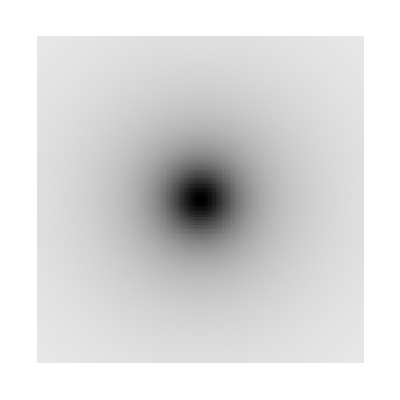

```mathematica
ArrayPlot[pot[[64,;;,;;]]]
```

We can also plot one cross section of potential as below:

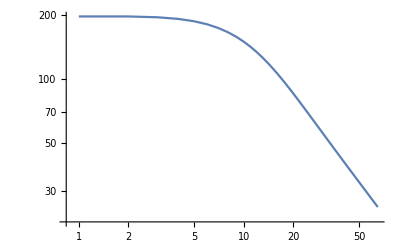

```mathematica
ListLogLogPlot[Abs@pot[[64,64,64;;]], Joined->True]
```

Note that above you’re just plotting the values of pot against numbers running from 1 to 64. If you wanted to define a radius to plot against, you could do something like this:

```mathematica
rval = (Range[0,64] +0.5)* 2.0/128;
```

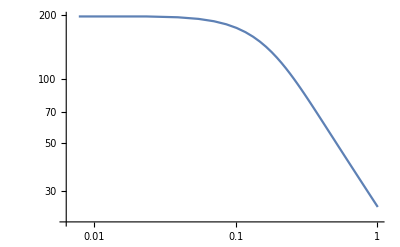

```mathematica
ListLogLogPlot[Transpose[{rval,Abs@pot[[64,64,64;;]]}], Joined->True]
```

### What is the run.h5 file?

The run.h5 file is sort of the main output of chplUltra--it has things like the evolution of the mass, the density and energy profiles, etc.

```mathematica
ff = Import["test/run.h5", "Data"];
Keys@ff
```

{/info,/profiles/000000/KEc,/profiles/000000/KEq,/profiles/000000/PE,/profiles/000000/counts,/profiles/000000/mass,/profiles/000001/KEc,/profiles/000001/KEq,/profiles/000001/PE,/profiles/000001/counts,/profiles/000001/mass,/profiles/000002/KEc,/profiles/000002/KEq,/profiles/000002/PE,/profiles/000002/counts,/profiles/000002/mass,/profiles/000003/KEc,/profiles/000003/KEq,/profiles/000003/PE,/profiles/000003/counts,/profiles/000003/mass,/profiles/000004/KEc,/profiles/000004/KEq,/profiles/000004/PE,/profiles/000004/counts,/profiles/000004/mass,/profiles/000005/KEc,/profiles/000005/KEq,/profiles/000005/PE,/profiles/000005/counts,/profiles/000005/mass,/profiles/000006/KEc,/profiles/000006/KEq,/profiles/000006/PE,/profiles/000006/counts,/profiles/000006/mass,/profiles/000007/KEc,/profiles/000007/KEq,/profiles/000007/PE,/profiles/000007/counts,/profiles/000007/mass,/profiles/000008/KEc,/profiles/000008/KEq,/profiles/000008/PE,/profiles/000008/counts,/profiles/000008/mass,/profiles/000009/KEc,/profiles/000009/KEq,/profiles/000009/PE,/profiles/000009/counts,/profiles/000009/mass,/profiles/000010/KEc,/profiles/000010/KEq,/profiles/000010/PE,/profiles/000010/counts,/profiles/000010/mass,/timing}

"Keys" are what you give ff to ask for a specific bit of information. Eg, if you wanted to know how much time each of the steps took:

```mathematica
ff["/timing"]
```

{<|kick→0.,stream→0.,pot→0.,sponge→0.,analyse→0.|>,<|kick→0.021387,stream→0.353974,pot→0.708924,sponge→0.000174,analyse→0.810269|>,<|kick→0.04251,stream→0.70321,pot→1.41164,sponge→0.000348,analyse→1.29956|>,<|kick→0.063384,stream→1.05192,pot→2.11392,sponge→0.000521,analyse→1.7646|>,<|kick→0.08438,stream→1.40097,pot→2.81625,sponge→0.00069,analyse→2.28825|>,<|kick→0.105227,stream→1.74935,pot→3.5149,sponge→0.000862,analyse→2.76687|>,<|kick→0.126181,stream→2.09756,pot→4.21805,sponge→0.001035,analyse→3.26068|>,<|kick→0.146845,stream→2.44703,pot→4.91535,sponge→0.001208,analyse→3.77778|>,<|kick→0.167488,stream→2.79581,pot→5.61542,sponge→0.001385,analyse→4.26319|>,<|kick→0.188095,stream→3.14471,pot→6.31933,sponge→0.001556,analyse→4.7534|>,<|kick→0.208651,stream→3.49287,pot→7.01879,sponge→0.001728,analyse→5.2262|>}

See an example of how to get to the DM density profiles from run.h5 below :

```mathematica
ff = Import["test/run.h5", "Data"];
rho = ff["/profiles/000000/mass"]/ff["/profiles/000000/counts"];
```

You have to remember to divide by counts, otherwise you’ll get a cumulative density instead of a density profile!

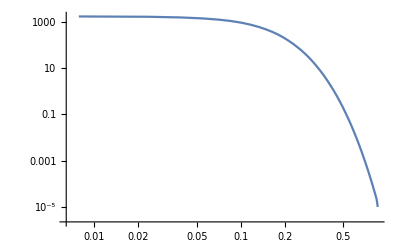

```mathematica
rval = (Range[1,64] -0.5)* 2.0/128;
ListLogLogPlot[Transpose[{rval,rho}], Joined->True]
```

### chplUltra Units

λ and m22 are constants; we tend to set them to 1.

#### Code units and conversions

```mathematica
maxion[m22_]:= (m22 10^-22)*(1.783*10^-36)  (* kg *)
hbar=1.0545718*10^-34; (* m^2 kg/s *)
parsec=3.0857*10^16 ; (* m *)
ly=9.4607*10^15 ; (* m *)
kpc = 3.086*10^19; (* m *)
mSun=1.989* 10^30; (* kg *)
G=6.673*10^-11; (*N m2 kg-2.*)
omegaM0=0.31 ;
H0=(67.7 * 10^3)/(parsec*10^6) ; (* s^-1 *)
```

#### Defining code units (in SI):

```mathematica
timeUnit[ λ_]:=((8*Pi)/(3 * H0^2* omegaM0))^(1/2)λ^-2 (*seconds*)
lengthUnit[m22_, λ_] := ((8 π hbar^2)/(3*maxion[m22]^2* H0^2*omegaM0))^(1/4)λ^-1 (*meters*)
massUnit[m22_, λ_] := 1/G((8 Pi)/(3 * H0^2*omegaM0))^(-1/4)(hbar/maxion[m22])^(3/2)λ^1 (*kg*)
```

#### Code units in “astronomical” units:

```mathematica
timeUnityears[ λ_] := timeUnit[ λ]/(Pi * 10^7) (* years *)
lengthUnitkpc[m22_, λ_] := lengthUnit[m22, λ]/kpc (* kpc *)
massUnitsolar[m22_, λ_] := massUnit[m22, λ]/mSun (* Solar masses *)
```

```mathematica
lengthUnitkpc[1,1]
```

38.3609

```mathematica
lengthUnitkpc[1,2.55739]
```

15.

```mathematica
Clear[λ]
```

```mathematica
Solve[((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)λ^-1/kpc ==15, λ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{λ→2.55739}}

Need to calculate the lambda you want for a choice of parameters; in the meantime, posting the table below with some ideas:

-Graphics-

### Units

λ = 8.7 is equivalent to one gigayear in code units
1. timeUnit[8.7] converts a gigayear from code units to seconds
2. timeUnityears[8.7] converts a gigayear from code units to years
3.

```mathematica
massUnit[1,1]
timeUnit[1]
timeUnityears[1]
lengthUnit[1,1]
lengthUnitkpc[1,1]

((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)
```

4.42837×10^36

2.36943×10^18

7.54212×10^10

1.18382×10^21

38.3609

1.18382×10^21

```mathematica
massUnit[1]
```

massUnit[1]

### Run in ChplUltra units

#### 1. Dimensionless ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp1pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10,6;;7}]
bp1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",11;;20,6;;7}]
bp1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",101;;110,6;;7}]
bp1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",201;;210,6;;7}];
bp1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",301;;310,6;;7}];
bp1pos50 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",501;;510,6;;7}];
bp1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",991;;1000,6;;7}]
bp1pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1991;;2000,6;;7}]
bp1pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",2991;;3000,6;;7}]
bp1pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",3991;;4000,6;;7}]
bp1pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",4991;;5000,6;;7}];
bp1pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",5991;;6000,6;;7}];
bp1pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",6991;;7000,6;;7}];
bp1pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",7991;;8000,6;;7}];
bp1pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",8991;;9000,6;;7}];
bp1pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",9991;;10000,6;;7}];
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,1.22465×10^-16},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,-2.44929×10^-16}}

{{0.814974,0.579497},{0.318709,0.947852},{-0.299293,0.954161},{-0.802975,0.596013},{-0.999948,0.0102073},{-0.814975,-0.579497},{-0.318709,-0.947853},{0.299293,-0.954161},{0.802975,-0.596012},{0.999947,-0.0102073}}

{{0.864676,0.502272},{0.404311,0.914596},{-0.210493,0.977578},{-0.744916,0.667166},{-0.9948,0.101898},{-0.864726,-0.502306},{-0.40433,-0.914648},{0.210501,-0.977606},{0.74491,-0.667162},{0.994754,-0.101897}}

{{0.925159,-0.373708},{0.968005,0.241395},{0.64121,0.764604},{0.0680481,0.99728},{-0.532358,0.847408},{-0.930238,0.37228},{-0.971717,-0.245868},{-0.641655,-0.76891},{-0.0677468,-0.998307},{0.529798,-0.846729}}

{{0.159866,-0.985501},{0.705711,-0.703303},{0.983829,-0.153763},{0.884772,0.458272},{0.442966,0.895085},{-0.173428,0.986313},{-0.723426,0.695622},{-0.994291,0.139485},{-0.887019,-0.468431},{-0.446814,-0.89565}}

{{-0.759414,-0.657777},{-0.233938,-0.975155},{0.379773,-0.925118},{0.849222,-0.521878},{0.991696,0.083126},{0.747634,0.656775},{0.211618,0.974553},{-0.405233,0.91506},{-0.86699,0.504948},{-1.00054,-0.0940527}}

{{-0.962155,0.292127},{-0.953904,-0.322671},{-0.588058,-0.816355},{-0.00167668,-1.00303},{0.584975,-0.809407},{0.947,-0.30549},{0.941097,0.316277},{0.569149,0.81492},{-0.0243167,0.997433},{-0.608399,0.796213}}

#### Position

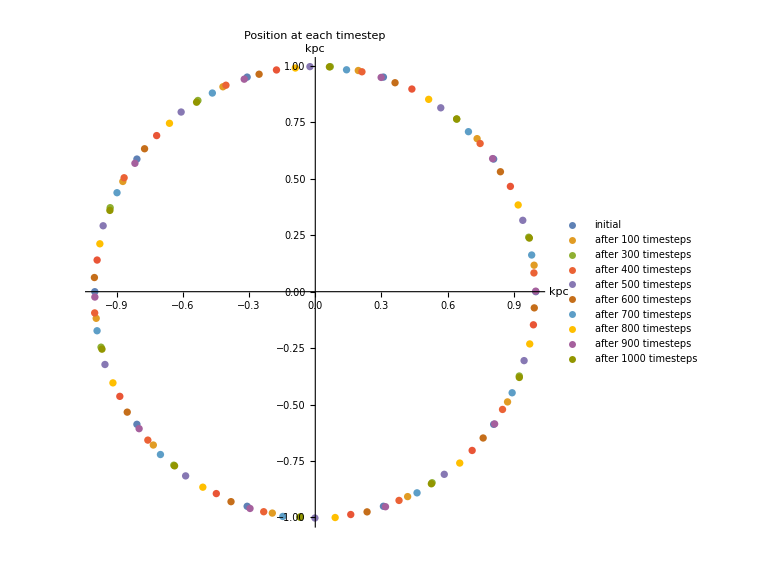

```mathematica
bp1posgraph = ListPlot[{bp1pos1,bp1pos50,bp1pos100,bp1pos300,bp1pos400,bp1pos500,bp1pos600,bp1pos700,bp1pos800,bp1pos900,bp1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

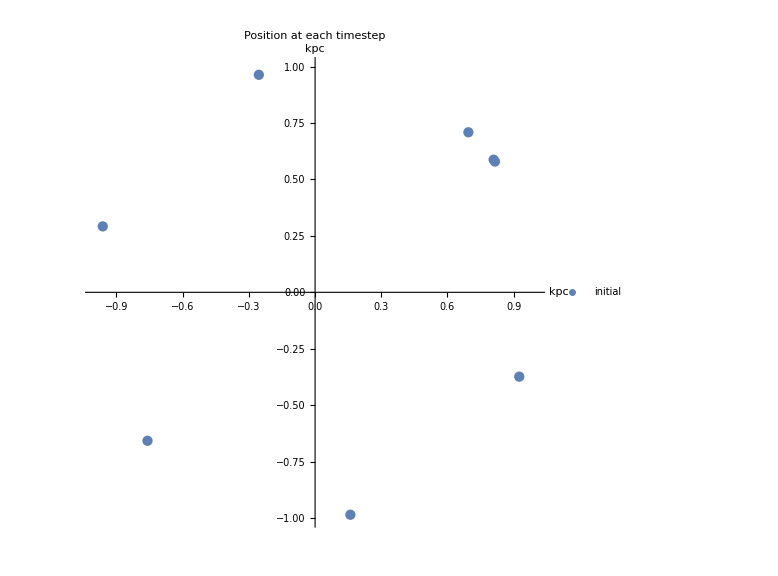

```mathematica
bp1pos2graph = ListPlot[{bp1pos1[[1]],bp1pos2[[1]],bp1pos100[[1]],bp1pos200[[1]],bp1pos300[[1]],bp1pos400[[1]],bp1pos500[[1]],bp1pos600[[1]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

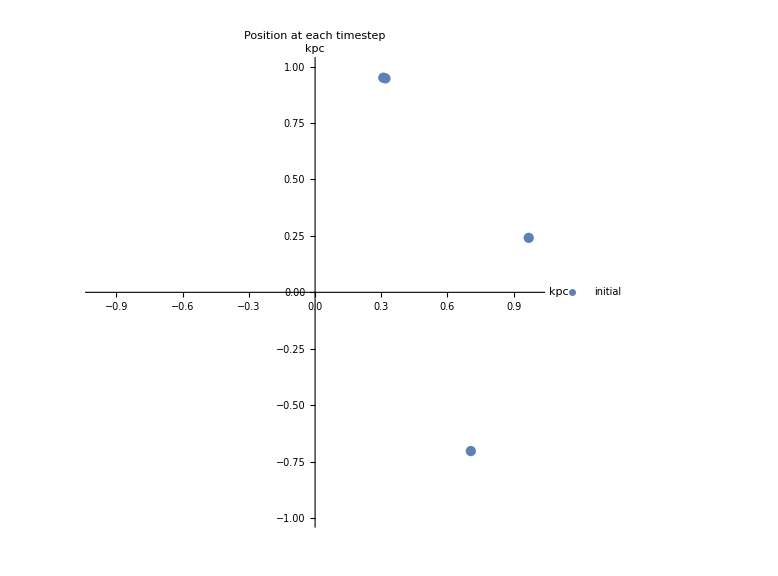

```mathematica
bp1pos3graph = ListPlot[{bp1pos1[[2]],bp1pos2[[2]],bp1pos100[[2]],bp1pos200[[2]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity

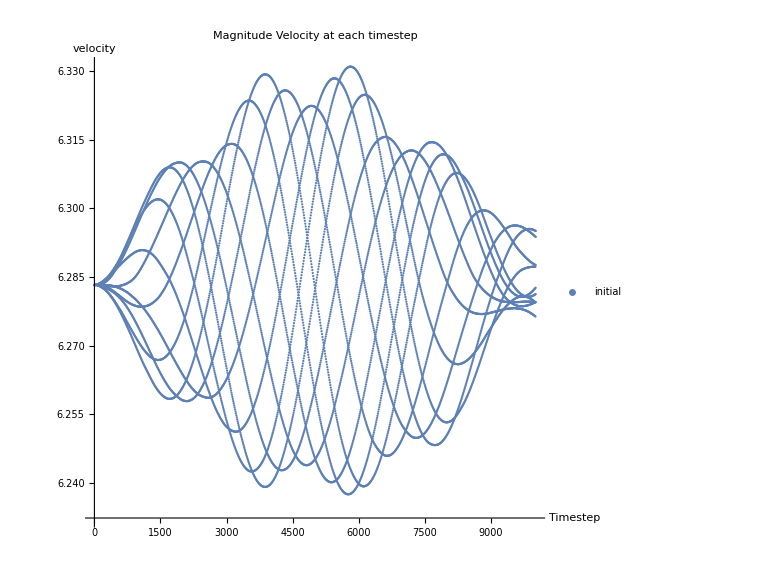

```mathematica
bp1vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10020,4}];
bp1velgraph = ListPlot[{bp1vel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","velocity"}, PlotLabel-> "Magnitude Velocity at each timestep"]
```

#### 2. ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1;;10,6;;7}];
bp2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",10;;20,6;;7}];
bp2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",100;;110,6;;7}];
bp2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",200;;210,6;;7}];
bp2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",300;;310,6;;7}];
bp2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",990;;1000,6;;7}];
bp2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1990;;2000,6;;7}];
bp2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",2990;;3000,6;;7}];
bp2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",3990;;4000,6;;7}];
bp2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",4990;;5000,6;;7}];
bp2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",5990;;6000,6;;7}];
bp2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",6990;;7000,6;;7}];
bp2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",7990;;8000,6;;7}];
bp2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",8990;;9000,6;;7}];
bp2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

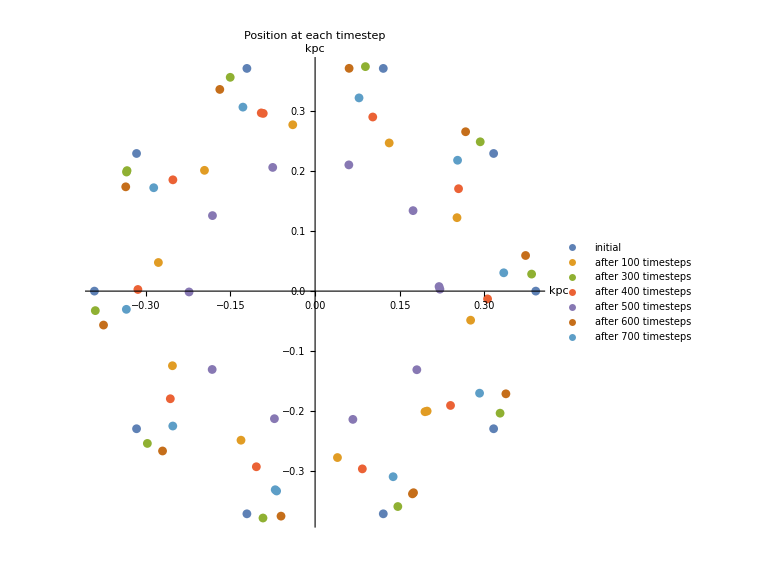

```mathematica
bp2posgraph = ListPlot[{bp2pos1,bp2pos100,bp2pos300,bp2pos400,bp2pos500,bp2pos600,bp2pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 3. Comparing grids between ChplUltra units and dimensionless units

Import Boxes

```mathematica
box1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/nfwbox1.csv",{"Data",1;;16384,1;;128}];
Min[box1]
box2 =Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/nfwbox2.csv",{"Data",1;;16384,1;;128}];
```

Min[25.2022,nan]

```mathematica
Min[Flatten@box1]
```

Min[25.2022,nan]

Setup

```mathematica
kpckm = 1/(3.24078^(-17))
yrsec = 60*60*24*365.24
f[a_,b_]:=(a - ((b * 38.3609 *(1.94249*10^16)*(1.94249*10^16))/ ((75.4212*10^9*yrsec)^2*15) ))
diff = {}
row = {}
```

4.7978×10^8

3.15567×10^7

{}

{}

Compare Boxes

```mathematica
For[i = 1,i<129,i++,row = {};For[j=1,j<129,j++,row = Append[row,f[box1[[i]][[j]],box2[[i]][[j]]]] ];diff=Append[diff,row]]
Print[diff]
```

{{-2.91902×10^-6,0.0000222289,0.0000584291,0.0000353309,0.0000936357,0.000092642,2.70066×10^-6,-5.83767×10^-6,0.0000670271,0.0000509441,0.0000162641,0.0000629872,0.0000614642,0.000141344,2.6272×10^-6,0.0000860148,0.000121156,0.000108051,0.0000467005,7.45417×10^-6,-9.68762×10^-6,-4.72483×10^-6,0.0000926933,0.000112216,0.000124194,0.0000582767,0.0000551654,0.0000445095,0.0000966596,0.0000412652,0.000119028,0.000159596,0.000162971,0.0000291513,0.0000988396,0.000031334,0.0000673361,0.000036495,9.16154×10^-6,0.0000853357,-5.33325×10^-6,0.0000778562,0.0000645532,-0.0000452421,0.0000891718,0.000127093,0.0000388731,0.0000245114,0.000154359,-0.0000122861,0.0000356288,0.0000574022,0.0000233847,0.0000335763,0.0000879772,0.0000865871,0.0000294063,0.0000867853,0.0000180228,0.000134171,0.0000241774,0.0000287438,0.0000478702,0.0000112057,0.0000891011,0.0000112057,0.0000478702,0.0000287438,0.0000241774,0.000134171,0.0000180228,0.0000867853,0.0000294063,0.0000865871,0.0000879772,0.0000335763,0.0000233847,0.0000574022,0.0000356288,-0.0000122861,0.000154359,0.0000245114,0.0000388731,0.000127093,0.0000891718,-0.0000452421,0.0000645532,0.0000778562,-5.33325×10^-6,0.0000853357,9.16154×10^-6,0.000036495,0.0000673361,0.000031334,0.0000988396,0.0000291513,0.000162971,0.000159596,0.000119028,0.0000412652,0.0000966596,0.0000445095,0.0000551654,0.0000582767,0.000124194,0.000112216,0.0000926933,-4.72483×10^-6,-9.68762×10^-6,7.45417×10^-6,0.0000467005,0.000108051,0.000121156,0.0000860148,2.6272×10^-6,0.000141344,0.0000614642,0.0000629872,0.0000162641,0.0000509441,0.0000670271,-5.83767×10^-6,2.70066×10^-6,0.000092642,0.0000936357,0.0000353309,0.0000584291,0.0000222289},{0.0000222289,0.000095623,0.0000393679,0.0000645159,0.0000303653,7.26709×10^-6,0.0000655719,0.000134929,0.0000153384,-0.0000228492,0.0000203663,0.000115336,0.0000213572,0.0000791326,0.0000886618,-0.0000204059,0.0000926309,0.0000574216,0.000144317,0.0000829659,0.0000437195,0.0000265777,0.000101891,-6.9058×10^-7,-0.0000108171,0.0000715117,0.0000462958,0.0000838861,0.0000139317,6.78339×10^-6,0.000132792,0.0000512559,0.000102877,0.0000876543,0.000035238,0.0000863294,0.0000705776,-0.0000120173,0.0000792462,0.000103667,0.0000315946,0.000133381,0.000138675,-0.0000525234,0.000100487,-0.0000429942,0.0000577334,0.0000323194,0.000151114,0.000143768,0.0000102799,0.0000913517,-0.000053718,0.0000157721,0.0000294714,0.0000873799,0.000159848,0.0000765257,0.0000374124,0.000012859,0.000102866,0.0000370812,0.000156208,-0.0000508077,0.0000270877,-0.0000508077,0.000156208,0.0000370812,0.000102866,0.000012859,0.0000374124,0.0000765257,0.000159848,0.0000873799,0.0000294714,0.0000157721,-0.000053718,0.0000913517,0.0000102799,0.000143768,0.000151114,0.0000323194,0.0000577334,-0.0000429942,0.000100487,-0.0000525234,0.000138675,0.000133381,0.0000315946,0.000103667,0.0000792462,-0.0000120173,0.0000705776,0.0000863294,0.000035238,0.0000876543,0.000102877,0.0000512559,0.000132792,6.78339×10^-6,0.0000139317,0.0000838861,0.0000462958,0.0000715117,-0.0000108171,-6.9058×10^-7,0.000101891,0.0000265777,0.0000437195,0.0000829659,0.000144317,0.0000574216,0.0000926309,-0.0000204059,0.0000886618,0.0000791326,0.0000213572,0.000115336,0.0000203663,-0.0000228492,0.0000153384,0.000134929,0.0000655719,7.26709×10^-6,0.0000303653,0.0000645159,0.0000393679,0.000095623},{0.0000584291,0.0000393679,0.000031359,0.000134402,0.0000781473,0.0000329444,0.000169145,-0.0000539536,0.000074702,0.00011441,0.0000355208,0.0000380347,0.0000923025,-0.0000423774,0.0000450472,0.0000842257,4.80716×10^-6,-0.0000525068,0.000112284,0.0000288284,-0.0000325226,0.0000985818,0.000151791,0.0000271044,-5.12674×10^-6,0.000125448,-0.0000218722,-6.3865×10^-6,0.0000719053,0.000113003,-0.0000534436,0.0000836172,0.0000131334,0.0000461573,0.000112338,0.0000413247,0.00014417,9.8212×10^-6,0.0000493309,0.0000923482,0.0000388731,-0.0000110943,0.0000127967,0.000010546,0.0000821538,0.00012762,0.0000469444,0.000110478,0.0000478702,0.0000294714,0.0000552818,0.0000253013,0.00003953,0.000168319,-0.0000290344,0.000158523,0.0000199394,0.0000662662,0.0000568021,0.0000618979,0.0000815537,0.000115769,-5.80584×10^-6,0.0000575297,-0.0000349257,0.0000575297,-5.80584×10^-6,0.000115769,0.0000815537,0.0000618979,0.0000568021,0.0000662662,0.0000199394,0.000158523,-0.0000290344,0.000168319,0.00003953,0.0000253013,0.0000552818,0.0000294714,0.0000478702,0.000110478,0.0000469444,0.00012762,0.0000821538,0.000010546,0.0000127967,-0.0000110943,0.0000388731,0.0000923482,0.0000493309,9.8212×10^-6,0.00014417,0.0000413247,0.000112338,0.0000461573,0.0000131334,0.0000836172,-0.0000534436,0.000113003,0.0000719053,-6.3865×10^-6,-0.0000218722,0.000125448,-5.12674×10^-6,0.0000271044,0.000151791,0.0000985818,-0.0000325226,0.0000288284,0.000112284,-0.0000525068,4.80716×10^-6,0.0000842257,0.0000450472,-0.0000423774,0.0000923025,0.0000380347,0.0000355208,0.00011441,0.000074702,-0.0000539536,0.000169145,0.0000329444,0.0000781473,0.000134402,0.000031359,0.0000393679},{0.0000353309,0.0000645159,0.000134402,0.0000449904,-0.0000333693,0.000169674,0.0000134189,0.000138567,0.0000747671,0.0000923704,0.0000913767,0.0000717861,0.0000335985,0.0000471648,0.000112485,-0.000040792,0.0000280357,0.0000486172,0.0000209525,0.0000857432,0.000102288,-0.0000590633,-0.0000279589,0.0000956008,0.0000412652,0.0000497356,0.0000506613,0.0000440424,2.29626×10^-7,0.0000895737,0.0000713731,0.0000863294,-0.0000359082,0.0000453618,-0.0000105621,0.0000370216,0.000088113,0.0000723612,0.0000601171,0.0000513806,0.000116502,0.000085132,0.00012762,0.000143966,0.000134171,0.000098234,0.000106506,0.0000886368,0.0000149766,0.0000855256,2.83658×10^-7,0.000129602,0.0000327781,-0.0000494856,-0.0000171894,0.000129667,0.000120732,0.000126357,0.000146543,0.000181288,-0.0000397582,0.0000241067,0.000172882,0.000065867,-0.0000265883,0.000065867,0.000172882,0.0000241067,-0.0000397582,0.000181288,0.000146543,0.000126357,0.000120732,0.000129667,-0.0000171894,-0.0000494856,0.0000327781,0.000129602,2.83658×10^-7,0.0000855256,0.0000149766,0.0000886368,0.000106506,0.000098234,0.000134171,0.000143966,0.00012762,0.000085132,0.000116502,0.0000513806,0.0000601171,0.0000723612,0.000088113,0.0000370216,-0.0000105621,0.0000453618,-0.0000359082,0.0000863294,0.0000713731,0.0000895737,2.29626×10^-7,0.0000440424,0.0000506613,0.0000497356,0.0000412652,0.0000956008,-0.0000279589,-0.0000590633,0.000102288,0.0000857432,0.0000209525,0.0000486172,0.0000280357,-0.000040792,0.000112485,0.0000471648,0.0000335985,0.0000717861,0.0000913767,0.0000923704,0.0000747671,0.000138567,0.0000134189,0.000169674,-0.0000333693,0.0000449904,0.000134402,0.0000645159},{0.0000936357,0.0000303653,0.0000781473,-0.0000333693,0.000136517,0.000147105,0.0000687455,0.0000717889,0.0000858845,0.0000813832,0.000158285,0.00011659,0.0000562977,0.000147759,0.0000206241,0.0000452426,0.0000919657,0.0000904426,0.0000406734,0.0000130087,0.0000777994,-5.65614×10^-6,3.34367×10^-6,0.000104799,-0.0000716414,0.0000147244,-6.45441×10^-6,0.0000351729,0.000139606,0.000036495,-0.0000334594,0.000129743,0.0000557516,0.000014917,0.0000775901,0.00017342,0.000102407,0.0000349012,0.000141254,0.000151114,0.0000644826,0.000151709,0.0000424431,-0.0000226136,-0.000013812,0.0000391988,0.000066068,0.0000371463,0.0000524338,0.0000119305,0.0000156363,0.000033902,-3.6231×10^-6,-0.0000265883,0.0000650064,8.10283×10^-7,0.000121525,-0.0000135515,0.000136283,0.000100677,0.000179631,0.0000731456,-0.0000187803,-0.0000257956,0.0001521,-0.0000257956,-0.0000187803,0.0000731456,0.000179631,0.000100677,0.000136283,-0.0000135515,0.000121525,8.10283×10^-7,0.0000650064,-0.0000265883,-3.6231×10^-6,0.000033902,0.0000156363,0.0000119305,0.0000524338,0.0000371463,0.000066068,0.0000391988,-0.000013812,-0.0000226136,0.0000424431,0.000151709,0.0000644826,0.000151114,0.000141254,0.0000349012,0.000102407,0.00017342,0.0000775901,0.000014917,0.0000557516,0.000129743,-0.0000334594,0.000036495,0.000139606,0.0000351729,-6.45441×10^-6,0.0000147244,-0.0000716414,0.000104799,3.34367×10^-6,-5.65614×10^-6,0.0000777994,0.0000130087,0.0000406734,0.0000904426,0.0000919657,0.0000452426,0.0000206241,0.000147759,0.0000562977,0.00011659,0.000158285,0.0000813832,0.0000858845,0.0000717889,0.0000687455,0.000147105,0.000136517,-0.0000333693,0.0000781473,0.0000303653},{0.000092642,7.26709×10^-6,0.0000329444,0.000169674,0.000147105,0.0000355887,0.0000351244,0.000116063,0.000108054,0.0000110976,0.0000658948,0.000102095,0.000119698,0.0000187046,0.000139816,0.0000423295,-3.40272×10^-6,0.0000729696,0.000171447,0.000121677,0.0000940126,-0.0000115475,-0.0000246522,0.0000546984,0.000126504,0.0000907655,0.0000474821,0.0000670049,0.0000493337,-5.53143×10^-6,0.00017276,0.000113858,0.000088113,0.0000955246,0.000136093,0.0000801692,0.0000574022,0.000108494,-7.25823×10^-6,0.000121199,-0.0000171866,0.0000886368,0.000168319,-0.0000484919,0.000149257,-0.0000494856,0.0000663313,0.000126357,-0.0000397582,8.68617×10^-6,0.0000716904,0.0000789039,0.000100677,0.0000666597,0.000117553,0.0000126553,0.0000926683,0.0000872413,0.0000963741,0.0000200669,0.0000990211,0.0000221845,0.0000302586,0.000123243,0.000030788,0.000123243,0.0000302586,0.0000221845,0.0000990211,0.0000200669,0.0000963741,0.0000872413,0.0000926683,0.0000126553,0.000117553,0.0000666597,0.000100677,0.0000789039,0.0000716904,8.68617×10^-6,-0.0000397582,0.000126357,0.0000663313,-0.0000494856,0.000149257,-0.0000484919,0.000168319,0.0000886368,-0.0000171866,0.000121199,-7.25823×10^-6,0.000108494,0.0000574022,0.0000801692,0.000136093,0.0000955246,0.000088113,0.000113858,0.00017276,-5.53143×10^-6,0.0000493337,0.0000670049,0.0000474821,0.0000907655,0.000126504,0.0000546984,-0.0000246522,-0.0000115475,0.0000940126,0.000121677,0.000171447,0.0000729696,-3.40272×10^-6,0.0000423295,0.000139816,0.0000187046,0.000119698,0.000102095,0.0000658948,0.0000110976,0.000108054,0.000116063,0.0000351244,0.0000355887,0.000147105,0.000169674,0.0000329444,7.26709×10^-6},{2.70066×10^-6,0.0000655719,0.000169145,0.0000134189,0.0000687455,0.0000351244,0.0000125556,0.00017139,0.000141276,0.000022215,0.000154908,-1.34747×10^-6,0.0000941512,-0.000028947,-2.91448×10^-7,0.000150469,0.0000826319,-0.0000334511,0.000142921,0.0000710474,0.000121278,-6.3865×10^-6,0.0000584042,0.0000156502,0.0000653515,0.000107508,0.0000421202,0.000109889,0.0000701133,-6.85632×10^-6,0.0000493309,0.000138675,-9.17488×10^-6,0.0000464829,0.0000352976,0.00012762,0.0000530991,0.0000524366,0.0000552818,-0.0000383654,0.000112197,0.0000662662,-5.80584×10^-6,0.0000663313,0.0000123268,0.000172882,0.000107296,0.0000859191,8.7513×10^-6,0.0000461434,0.0000980954,0.0000942565,0.000104978,0.0000302586,0.00014045,0.0000948511,0.0000341626,-0.000011966,0.0000268161,0.000150509,0.0000887616,0.000111925,0.0000496482,-0.0000277178,0.000150178,-0.0000277178,0.0000496482,0.000111925,0.0000887616,0.000150509,0.0000268161,-0.000011966,0.0000341626,0.0000948511,0.00014045,0.0000302586,0.000104978,0.0000942565,0.0000980954,0.0000461434,8.7513×10^-6,0.0000859191,0.000107296,0.000172882,0.0000123268,0.0000663313,-5.80584×10^-6,0.0000662662,0.000112197,-0.0000383654,0.0000552818,0.0000524366,0.0000530991,0.00012762,0.0000352976,0.0000464829,-9.17488×10^-6,0.000138675,0.0000493309,-6.85632×10^-6,0.0000701133,0.000109889,0.0000421202,0.000107508,0.0000653515,0.0000156502,0.0000584042,-6.3865×10^-6,0.000121278,0.0000710474,0.000142921,-0.0000334511,0.0000826319,0.000150469,-2.91448×10^-7,-0.000028947,0.0000941512,-1.34747×10^-6,0.000154908,0.000022215,0.000141276,0.00017139,0.0000125556,0.0000351244,0.0000687455,0.0000134189,0.000169145,0.0000655719},{-5.83767×10^-6,0.000134929,-0.0000539536,0.000138567,0.0000717889,0.000116063,0.00017139,0.0000377686,0.0000855505,0.0000443848,-0.000015378,0.0000766131,-0.0000203436,0.0000344536,0.0000410046,-6.9058×10^-7,9.36804×10^-6,0.000141531,0.000125448,0.00013147,0.000159596,0.000109827,0.0000525128,0.0000876543,-0.0000550997,0.000135303,0.0000478106,0.0000934749,0.0000315946,0.000102871,0.0000369537,4.1932×10^-6,4.58955×10^-6,0.000108494,0.000145554,0.0000157721,0.000159848,0.0000370812,0.000158523,0.0000131223,0.0000119305,0.000084597,0.000031122,0.000121856,-0.0000135515,-4.74982×10^-6,0.000118612,0.0000861825,0.0000979623,-0.0000460487,0.0000948511,0.000150311,0.0000499795,0.0000345589,0.0000336983,0.000117748,0.000116358,0.000099879,0.0000979595,-0.0000190492,-0.0000511473,0.000172016,0.000109739,0.000132373,0.000139918,0.000132373,0.000109739,0.000172016,-0.0000511473,-0.0000190492,0.0000979595,0.000099879,0.000116358,0.000117748,0.0000336983,0.0000345589,0.0000499795,0.000150311,0.0000948511,-0.0000460487,0.0000979623,0.0000861825,0.000118612,-4.74982×10^-6,-0.0000135515,0.000121856,0.000031122,0.000084597,0.0000119305,0.0000131223,0.000158523,0.0000370812,0.000159848,0.0000157721,0.000145554,0.000108494,4.58955×10^-6,4.1932×10^-6,0.0000369537,0.000102871,0.0000315946,0.0000934749,0.0000478106,0.000135303,-0.0000550997,0.0000876543,0.0000525128,0.000109827,0.000159596,0.00013147,0.000125448,0.000141531,9.36804×10^-6,-6.9058×10^-7,0.0000410046,0.0000344536,-0.0000203436,0.0000766131,-0.000015378,0.0000443848,0.0000855505,0.0000377686,0.00017139,0.000116063,0.0000717889,0.000138567,-0.0000539536,0.000134929},{0.0000670271,0.0000153384,0.000074702,0.0000747671,0.0000858845,0.000108054,0.000141276,0.0000855505,0.0000408771,-0.0000223932,-4.26057×10^-6,-4.72483×10^-6,0.0000465647,0.0000792573,-6.64704×10^-6,0.0000295532,0.000117507,0.0000572151,0.000119028,0.000102945,-0.0000613846,0.000137092,0.000157674,3.59895×10^-7,5.85208×10^-6,3.79961×10^-6,0.0000645532,0.000088113,4.12806×10^-6,0.0000533,0.0000356288,0.000151114,0.0000294063,0.0000112057,0.0000965127,0.0000149766,0.000107299,0.0000327781,0.000102466,0.0000756623,0.0000227167,0.0000436294,8.7513×10^-6,0.000118082,1.27177×10^-6,0.0000990211,-0.0000293711,-0.0000432035,0.0000575241,0.0000728116,-0.0000676917,0.0000767156,0.0000356828,0.000179561,-0.0000323521,0.0000109964,-0.0000310952,0.000182075,0.000109805,0.000122445,0.000119996,2.45807×10^-6,0.000140181,-7.53542×10^-6,9.24247×10^-9,-7.53542×10^-6,0.000140181,2.45807×10^-6,0.000119996,0.000122445,0.000109805,0.000182075,-0.0000310952,0.0000109964,-0.0000323521,0.000179561,0.0000356828,0.0000767156,-0.0000676917,0.0000728116,0.0000575241,-0.0000432035,-0.0000293711,0.0000990211,1.27177×10^-6,0.000118082,8.7513×10^-6,0.0000436294,0.0000227167,0.0000756623,0.000102466,0.0000327781,0.000107299,0.0000149766,0.0000965127,0.0000112057,0.0000294063,0.000151114,0.0000356288,0.0000533,4.12806×10^-6,0.000088113,0.0000645532,3.79961×10^-6,5.85208×10^-6,3.59895×10^-7,0.000157674,0.000137092,-0.0000613846,0.000102945,0.000119028,0.0000572151,0.000117507,0.0000295532,-6.64704×10^-6,0.0000792573,0.0000465647,-4.72483×10^-6,-4.26057×10^-6,-0.0000223932,0.0000408771,0.0000855505,0.000141276,0.000108054,0.0000858845,0.0000747671,0.000074702,0.0000153384},{0.0000509441,-0.0000228492,0.00011441,0.0000923704,0.0000813832,0.0000110976,0.000022215,0.0000443848,-0.0000223932,-7.7682×10^-6,0.0000882599,0.0000656911,0.0000245253,0.000135113,0.0000271044,-0.0000291507,0.0000366987,0.000054302,0.0000940099,0.0000854715,0.0000693885,0.0000754101,0.000173887,-5.53143×10^-6,0.0000778562,0.0000536991,0.0000923482,0.0000938034,-0.0000122861,0.000085132,0.000145356,0.000138737,0.0000652753,0.0000249701,0.000158523,0.000125233,-4.54886×10^-6,0.0000395272,-0.000012889,0.0000789039,-0.0000257956,0.0000137141,0.0000974329,0.0000550101,-0.0000432035,0.0000731428,0.0000336983,0.000108814,0.0000281382,0.000132373,0.0000808178,0.0000141728,-0.0000379122,-5.08659×10^-6,0.0000126497,0.000115297,0.0000325037,0.000104972,-7.99968×10^-6,0.00003429,-0.0000385095,0.0000439523,0.000111325,-0.0000363919,0.0000711527,-0.0000363919,0.000111325,0.0000439523,-0.0000385095,0.00003429,-7.99968×10^-6,0.000104972,0.0000325037,0.000115297,0.0000126497,-5.08659×10^-6,-0.0000379122,0.0000141728,0.0000808178,0.000132373,0.0000281382,0.000108814,0.0000336983,0.0000731428,-0.0000432035,0.0000550101,0.0000974329,0.0000137141,-0.0000257956,0.0000789039,-0.000012889,0.0000395272,-4.54886×10^-6,0.000125233,0.000158523,0.0000249701,0.0000652753,0.000138737,0.000145356,0.000085132,-0.0000122861,0.0000938034,0.0000923482,0.0000536991,0.0000778562,-5.53143×10^-6,0.000173887,0.0000754101,0.0000693885,0.0000854715,0.0000940099,0.000054302,0.0000366987,-0.0000291507,0.0000271044,0.000135113,0.0000245253,0.0000656911,0.0000882599,-7.7682×10^-6,-0.0000223932,0.0000443848,0.000022215,0.0000110976,0.0000813832,0.0000923704,0.00011441,-0.0000228492},{0.0000162641,0.0000203663,0.0000355208,0.0000913767,0.000158285,0.0000658948,0.000154908,-0.000015378,-4.26057×10^-6,0.0000882599,0.000162183,0.0000471592,0.0000838889,2.02156×10^-6,0.000142259,0.000163899,0.000137293,0.000132792,0.0000800445,0.0000494016,0.000111214,0.000095131,1.15261×10^-6,0.00016998,0.0000609126,0.0000146509,0.0000311954,0.000010546,0.0000527027,0.000128016,0.0000661359,0.0000374124,0.000112197,0.000120138,0.000131586,0.000146543,0.0000650064,0.000157329,0.0000531586,0.0000931977,0.000107095,0.0000948511,0.0000268161,2.99025×10^-6,0.0000937243,0.0000583168,0.00010782,0.000101532,0.000109805,0.000132637,-0.0000299712,-7.66846×10^-6,-4.55024×10^-7,0.0000916691,0.0000983531,0.000160299,0.000036804,0.0000685708,-0.0000147516,0.0000571873,0.000014037,0.0000261481,0.0000935206,0.000145804,-0.0000170023,0.000145804,0.0000935206,0.0000261481,0.000014037,0.0000571873,-0.0000147516,0.0000685708,0.000036804,0.000160299,0.0000983531,0.0000916691,-4.55024×10^-7,-7.66846×10^-6,-0.0000299712,0.000132637,0.000109805,0.000101532,0.00010782,0.0000583168,0.0000937243,2.99025×10^-6,0.0000268161,0.0000948511,0.000107095,0.0000931977,0.0000531586,0.000157329,0.0000650064,0.000146543,0.000131586,0.000120138,0.000112197,0.0000374124,0.0000661359,0.000128016,0.0000527027,0.000010546,0.0000311954,0.0000146509,0.0000609126,0.00016998,1.15261×10^-6,0.000095131,0.000111214,0.0000494016,0.0000800445,0.000132792,0.000137293,0.000163899,0.000142259,2.02156×10^-6,0.0000838889,0.0000471592,0.000162183,0.0000882599,-4.26057×10^-6,-0.000015378,0.000154908,0.0000658948,0.000158285,0.0000913767,0.0000355208,0.0000203663},{0.0000629872,0.000115336,0.0000380347,0.0000717861,0.00011659,0.000102095,-1.34747×10^-6,0.0000766131,-4.72483×10^-6,0.0000656911,0.0000471592,0.000180381,0.0000246555,0.0000206836,0.0000684656,0.0000680013,0.000119291,0.0000223342,0.0000474821,-5.26534×10^-6,-0.0000359082,0.0000259042,9.8212×10^-6,0.0000565443,0.000025372,-0.0000429942,0.0000514457,8.69172×10^-6,0.0000287438,0.0000819528,0.000168319,0.0000174906,0.0000701702,0.000126357,0.0000157014,0.0000789039,0.000045614,0.0000861825,0.0000302586,0.0000185438,0.0000806875,0.0000870403,0.000137602,0.000132373,0.0000713537,-0.0000454569,0.0000226432,0.0000349525,0.0000321724,0.0000439523,0.000140643,0.000151893,0.000148054,0.000129126,0.0000951088,0.000046002,0.0000521566,0.000043222,-0.0000104513,0.0000911369,0.0000776358,0.0000193961,0.000116418,0.000168701,5.89501×10^-6,0.000168701,0.000116418,0.0000193961,0.0000776358,0.0000911369,-0.0000104513,0.000043222,0.0000521566,0.000046002,0.0000951088,0.000129126,0.000148054,0.000151893,0.000140643,0.0000439523,0.0000321724,0.0000349525,0.0000226432,-0.0000454569,0.0000713537,0.000132373,0.000137602,0.0000870403,0.0000806875,0.0000185438,0.0000302586,0.0000861825,0.000045614,0.0000789039,0.0000157014,0.000126357,0.0000701702,0.0000174906,0.000168319,0.0000819528,0.0000287438,8.69172×10^-6,0.0000514457,-0.0000429942,0.000025372,0.0000565443,9.8212×10^-6,0.0000259042,-0.0000359082,-5.26534×10^-6,0.0000474821,0.0000223342,0.000119291,0.0000680013,0.0000684656,0.0000206836,0.0000246555,0.000180381,0.0000471592,0.0000656911,-4.72483×10^-6,0.0000766131,-1.34747×10^-6,0.000102095,0.00011659,0.0000717861,0.0000380347,0.000115336},{0.0000614642,0.0000213572,0.0000923025,0.0000335985,0.0000562977,0.000119698,0.0000941512,-0.0000203436,0.0000465647,0.0000245253,0.0000838889,0.0000246555,0.0000468252,0.0000207488,0.000146426,0.0000535065,0.0000826915,0.0000636303,0.000166674,0.0000214708,-0.0000312767,0.000108431,0.0000702436,0.0000245114,0.000141585,0.000151114,0.0000530991,-0.0000117595,-0.000013812,0.0000172924,0.0000815537,0.0000789718,9.54679×10^-6,0.0000436294,-0.0000187803,0.0000926683,0.000107625,0.0000260885,0.0000887616,0.000125293,0.0000356828,-9.71816×10^-6,0.000159441,2.45807×10^-6,0.0000600353,0.0000321724,0.00011887,0.000120126,0.000135943,-0.0000336798,0.0000519585,0.0000521566,-0.0000627345,0.0000776358,0.000102917,0.0000131084,0.0000785616,0.0000992761,4.90135×10^-6,-0.000034212,0.000152287,0.000123696,0.0000503675,0.0000322999,0.0000398446,0.0000322999,0.0000503675,0.000123696,0.000152287,-0.000034212,4.90135×10^-6,0.0000992761,0.0000785616,0.0000131084,0.000102917,0.0000776358,-0.0000627345,0.0000521566,0.0000519585,-0.0000336798,0.000135943,0.000120126,0.00011887,0.0000321724,0.0000600353,2.45807×10^-6,0.000159441,-9.71816×10^-6,0.0000356828,0.000125293,0.0000887616,0.0000260885,0.000107625,0.0000926683,-0.0000187803,0.0000436294,9.54679×10^-6,0.0000789718,0.0000815537,0.0000172924,-0.000013812,-0.0000117595,0.0000530991,0.000151114,0.000141585,0.0000245114,0.0000702436,0.000108431,-0.0000312767,0.0000214708,0.000166674,0.0000636303,0.0000826915,0.0000535065,0.000146426,0.0000207488,0.0000468252,0.0000246555,0.0000838889,0.0000245253,0.0000465647,-0.0000203436,0.0000941512,0.000119698,0.0000562977,0.0000335985,0.0000923025,0.0000213572},{0.000141344,0.0000791326,-0.0000423774,0.0000471648,0.000147759,0.0000187046,-0.000028947,0.0000344536,0.0000792573,0.000135113,2.02156×10^-6,0.0000206836,0.0000207488,0.000172568,0.00010579,0.0000907655,0.0000274952,0.0000863294,-3.0826×10^-6,0.0000999608,-0.0000452421,0.0000723612,0.000112069,0.000144232,0.0000688508,0.0000562755,0.000106506,-0.0000508077,0.000095386,0.000104386,0.000146543,0.000121856,0.000100677,0.0000126553,0.0000984917,0.0000878358,0.0000806875,0.000117748,0.0000583168,0.0000430945,0.0000720813,0.000145277,-7.66846×10^-6,0.000124297,0.000100471,0.0000208541,0.0000261481,0.000046002,0.0000507666,-0.0000299089,0.000144677,0.000033823,0.0000782303,0.000107548,0.000021777,-8.73281×10^-6,0.00018637,-3.9682×10^-6,0.0000313063,0.0000218422,0.00013799,0.0000390491,0.0000657201,0.000147653,0.0000848465,0.000147653,0.0000657201,0.0000390491,0.00013799,0.0000218422,0.0000313063,-3.9682×10^-6,0.00018637,-8.73281×10^-6,0.000021777,0.000107548,0.0000782303,0.000033823,0.000144677,-0.0000299089,0.0000507666,0.000046002,0.0000261481,0.0000208541,0.000100471,0.000124297,-7.66846×10^-6,0.000145277,0.0000720813,0.0000430945,0.0000583168,0.000117748,0.0000806875,0.0000878358,0.0000984917,0.0000126553,0.000100677,0.000121856,0.000146543,0.000104386,0.000095386,-0.0000508077,0.000106506,0.0000562755,0.0000688508,0.000144232,0.000112069,0.0000723612,-0.0000452421,0.0000999608,-3.0826×10^-6,0.0000863294,0.0000274952,0.0000907655,0.00010579,0.000172568,0.0000207488,0.0000206836,2.02156×10^-6,0.000135113,0.0000792573,0.0000344536,-0.000028947,0.0000187046,0.000147759,0.0000471648,-0.0000423774,0.0000791326},{2.6272×10^-6,0.0000886618,0.0000450472,0.000112485,0.0000206241,0.000139816,-2.91448×10^-7,0.0000410046,-6.64704×10^-6,0.0000271044,0.000142259,0.0000684656,0.000146426,0.00010579,-0.0000534436,9.42762×10^-6,0.0000240527,0.000160782,0.0000492657,0.0000598538,-7.45363×10^-6,0.0000176943,0.0000352976,0.000145356,0.0000478702,0.00011319,-0.0000290344,0.0000618979,0.0000156363,0.000172882,0.0000929344,0.0000461434,2.85998×10^-6,0.0000630842,0.0000268161,0.0000644063,5.50421×10^-6,0.0000204605,0.0000796259,0.0000126497,0.0000898827,0.000111325,-0.0000230239,0.0000571873,0.0000519585,0.00016129,0.00018518,0.0000236313,0.0000469929,0.0000552651,-0.0000515519,0.0000968924,0.000130247,0.0000485132,0.0000220404,0.00012118,0.00010523,0.0000445413,0.0000391142,0.0000592994,0.000034746,0.0000358048,0.000092125,0.0000740575,0.000111251,0.0000740575,0.000092125,0.0000358048,0.000034746,0.0000592994,0.0000391142,0.0000445413,0.00010523,0.00012118,0.0000220404,0.0000485132,0.000130247,0.0000968924,-0.0000515519,0.0000552651,0.0000469929,0.0000236313,0.00018518,0.00016129,0.0000519585,0.0000571873,-0.0000230239,0.000111325,0.0000898827,0.0000126497,0.0000796259,0.0000204605,5.50421×10^-6,0.0000644063,0.0000268161,0.0000630842,2.85998×10^-6,0.0000461434,0.0000929344,0.000172882,0.0000156363,0.0000618979,-0.0000290344,0.00011319,0.0000478702,0.000145356,0.0000352976,0.0000176943,-7.45363×10^-6,0.0000598538,0.0000492657,0.000160782,0.0000240527,9.42762×10^-6,-0.0000534436,0.00010579,0.000146426,0.0000684656,0.000142259,0.0000271044,-6.64704×10^-6,0.0000410046,-2.91448×10^-7,0.000139816,0.0000206241,0.000112485,0.0000450472,0.0000886618},{0.0000860148,-0.0000204059,0.0000842257,-0.000040792,0.0000452426,0.0000423295,0.000150469,-6.9058×10^-7,0.0000295532,-0.0000291507,0.000163899,0.0000680013,0.0000535065,0.0000907655,9.42762×10^-6,0.000150194,-0.000027636,0.0000166383,-0.0000169828,0.0000715006,0.0000820886,0.000085132,0.0000102799,0.000098234,0.0000786433,-0.0000484919,0.0000575297,0.000126357,0.0000579912,0.0000227818,0.0000207293,0.0000221845,-0.0000432035,0.0000652669,6.89423×10^-6,0.0000927307,0.000182075,0.000145277,0.0000823381,-0.0000363919,-0.0000109128,0.000129126,0.000113375,0.0000418319,0.0001552,0.0000127772,0.0000552651,0.0000826637,0.000094973,0.0000218422,3.97281×10^-6,0.0000413649,0.0000636676,0.0000412318,0.0000740575,0.0000621446,0.000105493,0.000174454,0.000198676,0.0000781597,0.0000832555,0.0000139635,0.000170284,0.0000818655,0.0000190594,0.0000818655,0.000170284,0.0000139635,0.0000832555,0.0000781597,0.000198676,0.000174454,0.000105493,0.0000621446,0.0000740575,0.0000412318,0.0000636676,0.0000413649,3.97281×10^-6,0.0000218422,0.000094973,0.0000826637,0.0000552651,0.0000127772,0.0001552,0.0000418319,0.000113375,0.000129126,-0.0000109128,-0.0000363919,0.0000823381,0.000145277,0.000182075,0.0000927307,6.89423×10^-6,0.0000652669,-0.0000432035,0.0000221845,0.0000207293,0.0000227818,0.0000579912,0.000126357,0.0000575297,-0.0000484919,0.0000786433,0.000098234,0.0000102799,0.000085132,0.0000820886,0.0000715006,-0.0000169828,0.0000166383,-0.000027636,0.000150194,9.42762×10^-6,0.0000907655,0.0000535065,0.0000680013,0.000163899,-0.0000291507,0.0000295532,-6.9058×10^-7,0.000150469,0.0000423295,0.0000452426,-0.000040792,0.0000842257,-0.0000204059},{0.000121156,0.0000926309,4.80716×10^-6,0.0000280357,0.0000919657,-3.40272×10^-6,0.0000826319,9.36804×10^-6,0.000117507,0.0000366987,0.000137293,0.000119291,0.0000826915,0.0000274952,0.0000240527,-0.000027636,0.00014278,-5.40116×10^-6,0.0000388731,0.0000349012,0.0000233847,-0.0000660273,0.000107367,0.000102866,0.0000611703,0.0000119305,0.0000958475,-0.0000277802,0.0001521,0.0000947859,-0.0000293711,0.0000499795,0.000132838,-0.0000511473,0.000109077,2.45807×10^-6,0.0000400483,0.000051497,0.000036804,-0.0000336798,0.000110396,0.0000283308,0.000131176,0.0000782303,0.0000398446,0.00018637,0.000147454,0.0000934499,0.000124356,0.000040173,0.000111251,0.000137591,0.0000488416,0.0000153535,0.000107478,0.000154863,0.0000575102,0.0000857694,0.0000692901,-0.000021577,0.000013168,-0.0000264747,-0.0000405052,-0.0000289235,8.27038×10^-6,-0.0000289235,-0.0000405052,-0.0000264747,0.000013168,-0.000021577,0.0000692901,0.0000857694,0.0000575102,0.000154863,0.000107478,0.0000153535,0.0000488416,0.000137591,0.000111251,0.000040173,0.000124356,0.0000934499,0.000147454,0.00018637,0.0000398446,0.0000782303,0.000131176,0.0000283308,0.000110396,-0.0000336798,0.000036804,0.000051497,0.0000400483,2.45807×10^-6,0.000109077,-0.0000511473,0.000132838,0.0000499795,-0.0000293711,0.0000947859,0.0001521,-0.0000277802,0.0000958475,0.0000119305,0.0000611703,0.000102866,0.000107367,-0.0000660273,0.0000233847,0.0000349012,0.0000388731,-5.40116×10^-6,0.00014278,-0.000027636,0.0000240527,0.0000274952,0.0000826915,0.000119291,0.000137293,0.0000366987,0.000117507,9.36804×10^-6,0.0000826319,-3.40272×10^-6,0.0000919657,0.0000280357,4.80716×10^-6,0.0000926309},{0.000108051,0.0000574216,-0.0000525068,0.0000486172,0.0000904426,0.0000729696,-0.0000334511,0.000141531,0.0000572151,0.000054302,0.000132792,0.0000223342,0.0000636303,0.0000863294,0.000160782,0.0000166383,-5.40116×10^-6,0.000094664,0.0000464829,0.0000204065,0.0000867853,0.000175269,0.000156208,0.000129602,-4.54886×10^-6,0.0000241067,0.0000859191,0.0000401869,0.0000979623,0.0000185438,-0.0000277178,0.000099879,-9.71816×10^-6,-0.0000454569,0.0000926628,0.00003429,0.000120126,9.47055×10^-6,0.000113375,0.0000911369,0.0000131084,0.0000496399,0.000100731,-3.9682×10^-6,-0.000023757,0.0000413649,0.0000210467,-0.0000143608,0.000105493,0.000110258,0.000170284,0.0000152205,0.0000857694,0.0000412291,0.0000223009,0.0000289849,-9.06959×10^-6,0.000148839,0.000162009,0.000100791,0.000165185,0.0000551917,0.0000708104,0.0000823921,0.000119586,0.0000823921,0.0000708104,0.0000551917,0.000165185,0.000100791,0.000162009,0.000148839,-9.06959×10^-6,0.0000289849,0.0000223009,0.0000412291,0.0000857694,0.0000152205,0.000170284,0.000110258,0.000105493,-0.0000143608,0.0000210467,0.0000413649,-0.000023757,-3.9682×10^-6,0.000100731,0.0000496399,0.0000131084,0.0000911369,0.000113375,9.47055×10^-6,0.000120126,0.00003429,0.0000926628,-0.0000454569,-9.71816×10^-6,0.000099879,-0.0000277178,0.0000185438,0.0000979623,0.0000401869,0.0000859191,0.0000241067,-4.54886×10^-6,0.000129602,0.000156208,0.000175269,0.0000867853,0.0000204065,0.0000464829,0.000094664,-5.40116×10^-6,0.0000166383,0.000160782,0.0000863294,0.0000636303,0.0000223342,0.000132792,0.000054302,0.0000572151,0.000141531,-0.0000334511,0.0000729696,0.0000904426,0.0000486172,-0.0000525068,0.0000574216},{0.0000467005,0.000144317,0.000112284,0.0000209525,0.0000406734,0.000171447,0.000142921,0.000125448,0.000119028,0.0000940099,0.0000800445,0.0000474821,0.000166674,-3.0826×10^-6,0.0000492657,-0.0000169828,0.0000388731,0.0000464829,0.0000761973,0.000128016,0.00010194,0.000168319,0.0000568021,0.000108092,0.0000518365,-0.0000416125,0.0000980954,0.0000302586,-4.42137×10^-6,0.0000644063,-3.95988×10^-6,0.000101532,0.000140181,0.0000823381,0.0000983531,0.0000882266,0.0000519585,-0.0000104513,-0.0000286519,0.000167707,0.0000379252,0.0000227028,0.0000220404,0.000106289,0.000034746,0.000118465,0.0000167436,0.000170284,0.000108735,0.0000320962,0.0000107192,0.000114954,0.0000744511,0.0000892092,0.000129579,0.0000252112,-0.0000535448,0.0000636621,0.0000361305,0.000104562,0.0000986053,0.0000182611,0.0000338798,-0.0000248893,0.0000123046,-0.0000248893,0.0000338798,0.0000182611,0.0000986053,0.000104562,0.0000361305,0.0000636621,-0.0000535448,0.0000252112,0.000129579,0.0000892092,0.0000744511,0.000114954,0.0000107192,0.0000320962,0.000108735,0.000170284,0.0000167436,0.000118465,0.000034746,0.000106289,0.0000220404,0.0000227028,0.0000379252,0.000167707,-0.0000286519,-0.0000104513,0.0000519585,0.0000882266,0.0000983531,0.0000823381,0.000140181,0.000101532,-3.95988×10^-6,0.0000644063,-4.42137×10^-6,0.0000302586,0.0000980954,-0.0000416125,0.0000518365,0.000108092,0.0000568021,0.000168319,0.00010194,0.000128016,0.0000761973,0.0000464829,0.0000388731,-0.0000169828,0.0000492657,-3.0826×10^-6,0.000166674,0.0000474821,0.0000800445,0.0000940099,0.000119028,0.000125448,0.000142921,0.000171447,0.0000406734,0.0000209525,0.000112284,0.000144317},{7.45417×10^-6,0.0000829659,0.0000288284,0.0000857432,0.0000130087,0.000121677,0.0000710474,0.00013147,0.000102945,0.0000854715,0.0000494016,-5.26534×10^-6,0.0000214708,0.0000999608,0.0000598538,0.0000715006,0.0000349012,0.0000204065,0.000128016,0.0000873799,0.0000391988,0.0000131223,0.000049852,8.68617×10^-6,0.000100677,0.0000147729,0.000132376,0.0000424348,-0.0000143497,0.000132373,0.0000419026,0.00012529,0.0000418347,0.000132238,0.0000261481,-6.08303×10^-6,5.89501×10^-6,-8.26855×10^-6,0.000021777,-3.9682×10^-6,0.0000848465,0.000188221,0.0000358048,0.0000682992,0.0000153535,-0.0000526814,0.000134545,-0.0000636686,0.00006373,0.0000760393,0.00004361,0.000136793,0.000185237,0.0000889431,0.0000182611,0.000143542,0.0000240845,0.00010059,0.000102708,0.0000304373,0.0000541301,0.000173786,0.000119054,0.0000602847,0.0000271279,0.0000602847,0.000119054,0.000173786,0.0000541301,0.0000304373,0.000102708,0.00010059,0.0000240845,0.000143542,0.0000182611,0.0000889431,0.000185237,0.000136793,0.00004361,0.0000760393,0.00006373,-0.0000636686,0.000134545,-0.0000526814,0.0000153535,0.0000682992,0.0000358048,0.000188221,0.0000848465,-3.9682×10^-6,0.000021777,-8.26855×10^-6,5.89501×10^-6,-6.08303×10^-6,0.0000261481,0.000132238,0.0000418347,0.00012529,0.0000419026,0.000132373,-0.0000143497,0.0000424348,0.000132376,0.0000147729,0.000100677,8.68617×10^-6,0.000049852,0.0000131223,0.0000391988,0.0000873799,0.000128016,0.0000204065,0.0000349012,0.0000715006,0.0000598538,0.0000999608,0.0000214708,-5.26534×10^-6,0.0000494016,0.0000854715,0.000102945,0.00013147,0.0000710474,0.000121677,0.0000130087,0.0000857432,0.0000288284,0.0000829659},{-9.68762×10^-6,0.0000437195,-0.0000325226,0.000102288,0.0000777994,0.0000940126,0.000121278,0.000159596,-0.0000613846,0.0000693885,0.000111214,-0.0000359082,-0.0000312767,-0.0000452421,-7.45363×10^-6,0.0000820886,0.0000233847,0.0000867853,0.00010194,0.0000391988,0.000168913,0.000120732,0.0000650064,1.73604×10^-6,1.27177×10^-6,0.0000636136,0.0000887616,0.0000767156,-2.1735×10^-6,0.000122445,0.00018022,0.0000711527,0.000135943,0.000104242,0.000146398,-7.93733×10^-6,0.000152287,0.00018637,-5.68945×10^-6,0.000187162,0.0000538723,0.000105493,0.0000716738,0.0000524144,0.0000180657,-0.0000313723,0.0000744511,0.000165185,0.0000408299,0.0000420869,0.0000986053,0.0000103852,0.000118128,0.0000107816,-6.01947×10^-7,0.0000136267,0.000123818,0.000159622,0.0000210384,-0.0000215826,0.0000317594,0.0000810644,0.000126332,0.0000972125,0.000134406,0.0000972125,0.000126332,0.0000810644,0.0000317594,-0.0000215826,0.0000210384,0.000159622,0.000123818,0.0000136267,-6.01947×10^-7,0.0000107816,0.000118128,0.0000103852,0.0000986053,0.0000420869,0.0000408299,0.000165185,0.0000744511,-0.0000313723,0.0000180657,0.0000524144,0.0000716738,0.000105493,0.0000538723,0.000187162,-5.68945×10^-6,0.00018637,0.000152287,-7.93733×10^-6,0.000146398,0.000104242,0.000135943,0.0000711527,0.00018022,0.000122445,-2.1735×10^-6,0.0000767156,0.0000887616,0.0000636136,1.27177×10^-6,1.73604×10^-6,0.0000650064,0.000120732,0.000168913,0.0000391988,0.00010194,0.0000867853,0.0000233847,0.0000820886,-7.45363×10^-6,-0.0000452421,-0.0000312767,-0.0000359082,0.000111214,0.0000693885,-0.0000613846,0.000159596,0.000121278,0.0000940126,0.0000777994,0.000102288,-0.0000325226,0.0000437195},{-4.72483×10^-6,0.0000265777,0.0000985818,-0.0000590633,-5.65614×10^-6,-0.0000115475,-6.3865×10^-6,0.000109827,0.000137092,0.0000754101,0.000095131,0.0000259042,0.000108431,0.0000723612,0.0000176943,0.000085132,-0.0000660273,0.000175269,0.000168319,0.0000131223,0.000120732,0.000150446,0.000172616,0.0000872413,-5.67835×10^-6,0.0000345589,0.000137602,3.45174×10^-6,2.45807×10^-6,0.000104972,0.000140643,9.47055×10^-6,0.0000521566,0.000168701,0.0000887532,0.0000826637,0.000120783,0.0000327614,0.0000592994,0.0000300465,0.0000153535,0.0000152205,0.0000296474,0.0000289849,0.000113233,0.0000823921,0.0000364617,0.0000457927,0.0000103852,0.00010059,-0.0000242947,0.000146784,0.0000731234,0.0000250754,0.0000729904,0.000146518,0.0000456569,0.0000407592,0.0000318246,0.0000188528,0.000101844,0.0000807983,0.000155716,0.0000265957,-6.56118×10^-6,0.0000265957,0.000155716,0.0000807983,0.000101844,0.0000188528,0.0000318246,0.0000407592,0.0000456569,0.000146518,0.0000729904,0.0000250754,0.0000731234,0.000146784,-0.0000242947,0.00010059,0.0000103852,0.0000457927,0.0000364617,0.0000823921,0.000113233,0.0000289849,0.0000296474,0.0000152205,0.0000153535,0.0000300465,0.0000592994,0.0000327614,0.000120783,0.0000826637,0.0000887532,0.000168701,0.0000521566,9.47055×10^-6,0.000140643,0.000104972,2.45807×10^-6,3.45174×10^-6,0.000137602,0.0000345589,-5.67835×10^-6,0.0000872413,0.000172616,0.000150446,0.000120732,0.0000131223,0.000168319,0.000175269,-0.0000660273,0.000085132,0.0000176943,0.0000723612,0.000108431,0.0000259042,0.000095131,0.0000754101,0.000137092,0.000109827,-6.3865×10^-6,-0.0000115475,-5.65614×10^-6,-0.0000590633,0.0000985818,0.0000265777},{0.0000926933,0.000101891,0.000151791,-0.0000279589,3.34367×10^-6,-0.0000246522,0.0000584042,0.0000525128,0.000157674,0.000173887,1.15261×10^-6,9.8212×10^-6,0.0000702436,0.000112069,0.0000352976,0.0000102799,0.000107367,0.000156208,0.0000568021,0.000049852,0.0000650064,0.000172616,2.33058×10^-6,0.0000948511,0.000150178,0.0000979595,0.0000788983,0.0000226432,-4.55024×10^-7,0.000179954,0.0000935206,-0.0000597563,0.000131176,0.0000552651,0.000123563,0.0000657201,0.0000817352,0.00011231,0.0000167436,0.0000357369,0.0000692901,0.0000174032,0.0000504271,-1.9892×10^-6,0.000100856,0.0000182611,0.0000612784,0.0000892064,0.000142747,-0.0000188025,0.000115611,5.2866×10^-6,0.000190925,0.0000318246,0.0000686872,0.000101513,-0.0000400493,0.0000847023,0.0000350661,0.000151744,-5.96664×10^-6,0.000172988,0.000077554,0.000148434,0.0000152773,0.000148434,0.000077554,0.000172988,-5.96664×10^-6,0.000151744,0.0000350661,0.0000847023,-0.0000400493,0.000101513,0.0000686872,0.0000318246,0.000190925,5.2866×10^-6,0.000115611,-0.0000188025,0.000142747,0.0000892064,0.0000612784,0.0000182611,0.000100856,-1.9892×10^-6,0.0000504271,0.0000174032,0.0000692901,0.0000357369,0.0000167436,0.00011231,0.0000817352,0.0000657201,0.000123563,0.0000552651,0.000131176,-0.0000597563,0.0000935206,0.000179954,-4.55024×10^-7,0.0000226432,0.0000788983,0.0000979595,0.000150178,0.0000948511,2.33058×10^-6,0.000172616,0.0000650064,0.000049852,0.0000568021,0.000156208,0.000107367,0.0000102799,0.0000352976,0.000112069,0.0000702436,9.8212×10^-6,1.15261×10^-6,0.000173887,0.000157674,0.0000525128,0.0000584042,-0.0000246522,3.34367×10^-6,-0.0000279589,0.000151791,0.000101891},{0.000112216,-6.9058×10^-7,0.0000271044,0.0000956008,0.000104799,0.0000546984,0.0000156502,0.0000876543,3.59895×10^-7,-5.53143×10^-6,0.00016998,0.0000565443,0.0000245114,0.000144232,0.000145356,0.000098234,0.000102866,0.000129602,0.000108092,8.68617×10^-6,1.73604×10^-6,0.0000872413,0.0000948511,0.0000652669,0.0000281382,-0.0000461845,0.0000126497,0.00003429,-0.0000109128,0.000047392,0.0000388537,0.000033823,0.0000322999,0.000174986,0.00012118,0.0000412318,0.000105493,0.0000139635,-0.0000333569,0.0000338826,0.000015682,0.0000823921,0.0000636621,0.000129843,0.0000809341,0.0000169362,0.0000785505,0.0000250754,0.0000972125,0.000194962,0.000147973,0.0000265957,0.000201182,0.0000310291,0.0000271902,0.000119314,0.0000370507,0.000121101,0.000101114,0.0000770897,-0.0000509713,0.000157632,0.000162199,0.000062728,0.0000295711,0.000062728,0.000162199,0.000157632,-0.0000509713,0.0000770897,0.000101114,0.000121101,0.0000370507,0.000119314,0.0000271902,0.0000310291,0.000201182,0.0000265957,0.000147973,0.000194962,0.0000972125,0.0000250754,0.0000785505,0.0000169362,0.0000809341,0.000129843,0.0000636621,0.0000823921,0.000015682,0.0000338826,-0.0000333569,0.0000139635,0.000105493,0.0000412318,0.00012118,0.000174986,0.0000322999,0.000033823,0.0000388537,0.000047392,-0.0000109128,0.00003429,0.0000126497,-0.0000461845,0.0000281382,0.0000652669,0.0000948511,0.0000872413,1.73604×10^-6,8.68617×10^-6,0.000108092,0.000129602,0.000102866,0.000098234,0.000145356,0.000144232,0.0000245114,0.0000565443,0.00016998,-5.53143×10^-6,3.59895×10^-7,0.0000876543,0.0000156502,0.0000546984,0.000104799,0.0000956008,0.0000271044,-6.9058×10^-7},{0.000124194,-0.0000108171,-5.12674×10^-6,0.0000412652,-0.0000716414,0.000126504,0.0000653515,-0.0000550997,5.85208×10^-6,0.0000778562,0.0000609126,0.000025372,0.000141585,0.0000688508,0.0000478702,0.0000786433,0.0000611703,-4.54886×10^-6,0.0000518365,0.000100677,1.27177×10^-6,-5.67835×10^-6,0.000150178,0.0000281382,-0.0000310952,0.000142828,9.20724×10^-6,8.74297×10^-6,-0.0000585644,0.0000776358,0.0000469929,0.0000198576,0.0000665807,0.000187162,0.000111251,0.0000795497,0.0000920571,-0.000021577,0.000149699,0.000165185,0.0000952308,0.0000398363,0.000139703,0.0000541301,0.000123818,-0.0000215826,0.000158629,0.0000237505,0.000184835,0.000201182,-0.0000272106,0.000110711,3.8938×10^-6,0.00016339,0.0000484993,0.0000295711,0.000176957,-0.0000500455,0.0000596167,0.000165242,0.0000668302,0.000105083,0.0000392985,0.0000398279,6.67107×10^-6,0.0000398279,0.0000392985,0.000105083,0.0000668302,0.000165242,0.0000596167,-0.0000500455,0.000176957,0.0000295711,0.0000484993,0.00016339,3.8938×10^-6,0.000110711,-0.0000272106,0.000201182,0.000184835,0.0000237505,0.000158629,-0.0000215826,0.000123818,0.0000541301,0.000139703,0.0000398363,0.0000952308,0.000165185,0.000149699,-0.000021577,0.0000920571,0.0000795497,0.000111251,0.000187162,0.0000665807,0.0000198576,0.0000469929,0.0000776358,-0.0000585644,8.74297×10^-6,9.20724×10^-6,0.000142828,-0.0000310952,0.0000281382,0.000150178,-5.67835×10^-6,1.27177×10^-6,0.000100677,0.0000518365,-4.54886×10^-6,0.0000611703,0.0000786433,0.0000478702,0.0000688508,0.000141585,0.000025372,0.0000609126,0.0000778562,5.85208×10^-6,-0.0000550997,0.0000653515,0.000126504,-0.0000716414,0.0000412652,-5.12674×10^-6,-0.0000108171},{0.0000582767,0.0000715117,0.000125448,0.0000497356,0.0000147244,0.0000907655,0.000107508,0.000135303,3.79961×10^-6,0.0000536991,0.0000146509,-0.0000429942,0.000151114,0.0000562755,0.00011319,-0.0000484919,0.0000119305,0.0000241067,-0.0000416125,0.0000147729,0.0000636136,0.0000345589,0.0000979595,-0.0000461845,0.000142828,0.000124297,0.0000685708,0.000046002,0.000126941,0.0000706857,0.000088289,0.0000390491,0.0000636676,0.0000621446,0.00013448,0.0000806736,-0.0000289235,0.0000760393,0.0000252112,0.0000889431,-0.0000327651,0.0000304373,0.0000785505,0.000111574,0.0000295088,0.000173055,0.000101513,0.0000555825,-0.0000350865,0.0000702075,0.000101114,0.000157632,-0.0000602372,-0.0000117928,0.0000326145,0.0000729848,9.31808×10^-6,0.000182316,-0.0000190742,0.0001162,-0.0000525623,0.0000153397,0.000149555,-0.000020266,0.0000465771,-0.000020266,0.000149555,0.0000153397,-0.0000525623,0.0001162,-0.0000190742,0.000182316,9.31808×10^-6,0.0000729848,0.0000326145,-0.0000117928,-0.0000602372,0.000157632,0.000101114,0.0000702075,-0.0000350865,0.0000555825,0.000101513,0.000173055,0.0000295088,0.000111574,0.0000785505,0.0000304373,-0.0000327651,0.0000889431,0.0000252112,0.0000760393,-0.0000289235,0.0000806736,0.00013448,0.0000621446,0.0000636676,0.0000390491,0.000088289,0.0000706857,0.000126941,0.000046002,0.0000685708,0.000124297,0.000142828,-0.0000461845,0.0000979595,0.0000345589,0.0000636136,0.0000147729,-0.0000416125,0.0000241067,0.0000119305,-0.0000484919,0.00011319,0.0000562755,0.000151114,-0.0000429942,0.0000146509,0.0000536991,3.79961×10^-6,0.000135303,0.000107508,0.0000907655,0.0000147244,0.0000497356,0.000125448,0.0000715117},{0.0000551654,0.0000462958,-0.0000218722,0.0000506613,-6.45441×10^-6,0.0000474821,0.0000421202,0.0000478106,0.0000645532,0.0000923482,0.0000311954,0.0000514457,0.0000530991,0.000106506,-0.0000290344,0.0000575297,0.0000958475,0.0000859191,0.0000980954,0.000132376,0.0000887616,0.000137602,0.0000788983,0.0000126497,9.20724×10^-6,0.0000685708,0.000161091,0.000116418,4.90135×10^-6,0.0000968924,0.0000220404,0.0000210467,0.0000235607,0.000170284,0.000120515,0.000114954,0.0000536035,0.0000364617,0.0000338798,0.0000458579,0.000142747,0.000154195,0.000150555,0.0000318246,-0.000031644,-0.0000398511,0.000077554,0.0000502206,0.0000484993,0.0000723903,0.0000218934,-0.0000326404,8.78868×10^-6,0.000116532,0.0000498866,0.000149555,0.0000451871,7.13256×10^-6,0.000105743,0.000100315,-0.0000387978,0.0000587533,0.0000226182,0.000123148,0.00001964,0.000123148,0.0000226182,0.0000587533,-0.0000387978,0.000100315,0.000105743,7.13256×10^-6,0.0000451871,0.000149555,0.0000498866,0.000116532,8.78868×10^-6,-0.0000326404,0.0000218934,0.0000723903,0.0000484993,0.0000502206,0.000077554,-0.0000398511,-0.000031644,0.0000318246,0.000150555,0.000154195,0.000142747,0.0000458579,0.0000338798,0.0000364617,0.0000536035,0.000114954,0.000120515,0.000170284,0.0000235607,0.0000210467,0.0000220404,0.0000968924,4.90135×10^-6,0.000116418,0.000161091,0.0000685708,9.20724×10^-6,0.0000126497,0.0000788983,0.000137602,0.0000887616,0.000132376,0.0000980954,0.0000859191,0.0000958475,0.0000575297,-0.0000290344,0.000106506,0.0000530991,0.0000514457,0.0000311954,0.0000923482,0.0000645532,0.0000478106,0.0000421202,0.0000474821,-6.45441×10^-6,0.0000506613,-0.0000218722,0.0000462958},{0.0000445095,0.0000838861,-6.3865×10^-6,0.0000440424,0.0000351729,0.0000670049,0.000109889,0.0000934749,0.000088113,0.0000938034,0.000010546,8.69172×10^-6,-0.0000117595,-0.0000508077,0.0000618979,0.000126357,-0.0000277802,0.0000401869,0.0000302586,0.0000424348,0.0000767156,3.45174×10^-6,0.0000226432,0.00003429,8.74297×10^-6,0.000046002,0.000116418,0.0000496399,0.00018637,-0.0000140947,0.0000592994,0.0000362011,0.0000869613,0.0000412291,0.000039706,0.0000823921,-1.06344×10^-6,0.000100392,-0.0000242947,0.0000359295,0.0000810644,0.0000407592,0.000155716,0.0000555825,0.000110711,0.000121101,0.000086752,-0.0000219845,0.000165242,7.72987×10^-6,0.000116532,0.000150945,0.0000813222,7.66196×10^-6,0.000100315,0.000159283,0.000014213,0.000105808,-6.63464×10^-6,0.0000175875,0.0000784742,0.000105675,-8.11228×10^-7,0.0000293674,0.0000962105,0.0000293674,-8.11228×10^-7,0.000105675,0.0000784742,0.0000175875,-6.63464×10^-6,0.000105808,0.000014213,0.000159283,0.000100315,7.66196×10^-6,0.0000813222,0.000150945,0.000116532,7.72987×10^-6,0.000165242,-0.0000219845,0.000086752,0.000121101,0.000110711,0.0000555825,0.000155716,0.0000407592,0.0000810644,0.0000359295,-0.0000242947,0.000100392,-1.06344×10^-6,0.0000823921,0.000039706,0.0000412291,0.0000869613,0.0000362011,0.0000592994,-0.0000140947,0.00018637,0.0000496399,0.000116418,0.000046002,8.74297×10^-6,0.00003429,0.0000226432,3.45174×10^-6,0.0000767156,0.0000424348,0.0000302586,0.0000401869,-0.0000277802,0.000126357,0.0000618979,-0.0000508077,-0.0000117595,8.69172×10^-6,0.000010546,0.0000938034,0.000088113,0.0000934749,0.000109889,0.0000670049,0.0000351729,0.0000440424,-6.3865×10^-6,0.0000838861},{0.0000966596,0.0000139317,0.0000719053,2.29626×10^-7,0.000139606,0.0000493337,0.0000701133,0.0000315946,4.12806×10^-6,-0.0000122861,0.0000527027,0.0000287438,-0.000013812,0.000095386,0.0000156363,0.0000579912,0.0001521,0.0000979623,-4.42137×10^-6,-0.0000143497,-2.1735×10^-6,2.45807×10^-6,-4.55024×10^-7,-0.0000109128,-0.0000585644,0.000126941,4.90135×10^-6,0.00018637,0.0000306438,0.0000784257,0.0000297153,0.000154863,0.000013168,0.000015682,0.0000624051,0.0000829866,0.000118128,0.0000271279,0.0000210384,0.0000295088,0.00012289,0.000201182,-5.96664×10^-6,0.0000124973,0.0000862226,0.000115209,0.0000994576,9.31808×10^-6,0.0000151415,0.0000465771,-0.0000260243,-2.66274×10^-6,0.0000870125,2.30004×10^-6,0.000054252,2.167×10^-6,0.0000867465,0.00013764,0.0000548466,0.000108718,0.000128903,0.0000857528,0.0000792669,-0.0000609052,0.000105938,-0.0000609052,0.0000792669,0.0000857528,0.000128903,0.000108718,0.0000548466,0.00013764,0.0000867465,2.167×10^-6,0.000054252,2.30004×10^-6,0.0000870125,-2.66274×10^-6,-0.0000260243,0.0000465771,0.0000151415,9.31808×10^-6,0.0000994576,0.000115209,0.0000862226,0.0000124973,-5.96664×10^-6,0.000201182,0.00012289,0.0000295088,0.0000210384,0.0000271279,0.000118128,0.0000829866,0.0000624051,0.000015682,0.000013168,0.000154863,0.0000297153,0.0000784257,0.0000306438,0.00018637,4.90135×10^-6,0.000126941,-0.0000585644,-0.0000109128,-4.55024×10^-7,2.45807×10^-6,-2.1735×10^-6,-0.0000143497,-4.42137×10^-6,0.0000979623,0.0001521,0.0000579912,0.0000156363,0.000095386,-0.000013812,0.0000287438,0.0000527027,-0.0000122861,4.12806×10^-6,0.0000315946,0.0000701133,0.0000493337,0.000139606,2.29626×10^-7,0.0000719053,0.0000139317},{0.0000412652,6.78339×10^-6,0.000113003,0.0000895737,0.000036495,-5.53143×10^-6,-6.85632×10^-6,0.000102871,0.0000533,0.000085132,0.000128016,0.0000819528,0.0000172924,0.000104386,0.000172882,0.0000227818,0.0000947859,0.0000185438,0.0000644063,0.000132373,0.000122445,0.000104972,0.000179954,0.000047392,0.0000776358,0.0000706857,0.0000968924,-0.0000140947,0.0000784257,0.000174454,0.000103639,-0.0000636686,0.000113233,-6.35745×10^-6,0.0000182611,-0.0000129112,1.25633×10^-7,0.0000277224,0.0000698791,0.0000265957,0.000068223,0.0000947609,6.20958×10^-6,-0.0000270803,0.000165242,-0.0000575251,0.0000156709,0.000114479,0.000138899,0.000159283,5.27827×10^-6,0.0000175875,0.0000962105,0.0000707965,0.0000116962,0.0000189097,0.0000627876,0.0000729793,0.000119835,0.0000330053,-0.0000171603,0.000139689,0.0000628527,0.0000226806,0.000189524,0.0000226806,0.0000628527,0.000139689,-0.0000171603,0.0000330053,0.000119835,0.0000729793,0.0000627876,0.0000189097,0.0000116962,0.0000707965,0.0000962105,0.0000175875,5.27827×10^-6,0.000159283,0.000138899,0.000114479,0.0000156709,-0.0000575251,0.000165242,-0.0000270803,6.20958×10^-6,0.0000947609,0.000068223,0.0000265957,0.0000698791,0.0000277224,1.25633×10^-7,-0.0000129112,0.0000182611,-6.35745×10^-6,0.000113233,-0.0000636686,0.000103639,0.000174454,0.0000784257,-0.0000140947,0.0000968924,0.0000706857,0.0000776358,0.000047392,0.000179954,0.000104972,0.000122445,0.000132373,0.0000644063,0.0000185438,0.0000947859,0.0000227818,0.000172882,0.000104386,0.0000172924,0.0000819528,0.000128016,0.000085132,0.0000533,0.000102871,-6.85632×10^-6,-5.53143×10^-6,0.000036495,0.0000895737,0.000113003,6.78339×10^-6},{0.000119028,0.000132792,-0.0000534436,0.0000713731,-0.0000334594,0.00017276,0.0000493309,0.0000369537,0.0000356288,0.000145356,0.0000661359,0.000168319,0.0000815537,0.000146543,0.0000929344,0.0000207293,-0.0000293711,-0.0000277178,-3.95988×10^-6,0.0000419026,0.00018022,0.000140643,0.0000935206,0.0000388537,0.0000469929,0.000088289,0.0000220404,0.0000592994,0.0000297153,0.000103639,0.0000107192,0.000162009,-0.0000535448,-0.0000248893,0.0000479755,0.000165049,0.000126332,0.0000318246,0.000122227,0.0000271902,0.0000170637,0.000162199,0.0000218934,7.20047×10^-6,0.000047769,0.0000139496,0.000105743,0.000123148,0.0000661649,0.000175496,0.0000104392,0.0000116962,0.0000792669,0.0000428006,0.0000429988,9.51071×10^-6,0.000112687,0.0000821773,0.0000883319,0.000031151,0.0000106346,0.0000971335,0.000120297,0.000180125,0.0000766172,0.000180125,0.000120297,0.0000971335,0.0000106346,0.000031151,0.0000883319,0.0000821773,0.000112687,9.51071×10^-6,0.0000429988,0.0000428006,0.0000792669,0.0000116962,0.0000104392,0.000175496,0.0000661649,0.000123148,0.000105743,0.0000139496,0.000047769,7.20047×10^-6,0.0000218934,0.000162199,0.0000170637,0.0000271902,0.000122227,0.0000318246,0.000126332,0.000165049,0.0000479755,-0.0000248893,-0.0000535448,0.000162009,0.0000107192,0.000103639,0.0000297153,0.0000592994,0.0000220404,0.000088289,0.0000469929,0.0000388537,0.0000935206,0.000140643,0.00018022,0.0000419026,-3.95988×10^-6,-0.0000277178,-0.0000293711,0.0000207293,0.0000929344,0.000146543,0.0000815537,0.000168319,0.0000661359,0.000145356,0.0000356288,0.0000369537,0.0000493309,0.00017276,-0.0000334594,0.0000713731,-0.0000534436,0.000132792},{0.000159596,0.0000512559,0.0000836172,0.0000863294,0.000129743,0.000113858,0.000138675,4.1932×10^-6,0.000151114,0.000138737,0.0000374124,0.0000174906,0.0000789718,0.000121856,0.0000461434,0.0000221845,0.0000499795,0.000099879,0.000101532,0.00012529,0.0000711527,9.47055×10^-6,-0.0000597563,0.000033823,0.0000198576,0.0000390491,0.0000210467,0.0000362011,0.000154863,-0.0000636686,0.000162009,0.000020843,-0.0000464644,0.0000304373,-0.0000188025,0.000146518,-0.000014304,0.000109785,0.000148434,1.64315×10^-6,-0.0000602372,0.0000331439,0.000181786,0.0000153397,0.0000745051,0.000159283,-6.78184×10^-7,0.000105675,0.00013764,0.000165568,0.0000894586,0.0000796633,0.0000361817,0.0000590139,0.0000481598,0.0000739701,0.000136445,-0.0000347664,0.000101038,0.0000735059,0.0000826387,0.0000987869,0.000151599,0.0000410766,0.00010792,0.0000410766,0.000151599,0.0000987869,0.0000826387,0.0000735059,0.000101038,-0.0000347664,0.000136445,0.0000739701,0.0000481598,0.0000590139,0.0000361817,0.0000796633,0.0000894586,0.000165568,0.00013764,0.000105675,-6.78184×10^-7,0.000159283,0.0000745051,0.0000153397,0.000181786,0.0000331439,-0.0000602372,1.64315×10^-6,0.000148434,0.000109785,-0.000014304,0.000146518,-0.0000188025,0.0000304373,-0.0000464644,0.000020843,0.000162009,-0.0000636686,0.000154863,0.0000362011,0.0000210467,0.0000390491,0.0000198576,0.000033823,-0.0000597563,9.47055×10^-6,0.0000711527,0.00012529,0.000101532,0.000099879,0.0000499795,0.0000221845,0.0000461434,0.000121856,0.0000789718,0.0000174906,0.0000374124,0.000138737,0.000151114,4.1932×10^-6,0.000138675,0.000113858,0.000129743,0.0000863294,0.0000836172,0.0000512559},{0.000162971,0.000102877,0.0000131334,-0.0000359082,0.0000557516,0.000088113,-9.17488×10^-6,4.58955×10^-6,0.0000294063,0.0000652753,0.000112197,0.0000701702,9.54679×10^-6,0.000100677,2.85998×10^-6,-0.0000432035,0.000132838,-9.71816×10^-6,0.000140181,0.0000418347,0.000135943,0.0000521566,0.000131176,0.0000322999,0.0000665807,0.0000636676,0.0000235607,0.0000869613,0.000013168,0.000113233,-0.0000535448,-0.0000464644,0.0000344743,0.000159622,0.000158629,0.000101844,-0.0000107313,0.0000616041,0.0000484993,-0.0000500455,6.67107×10^-6,0.0000482984,0.0000451871,-2.66274×10^-6,0.0000750996,0.0000784742,0.000107461,0.00006206,0.0000829727,0.0000294977,0.000112687,0.0000918395,0.000137306,0.0000490855,-2.47012×10^-6,0.0000826387,0.000104412,0.00016285,0.000157952,-0.0000102809,0.0000285012,0.0000742986,0.000127111,0.000116588,0.000113081,0.000116588,0.000127111,0.0000742986,0.0000285012,-0.0000102809,0.000157952,0.00016285,0.000104412,0.0000826387,-2.47012×10^-6,0.0000490855,0.000137306,0.0000918395,0.000112687,0.0000294977,0.0000829727,0.00006206,0.000107461,0.0000784742,0.0000750996,-2.66274×10^-6,0.0000451871,0.0000482984,6.67107×10^-6,-0.0000500455,0.0000484993,0.0000616041,-0.0000107313,0.000101844,0.000158629,0.000159622,0.0000344743,-0.0000464644,-0.0000535448,0.000113233,0.000013168,0.0000869613,0.0000235607,0.0000636676,0.0000665807,0.0000322999,0.000131176,0.0000521566,0.000135943,0.0000418347,0.000140181,-9.71816×10^-6,0.000132838,-0.0000432035,2.85998×10^-6,0.000100677,9.54679×10^-6,0.0000701702,0.000112197,0.0000652753,0.0000294063,4.58955×10^-6,-9.17488×10^-6,0.000088113,0.0000557516,-0.0000359082,0.0000131334,0.000102877},{0.0000291513,0.0000876543,0.0000461573,0.0000453618,0.000014917,0.0000955246,0.0000464829,0.000108494,0.0000112057,0.0000249701,0.000120138,0.000126357,0.0000436294,0.0000126553,0.0000630842,0.0000652669,-0.0000511473,-0.0000454569,0.0000823381,0.000132238,0.000104242,0.000168701,0.0000552651,0.000174986,0.000187162,0.0000621446,0.000170284,0.0000412291,0.000015682,-6.35745×10^-6,-0.0000248893,0.0000304373,0.000159622,0.000162666,0.000109918,0.0000310291,0.0000370507,0.000157632,0.0000927736,-0.0000575251,-0.0000525623,7.66196×10^-6,0.000123148,0.0000938948,0.0000199033,0.0000418749,0.0000894586,0.0000330053,0.000072515,7.98764×10^-6,0.000180125,0.000148225,0.0000826387,0.0000537171,0.00016146,0.0000355165,0.000116588,0.0000343246,0.000159076,0.0000204923,0.0000889236,0.0000643702,0.0000468321,0.0000363092,0.0000328016,0.0000363092,0.0000468321,0.0000643702,0.0000889236,0.0000204923,0.000159076,0.0000343246,0.000116588,0.0000355165,0.00016146,0.0000537171,0.0000826387,0.000148225,0.000180125,7.98764×10^-6,0.000072515,0.0000330053,0.0000894586,0.0000418749,0.0000199033,0.0000938948,0.000123148,7.66196×10^-6,-0.0000525623,-0.0000575251,0.0000927736,0.000157632,0.0000370507,0.0000310291,0.000109918,0.000162666,0.000159622,0.0000304373,-0.0000248893,-6.35745×10^-6,0.000015682,0.0000412291,0.000170284,0.0000621446,0.000187162,0.000174986,0.0000552651,0.000168701,0.000104242,0.000132238,0.0000823381,-0.0000454569,-0.0000511473,0.0000652669,0.0000630842,0.0000126553,0.0000436294,0.000126357,0.000120138,0.0000249701,0.0000112057,0.000108494,0.0000464829,0.0000955246,0.000014917,0.0000453618,0.0000461573,0.0000876543},{0.0000988396,0.000035238,0.000112338,-0.0000105621,0.0000775901,0.000136093,0.0000352976,0.000145554,0.0000965127,0.000158523,0.000131586,0.0000157014,-0.0000187803,0.0000984917,0.0000268161,6.89423×10^-6,0.000109077,0.0000926628,0.0000983531,0.0000261481,0.000146398,0.0000887532,0.000123563,0.00012118,0.000111251,0.00013448,0.000120515,0.000039706,0.0000624051,0.0000182611,0.0000479755,-0.0000188025,0.000158629,0.000109918,0.0000350661,0.000074774,0.000129042,0.0000275187,0.000181257,0.000149555,2.76431×10^-6,0.0000112347,-0.0000250334,0.0000643107,0.0000792669,0.000119835,0.0000860161,0.0000481598,0.0000766172,0.000101038,0.0000917716,0.0000488194,0.0000425318,2.55781×10^-6,0.000169599,2.95416×10^-6,0.0000433245,0.0000203593,0.00017476,0.000165825,0.000063906,0.0000690018,-0.0000188871,0.00007059,0.0000670824,0.00007059,-0.0000188871,0.0000690018,0.000063906,0.000165825,0.00017476,0.0000203593,0.0000433245,2.95416×10^-6,0.000169599,2.55781×10^-6,0.0000425318,0.0000488194,0.0000917716,0.000101038,0.0000766172,0.0000481598,0.0000860161,0.000119835,0.0000792669,0.0000643107,-0.0000250334,0.0000112347,2.76431×10^-6,0.000149555,0.000181257,0.0000275187,0.000129042,0.000074774,0.0000350661,0.000109918,0.000158629,-0.0000188025,0.0000479755,0.0000182611,0.0000624051,0.000039706,0.000120515,0.00013448,0.000111251,0.00012118,0.000123563,0.0000887532,0.000146398,0.0000261481,0.0000983531,0.0000926628,0.000109077,6.89423×10^-6,0.0000268161,0.0000984917,-0.0000187803,0.0000157014,0.000131586,0.000158523,0.0000965127,0.000145554,0.0000352976,0.000136093,0.0000775901,-0.0000105621,0.000112338,0.000035238},{0.000031334,0.0000863294,0.0000413247,0.0000370216,0.00017342,0.0000801692,0.00012762,0.0000157721,0.0000149766,0.000125233,0.000146543,0.0000789039,0.0000926683,0.0000878358,0.0000644063,0.0000927307,2.45807×10^-6,0.00003429,0.0000882266,-6.08303×10^-6,-7.93733×10^-6,0.0000826637,0.0000657201,0.0000412318,0.0000795497,0.0000806736,0.000114954,0.0000823921,0.0000829866,-0.0000129112,0.000165049,0.000146518,0.000101844,0.0000310291,0.000074774,0.000062728,0.000165242,0.000182316,0.0000139496,0.000100845,2.30004×10^-6,0.0000293674,0.0000116962,0.000119637,-0.0000171603,0.0000420051,0.0000971335,0.000148225,0.0000952792,0.000108647,0.0000883291,0.0000343246,0.0000169847,0.0000363092,0.0000922982,-0.0000150483,-0.0000153795,-8.69544×10^-6,0.000105004,0.000125718,0.0000534482,-0.0000118067,0.000100304,0.0000194307,0.0000159231,0.0000194307,0.000100304,-0.0000118067,0.0000534482,0.000125718,0.000105004,-8.69544×10^-6,-0.0000153795,-0.0000150483,0.0000922982,0.0000363092,0.0000169847,0.0000343246,0.0000883291,0.000108647,0.0000952792,0.000148225,0.0000971335,0.0000420051,-0.0000171603,0.000119637,0.0000116962,0.0000293674,2.30004×10^-6,0.000100845,0.0000139496,0.000182316,0.000165242,0.000062728,0.000074774,0.0000310291,0.000101844,0.000146518,0.000165049,-0.0000129112,0.0000829866,0.0000823921,0.000114954,0.0000806736,0.0000795497,0.0000412318,0.0000657201,0.0000826637,-7.93733×10^-6,-6.08303×10^-6,0.0000882266,0.00003429,2.45807×10^-6,0.0000927307,0.0000644063,0.0000878358,0.0000926683,0.0000789039,0.000146543,0.000125233,0.0000149766,0.0000157721,0.00012762,0.0000801692,0.00017342,0.0000370216,0.0000413247,0.0000863294},{0.0000673361,0.0000705776,0.00014417,0.000088113,0.000102407,0.0000574022,0.0000530991,0.000159848,0.000107299,-4.54886×10^-6,0.0000650064,0.000045614,0.000107625,0.0000806875,5.50421×10^-6,0.000182075,0.0000400483,0.000120126,0.0000519585,5.89501×10^-6,0.000152287,0.000120783,0.0000817352,0.000105493,0.0000920571,-0.0000289235,0.0000536035,-1.06344×10^-6,0.000118128,1.25633×10^-7,0.000126332,-0.000014304,-0.0000107313,0.0000370507,0.000129042,0.000165242,0.000116002,0.0000813222,-0.0000387978,-3.65641×10^-6,0.0000867465,0.00006206,0.0000629858,0.000189524,0.0000713231,0.0000490855,0.0000228109,0.00016285,0.0000285012,0.000030817,-5.53467×10^-7,0.000104741,0.0000763483,-0.0000153795,-9.19758×10^-8,0.000122211,0.000081178,0.0000471605,0.0000201583,0.0000705221,0.000127901,0.000162646,0.000104407,0.000123533,0.0000496745,0.000123533,0.000104407,0.000162646,0.000127901,0.0000705221,0.0000201583,0.0000471605,0.000081178,0.000122211,-9.19758×10^-8,-0.0000153795,0.0000763483,0.000104741,-5.53467×10^-7,0.000030817,0.0000285012,0.00016285,0.0000228109,0.0000490855,0.0000713231,0.000189524,0.0000629858,0.00006206,0.0000867465,-3.65641×10^-6,-0.0000387978,0.0000813222,0.000116002,0.000165242,0.000129042,0.0000370507,-0.0000107313,-0.000014304,0.000126332,1.25633×10^-7,0.000118128,-1.06344×10^-6,0.0000536035,-0.0000289235,0.0000920571,0.000105493,0.0000817352,0.000120783,0.000152287,5.89501×10^-6,0.0000519585,0.000120126,0.0000400483,0.000182075,5.50421×10^-6,0.0000806875,0.000107625,0.000045614,0.0000650064,-4.54886×10^-6,0.000107299,0.000159848,0.0000530991,0.0000574022,0.000102407,0.000088113,0.00014417,0.0000705776},{0.000036495,-0.0000120173,9.8212×10^-6,0.0000723612,0.0000349012,0.000108494,0.0000524366,0.0000370812,0.0000327781,0.0000395272,0.000157329,0.0000861825,0.0000260885,0.000117748,0.0000204605,0.000145277,0.000051497,9.47055×10^-6,-0.0000104513,-8.26855×10^-6,0.00018637,0.0000327614,0.00011231,0.0000139635,-0.000021577,0.0000760393,0.0000364617,0.000100392,0.0000271279,0.0000277224,0.0000318246,0.000109785,0.0000616041,0.000157632,0.0000275187,0.000182316,0.0000813222,0.0000948884,-6.63464×10^-6,0.0000471037,0.0000857528,0.0000796633,0.000099186,0.0000739701,0.0000447173,0.0000410766,0.00010375,0.000162386,0.0000169847,0.000108248,0.000165825,-0.0000102836,0.0000206226,-0.0000118067,0.0000627793,0.0000740297,0.000162646,0.0000879272,0.0000905742,2.36471×10^-7,0.000157616,0.0000516591,0.0000934194,0.000112546,0.0000386873,0.000112546,0.0000934194,0.0000516591,0.000157616,2.36471×10^-7,0.0000905742,0.0000879272,0.000162646,0.0000740297,0.0000627793,-0.0000118067,0.0000206226,-0.0000102836,0.000165825,0.000108248,0.0000169847,0.000162386,0.00010375,0.0000410766,0.0000447173,0.0000739701,0.000099186,0.0000796633,0.0000857528,0.0000471037,-6.63464×10^-6,0.0000948884,0.0000813222,0.000182316,0.0000275187,0.000157632,0.0000616041,0.000109785,0.0000318246,0.0000277224,0.0000271279,0.000100392,0.0000364617,0.0000760393,-0.000021577,0.0000139635,0.00011231,0.0000327614,0.00018637,-8.26855×10^-6,-0.0000104513,9.47055×10^-6,0.000051497,0.000145277,0.0000204605,0.000117748,0.0000260885,0.0000861825,0.000157329,0.0000395272,0.0000327781,0.0000370812,0.0000524366,0.000108494,0.0000349012,0.0000723612,9.8212×10^-6,-0.0000120173},{9.16154×10^-6,0.0000792462,0.0000493309,0.0000601171,0.000141254,-7.25823×10^-6,0.0000552818,0.000158523,0.000102466,-0.000012889,0.0000531586,0.0000302586,0.0000887616,0.0000583168,0.0000796259,0.0000823381,0.000036804,0.000113375,-0.0000286519,0.000021777,-5.68945×10^-6,0.0000592994,0.0000167436,-0.0000333569,0.000149699,0.0000252112,0.0000338798,-0.0000242947,0.0000210384,0.0000698791,0.000122227,0.000148434,0.0000484993,0.0000927736,0.000181257,0.0000139496,-0.0000387978,-6.63464×10^-6,0.0000104392,0.0000124238,0.0000696698,0.0000821773,0.000120297,0.000013678,0.000103022,0.0000883291,0.000169599,0.0000468321,-9.6212×10^-6,0.00007059,0.0000171149,0.000100304,0.0000201583,0.0000470275,0.0000105612,0.000151461,0.0000290251,0.0000839553,0.000116252,0.000055563,0.0000722406,0.0000662841,0.0000376937,0.00015682,0.0000829616,0.00015682,0.0000376937,0.0000662841,0.0000722406,0.000055563,0.000116252,0.0000839553,0.0000290251,0.000151461,0.0000105612,0.0000470275,0.0000201583,0.000100304,0.0000171149,0.00007059,-9.6212×10^-6,0.0000468321,0.000169599,0.0000883291,0.000103022,0.000013678,0.000120297,0.0000821773,0.0000696698,0.0000124238,0.0000104392,-6.63464×10^-6,-0.0000387978,0.0000139496,0.000181257,0.0000927736,0.0000484993,0.000148434,0.000122227,0.0000698791,0.0000210384,-0.0000242947,0.0000338798,0.0000252112,0.000149699,-0.0000333569,0.0000167436,0.0000592994,-5.68945×10^-6,0.000021777,-0.0000286519,0.000113375,0.000036804,0.0000823381,0.0000796259,0.0000583168,0.0000887616,0.0000302586,0.0000531586,-0.000012889,0.000102466,0.000158523,0.0000552818,-7.25823×10^-6,0.000141254,0.0000601171,0.0000493309,0.0000792462},{0.0000853357,0.000103667,0.0000923482,0.0000513806,0.000151114,0.000121199,-0.0000383654,0.0000131223,0.0000756623,0.0000789039,0.0000931977,0.0000185438,0.000125293,0.0000430945,0.0000126497,-0.0000363919,-0.0000336798,0.0000911369,0.000167707,-3.9682×10^-6,0.000187162,0.0000300465,0.0000357369,0.0000338826,0.000165185,0.0000889431,0.0000458579,0.0000359295,0.0000295088,0.0000265957,0.0000271902,1.64315×10^-6,-0.0000500455,-0.0000575251,0.000149555,0.000100845,-3.65641×10^-6,0.0000471037,0.0000124238,0.0000330053,0.000108848,0.000139953,0.0000263185,0.000108647,0.000116588,0.0000204923,0.0000203593,0.000156891,0.0000893851,-0.0000118067,0.000194017,0.0000661538,0.000145306,0.0000611231,0.0000839553,0.000184153,0.0000210162,0.000105596,0.0000971903,0.0000661511,0.0000124778,0.000106521,7.58018×10^-6,0.0000563558,-0.0000175026,0.0000563558,7.58018×10^-6,0.000106521,0.0000124778,0.0000661511,0.0000971903,0.000105596,0.0000210162,0.000184153,0.0000839553,0.0000611231,0.000145306,0.0000661538,0.000194017,-0.0000118067,0.0000893851,0.000156891,0.0000203593,0.0000204923,0.000116588,0.000108647,0.0000263185,0.000139953,0.000108848,0.0000330053,0.0000124238,0.0000471037,-3.65641×10^-6,0.000100845,0.000149555,-0.0000575251,-0.0000500455,1.64315×10^-6,0.0000271902,0.0000265957,0.0000295088,0.0000359295,0.0000458579,0.0000889431,0.000165185,0.0000338826,0.0000357369,0.0000300465,0.000187162,-3.9682×10^-6,0.000167707,0.0000911369,-0.0000336798,-0.0000363919,0.0000126497,0.0000430945,0.000125293,0.0000185438,0.0000931977,0.0000789039,0.0000756623,0.0000131223,-0.0000383654,0.000121199,0.000151114,0.0000513806,0.0000923482,0.000103667},{-5.33325×10^-6,0.0000315946,0.0000388731,0.000116502,0.0000644826,-0.0000171866,0.000112197,0.0000119305,0.0000227167,-0.0000257956,0.000107095,0.0000806875,0.0000356828,0.0000720813,0.0000898827,-0.0000109128,0.000110396,0.0000131084,0.0000379252,0.0000848465,0.0000538723,0.0000153535,0.0000692901,0.000015682,0.0000952308,-0.0000327651,0.000142747,0.0000810644,0.00012289,0.000068223,0.0000170637,-0.0000602372,6.67107×10^-6,-0.0000525623,2.76431×10^-6,2.30004×10^-6,0.0000867465,0.0000857528,0.0000696698,0.000108848,0.0000329374,0.0000826387,0.000157952,0.000158878,0.000085416,0.0000782677,0.0000670824,0.000122211,0.000143653,0.0000314088,0.00012618,0.000157616,0.000125716,0.000100831,0.0000829616,0.000142458,0.00010897,-0.0000175026,3.74132×10^-6,2.3513×10^-6,0.000148678,2.02008×10^-6,3.07888×10^-6,0.0000518545,0.0000779961,0.0000518545,3.07888×10^-6,2.02008×10^-6,0.000148678,2.3513×10^-6,3.74132×10^-6,-0.0000175026,0.00010897,0.000142458,0.0000829616,0.000100831,0.000125716,0.000157616,0.00012618,0.0000314088,0.000143653,0.000122211,0.0000670824,0.0000782677,0.000085416,0.000158878,0.000157952,0.0000826387,0.0000329374,0.000108848,0.0000696698,0.0000857528,0.0000867465,2.30004×10^-6,2.76431×10^-6,-0.0000525623,6.67107×10^-6,-0.0000602372,0.0000170637,0.000068223,0.00012289,0.0000810644,0.000142747,-0.0000327651,0.0000952308,0.000015682,0.0000692901,0.0000153535,0.0000538723,0.0000848465,0.0000379252,0.0000131084,0.000110396,-0.0000109128,0.0000898827,0.0000720813,0.0000356828,0.0000806875,0.000107095,-0.0000257956,0.0000227167,0.0000119305,0.000112197,-0.0000171866,0.0000644826,0.000116502,0.0000388731,0.0000315946},{0.0000778562,0.000133381,-0.0000110943,0.000085132,0.000151709,0.0000886368,0.0000662662,0.000084597,0.0000436294,0.0000137141,0.0000948511,0.0000870403,-9.71816×10^-6,0.000145277,0.000111325,0.000129126,0.0000283308,0.0000496399,0.0000227028,0.000188221,0.000105493,0.0000152205,0.0000174032,0.0000823921,0.0000398363,0.0000304373,0.000154195,0.0000407592,0.000201182,0.0000947609,0.000162199,0.0000331439,0.0000482984,7.66196×10^-6,0.0000112347,0.0000293674,0.00006206,0.0000796633,0.0000821773,0.000139953,0.0000826387,0.000050937,0.0000448475,0.0000643702,0.0000798559,-8.69544×10^-6,0.0000690669,0.000113143,0.000123533,2.36471×10^-7,0.0000839553,4.33864×10^-6,0.0000317372,0.0000661511,7.58018×10^-6,0.000126375,0.0000521857,0.000125713,6.25529×10^-6,0.0000345145,0.0000401397,-6.51825×10^-6,0.0000945406,-0.0000270346,-8.93017×10^-7,-0.0000270346,0.0000945406,-6.51825×10^-6,0.0000401397,0.0000345145,6.25529×10^-6,0.000125713,0.0000521857,0.000126375,7.58018×10^-6,0.0000661511,0.0000317372,4.33864×10^-6,0.0000839553,2.36471×10^-7,0.000123533,0.000113143,0.0000690669,-8.69544×10^-6,0.0000798559,0.0000643702,0.0000448475,0.000050937,0.0000826387,0.000139953,0.0000821773,0.0000796633,0.00006206,0.0000293674,0.0000112347,7.66196×10^-6,0.0000482984,0.0000331439,0.000162199,0.0000947609,0.000201182,0.0000407592,0.000154195,0.0000304373,0.0000398363,0.0000823921,0.0000174032,0.0000152205,0.000105493,0.000188221,0.0000227028,0.0000496399,0.0000283308,0.000129126,0.000111325,0.000145277,-9.71816×10^-6,0.0000870403,0.0000948511,0.0000137141,0.0000436294,0.000084597,0.0000662662,0.0000886368,0.000151709,0.000085132,-0.0000110943,0.000133381},{0.0000645532,0.000138675,0.0000127967,0.00012762,0.0000424431,0.000168319,-5.80584×10^-6,0.000031122,8.7513×10^-6,0.0000974329,0.0000268161,0.000137602,0.000159441,-7.66846×10^-6,-0.0000230239,0.000113375,0.000131176,0.000100731,0.0000220404,0.0000358048,0.0000716738,0.0000296474,0.0000504271,0.0000636621,0.000139703,0.0000785505,0.000150555,0.000155716,-5.96664×10^-6,6.20958×10^-6,0.0000218934,0.000181786,0.0000451871,0.000123148,-0.0000250334,0.0000116962,0.0000629858,0.000099186,0.000120297,0.0000263185,0.000157952,0.0000448475,0.000057355,0.000165825,-9.19758×10^-8,0.000100304,0.000167014,0.0000296875,0.0000290251,0.0000650271,0.0000376937,0.000117375,0.000104073,0.0000274341,0.0000281617,6.25529×10^-6,0.0000617149,0.0000945406,4.73222×10^-6,0.0000626407,0.000168266,0.000151257,0.0000819652,0.00006039,0.0000865316,0.00006039,0.0000819652,0.000151257,0.000168266,0.0000626407,4.73222×10^-6,0.0000945406,0.0000617149,6.25529×10^-6,0.0000281617,0.0000274341,0.000104073,0.000117375,0.0000376937,0.0000650271,0.0000290251,0.0000296875,0.000167014,0.000100304,-9.19758×10^-8,0.000165825,0.000057355,0.0000448475,0.000157952,0.0000263185,0.000120297,0.000099186,0.0000629858,0.0000116962,-0.0000250334,0.000123148,0.0000451871,0.000181786,0.0000218934,6.20958×10^-6,-5.96664×10^-6,0.000155716,0.000150555,0.0000785505,0.000139703,0.0000636621,0.0000504271,0.0000296474,0.0000716738,0.0000358048,0.0000220404,0.000100731,0.000131176,0.000113375,-0.0000230239,-7.66846×10^-6,0.000159441,0.000137602,0.0000268161,0.0000974329,8.7513×10^-6,0.000031122,-5.80584×10^-6,0.000168319,0.0000424431,0.00012762,0.0000127967,0.000138675},{-0.0000452421,-0.0000525234,0.000010546,0.000143966,-0.0000226136,-0.0000484919,0.0000663313,0.000121856,0.000118082,0.0000550101,2.99025×10^-6,0.000132373,2.45807×10^-6,0.000124297,0.0000571873,0.0000418319,0.0000782303,-3.9682×10^-6,0.000106289,0.0000682992,0.0000524144,0.0000289849,-1.9892×10^-6,0.000129843,0.0000541301,0.000111574,0.0000318246,0.0000555825,0.0000124973,-0.0000270803,7.20047×10^-6,0.0000153397,-2.66274×10^-6,0.0000938948,0.0000643107,0.000119637,0.000189524,0.0000739701,0.000013678,0.000108647,0.000158878,0.0000643702,0.000165825,0.0000928928,0.0000159231,0.000105267,0.0000905742,0.000112546,0.000100831,0.0000257808,0.000157746,0.000126375,2.02008×10^-6,0.000155031,0.000115057,0.000052449,0.0000672071,0.000129682,0.0000695229,0.000157081,0.0000220043,0.000104996,-0.0000346472,0.0000437776,0.0000699192,0.0000437776,-0.0000346472,0.000104996,0.0000220043,0.000157081,0.0000695229,0.000129682,0.0000672071,0.000052449,0.000115057,0.000155031,2.02008×10^-6,0.000126375,0.000157746,0.0000257808,0.000100831,0.000112546,0.0000905742,0.000105267,0.0000159231,0.0000928928,0.000165825,0.0000643702,0.000158878,0.000108647,0.000013678,0.0000739701,0.000189524,0.000119637,0.0000643107,0.0000938948,-2.66274×10^-6,0.0000153397,7.20047×10^-6,-0.0000270803,0.0000124973,0.0000555825,0.0000318246,0.000111574,0.0000541301,0.000129843,-1.9892×10^-6,0.0000289849,0.0000524144,0.0000682992,0.000106289,-3.9682×10^-6,0.0000782303,0.0000418319,0.0000571873,0.000124297,2.45807×10^-6,0.000132373,2.99025×10^-6,0.0000550101,0.000118082,0.000121856,0.0000663313,-0.0000484919,-0.0000226136,0.000143966,0.000010546,-0.0000525234},{0.0000891718,0.000100487,0.0000821538,0.000134171,-0.000013812,0.000149257,0.0000123268,-0.0000135515,1.27177×10^-6,-0.0000432035,0.0000937243,0.0000713537,0.0000600353,0.000100471,0.0000519585,0.0001552,0.0000398446,-0.000023757,0.000034746,0.0000153535,0.0000180657,0.000113233,0.000100856,0.0000809341,0.000123818,0.0000295088,-0.000031644,0.000110711,0.0000862226,0.000165242,0.000047769,0.0000745051,0.0000750996,0.0000199033,0.0000792669,-0.0000171603,0.0000713231,0.0000447173,0.000103022,0.000116588,0.000085416,0.0000798559,-9.19758×10^-8,0.0000159231,0.000127901,0.0000358422,0.0000804477,0.0000210162,0.0000685999,-0.0000175026,0.000173761,0.000201689,0.000136632,0.0000785906,0.000168266,0.0000649564,0.000109364,0.000131137,0.000100627,0.0000474834,0.0000124071,0.000125048,0.0000854049,0.00016383,0.0000196206,0.00016383,0.0000854049,0.000125048,0.0000124071,0.0000474834,0.000100627,0.000131137,0.000109364,0.0000649564,0.000168266,0.0000785906,0.000136632,0.000201689,0.000173761,-0.0000175026,0.0000685999,0.0000210162,0.0000804477,0.0000358422,0.000127901,0.0000159231,-9.19758×10^-8,0.0000798559,0.000085416,0.000116588,0.000103022,0.0000447173,0.0000713231,-0.0000171603,0.0000792669,0.0000199033,0.0000750996,0.0000745051,0.000047769,0.000165242,0.0000862226,0.000110711,-0.000031644,0.0000295088,0.000123818,0.0000809341,0.000100856,0.000113233,0.0000180657,0.0000153535,0.000034746,-0.000023757,0.0000398446,0.0001552,0.0000519585,0.000100471,0.0000600353,0.0000713537,0.0000937243,-0.0000432035,1.27177×10^-6,-0.0000135515,0.0000123268,0.000149257,-0.000013812,0.000134171,0.0000821538,0.000100487},{0.000127093,-0.0000429942,0.00012762,0.000098234,0.0000391988,-0.0000494856,0.000172882,-4.74982×10^-6,0.0000990211,0.0000731428,0.0000583168,-0.0000454569,0.0000321724,0.0000208541,0.00016129,0.0000127772,0.00018637,0.0000413649,0.000118465,-0.0000526814,-0.0000313723,0.0000823921,0.0000182611,0.0000169362,-0.0000215826,0.000173055,-0.0000398511,0.000121101,0.000115209,-0.0000575251,0.0000139496,0.000159283,0.0000784742,0.0000418749,0.000119835,0.0000420051,0.0000490855,0.0000410766,0.0000883291,0.0000204923,0.0000782677,-8.69544×10^-6,0.000100304,0.000105267,0.0000358422,0.000103082,0.0000662841,0.0000661511,0.000102683,0.0000758785,0.00015609,-0.0000270346,0.0000672071,0.000138815,0.0000174378,0.0000437776,0.0000474834,-1.09397×10^-6,0.0000980454,0.000144902,0.000139475,0.0000817642,0.000142122,0.000150196,0.000176337,0.000150196,0.000142122,0.0000817642,0.000139475,0.000144902,0.0000980454,-1.09397×10^-6,0.0000474834,0.0000437776,0.0000174378,0.000138815,0.0000672071,-0.0000270346,0.00015609,0.0000758785,0.000102683,0.0000661511,0.0000662841,0.000103082,0.0000358422,0.000105267,0.000100304,-8.69544×10^-6,0.0000782677,0.0000204923,0.0000883291,0.0000410766,0.0000490855,0.0000420051,0.000119835,0.0000418749,0.0000784742,0.000159283,0.0000139496,-0.0000575251,0.000115209,0.000121101,-0.0000398511,0.000173055,-0.0000215826,0.0000169362,0.0000182611,0.0000823921,-0.0000313723,-0.0000526814,0.000118465,0.0000413649,0.00018637,0.0000127772,0.00016129,0.0000208541,0.0000321724,-0.0000454569,0.0000583168,0.0000731428,0.0000990211,-4.74982×10^-6,0.000172882,-0.0000494856,0.0000391988,0.000098234,0.00012762,-0.0000429942},{0.0000388731,0.0000577334,0.0000469444,0.000106506,0.000066068,0.0000663313,0.000107296,0.000118612,-0.0000293711,0.0000336983,0.00010782,0.0000226432,0.00011887,0.0000261481,0.00018518,0.0000552651,0.000147454,0.0000210467,0.0000167436,0.000134545,0.0000744511,0.0000364617,0.0000612784,0.0000785505,0.000158629,0.000101513,0.000077554,0.000086752,0.0000994576,0.0000156709,0.000105743,-6.78184×10^-7,0.000107461,0.0000894586,0.0000860161,0.0000971335,0.0000228109,0.00010375,0.000169599,0.0000203593,0.0000670824,0.0000690669,0.000167014,0.0000905742,0.0000804477,0.0000662841,0.000088785,0.0000775997,3.07888×10^-6,0.000135573,4.73222×10^-6,0.000151257,0.000104797,-0.0000346472,0.000073625,0.0000592633,0.0000926184,0.00017369,0.000032128,0.000108633,0.0000328556,0.0000751453,0.0000651519,0.0000732259,0.0000993675,0.0000732259,0.0000651519,0.0000751453,0.0000328556,0.000108633,0.000032128,0.00017369,0.0000926184,0.0000592633,0.000073625,-0.0000346472,0.000104797,0.000151257,4.73222×10^-6,0.000135573,3.07888×10^-6,0.0000775997,0.000088785,0.0000662841,0.0000804477,0.0000905742,0.000167014,0.0000690669,0.0000670824,0.0000203593,0.000169599,0.00010375,0.0000228109,0.0000971335,0.0000860161,0.0000894586,0.000107461,-6.78184×10^-7,0.000105743,0.0000156709,0.0000994576,0.000086752,0.000077554,0.000101513,0.000158629,0.0000785505,0.0000612784,0.0000364617,0.0000744511,0.000134545,0.0000167436,0.0000210467,0.000147454,0.0000552651,0.00018518,0.0000261481,0.00011887,0.0000226432,0.00010782,0.0000336983,-0.0000293711,0.000118612,0.000107296,0.0000663313,0.000066068,0.000106506,0.0000469444,0.0000577334},{0.0000245114,0.0000323194,0.000110478,0.0000886368,0.0000371463,0.000126357,0.0000859191,0.0000861825,-0.0000432035,0.000108814,0.000101532,0.0000349525,0.000120126,0.000046002,0.0000236313,0.0000826637,0.0000934499,-0.0000143608,0.000170284,-0.0000636686,0.000165185,0.0000457927,0.0000892064,0.0000250754,0.0000237505,0.0000555825,0.0000502206,-0.0000219845,9.31808×10^-6,0.000114479,0.000123148,0.000105675,0.00006206,0.0000330053,0.0000481598,0.000148225,0.00016285,0.000162386,0.0000468321,0.000156891,0.000122211,0.000113143,0.0000296875,0.000112546,0.0000210162,0.0000661511,0.0000775997,0.000125713,0.0000401397,0.000131933,0.00006039,-4.13733×10^-6,8.70134×10^-6,-1.09397×10^-6,0.0000664767,0.0000817642,0.0000744178,0.000185139,0.0000732259,0.0000793805,0.000103603,0.000175542,0.000165548,3.27151×10^-6,0.000129413,3.27151×10^-6,0.000165548,0.000175542,0.000103603,0.0000793805,0.0000732259,0.000185139,0.0000744178,0.0000817642,0.0000664767,-1.09397×10^-6,8.70134×10^-6,-4.13733×10^-6,0.00006039,0.000131933,0.0000401397,0.000125713,0.0000775997,0.0000661511,0.0000210162,0.000112546,0.0000296875,0.000113143,0.000122211,0.000156891,0.0000468321,0.000162386,0.00016285,0.000148225,0.0000481598,0.0000330053,0.00006206,0.000105675,0.000123148,0.000114479,9.31808×10^-6,-0.0000219845,0.0000502206,0.0000555825,0.0000237505,0.0000250754,0.0000892064,0.0000457927,0.000165185,-0.0000636686,0.000170284,-0.0000143608,0.0000934499,0.0000826637,0.0000236313,0.000046002,0.000120126,0.0000349525,0.000101532,0.000108814,-0.0000432035,0.0000861825,0.0000859191,0.000126357,0.0000371463,0.0000886368,0.000110478,0.0000323194},{0.000154359,0.000151114,0.0000478702,0.0000149766,0.0000524338,-0.0000397582,8.7513×10^-6,0.0000979623,0.0000575241,0.0000281382,0.000109805,0.0000321724,0.000135943,0.0000507666,0.0000469929,0.000094973,0.000124356,0.000105493,0.000108735,0.00006373,0.0000408299,0.0000103852,0.000142747,0.0000972125,0.000184835,-0.0000350865,0.0000484993,0.000165242,0.0000151415,0.000138899,0.0000661649,0.00013764,0.0000829727,0.000072515,0.0000766172,0.0000952792,0.0000285012,0.0000169847,-9.6212×10^-6,0.0000893851,0.000143653,0.000123533,0.0000290251,0.000100831,0.0000685999,0.000102683,3.07888×10^-6,0.0000401397,0.0000842158,0.0000649564,0.0000527123,0.0000474834,0.0000196206,0.000139475,0.0000663437,0.0000409297,0.0000632324,0.000103603,0.0000213391,0.0000571429,0.000111014,0.0000126025,0.000102609,0.0000403324,0.000066474,0.0000403324,0.000102609,0.0000126025,0.000111014,0.0000571429,0.0000213391,0.000103603,0.0000632324,0.0000409297,0.0000663437,0.000139475,0.0000196206,0.0000474834,0.0000527123,0.0000649564,0.0000842158,0.0000401397,3.07888×10^-6,0.000102683,0.0000685999,0.000100831,0.0000290251,0.000123533,0.000143653,0.0000893851,-9.6212×10^-6,0.0000169847,0.0000285012,0.0000952792,0.0000766172,0.000072515,0.0000829727,0.00013764,0.0000661649,0.000138899,0.0000151415,0.000165242,0.0000484993,-0.0000350865,0.000184835,0.0000972125,0.000142747,0.0000103852,0.0000408299,0.00006373,0.000108735,0.000105493,0.000124356,0.000094973,0.0000469929,0.0000507666,0.000135943,0.0000321724,0.000109805,0.0000281382,0.0000575241,0.0000979623,8.7513×10^-6,-0.0000397582,0.0000524338,0.0000149766,0.0000478702,0.000151114},{-0.0000122861,0.000143768,0.0000294714,0.0000855256,0.0000119305,8.68617×10^-6,0.0000461434,-0.0000460487,0.0000728116,0.000132373,0.000132637,0.0000439523,-0.0000336798,-0.0000299089,0.0000552651,0.0000218422,0.000040173,0.000110258,0.0000320962,0.0000760393,0.0000420869,0.00010059,-0.0000188025,0.000194962,0.000201182,0.0000702075,0.0000723903,7.72987×10^-6,0.0000465771,0.000159283,0.000175496,0.000165568,0.0000294977,7.98764×10^-6,0.000101038,0.000108647,0.000030817,0.000108248,0.00007059,-0.0000118067,0.0000314088,2.36471×10^-7,0.0000650271,0.0000257808,-0.0000175026,0.0000758785,0.000135573,0.000131933,0.0000649564,0.000104996,0.00015205,6.11947×10^-6,0.000107906,0.0000167075,0.0000732259,0.0000774611,0.000129413,0.000129082,-0.0000235325,0.000112271,0.000095792,0.0000973802,0.000117036,0.0000547592,0.0000105501,0.0000547592,0.000117036,0.0000973802,0.000095792,0.000112271,-0.0000235325,0.000129082,0.000129413,0.0000774611,0.0000732259,0.0000167075,0.000107906,6.11947×10^-6,0.00015205,0.000104996,0.0000649564,0.000131933,0.000135573,0.0000758785,-0.0000175026,0.0000257808,0.0000650271,2.36471×10^-7,0.0000314088,-0.0000118067,0.00007059,0.000108248,0.000030817,0.000108647,0.000101038,7.98764×10^-6,0.0000294977,0.000165568,0.000175496,0.000159283,0.0000465771,7.72987×10^-6,0.0000723903,0.0000702075,0.000201182,0.000194962,-0.0000188025,0.00010059,0.0000420869,0.0000760393,0.0000320962,0.000110258,0.000040173,0.0000218422,0.0000552651,-0.0000299089,-0.0000336798,0.0000439523,0.000132637,0.000132373,0.0000728116,-0.0000460487,0.0000461434,8.68617×10^-6,0.0000119305,0.0000855256,0.0000294714,0.000143768},{0.0000356288,0.0000102799,0.0000552818,2.83658×10^-7,0.0000156363,0.0000716904,0.0000980954,0.0000948511,-0.0000676917,0.0000808178,-0.0000299712,0.000140643,0.0000519585,0.000144677,-0.0000515519,3.97281×10^-6,0.000111251,0.000170284,0.0000107192,0.00004361,0.0000986053,-0.0000242947,0.000115611,0.000147973,-0.0000272106,0.000101114,0.0000218934,0.000116532,-0.0000260243,5.27827×10^-6,0.0000104392,0.0000894586,0.000112687,0.000180125,0.0000917716,0.0000883291,-5.53467×10^-7,0.000165825,0.0000171149,0.000194017,0.00012618,0.0000839553,0.0000376937,0.000157746,0.000173761,0.00015609,4.73222×10^-6,0.00006039,0.0000527123,0.00015205,0.0000584027,0.000142122,0.0000328556,0.0000713065,0.000157474,0.0000210078,0.000102609,0.000131927,0.000179313,0.000074415,-0.0000124151,0.0000891731,0.000108829,0.000146552,0.000102343,0.000146552,0.000108829,0.0000891731,-0.0000124151,0.000074415,0.000179313,0.000131927,0.000102609,0.0000210078,0.000157474,0.0000713065,0.0000328556,0.000142122,0.0000584027,0.00015205,0.0000527123,0.00006039,4.73222×10^-6,0.00015609,0.000173761,0.000157746,0.0000376937,0.0000839553,0.00012618,0.000194017,0.0000171149,0.000165825,-5.53467×10^-7,0.0000883291,0.0000917716,0.000180125,0.000112687,0.0000894586,0.0000104392,5.27827×10^-6,-0.0000260243,0.000116532,0.0000218934,0.000101114,-0.0000272106,0.000147973,0.000115611,-0.0000242947,0.0000986053,0.00004361,0.0000107192,0.000170284,0.000111251,3.97281×10^-6,-0.0000515519,0.000144677,0.0000519585,0.000140643,-0.0000299712,0.0000808178,-0.0000676917,0.0000948511,0.0000980954,0.0000716904,0.0000156363,2.83658×10^-7,0.0000552818,0.0000102799},{0.0000574022,0.0000913517,0.0000253013,0.000129602,0.000033902,0.0000789039,0.0000942565,0.000150311,0.0000767156,0.0000141728,-7.66846×10^-6,0.000151893,0.0000521566,0.000033823,0.0000968924,0.0000413649,0.000137591,0.0000152205,0.000114954,0.000136793,0.0000103852,0.000146784,5.2866×10^-6,0.0000265957,0.000110711,0.000157632,-0.0000326404,0.000150945,-2.66274×10^-6,0.0000175875,0.0000116962,0.0000796633,0.0000918395,0.000148225,0.0000488194,0.0000343246,0.000104741,-0.0000102836,0.000100304,0.0000661538,0.000157616,4.33864×10^-6,0.000117375,0.000126375,0.000201689,-0.0000270346,0.000151257,-4.13733×10^-6,0.0000474834,6.11947×10^-6,0.000142122,0.000185139,0.000105522,3.27151×10^-6,0.0000487376,0.000112271,0.000053171,0.0000121383,0.0000891731,0.0000842754,0.000197445,0.000128683,0.0000779877,0.000115711,0.0000715019,0.000115711,0.0000779877,0.000128683,0.000197445,0.0000842754,0.0000891731,0.0000121383,0.000053171,0.000112271,0.0000487376,3.27151×10^-6,0.000105522,0.000185139,0.000142122,6.11947×10^-6,0.0000474834,-4.13733×10^-6,0.000151257,-0.0000270346,0.000201689,0.000126375,0.000117375,4.33864×10^-6,0.000157616,0.0000661538,0.000100304,-0.0000102836,0.000104741,0.0000343246,0.0000488194,0.000148225,0.0000918395,0.0000796633,0.0000116962,0.0000175875,-2.66274×10^-6,0.000150945,-0.0000326404,0.000157632,0.000110711,0.0000265957,5.2866×10^-6,0.000146784,0.0000103852,0.000136793,0.000114954,0.0000152205,0.000137591,0.0000413649,0.0000968924,0.000033823,0.0000521566,0.000151893,-7.66846×10^-6,0.0000141728,0.0000767156,0.000150311,0.0000942565,0.0000789039,0.000033902,0.000129602,0.0000253013,0.0000913517},{0.0000233847,-0.000053718,0.00003953,0.0000327781,-3.6231×10^-6,0.000100677,0.000104978,0.0000499795,0.0000356828,-0.0000379122,-4.55024×10^-7,0.000148054,-0.0000627345,0.0000782303,0.000130247,0.0000636676,0.0000488416,0.0000857694,0.0000744511,0.000185237,0.000118128,0.0000731234,0.000190925,0.000201182,3.8938×10^-6,-0.0000602372,8.78868×10^-6,0.0000813222,0.0000870125,0.0000962105,0.0000792669,0.0000361817,0.000137306,0.0000826387,0.0000425318,0.0000169847,0.0000763483,0.0000206226,0.0000201583,0.000145306,0.000125716,0.0000317372,0.000104073,2.02008×10^-6,0.000136632,0.0000672071,0.000104797,8.70134×10^-6,0.0000196206,0.000107906,0.0000328556,0.000105522,-0.000014796,0.0000126025,-0.0000122821,0.0000105501,0.0000514498,0.0000400663,0.0000467503,0.0000715019,0.000014321,0.0000455585,0.0000948634,0.000132587,0.0000883776,0.000132587,0.0000948634,0.0000455585,0.000014321,0.0000715019,0.0000467503,0.0000400663,0.0000514498,0.0000105501,-0.0000122821,0.0000126025,-0.000014796,0.000105522,0.0000328556,0.000107906,0.0000196206,8.70134×10^-6,0.000104797,0.0000672071,0.000136632,2.02008×10^-6,0.000104073,0.0000317372,0.000125716,0.000145306,0.0000201583,0.0000206226,0.0000763483,0.0000169847,0.0000425318,0.0000826387,0.000137306,0.0000361817,0.0000792669,0.0000962105,0.0000870125,0.0000813222,8.78868×10^-6,-0.0000602372,3.8938×10^-6,0.000201182,0.000190925,0.0000731234,0.000118128,0.000185237,0.0000744511,0.0000857694,0.0000488416,0.0000636676,0.000130247,0.0000782303,-0.0000627345,0.000148054,-4.55024×10^-7,-0.0000379122,0.0000356828,0.0000499795,0.000104978,0.000100677,-3.6231×10^-6,0.0000327781,0.00003953,-0.000053718},{0.0000335763,0.0000157721,0.000168319,-0.0000494856,-0.0000265883,0.0000666597,0.0000302586,0.0000345589,0.000179561,-5.08659×10^-6,0.0000916691,0.000129126,0.0000776358,0.000107548,0.0000485132,0.0000412318,0.0000153535,0.0000412291,0.0000892092,0.0000889431,0.0000107816,0.0000250754,0.0000318246,0.0000310291,0.00016339,-0.0000117928,0.000116532,7.66196×10^-6,2.30004×10^-6,0.0000707965,0.0000428006,0.0000590139,0.0000490855,0.0000537171,2.55781×10^-6,0.0000363092,-0.0000153795,-0.0000118067,0.0000470275,0.0000611231,0.000100831,0.0000661511,0.0000274341,0.000155031,0.0000785906,0.000138815,-0.0000346472,-1.09397×10^-6,0.000139475,0.0000167075,0.0000713065,3.27151×10^-6,0.0000126025,0.0000696504,0.000074415,0.0000268964,0.000197445,0.000115711,0.0000520443,6.44514×10^-6,0.0000492643,0.0000101509,0.0000594559,0.0000971792,0.00015297,0.0000971792,0.0000594559,0.0000101509,0.0000492643,6.44514×10^-6,0.0000520443,0.000115711,0.000197445,0.0000268964,0.000074415,0.0000696504,0.0000126025,3.27151×10^-6,0.0000713065,0.0000167075,0.000139475,-1.09397×10^-6,-0.0000346472,0.000138815,0.0000785906,0.000155031,0.0000274341,0.0000661511,0.000100831,0.0000611231,0.0000470275,-0.0000118067,-0.0000153795,0.0000363092,2.55781×10^-6,0.0000537171,0.0000490855,0.0000590139,0.0000428006,0.0000707965,2.30004×10^-6,7.66196×10^-6,0.000116532,-0.0000117928,0.00016339,0.0000310291,0.0000318246,0.0000250754,0.0000107816,0.0000889431,0.0000892092,0.0000412291,0.0000153535,0.0000412318,0.0000485132,0.000107548,0.0000776358,0.000129126,0.0000916691,-5.08659×10^-6,0.000179561,0.0000345589,0.0000302586,0.0000666597,-0.0000265883,-0.0000494856,0.000168319,0.0000157721},{0.0000879772,0.0000294714,-0.0000290344,-0.0000171894,0.0000650064,0.000117553,0.00014045,0.0000336983,-0.0000323521,0.0000126497,0.0000983531,0.0000951088,0.000102917,0.000021777,0.0000220404,0.0000740575,0.000107478,0.0000223009,0.000129579,0.0000182611,-6.01947×10^-7,0.0000729904,0.0000686872,0.0000271902,0.0000484993,0.0000326145,0.0000498866,0.000100315,0.000054252,0.0000116962,0.0000429988,0.0000481598,-2.47012×10^-6,0.00016146,0.000169599,0.0000922982,-9.19758×10^-8,0.0000627793,0.0000105612,0.0000839553,0.0000829616,7.58018×10^-6,0.0000281617,0.000115057,0.000168266,0.0000174378,0.000073625,0.0000664767,0.0000663437,0.0000732259,0.000157474,0.0000487376,-0.0000122821,0.000074415,0.000108829,0.0000909595,0.0000208069,0.000139073,5.05511×10^-6,0.0000594559,0.0000319243,-7.18902×10^-6,0.000142116,0.000109488,0.0000652793,0.000109488,0.000142116,-7.18902×10^-6,0.0000319243,0.0000594559,5.05511×10^-6,0.000139073,0.0000208069,0.0000909595,0.000108829,0.000074415,-0.0000122821,0.0000487376,0.000157474,0.0000732259,0.0000663437,0.0000664767,0.000073625,0.0000174378,0.000168266,0.000115057,0.0000281617,7.58018×10^-6,0.0000829616,0.0000839553,0.0000105612,0.0000627793,-9.19758×10^-8,0.0000922982,0.000169599,0.00016146,-2.47012×10^-6,0.0000481598,0.0000429988,0.0000116962,0.000054252,0.000100315,0.0000498866,0.0000326145,0.0000484993,0.0000271902,0.0000686872,0.0000729904,-6.01947×10^-7,0.0000182611,0.000129579,0.0000223009,0.000107478,0.0000740575,0.0000220404,0.000021777,0.000102917,0.0000951088,0.0000983531,0.0000126497,-0.0000323521,0.0000336983,0.00014045,0.000117553,0.0000650064,-0.0000171894,-0.0000290344,0.0000294714},{0.0000865871,0.0000873799,0.000158523,0.000129667,8.10283×10^-7,0.0000126553,0.0000948511,0.000117748,0.0000109964,0.000115297,0.000160299,0.000046002,0.0000131084,-8.73281×10^-6,0.00012118,0.0000621446,0.000154863,0.0000289849,0.0000252112,0.000143542,0.0000136267,0.000146518,0.000101513,0.000119314,0.0000295711,0.0000729848,0.000149555,0.000159283,2.167×10^-6,0.0000189097,9.51071×10^-6,0.0000739701,0.0000826387,0.0000355165,2.95416×10^-6,-0.0000150483,0.000122211,0.0000740297,0.000151461,0.000184153,0.000142458,0.000126375,6.25529×10^-6,0.000052449,0.0000649564,0.0000437776,0.0000592633,0.0000817642,0.0000409297,0.0000774611,0.0000210078,0.000112271,0.0000105501,0.0000268964,0.0000909595,0.000102739,0.000132587,0.0000101509,-0.0000238665,0.000130534,0.0000326519,0.0000935386,0.0000724928,0.0000398653,-4.34384×10^-6,0.0000398653,0.0000724928,0.0000935386,0.0000326519,0.000130534,-0.0000238665,0.0000101509,0.000132587,0.000102739,0.0000909595,0.0000268964,0.0000105501,0.000112271,0.0000210078,0.0000774611,0.0000409297,0.0000817642,0.0000592633,0.0000437776,0.0000649564,0.000052449,6.25529×10^-6,0.000126375,0.000142458,0.000184153,0.000151461,0.0000740297,0.000122211,-0.0000150483,2.95416×10^-6,0.0000355165,0.0000826387,0.0000739701,9.51071×10^-6,0.0000189097,2.167×10^-6,0.000159283,0.000149555,0.0000729848,0.0000295711,0.000119314,0.000101513,0.000146518,0.0000136267,0.000143542,0.0000252112,0.0000289849,0.000154863,0.0000621446,0.00012118,-8.73281×10^-6,0.0000131084,0.000046002,0.000160299,0.000115297,0.0000109964,0.000117748,0.0000948511,0.0000126553,8.10283×10^-7,0.000129667,0.000158523,0.0000873799},{0.0000294063,0.000159848,0.0000199394,0.000120732,0.000121525,0.0000926683,0.0000341626,0.000116358,-0.0000310952,0.0000325037,0.000036804,0.0000521566,0.0000785616,0.00018637,0.00010523,0.000105493,0.0000575102,-9.06959×10^-6,-0.0000535448,0.0000240845,0.000123818,0.0000456569,-0.0000400493,0.0000370507,0.000176957,9.31808×10^-6,0.0000451871,0.000014213,0.0000867465,0.0000627876,0.000112687,0.000136445,0.000104412,0.000116588,0.0000433245,-0.0000153795,0.000081178,0.000162646,0.0000290251,0.0000210162,0.00010897,0.0000521857,0.0000617149,0.0000672071,0.000109364,0.0000474834,0.0000926184,0.0000744178,0.0000632324,0.000129413,0.000102609,0.000053171,0.0000514498,0.000197445,0.0000208069,0.000132587,0.0000920834,0.0000696476,0.0000652793,0.0000493294,0.000051447,0.000112334,0.0000912879,0.00015866,0.000114451,0.00015866,0.0000912879,0.000112334,0.000051447,0.0000493294,0.0000652793,0.0000696476,0.0000920834,0.000132587,0.0000208069,0.000197445,0.0000514498,0.000053171,0.000102609,0.000129413,0.0000632324,0.0000744178,0.0000926184,0.0000474834,0.000109364,0.0000672071,0.0000617149,0.0000521857,0.00010897,0.0000210162,0.0000290251,0.000162646,0.000081178,-0.0000153795,0.0000433245,0.000116588,0.000104412,0.000136445,0.000112687,0.0000627876,0.0000867465,0.000014213,0.0000451871,9.31808×10^-6,0.000176957,0.0000370507,-0.0000400493,0.0000456569,0.000123818,0.0000240845,-0.0000535448,-9.06959×10^-6,0.0000575102,0.000105493,0.00010523,0.00018637,0.0000785616,0.0000521566,0.000036804,0.0000325037,-0.0000310952,0.000116358,0.0000341626,0.0000926683,0.000121525,0.000120732,0.0000199394,0.000159848},{0.0000867853,0.0000765257,0.0000662662,0.000126357,-0.0000135515,0.0000872413,-0.000011966,0.000099879,0.000182075,0.000104972,0.0000685708,0.000043222,0.0000992761,-3.9682×10^-6,0.0000445413,0.000174454,0.0000857694,0.000148839,0.0000636621,0.00010059,0.000159622,0.0000407592,0.0000847023,0.000121101,-0.0000500455,0.000182316,7.13256×10^-6,0.000105808,0.00013764,0.0000729793,0.0000821773,-0.0000347664,0.00016285,0.0000343246,0.0000203593,-8.69544×10^-6,0.0000471605,0.0000879272,0.0000839553,0.000105596,-0.0000175026,0.000125713,0.0000945406,0.000129682,0.000131137,-1.09397×10^-6,0.00017369,0.000185139,0.000103603,0.000129082,0.000131927,0.0000121383,0.0000400663,0.000115711,0.000139073,0.0000101509,0.0000696476,-0.000023139,0.0000724928,0.000156543,0.00015866,0.000149196,0.0000577998,0.0000251724,0.0000809632,0.0000251724,0.0000577998,0.000149196,0.00015866,0.000156543,0.0000724928,-0.000023139,0.0000696476,0.0000101509,0.000139073,0.000115711,0.0000400663,0.0000121383,0.000131927,0.000129082,0.000103603,0.000185139,0.00017369,-1.09397×10^-6,0.000131137,0.000129682,0.0000945406,0.000125713,-0.0000175026,0.000105596,0.0000839553,0.0000879272,0.0000471605,-8.69544×10^-6,0.0000203593,0.0000343246,0.00016285,-0.0000347664,0.0000821773,0.0000729793,0.00013764,0.000105808,7.13256×10^-6,0.000182316,-0.0000500455,0.000121101,0.0000847023,0.0000407592,0.000159622,0.00010059,0.0000636621,0.000148839,0.0000857694,0.000174454,0.0000445413,-3.9682×10^-6,0.0000992761,0.000043222,0.0000685708,0.000104972,0.000182075,0.000099879,-0.000011966,0.0000872413,-0.0000135515,0.000126357,0.0000662662,0.0000765257},{0.0000180228,0.0000374124,0.0000568021,0.000146543,0.000136283,0.0000963741,0.0000268161,0.0000979595,0.000109805,-7.99968×10^-6,-0.0000147516,-0.0000104513,4.90135×10^-6,0.0000313063,0.0000391142,0.000198676,0.0000692901,0.000162009,0.0000361305,0.000102708,0.0000210384,0.0000318246,0.0000350661,0.000101114,0.0000596167,-0.0000190742,0.000105743,-6.63464×10^-6,0.0000548466,0.000119835,0.0000883319,0.000101038,0.000157952,0.000159076,0.00017476,0.000105004,0.0000201583,0.0000905742,0.000116252,0.0000971903,3.74132×10^-6,6.25529×10^-6,4.73222×10^-6,0.0000695229,0.000100627,0.0000980454,0.000032128,0.0000732259,0.0000213391,-0.0000235325,0.000179313,0.0000891731,0.0000467503,0.0000520443,5.05511×10^-6,-0.0000238665,0.0000652793,0.0000724928,0.000168125,0.000181824,0.0000135907,0.000104127,0.0000830808,-0.0000198974,0.0000358934,-0.0000198974,0.0000830808,0.000104127,0.0000135907,0.000181824,0.000168125,0.0000724928,0.0000652793,-0.0000238665,5.05511×10^-6,0.0000520443,0.0000467503,0.0000891731,0.000179313,-0.0000235325,0.0000213391,0.0000732259,0.000032128,0.0000980454,0.000100627,0.0000695229,4.73222×10^-6,6.25529×10^-6,3.74132×10^-6,0.0000971903,0.000116252,0.0000905742,0.0000201583,0.000105004,0.00017476,0.000159076,0.000157952,0.000101038,0.0000883319,0.000119835,0.0000548466,-6.63464×10^-6,0.000105743,-0.0000190742,0.0000596167,0.000101114,0.0000350661,0.0000318246,0.0000210384,0.000102708,0.0000361305,0.000162009,0.0000692901,0.000198676,0.0000391142,0.0000313063,4.90135×10^-6,-0.0000104513,-0.0000147516,-7.99968×10^-6,0.000109805,0.0000979595,0.0000268161,0.0000963741,0.000136283,0.000146543,0.0000568021,0.0000374124},{0.000134171,0.000012859,0.0000618979,0.000181288,0.000100677,0.0000200669,0.000150509,-0.0000190492,0.000122445,0.00003429,0.0000571873,0.0000911369,-0.000034212,0.0000218422,0.0000592994,0.0000781597,-0.000021577,0.000100791,0.000104562,0.0000304373,-0.0000215826,0.0000188528,0.000151744,0.0000770897,0.000165242,0.0001162,0.000100315,0.0000175875,0.000108718,0.0000330053,0.000031151,0.0000735059,-0.0000102809,0.0000204923,0.000165825,0.000125718,0.0000705221,2.36471×10^-7,0.000055563,0.0000661511,2.3513×10^-6,0.0000345145,0.0000626407,0.000157081,0.0000474834,0.000144902,0.000108633,0.0000793805,0.0000571429,0.000112271,0.000074415,0.0000842754,0.0000715019,6.44514×10^-6,0.0000594559,0.000130534,0.0000493294,0.000156543,0.000181824,0.0000251724,0.00012729,0.0000474751,0.000126429,0.0000234511,-0.000020758,0.0000234511,0.000126429,0.0000474751,0.00012729,0.0000251724,0.000181824,0.000156543,0.0000493294,0.000130534,0.0000594559,6.44514×10^-6,0.0000715019,0.0000842754,0.000074415,0.000112271,0.0000571429,0.0000793805,0.000108633,0.000144902,0.0000474834,0.000157081,0.0000626407,0.0000345145,2.3513×10^-6,0.0000661511,0.000055563,2.36471×10^-7,0.0000705221,0.000125718,0.000165825,0.0000204923,-0.0000102809,0.0000735059,0.000031151,0.0000330053,0.000108718,0.0000175875,0.000100315,0.0001162,0.000165242,0.0000770897,0.000151744,0.0000188528,-0.0000215826,0.0000304373,0.000104562,0.000100791,-0.000021577,0.0000781597,0.0000592994,0.0000218422,-0.000034212,0.0000911369,0.0000571873,0.00003429,0.000122445,-0.0000190492,0.000150509,0.0000200669,0.000100677,0.000181288,0.0000618979,0.000012859},{0.0000241774,0.000102866,0.0000815537,-0.0000397582,0.000179631,0.0000990211,0.0000887616,-0.0000511473,0.000119996,-0.0000385095,0.000014037,0.0000776358,0.000152287,0.00013799,0.000034746,0.0000832555,0.000013168,0.000165185,0.0000986053,0.0000541301,0.0000317594,0.000101844,-5.96664×10^-6,-0.0000509713,0.0000668302,-0.0000525623,-0.0000387978,0.0000784742,0.000128903,-0.0000171603,0.0000106346,0.0000826387,0.0000285012,0.0000889236,0.000063906,0.0000534482,0.000127901,0.000157616,0.0000722406,0.0000124778,0.000148678,0.0000401397,0.000168266,0.0000220043,0.0000124071,0.000139475,0.0000328556,0.000103603,0.000111014,0.000095792,-0.0000124151,0.000197445,0.000014321,0.0000492643,0.0000319243,0.0000326519,0.000051447,0.00015866,0.0000135907,0.00012729,0.0000590568,-0.000020758,0.000158196,0.0000552179,0.0000110088,0.0000552179,0.000158196,-0.000020758,0.0000590568,0.00012729,0.0000135907,0.00015866,0.000051447,0.0000326519,0.0000319243,0.0000492643,0.000014321,0.000197445,-0.0000124151,0.000095792,0.000111014,0.000103603,0.0000328556,0.000139475,0.0000124071,0.0000220043,0.000168266,0.0000401397,0.000148678,0.0000124778,0.0000722406,0.000157616,0.000127901,0.0000534482,0.000063906,0.0000889236,0.0000285012,0.0000826387,0.0000106346,-0.0000171603,0.000128903,0.0000784742,-0.0000387978,-0.0000525623,0.0000668302,-0.0000509713,-5.96664×10^-6,0.000101844,0.0000317594,0.0000541301,0.0000986053,0.000165185,0.000013168,0.0000832555,0.000034746,0.00013799,0.000152287,0.0000776358,0.000014037,-0.0000385095,0.000119996,-0.0000511473,0.0000887616,0.0000990211,0.000179631,-0.0000397582,0.0000815537,0.000102866},{0.0000287438,0.0000370812,0.000115769,0.0000241067,0.0000731456,0.0000221845,0.000111925,0.000172016,2.45807×10^-6,0.0000439523,0.0000261481,0.0000193961,0.000123696,0.0000390491,0.0000358048,0.0000139635,-0.0000264747,0.0000551917,0.0000182611,0.000173786,0.0000810644,0.0000807983,0.000172988,0.000157632,0.000105083,0.0000153397,0.0000587533,0.000105675,0.0000857528,0.000139689,0.0000971335,0.0000987869,0.0000742986,0.0000643702,0.0000690018,-0.0000118067,0.000162646,0.0000516591,0.0000662841,0.000106521,2.02008×10^-6,-6.51825×10^-6,0.000151257,0.000104996,0.000125048,0.0000817642,0.0000751453,0.000175542,0.0000126025,0.0000973802,0.0000891731,0.000128683,0.0000455585,0.0000101509,-7.18902×10^-6,0.0000935386,0.000112334,0.000149196,0.000104127,0.0000474751,-0.000020758,0.000169778,0.0000783813,-0.0000245969,0.0000311939,-0.0000245969,0.0000783813,0.000169778,-0.000020758,0.0000474751,0.000104127,0.000149196,0.000112334,0.0000935386,-7.18902×10^-6,0.0000101509,0.0000455585,0.000128683,0.0000891731,0.0000973802,0.0000126025,0.000175542,0.0000751453,0.0000817642,0.000125048,0.000104996,0.000151257,-6.51825×10^-6,2.02008×10^-6,0.000106521,0.0000662841,0.0000516591,0.000162646,-0.0000118067,0.0000690018,0.0000643702,0.0000742986,0.0000987869,0.0000971335,0.000139689,0.0000857528,0.000105675,0.0000587533,0.0000153397,0.000105083,0.000157632,0.000172988,0.0000807983,0.0000810644,0.000173786,0.0000182611,0.0000551917,-0.0000264747,0.0000139635,0.0000358048,0.0000390491,0.000123696,0.0000193961,0.0000261481,0.0000439523,2.45807×10^-6,0.000172016,0.000111925,0.0000221845,0.0000731456,0.0000241067,0.000115769,0.0000370812},{0.0000478702,0.000156208,-5.80584×10^-6,0.000172882,-0.0000187803,0.0000302586,0.0000496482,0.000109739,0.000140181,0.000111325,0.0000935206,0.000116418,0.0000503675,0.0000657201,0.000092125,0.000170284,-0.0000405052,0.0000708104,0.0000338798,0.000119054,0.000126332,0.000155716,0.000077554,0.000162199,0.0000392985,0.000149555,0.0000226182,-8.11228×10^-7,0.0000792669,0.0000628527,0.000120297,0.000151599,0.000127111,0.0000468321,-0.0000188871,0.000100304,0.000104407,0.0000934194,0.0000376937,7.58018×10^-6,3.07888×10^-6,0.0000945406,0.0000819652,-0.0000346472,0.0000854049,0.000142122,0.0000651519,0.000165548,0.000102609,0.000117036,0.000108829,0.0000779877,0.0000948634,0.0000594559,0.000142116,0.0000724928,0.0000912879,0.0000577998,0.0000830808,0.000126429,0.000158196,0.0000783813,0.0000869848,0.000154357,0.0000397974,0.000154357,0.0000869848,0.0000783813,0.000158196,0.000126429,0.0000830808,0.0000577998,0.0000912879,0.0000724928,0.000142116,0.0000594559,0.0000948634,0.0000779877,0.000108829,0.000117036,0.000102609,0.000165548,0.0000651519,0.000142122,0.0000854049,-0.0000346472,0.0000819652,0.0000945406,3.07888×10^-6,7.58018×10^-6,0.0000376937,0.0000934194,0.000104407,0.000100304,-0.0000188871,0.0000468321,0.000127111,0.000151599,0.000120297,0.0000628527,0.0000792669,-8.11228×10^-7,0.0000226182,0.000149555,0.0000392985,0.000162199,0.000077554,0.000155716,0.000126332,0.000119054,0.0000338798,0.0000708104,-0.0000405052,0.000170284,0.000092125,0.0000657201,0.0000503675,0.000116418,0.0000935206,0.000111325,0.000140181,0.000109739,0.0000496482,0.0000302586,-0.0000187803,0.000172882,-5.80584×10^-6,0.000156208},{0.0000112057,-0.0000508077,0.0000575297,0.000065867,-0.0000257956,0.000123243,-0.0000277178,0.000132373,-7.53542×10^-6,-0.0000363919,0.000145804,0.000168701,0.0000322999,0.000147653,0.0000740575,0.0000818655,-0.0000289235,0.0000823921,-0.0000248893,0.0000602847,0.0000972125,0.0000265957,0.000148434,0.000062728,0.0000398279,-0.000020266,0.000123148,0.0000293674,-0.0000609052,0.0000226806,0.000180125,0.0000410766,0.000116588,0.0000363092,0.00007059,0.0000194307,0.000123533,0.000112546,0.00015682,0.0000563558,0.0000518545,-0.0000270346,0.00006039,0.0000437776,0.00016383,0.000150196,0.0000732259,3.27151×10^-6,0.0000403324,0.0000547592,0.000146552,0.000115711,0.000132587,0.0000971792,0.000109488,0.0000398653,0.00015866,0.0000251724,-0.0000198974,0.0000234511,0.0000552179,-0.0000245969,0.000154357,0.0000513791,0.00010717,0.0000513791,0.000154357,-0.0000245969,0.0000552179,0.0000234511,-0.0000198974,0.0000251724,0.00015866,0.0000398653,0.000109488,0.0000971792,0.000132587,0.000115711,0.000146552,0.0000547592,0.0000403324,3.27151×10^-6,0.0000732259,0.000150196,0.00016383,0.0000437776,0.00006039,-0.0000270346,0.0000518545,0.0000563558,0.00015682,0.000112546,0.000123533,0.0000194307,0.00007059,0.0000363092,0.000116588,0.0000410766,0.000180125,0.0000226806,-0.0000609052,0.0000293674,0.000123148,-0.000020266,0.0000398279,0.000062728,0.000148434,0.0000265957,0.0000972125,0.0000602847,-0.0000248893,0.0000823921,-0.0000289235,0.0000818655,0.0000740575,0.000147653,0.0000322999,0.000168701,0.000145804,-0.0000363919,-7.53542×10^-6,0.000132373,-0.0000277178,0.000123243,-0.0000257956,0.000065867,0.0000575297,-0.0000508077},{0.0000891011,0.0000270877,-0.0000349257,-0.0000265883,0.0001521,0.000030788,0.000150178,0.000139918,9.24247×10^-9,0.0000711527,-0.0000170023,5.89501×10^-6,0.0000398446,0.0000848465,0.000111251,0.0000190594,8.27038×10^-6,0.000119586,0.0000123046,0.0000271279,0.000134406,-6.56118×10^-6,0.0000152773,0.0000295711,6.67107×10^-6,0.0000465771,0.00001964,0.0000962105,0.000105938,0.000189524,0.0000766172,0.00010792,0.000113081,0.0000328016,0.0000670824,0.0000159231,0.0000496745,0.0000386873,0.0000829616,-0.0000175026,0.0000779961,-8.93017×10^-7,0.0000865316,0.0000699192,0.0000196206,0.000176337,0.0000993675,0.000129413,0.000066474,0.0000105501,0.000102343,0.0000715019,0.0000883776,0.00015297,0.0000652793,-4.34384×10^-6,0.000114451,0.0000809632,0.0000358934,-0.000020758,0.0000110088,0.0000311939,0.0000397974,0.00010717,0.000162961,0.00010717,0.0000397974,0.0000311939,0.0000110088,-0.000020758,0.0000358934,0.0000809632,0.000114451,-4.34384×10^-6,0.0000652793,0.00015297,0.0000883776,0.0000715019,0.000102343,0.0000105501,0.000066474,0.000129413,0.0000993675,0.000176337,0.0000196206,0.0000699192,0.0000865316,-8.93017×10^-7,0.0000779961,-0.0000175026,0.0000829616,0.0000386873,0.0000496745,0.0000159231,0.0000670824,0.0000328016,0.000113081,0.00010792,0.0000766172,0.000189524,0.000105938,0.0000962105,0.00001964,0.0000465771,6.67107×10^-6,0.0000295711,0.0000152773,-6.56118×10^-6,0.000134406,0.0000271279,0.0000123046,0.000119586,8.27038×10^-6,0.0000190594,0.000111251,0.0000848465,0.0000398446,5.89501×10^-6,-0.0000170023,0.0000711527,9.24247×10^-9,0.000139918,0.000150178,0.000030788,0.0001521,-0.0000265883,-0.0000349257,0.0000270877},{0.0000112057,-0.0000508077,0.0000575297,0.000065867,-0.0000257956,0.000123243,-0.0000277178,0.000132373,-7.53542×10^-6,-0.0000363919,0.000145804,0.000168701,0.0000322999,0.000147653,0.0000740575,0.0000818655,-0.0000289235,0.0000823921,-0.0000248893,0.0000602847,0.0000972125,0.0000265957,0.000148434,0.000062728,0.0000398279,-0.000020266,0.000123148,0.0000293674,-0.0000609052,0.0000226806,0.000180125,0.0000410766,0.000116588,0.0000363092,0.00007059,0.0000194307,0.000123533,0.000112546,0.00015682,0.0000563558,0.0000518545,-0.0000270346,0.00006039,0.0000437776,0.00016383,0.000150196,0.0000732259,3.27151×10^-6,0.0000403324,0.0000547592,0.000146552,0.000115711,0.000132587,0.0000971792,0.000109488,0.0000398653,0.00015866,0.0000251724,-0.0000198974,0.0000234511,0.0000552179,-0.0000245969,0.000154357,0.0000513791,0.00010717,0.0000513791,0.000154357,-0.0000245969,0.0000552179,0.0000234511,-0.0000198974,0.0000251724,0.00015866,0.0000398653,0.000109488,0.0000971792,0.000132587,0.000115711,0.000146552,0.0000547592,0.0000403324,3.27151×10^-6,0.0000732259,0.000150196,0.00016383,0.0000437776,0.00006039,-0.0000270346,0.0000518545,0.0000563558,0.00015682,0.000112546,0.000123533,0.0000194307,0.00007059,0.0000363092,0.000116588,0.0000410766,0.000180125,0.0000226806,-0.0000609052,0.0000293674,0.000123148,-0.000020266,0.0000398279,0.000062728,0.000148434,0.0000265957,0.0000972125,0.0000602847,-0.0000248893,0.0000823921,-0.0000289235,0.0000818655,0.0000740575,0.000147653,0.0000322999,0.000168701,0.000145804,-0.0000363919,-7.53542×10^-6,0.000132373,-0.0000277178,0.000123243,-0.0000257956,0.000065867,0.0000575297,-0.0000508077},{0.0000478702,0.000156208,-5.80584×10^-6,0.000172882,-0.0000187803,0.0000302586,0.0000496482,0.000109739,0.000140181,0.000111325,0.0000935206,0.000116418,0.0000503675,0.0000657201,0.000092125,0.000170284,-0.0000405052,0.0000708104,0.0000338798,0.000119054,0.000126332,0.000155716,0.000077554,0.000162199,0.0000392985,0.000149555,0.0000226182,-8.11228×10^-7,0.0000792669,0.0000628527,0.000120297,0.000151599,0.000127111,0.0000468321,-0.0000188871,0.000100304,0.000104407,0.0000934194,0.0000376937,7.58018×10^-6,3.07888×10^-6,0.0000945406,0.0000819652,-0.0000346472,0.0000854049,0.000142122,0.0000651519,0.000165548,0.000102609,0.000117036,0.000108829,0.0000779877,0.0000948634,0.0000594559,0.000142116,0.0000724928,0.0000912879,0.0000577998,0.0000830808,0.000126429,0.000158196,0.0000783813,0.0000869848,0.000154357,0.0000397974,0.000154357,0.0000869848,0.0000783813,0.000158196,0.000126429,0.0000830808,0.0000577998,0.0000912879,0.0000724928,0.000142116,0.0000594559,0.0000948634,0.0000779877,0.000108829,0.000117036,0.000102609,0.000165548,0.0000651519,0.000142122,0.0000854049,-0.0000346472,0.0000819652,0.0000945406,3.07888×10^-6,7.58018×10^-6,0.0000376937,0.0000934194,0.000104407,0.000100304,-0.0000188871,0.0000468321,0.000127111,0.000151599,0.000120297,0.0000628527,0.0000792669,-8.11228×10^-7,0.0000226182,0.000149555,0.0000392985,0.000162199,0.000077554,0.000155716,0.000126332,0.000119054,0.0000338798,0.0000708104,-0.0000405052,0.000170284,0.000092125,0.0000657201,0.0000503675,0.000116418,0.0000935206,0.000111325,0.000140181,0.000109739,0.0000496482,0.0000302586,-0.0000187803,0.000172882,-5.80584×10^-6,0.000156208},{0.0000287438,0.0000370812,0.000115769,0.0000241067,0.0000731456,0.0000221845,0.000111925,0.000172016,2.45807×10^-6,0.0000439523,0.0000261481,0.0000193961,0.000123696,0.0000390491,0.0000358048,0.0000139635,-0.0000264747,0.0000551917,0.0000182611,0.000173786,0.0000810644,0.0000807983,0.000172988,0.000157632,0.000105083,0.0000153397,0.0000587533,0.000105675,0.0000857528,0.000139689,0.0000971335,0.0000987869,0.0000742986,0.0000643702,0.0000690018,-0.0000118067,0.000162646,0.0000516591,0.0000662841,0.000106521,2.02008×10^-6,-6.51825×10^-6,0.000151257,0.000104996,0.000125048,0.0000817642,0.0000751453,0.000175542,0.0000126025,0.0000973802,0.0000891731,0.000128683,0.0000455585,0.0000101509,-7.18902×10^-6,0.0000935386,0.000112334,0.000149196,0.000104127,0.0000474751,-0.000020758,0.000169778,0.0000783813,-0.0000245969,0.0000311939,-0.0000245969,0.0000783813,0.000169778,-0.000020758,0.0000474751,0.000104127,0.000149196,0.000112334,0.0000935386,-7.18902×10^-6,0.0000101509,0.0000455585,0.000128683,0.0000891731,0.0000973802,0.0000126025,0.000175542,0.0000751453,0.0000817642,0.000125048,0.000104996,0.000151257,-6.51825×10^-6,2.02008×10^-6,0.000106521,0.0000662841,0.0000516591,0.000162646,-0.0000118067,0.0000690018,0.0000643702,0.0000742986,0.0000987869,0.0000971335,0.000139689,0.0000857528,0.000105675,0.0000587533,0.0000153397,0.000105083,0.000157632,0.000172988,0.0000807983,0.0000810644,0.000173786,0.0000182611,0.0000551917,-0.0000264747,0.0000139635,0.0000358048,0.0000390491,0.000123696,0.0000193961,0.0000261481,0.0000439523,2.45807×10^-6,0.000172016,0.000111925,0.0000221845,0.0000731456,0.0000241067,0.000115769,0.0000370812},{0.0000241774,0.000102866,0.0000815537,-0.0000397582,0.000179631,0.0000990211,0.0000887616,-0.0000511473,0.000119996,-0.0000385095,0.000014037,0.0000776358,0.000152287,0.00013799,0.000034746,0.0000832555,0.000013168,0.000165185,0.0000986053,0.0000541301,0.0000317594,0.000101844,-5.96664×10^-6,-0.0000509713,0.0000668302,-0.0000525623,-0.0000387978,0.0000784742,0.000128903,-0.0000171603,0.0000106346,0.0000826387,0.0000285012,0.0000889236,0.000063906,0.0000534482,0.000127901,0.000157616,0.0000722406,0.0000124778,0.000148678,0.0000401397,0.000168266,0.0000220043,0.0000124071,0.000139475,0.0000328556,0.000103603,0.000111014,0.000095792,-0.0000124151,0.000197445,0.000014321,0.0000492643,0.0000319243,0.0000326519,0.000051447,0.00015866,0.0000135907,0.00012729,0.0000590568,-0.000020758,0.000158196,0.0000552179,0.0000110088,0.0000552179,0.000158196,-0.000020758,0.0000590568,0.00012729,0.0000135907,0.00015866,0.000051447,0.0000326519,0.0000319243,0.0000492643,0.000014321,0.000197445,-0.0000124151,0.000095792,0.000111014,0.000103603,0.0000328556,0.000139475,0.0000124071,0.0000220043,0.000168266,0.0000401397,0.000148678,0.0000124778,0.0000722406,0.000157616,0.000127901,0.0000534482,0.000063906,0.0000889236,0.0000285012,0.0000826387,0.0000106346,-0.0000171603,0.000128903,0.0000784742,-0.0000387978,-0.0000525623,0.0000668302,-0.0000509713,-5.96664×10^-6,0.000101844,0.0000317594,0.0000541301,0.0000986053,0.000165185,0.000013168,0.0000832555,0.000034746,0.00013799,0.000152287,0.0000776358,0.000014037,-0.0000385095,0.000119996,-0.0000511473,0.0000887616,0.0000990211,0.000179631,-0.0000397582,0.0000815537,0.000102866},{0.000134171,0.000012859,0.0000618979,0.000181288,0.000100677,0.0000200669,0.000150509,-0.0000190492,0.000122445,0.00003429,0.0000571873,0.0000911369,-0.000034212,0.0000218422,0.0000592994,0.0000781597,-0.000021577,0.000100791,0.000104562,0.0000304373,-0.0000215826,0.0000188528,0.000151744,0.0000770897,0.000165242,0.0001162,0.000100315,0.0000175875,0.000108718,0.0000330053,0.000031151,0.0000735059,-0.0000102809,0.0000204923,0.000165825,0.000125718,0.0000705221,2.36471×10^-7,0.000055563,0.0000661511,2.3513×10^-6,0.0000345145,0.0000626407,0.000157081,0.0000474834,0.000144902,0.000108633,0.0000793805,0.0000571429,0.000112271,0.000074415,0.0000842754,0.0000715019,6.44514×10^-6,0.0000594559,0.000130534,0.0000493294,0.000156543,0.000181824,0.0000251724,0.00012729,0.0000474751,0.000126429,0.0000234511,-0.000020758,0.0000234511,0.000126429,0.0000474751,0.00012729,0.0000251724,0.000181824,0.000156543,0.0000493294,0.000130534,0.0000594559,6.44514×10^-6,0.0000715019,0.0000842754,0.000074415,0.000112271,0.0000571429,0.0000793805,0.000108633,0.000144902,0.0000474834,0.000157081,0.0000626407,0.0000345145,2.3513×10^-6,0.0000661511,0.000055563,2.36471×10^-7,0.0000705221,0.000125718,0.000165825,0.0000204923,-0.0000102809,0.0000735059,0.000031151,0.0000330053,0.000108718,0.0000175875,0.000100315,0.0001162,0.000165242,0.0000770897,0.000151744,0.0000188528,-0.0000215826,0.0000304373,0.000104562,0.000100791,-0.000021577,0.0000781597,0.0000592994,0.0000218422,-0.000034212,0.0000911369,0.0000571873,0.00003429,0.000122445,-0.0000190492,0.000150509,0.0000200669,0.000100677,0.000181288,0.0000618979,0.000012859},{0.0000180228,0.0000374124,0.0000568021,0.000146543,0.000136283,0.0000963741,0.0000268161,0.0000979595,0.000109805,-7.99968×10^-6,-0.0000147516,-0.0000104513,4.90135×10^-6,0.0000313063,0.0000391142,0.000198676,0.0000692901,0.000162009,0.0000361305,0.000102708,0.0000210384,0.0000318246,0.0000350661,0.000101114,0.0000596167,-0.0000190742,0.000105743,-6.63464×10^-6,0.0000548466,0.000119835,0.0000883319,0.000101038,0.000157952,0.000159076,0.00017476,0.000105004,0.0000201583,0.0000905742,0.000116252,0.0000971903,3.74132×10^-6,6.25529×10^-6,4.73222×10^-6,0.0000695229,0.000100627,0.0000980454,0.000032128,0.0000732259,0.0000213391,-0.0000235325,0.000179313,0.0000891731,0.0000467503,0.0000520443,5.05511×10^-6,-0.0000238665,0.0000652793,0.0000724928,0.000168125,0.000181824,0.0000135907,0.000104127,0.0000830808,-0.0000198974,0.0000358934,-0.0000198974,0.0000830808,0.000104127,0.0000135907,0.000181824,0.000168125,0.0000724928,0.0000652793,-0.0000238665,5.05511×10^-6,0.0000520443,0.0000467503,0.0000891731,0.000179313,-0.0000235325,0.0000213391,0.0000732259,0.000032128,0.0000980454,0.000100627,0.0000695229,4.73222×10^-6,6.25529×10^-6,3.74132×10^-6,0.0000971903,0.000116252,0.0000905742,0.0000201583,0.000105004,0.00017476,0.000159076,0.000157952,0.000101038,0.0000883319,0.000119835,0.0000548466,-6.63464×10^-6,0.000105743,-0.0000190742,0.0000596167,0.000101114,0.0000350661,0.0000318246,0.0000210384,0.000102708,0.0000361305,0.000162009,0.0000692901,0.000198676,0.0000391142,0.0000313063,4.90135×10^-6,-0.0000104513,-0.0000147516,-7.99968×10^-6,0.000109805,0.0000979595,0.0000268161,0.0000963741,0.000136283,0.000146543,0.0000568021,0.0000374124},{0.0000867853,0.0000765257,0.0000662662,0.000126357,-0.0000135515,0.0000872413,-0.000011966,0.000099879,0.000182075,0.000104972,0.0000685708,0.000043222,0.0000992761,-3.9682×10^-6,0.0000445413,0.000174454,0.0000857694,0.000148839,0.0000636621,0.00010059,0.000159622,0.0000407592,0.0000847023,0.000121101,-0.0000500455,0.000182316,7.13256×10^-6,0.000105808,0.00013764,0.0000729793,0.0000821773,-0.0000347664,0.00016285,0.0000343246,0.0000203593,-8.69544×10^-6,0.0000471605,0.0000879272,0.0000839553,0.000105596,-0.0000175026,0.000125713,0.0000945406,0.000129682,0.000131137,-1.09397×10^-6,0.00017369,0.000185139,0.000103603,0.000129082,0.000131927,0.0000121383,0.0000400663,0.000115711,0.000139073,0.0000101509,0.0000696476,-0.000023139,0.0000724928,0.000156543,0.00015866,0.000149196,0.0000577998,0.0000251724,0.0000809632,0.0000251724,0.0000577998,0.000149196,0.00015866,0.000156543,0.0000724928,-0.000023139,0.0000696476,0.0000101509,0.000139073,0.000115711,0.0000400663,0.0000121383,0.000131927,0.000129082,0.000103603,0.000185139,0.00017369,-1.09397×10^-6,0.000131137,0.000129682,0.0000945406,0.000125713,-0.0000175026,0.000105596,0.0000839553,0.0000879272,0.0000471605,-8.69544×10^-6,0.0000203593,0.0000343246,0.00016285,-0.0000347664,0.0000821773,0.0000729793,0.00013764,0.000105808,7.13256×10^-6,0.000182316,-0.0000500455,0.000121101,0.0000847023,0.0000407592,0.000159622,0.00010059,0.0000636621,0.000148839,0.0000857694,0.000174454,0.0000445413,-3.9682×10^-6,0.0000992761,0.000043222,0.0000685708,0.000104972,0.000182075,0.000099879,-0.000011966,0.0000872413,-0.0000135515,0.000126357,0.0000662662,0.0000765257},{0.0000294063,0.000159848,0.0000199394,0.000120732,0.000121525,0.0000926683,0.0000341626,0.000116358,-0.0000310952,0.0000325037,0.000036804,0.0000521566,0.0000785616,0.00018637,0.00010523,0.000105493,0.0000575102,-9.06959×10^-6,-0.0000535448,0.0000240845,0.000123818,0.0000456569,-0.0000400493,0.0000370507,0.000176957,9.31808×10^-6,0.0000451871,0.000014213,0.0000867465,0.0000627876,0.000112687,0.000136445,0.000104412,0.000116588,0.0000433245,-0.0000153795,0.000081178,0.000162646,0.0000290251,0.0000210162,0.00010897,0.0000521857,0.0000617149,0.0000672071,0.000109364,0.0000474834,0.0000926184,0.0000744178,0.0000632324,0.000129413,0.000102609,0.000053171,0.0000514498,0.000197445,0.0000208069,0.000132587,0.0000920834,0.0000696476,0.0000652793,0.0000493294,0.000051447,0.000112334,0.0000912879,0.00015866,0.000114451,0.00015866,0.0000912879,0.000112334,0.000051447,0.0000493294,0.0000652793,0.0000696476,0.0000920834,0.000132587,0.0000208069,0.000197445,0.0000514498,0.000053171,0.000102609,0.000129413,0.0000632324,0.0000744178,0.0000926184,0.0000474834,0.000109364,0.0000672071,0.0000617149,0.0000521857,0.00010897,0.0000210162,0.0000290251,0.000162646,0.000081178,-0.0000153795,0.0000433245,0.000116588,0.000104412,0.000136445,0.000112687,0.0000627876,0.0000867465,0.000014213,0.0000451871,9.31808×10^-6,0.000176957,0.0000370507,-0.0000400493,0.0000456569,0.000123818,0.0000240845,-0.0000535448,-9.06959×10^-6,0.0000575102,0.000105493,0.00010523,0.00018637,0.0000785616,0.0000521566,0.000036804,0.0000325037,-0.0000310952,0.000116358,0.0000341626,0.0000926683,0.000121525,0.000120732,0.0000199394,0.000159848},{0.0000865871,0.0000873799,0.000158523,0.000129667,8.10283×10^-7,0.0000126553,0.0000948511,0.000117748,0.0000109964,0.000115297,0.000160299,0.000046002,0.0000131084,-8.73281×10^-6,0.00012118,0.0000621446,0.000154863,0.0000289849,0.0000252112,0.000143542,0.0000136267,0.000146518,0.000101513,0.000119314,0.0000295711,0.0000729848,0.000149555,0.000159283,2.167×10^-6,0.0000189097,9.51071×10^-6,0.0000739701,0.0000826387,0.0000355165,2.95416×10^-6,-0.0000150483,0.000122211,0.0000740297,0.000151461,0.000184153,0.000142458,0.000126375,6.25529×10^-6,0.000052449,0.0000649564,0.0000437776,0.0000592633,0.0000817642,0.0000409297,0.0000774611,0.0000210078,0.000112271,0.0000105501,0.0000268964,0.0000909595,0.000102739,0.000132587,0.0000101509,-0.0000238665,0.000130534,0.0000326519,0.0000935386,0.0000724928,0.0000398653,-4.34384×10^-6,0.0000398653,0.0000724928,0.0000935386,0.0000326519,0.000130534,-0.0000238665,0.0000101509,0.000132587,0.000102739,0.0000909595,0.0000268964,0.0000105501,0.000112271,0.0000210078,0.0000774611,0.0000409297,0.0000817642,0.0000592633,0.0000437776,0.0000649564,0.000052449,6.25529×10^-6,0.000126375,0.000142458,0.000184153,0.000151461,0.0000740297,0.000122211,-0.0000150483,2.95416×10^-6,0.0000355165,0.0000826387,0.0000739701,9.51071×10^-6,0.0000189097,2.167×10^-6,0.000159283,0.000149555,0.0000729848,0.0000295711,0.000119314,0.000101513,0.000146518,0.0000136267,0.000143542,0.0000252112,0.0000289849,0.000154863,0.0000621446,0.00012118,-8.73281×10^-6,0.0000131084,0.000046002,0.000160299,0.000115297,0.0000109964,0.000117748,0.0000948511,0.0000126553,8.10283×10^-7,0.000129667,0.000158523,0.0000873799},{0.0000879772,0.0000294714,-0.0000290344,-0.0000171894,0.0000650064,0.000117553,0.00014045,0.0000336983,-0.0000323521,0.0000126497,0.0000983531,0.0000951088,0.000102917,0.000021777,0.0000220404,0.0000740575,0.000107478,0.0000223009,0.000129579,0.0000182611,-6.01947×10^-7,0.0000729904,0.0000686872,0.0000271902,0.0000484993,0.0000326145,0.0000498866,0.000100315,0.000054252,0.0000116962,0.0000429988,0.0000481598,-2.47012×10^-6,0.00016146,0.000169599,0.0000922982,-9.19758×10^-8,0.0000627793,0.0000105612,0.0000839553,0.0000829616,7.58018×10^-6,0.0000281617,0.000115057,0.000168266,0.0000174378,0.000073625,0.0000664767,0.0000663437,0.0000732259,0.000157474,0.0000487376,-0.0000122821,0.000074415,0.000108829,0.0000909595,0.0000208069,0.000139073,5.05511×10^-6,0.0000594559,0.0000319243,-7.18902×10^-6,0.000142116,0.000109488,0.0000652793,0.000109488,0.000142116,-7.18902×10^-6,0.0000319243,0.0000594559,5.05511×10^-6,0.000139073,0.0000208069,0.0000909595,0.000108829,0.000074415,-0.0000122821,0.0000487376,0.000157474,0.0000732259,0.0000663437,0.0000664767,0.000073625,0.0000174378,0.000168266,0.000115057,0.0000281617,7.58018×10^-6,0.0000829616,0.0000839553,0.0000105612,0.0000627793,-9.19758×10^-8,0.0000922982,0.000169599,0.00016146,-2.47012×10^-6,0.0000481598,0.0000429988,0.0000116962,0.000054252,0.000100315,0.0000498866,0.0000326145,0.0000484993,0.0000271902,0.0000686872,0.0000729904,-6.01947×10^-7,0.0000182611,0.000129579,0.0000223009,0.000107478,0.0000740575,0.0000220404,0.000021777,0.000102917,0.0000951088,0.0000983531,0.0000126497,-0.0000323521,0.0000336983,0.00014045,0.000117553,0.0000650064,-0.0000171894,-0.0000290344,0.0000294714},{0.0000335763,0.0000157721,0.000168319,-0.0000494856,-0.0000265883,0.0000666597,0.0000302586,0.0000345589,0.000179561,-5.08659×10^-6,0.0000916691,0.000129126,0.0000776358,0.000107548,0.0000485132,0.0000412318,0.0000153535,0.0000412291,0.0000892092,0.0000889431,0.0000107816,0.0000250754,0.0000318246,0.0000310291,0.00016339,-0.0000117928,0.000116532,7.66196×10^-6,2.30004×10^-6,0.0000707965,0.0000428006,0.0000590139,0.0000490855,0.0000537171,2.55781×10^-6,0.0000363092,-0.0000153795,-0.0000118067,0.0000470275,0.0000611231,0.000100831,0.0000661511,0.0000274341,0.000155031,0.0000785906,0.000138815,-0.0000346472,-1.09397×10^-6,0.000139475,0.0000167075,0.0000713065,3.27151×10^-6,0.0000126025,0.0000696504,0.000074415,0.0000268964,0.000197445,0.000115711,0.0000520443,6.44514×10^-6,0.0000492643,0.0000101509,0.0000594559,0.0000971792,0.00015297,0.0000971792,0.0000594559,0.0000101509,0.0000492643,6.44514×10^-6,0.0000520443,0.000115711,0.000197445,0.0000268964,0.000074415,0.0000696504,0.0000126025,3.27151×10^-6,0.0000713065,0.0000167075,0.000139475,-1.09397×10^-6,-0.0000346472,0.000138815,0.0000785906,0.000155031,0.0000274341,0.0000661511,0.000100831,0.0000611231,0.0000470275,-0.0000118067,-0.0000153795,0.0000363092,2.55781×10^-6,0.0000537171,0.0000490855,0.0000590139,0.0000428006,0.0000707965,2.30004×10^-6,7.66196×10^-6,0.000116532,-0.0000117928,0.00016339,0.0000310291,0.0000318246,0.0000250754,0.0000107816,0.0000889431,0.0000892092,0.0000412291,0.0000153535,0.0000412318,0.0000485132,0.000107548,0.0000776358,0.000129126,0.0000916691,-5.08659×10^-6,0.000179561,0.0000345589,0.0000302586,0.0000666597,-0.0000265883,-0.0000494856,0.000168319,0.0000157721},{0.0000233847,-0.000053718,0.00003953,0.0000327781,-3.6231×10^-6,0.000100677,0.000104978,0.0000499795,0.0000356828,-0.0000379122,-4.55024×10^-7,0.000148054,-0.0000627345,0.0000782303,0.000130247,0.0000636676,0.0000488416,0.0000857694,0.0000744511,0.000185237,0.000118128,0.0000731234,0.000190925,0.000201182,3.8938×10^-6,-0.0000602372,8.78868×10^-6,0.0000813222,0.0000870125,0.0000962105,0.0000792669,0.0000361817,0.000137306,0.0000826387,0.0000425318,0.0000169847,0.0000763483,0.0000206226,0.0000201583,0.000145306,0.000125716,0.0000317372,0.000104073,2.02008×10^-6,0.000136632,0.0000672071,0.000104797,8.70134×10^-6,0.0000196206,0.000107906,0.0000328556,0.000105522,-0.000014796,0.0000126025,-0.0000122821,0.0000105501,0.0000514498,0.0000400663,0.0000467503,0.0000715019,0.000014321,0.0000455585,0.0000948634,0.000132587,0.0000883776,0.000132587,0.0000948634,0.0000455585,0.000014321,0.0000715019,0.0000467503,0.0000400663,0.0000514498,0.0000105501,-0.0000122821,0.0000126025,-0.000014796,0.000105522,0.0000328556,0.000107906,0.0000196206,8.70134×10^-6,0.000104797,0.0000672071,0.000136632,2.02008×10^-6,0.000104073,0.0000317372,0.000125716,0.000145306,0.0000201583,0.0000206226,0.0000763483,0.0000169847,0.0000425318,0.0000826387,0.000137306,0.0000361817,0.0000792669,0.0000962105,0.0000870125,0.0000813222,8.78868×10^-6,-0.0000602372,3.8938×10^-6,0.000201182,0.000190925,0.0000731234,0.000118128,0.000185237,0.0000744511,0.0000857694,0.0000488416,0.0000636676,0.000130247,0.0000782303,-0.0000627345,0.000148054,-4.55024×10^-7,-0.0000379122,0.0000356828,0.0000499795,0.000104978,0.000100677,-3.6231×10^-6,0.0000327781,0.00003953,-0.000053718},{0.0000574022,0.0000913517,0.0000253013,0.000129602,0.000033902,0.0000789039,0.0000942565,0.000150311,0.0000767156,0.0000141728,-7.66846×10^-6,0.000151893,0.0000521566,0.000033823,0.0000968924,0.0000413649,0.000137591,0.0000152205,0.000114954,0.000136793,0.0000103852,0.000146784,5.2866×10^-6,0.0000265957,0.000110711,0.000157632,-0.0000326404,0.000150945,-2.66274×10^-6,0.0000175875,0.0000116962,0.0000796633,0.0000918395,0.000148225,0.0000488194,0.0000343246,0.000104741,-0.0000102836,0.000100304,0.0000661538,0.000157616,4.33864×10^-6,0.000117375,0.000126375,0.000201689,-0.0000270346,0.000151257,-4.13733×10^-6,0.0000474834,6.11947×10^-6,0.000142122,0.000185139,0.000105522,3.27151×10^-6,0.0000487376,0.000112271,0.000053171,0.0000121383,0.0000891731,0.0000842754,0.000197445,0.000128683,0.0000779877,0.000115711,0.0000715019,0.000115711,0.0000779877,0.000128683,0.000197445,0.0000842754,0.0000891731,0.0000121383,0.000053171,0.000112271,0.0000487376,3.27151×10^-6,0.000105522,0.000185139,0.000142122,6.11947×10^-6,0.0000474834,-4.13733×10^-6,0.000151257,-0.0000270346,0.000201689,0.000126375,0.000117375,4.33864×10^-6,0.000157616,0.0000661538,0.000100304,-0.0000102836,0.000104741,0.0000343246,0.0000488194,0.000148225,0.0000918395,0.0000796633,0.0000116962,0.0000175875,-2.66274×10^-6,0.000150945,-0.0000326404,0.000157632,0.000110711,0.0000265957,5.2866×10^-6,0.000146784,0.0000103852,0.000136793,0.000114954,0.0000152205,0.000137591,0.0000413649,0.0000968924,0.000033823,0.0000521566,0.000151893,-7.66846×10^-6,0.0000141728,0.0000767156,0.000150311,0.0000942565,0.0000789039,0.000033902,0.000129602,0.0000253013,0.0000913517},{0.0000356288,0.0000102799,0.0000552818,2.83658×10^-7,0.0000156363,0.0000716904,0.0000980954,0.0000948511,-0.0000676917,0.0000808178,-0.0000299712,0.000140643,0.0000519585,0.000144677,-0.0000515519,3.97281×10^-6,0.000111251,0.000170284,0.0000107192,0.00004361,0.0000986053,-0.0000242947,0.000115611,0.000147973,-0.0000272106,0.000101114,0.0000218934,0.000116532,-0.0000260243,5.27827×10^-6,0.0000104392,0.0000894586,0.000112687,0.000180125,0.0000917716,0.0000883291,-5.53467×10^-7,0.000165825,0.0000171149,0.000194017,0.00012618,0.0000839553,0.0000376937,0.000157746,0.000173761,0.00015609,4.73222×10^-6,0.00006039,0.0000527123,0.00015205,0.0000584027,0.000142122,0.0000328556,0.0000713065,0.000157474,0.0000210078,0.000102609,0.000131927,0.000179313,0.000074415,-0.0000124151,0.0000891731,0.000108829,0.000146552,0.000102343,0.000146552,0.000108829,0.0000891731,-0.0000124151,0.000074415,0.000179313,0.000131927,0.000102609,0.0000210078,0.000157474,0.0000713065,0.0000328556,0.000142122,0.0000584027,0.00015205,0.0000527123,0.00006039,4.73222×10^-6,0.00015609,0.000173761,0.000157746,0.0000376937,0.0000839553,0.00012618,0.000194017,0.0000171149,0.000165825,-5.53467×10^-7,0.0000883291,0.0000917716,0.000180125,0.000112687,0.0000894586,0.0000104392,5.27827×10^-6,-0.0000260243,0.000116532,0.0000218934,0.000101114,-0.0000272106,0.000147973,0.000115611,-0.0000242947,0.0000986053,0.00004361,0.0000107192,0.000170284,0.000111251,3.97281×10^-6,-0.0000515519,0.000144677,0.0000519585,0.000140643,-0.0000299712,0.0000808178,-0.0000676917,0.0000948511,0.0000980954,0.0000716904,0.0000156363,2.83658×10^-7,0.0000552818,0.0000102799},{-0.0000122861,0.000143768,0.0000294714,0.0000855256,0.0000119305,8.68617×10^-6,0.0000461434,-0.0000460487,0.0000728116,0.000132373,0.000132637,0.0000439523,-0.0000336798,-0.0000299089,0.0000552651,0.0000218422,0.000040173,0.000110258,0.0000320962,0.0000760393,0.0000420869,0.00010059,-0.0000188025,0.000194962,0.000201182,0.0000702075,0.0000723903,7.72987×10^-6,0.0000465771,0.000159283,0.000175496,0.000165568,0.0000294977,7.98764×10^-6,0.000101038,0.000108647,0.000030817,0.000108248,0.00007059,-0.0000118067,0.0000314088,2.36471×10^-7,0.0000650271,0.0000257808,-0.0000175026,0.0000758785,0.000135573,0.000131933,0.0000649564,0.000104996,0.00015205,6.11947×10^-6,0.000107906,0.0000167075,0.0000732259,0.0000774611,0.000129413,0.000129082,-0.0000235325,0.000112271,0.000095792,0.0000973802,0.000117036,0.0000547592,0.0000105501,0.0000547592,0.000117036,0.0000973802,0.000095792,0.000112271,-0.0000235325,0.000129082,0.000129413,0.0000774611,0.0000732259,0.0000167075,0.000107906,6.11947×10^-6,0.00015205,0.000104996,0.0000649564,0.000131933,0.000135573,0.0000758785,-0.0000175026,0.0000257808,0.0000650271,2.36471×10^-7,0.0000314088,-0.0000118067,0.00007059,0.000108248,0.000030817,0.000108647,0.000101038,7.98764×10^-6,0.0000294977,0.000165568,0.000175496,0.000159283,0.0000465771,7.72987×10^-6,0.0000723903,0.0000702075,0.000201182,0.000194962,-0.0000188025,0.00010059,0.0000420869,0.0000760393,0.0000320962,0.000110258,0.000040173,0.0000218422,0.0000552651,-0.0000299089,-0.0000336798,0.0000439523,0.000132637,0.000132373,0.0000728116,-0.0000460487,0.0000461434,8.68617×10^-6,0.0000119305,0.0000855256,0.0000294714,0.000143768},{0.000154359,0.000151114,0.0000478702,0.0000149766,0.0000524338,-0.0000397582,8.7513×10^-6,0.0000979623,0.0000575241,0.0000281382,0.000109805,0.0000321724,0.000135943,0.0000507666,0.0000469929,0.000094973,0.000124356,0.000105493,0.000108735,0.00006373,0.0000408299,0.0000103852,0.000142747,0.0000972125,0.000184835,-0.0000350865,0.0000484993,0.000165242,0.0000151415,0.000138899,0.0000661649,0.00013764,0.0000829727,0.000072515,0.0000766172,0.0000952792,0.0000285012,0.0000169847,-9.6212×10^-6,0.0000893851,0.000143653,0.000123533,0.0000290251,0.000100831,0.0000685999,0.000102683,3.07888×10^-6,0.0000401397,0.0000842158,0.0000649564,0.0000527123,0.0000474834,0.0000196206,0.000139475,0.0000663437,0.0000409297,0.0000632324,0.000103603,0.0000213391,0.0000571429,0.000111014,0.0000126025,0.000102609,0.0000403324,0.000066474,0.0000403324,0.000102609,0.0000126025,0.000111014,0.0000571429,0.0000213391,0.000103603,0.0000632324,0.0000409297,0.0000663437,0.000139475,0.0000196206,0.0000474834,0.0000527123,0.0000649564,0.0000842158,0.0000401397,3.07888×10^-6,0.000102683,0.0000685999,0.000100831,0.0000290251,0.000123533,0.000143653,0.0000893851,-9.6212×10^-6,0.0000169847,0.0000285012,0.0000952792,0.0000766172,0.000072515,0.0000829727,0.00013764,0.0000661649,0.000138899,0.0000151415,0.000165242,0.0000484993,-0.0000350865,0.000184835,0.0000972125,0.000142747,0.0000103852,0.0000408299,0.00006373,0.000108735,0.000105493,0.000124356,0.000094973,0.0000469929,0.0000507666,0.000135943,0.0000321724,0.000109805,0.0000281382,0.0000575241,0.0000979623,8.7513×10^-6,-0.0000397582,0.0000524338,0.0000149766,0.0000478702,0.000151114},{0.0000245114,0.0000323194,0.000110478,0.0000886368,0.0000371463,0.000126357,0.0000859191,0.0000861825,-0.0000432035,0.000108814,0.000101532,0.0000349525,0.000120126,0.000046002,0.0000236313,0.0000826637,0.0000934499,-0.0000143608,0.000170284,-0.0000636686,0.000165185,0.0000457927,0.0000892064,0.0000250754,0.0000237505,0.0000555825,0.0000502206,-0.0000219845,9.31808×10^-6,0.000114479,0.000123148,0.000105675,0.00006206,0.0000330053,0.0000481598,0.000148225,0.00016285,0.000162386,0.0000468321,0.000156891,0.000122211,0.000113143,0.0000296875,0.000112546,0.0000210162,0.0000661511,0.0000775997,0.000125713,0.0000401397,0.000131933,0.00006039,-4.13733×10^-6,8.70134×10^-6,-1.09397×10^-6,0.0000664767,0.0000817642,0.0000744178,0.000185139,0.0000732259,0.0000793805,0.000103603,0.000175542,0.000165548,3.27151×10^-6,0.000129413,3.27151×10^-6,0.000165548,0.000175542,0.000103603,0.0000793805,0.0000732259,0.000185139,0.0000744178,0.0000817642,0.0000664767,-1.09397×10^-6,8.70134×10^-6,-4.13733×10^-6,0.00006039,0.000131933,0.0000401397,0.000125713,0.0000775997,0.0000661511,0.0000210162,0.000112546,0.0000296875,0.000113143,0.000122211,0.000156891,0.0000468321,0.000162386,0.00016285,0.000148225,0.0000481598,0.0000330053,0.00006206,0.000105675,0.000123148,0.000114479,9.31808×10^-6,-0.0000219845,0.0000502206,0.0000555825,0.0000237505,0.0000250754,0.0000892064,0.0000457927,0.000165185,-0.0000636686,0.000170284,-0.0000143608,0.0000934499,0.0000826637,0.0000236313,0.000046002,0.000120126,0.0000349525,0.000101532,0.000108814,-0.0000432035,0.0000861825,0.0000859191,0.000126357,0.0000371463,0.0000886368,0.000110478,0.0000323194},{0.0000388731,0.0000577334,0.0000469444,0.000106506,0.000066068,0.0000663313,0.000107296,0.000118612,-0.0000293711,0.0000336983,0.00010782,0.0000226432,0.00011887,0.0000261481,0.00018518,0.0000552651,0.000147454,0.0000210467,0.0000167436,0.000134545,0.0000744511,0.0000364617,0.0000612784,0.0000785505,0.000158629,0.000101513,0.000077554,0.000086752,0.0000994576,0.0000156709,0.000105743,-6.78184×10^-7,0.000107461,0.0000894586,0.0000860161,0.0000971335,0.0000228109,0.00010375,0.000169599,0.0000203593,0.0000670824,0.0000690669,0.000167014,0.0000905742,0.0000804477,0.0000662841,0.000088785,0.0000775997,3.07888×10^-6,0.000135573,4.73222×10^-6,0.000151257,0.000104797,-0.0000346472,0.000073625,0.0000592633,0.0000926184,0.00017369,0.000032128,0.000108633,0.0000328556,0.0000751453,0.0000651519,0.0000732259,0.0000993675,0.0000732259,0.0000651519,0.0000751453,0.0000328556,0.000108633,0.000032128,0.00017369,0.0000926184,0.0000592633,0.000073625,-0.0000346472,0.000104797,0.000151257,4.73222×10^-6,0.000135573,3.07888×10^-6,0.0000775997,0.000088785,0.0000662841,0.0000804477,0.0000905742,0.000167014,0.0000690669,0.0000670824,0.0000203593,0.000169599,0.00010375,0.0000228109,0.0000971335,0.0000860161,0.0000894586,0.000107461,-6.78184×10^-7,0.000105743,0.0000156709,0.0000994576,0.000086752,0.000077554,0.000101513,0.000158629,0.0000785505,0.0000612784,0.0000364617,0.0000744511,0.000134545,0.0000167436,0.0000210467,0.000147454,0.0000552651,0.00018518,0.0000261481,0.00011887,0.0000226432,0.00010782,0.0000336983,-0.0000293711,0.000118612,0.000107296,0.0000663313,0.000066068,0.000106506,0.0000469444,0.0000577334},{0.000127093,-0.0000429942,0.00012762,0.000098234,0.0000391988,-0.0000494856,0.000172882,-4.74982×10^-6,0.0000990211,0.0000731428,0.0000583168,-0.0000454569,0.0000321724,0.0000208541,0.00016129,0.0000127772,0.00018637,0.0000413649,0.000118465,-0.0000526814,-0.0000313723,0.0000823921,0.0000182611,0.0000169362,-0.0000215826,0.000173055,-0.0000398511,0.000121101,0.000115209,-0.0000575251,0.0000139496,0.000159283,0.0000784742,0.0000418749,0.000119835,0.0000420051,0.0000490855,0.0000410766,0.0000883291,0.0000204923,0.0000782677,-8.69544×10^-6,0.000100304,0.000105267,0.0000358422,0.000103082,0.0000662841,0.0000661511,0.000102683,0.0000758785,0.00015609,-0.0000270346,0.0000672071,0.000138815,0.0000174378,0.0000437776,0.0000474834,-1.09397×10^-6,0.0000980454,0.000144902,0.000139475,0.0000817642,0.000142122,0.000150196,0.000176337,0.000150196,0.000142122,0.0000817642,0.000139475,0.000144902,0.0000980454,-1.09397×10^-6,0.0000474834,0.0000437776,0.0000174378,0.000138815,0.0000672071,-0.0000270346,0.00015609,0.0000758785,0.000102683,0.0000661511,0.0000662841,0.000103082,0.0000358422,0.000105267,0.000100304,-8.69544×10^-6,0.0000782677,0.0000204923,0.0000883291,0.0000410766,0.0000490855,0.0000420051,0.000119835,0.0000418749,0.0000784742,0.000159283,0.0000139496,-0.0000575251,0.000115209,0.000121101,-0.0000398511,0.000173055,-0.0000215826,0.0000169362,0.0000182611,0.0000823921,-0.0000313723,-0.0000526814,0.000118465,0.0000413649,0.00018637,0.0000127772,0.00016129,0.0000208541,0.0000321724,-0.0000454569,0.0000583168,0.0000731428,0.0000990211,-4.74982×10^-6,0.000172882,-0.0000494856,0.0000391988,0.000098234,0.00012762,-0.0000429942},{0.0000891718,0.000100487,0.0000821538,0.000134171,-0.000013812,0.000149257,0.0000123268,-0.0000135515,1.27177×10^-6,-0.0000432035,0.0000937243,0.0000713537,0.0000600353,0.000100471,0.0000519585,0.0001552,0.0000398446,-0.000023757,0.000034746,0.0000153535,0.0000180657,0.000113233,0.000100856,0.0000809341,0.000123818,0.0000295088,-0.000031644,0.000110711,0.0000862226,0.000165242,0.000047769,0.0000745051,0.0000750996,0.0000199033,0.0000792669,-0.0000171603,0.0000713231,0.0000447173,0.000103022,0.000116588,0.000085416,0.0000798559,-9.19758×10^-8,0.0000159231,0.000127901,0.0000358422,0.0000804477,0.0000210162,0.0000685999,-0.0000175026,0.000173761,0.000201689,0.000136632,0.0000785906,0.000168266,0.0000649564,0.000109364,0.000131137,0.000100627,0.0000474834,0.0000124071,0.000125048,0.0000854049,0.00016383,0.0000196206,0.00016383,0.0000854049,0.000125048,0.0000124071,0.0000474834,0.000100627,0.000131137,0.000109364,0.0000649564,0.000168266,0.0000785906,0.000136632,0.000201689,0.000173761,-0.0000175026,0.0000685999,0.0000210162,0.0000804477,0.0000358422,0.000127901,0.0000159231,-9.19758×10^-8,0.0000798559,0.000085416,0.000116588,0.000103022,0.0000447173,0.0000713231,-0.0000171603,0.0000792669,0.0000199033,0.0000750996,0.0000745051,0.000047769,0.000165242,0.0000862226,0.000110711,-0.000031644,0.0000295088,0.000123818,0.0000809341,0.000100856,0.000113233,0.0000180657,0.0000153535,0.000034746,-0.000023757,0.0000398446,0.0001552,0.0000519585,0.000100471,0.0000600353,0.0000713537,0.0000937243,-0.0000432035,1.27177×10^-6,-0.0000135515,0.0000123268,0.000149257,-0.000013812,0.000134171,0.0000821538,0.000100487},{-0.0000452421,-0.0000525234,0.000010546,0.000143966,-0.0000226136,-0.0000484919,0.0000663313,0.000121856,0.000118082,0.0000550101,2.99025×10^-6,0.000132373,2.45807×10^-6,0.000124297,0.0000571873,0.0000418319,0.0000782303,-3.9682×10^-6,0.000106289,0.0000682992,0.0000524144,0.0000289849,-1.9892×10^-6,0.000129843,0.0000541301,0.000111574,0.0000318246,0.0000555825,0.0000124973,-0.0000270803,7.20047×10^-6,0.0000153397,-2.66274×10^-6,0.0000938948,0.0000643107,0.000119637,0.000189524,0.0000739701,0.000013678,0.000108647,0.000158878,0.0000643702,0.000165825,0.0000928928,0.0000159231,0.000105267,0.0000905742,0.000112546,0.000100831,0.0000257808,0.000157746,0.000126375,2.02008×10^-6,0.000155031,0.000115057,0.000052449,0.0000672071,0.000129682,0.0000695229,0.000157081,0.0000220043,0.000104996,-0.0000346472,0.0000437776,0.0000699192,0.0000437776,-0.0000346472,0.000104996,0.0000220043,0.000157081,0.0000695229,0.000129682,0.0000672071,0.000052449,0.000115057,0.000155031,2.02008×10^-6,0.000126375,0.000157746,0.0000257808,0.000100831,0.000112546,0.0000905742,0.000105267,0.0000159231,0.0000928928,0.000165825,0.0000643702,0.000158878,0.000108647,0.000013678,0.0000739701,0.000189524,0.000119637,0.0000643107,0.0000938948,-2.66274×10^-6,0.0000153397,7.20047×10^-6,-0.0000270803,0.0000124973,0.0000555825,0.0000318246,0.000111574,0.0000541301,0.000129843,-1.9892×10^-6,0.0000289849,0.0000524144,0.0000682992,0.000106289,-3.9682×10^-6,0.0000782303,0.0000418319,0.0000571873,0.000124297,2.45807×10^-6,0.000132373,2.99025×10^-6,0.0000550101,0.000118082,0.000121856,0.0000663313,-0.0000484919,-0.0000226136,0.000143966,0.000010546,-0.0000525234},{0.0000645532,0.000138675,0.0000127967,0.00012762,0.0000424431,0.000168319,-5.80584×10^-6,0.000031122,8.7513×10^-6,0.0000974329,0.0000268161,0.000137602,0.000159441,-7.66846×10^-6,-0.0000230239,0.000113375,0.000131176,0.000100731,0.0000220404,0.0000358048,0.0000716738,0.0000296474,0.0000504271,0.0000636621,0.000139703,0.0000785505,0.000150555,0.000155716,-5.96664×10^-6,6.20958×10^-6,0.0000218934,0.000181786,0.0000451871,0.000123148,-0.0000250334,0.0000116962,0.0000629858,0.000099186,0.000120297,0.0000263185,0.000157952,0.0000448475,0.000057355,0.000165825,-9.19758×10^-8,0.000100304,0.000167014,0.0000296875,0.0000290251,0.0000650271,0.0000376937,0.000117375,0.000104073,0.0000274341,0.0000281617,6.25529×10^-6,0.0000617149,0.0000945406,4.73222×10^-6,0.0000626407,0.000168266,0.000151257,0.0000819652,0.00006039,0.0000865316,0.00006039,0.0000819652,0.000151257,0.000168266,0.0000626407,4.73222×10^-6,0.0000945406,0.0000617149,6.25529×10^-6,0.0000281617,0.0000274341,0.000104073,0.000117375,0.0000376937,0.0000650271,0.0000290251,0.0000296875,0.000167014,0.000100304,-9.19758×10^-8,0.000165825,0.000057355,0.0000448475,0.000157952,0.0000263185,0.000120297,0.000099186,0.0000629858,0.0000116962,-0.0000250334,0.000123148,0.0000451871,0.000181786,0.0000218934,6.20958×10^-6,-5.96664×10^-6,0.000155716,0.000150555,0.0000785505,0.000139703,0.0000636621,0.0000504271,0.0000296474,0.0000716738,0.0000358048,0.0000220404,0.000100731,0.000131176,0.000113375,-0.0000230239,-7.66846×10^-6,0.000159441,0.000137602,0.0000268161,0.0000974329,8.7513×10^-6,0.000031122,-5.80584×10^-6,0.000168319,0.0000424431,0.00012762,0.0000127967,0.000138675},{0.0000778562,0.000133381,-0.0000110943,0.000085132,0.000151709,0.0000886368,0.0000662662,0.000084597,0.0000436294,0.0000137141,0.0000948511,0.0000870403,-9.71816×10^-6,0.000145277,0.000111325,0.000129126,0.0000283308,0.0000496399,0.0000227028,0.000188221,0.000105493,0.0000152205,0.0000174032,0.0000823921,0.0000398363,0.0000304373,0.000154195,0.0000407592,0.000201182,0.0000947609,0.000162199,0.0000331439,0.0000482984,7.66196×10^-6,0.0000112347,0.0000293674,0.00006206,0.0000796633,0.0000821773,0.000139953,0.0000826387,0.000050937,0.0000448475,0.0000643702,0.0000798559,-8.69544×10^-6,0.0000690669,0.000113143,0.000123533,2.36471×10^-7,0.0000839553,4.33864×10^-6,0.0000317372,0.0000661511,7.58018×10^-6,0.000126375,0.0000521857,0.000125713,6.25529×10^-6,0.0000345145,0.0000401397,-6.51825×10^-6,0.0000945406,-0.0000270346,-8.93017×10^-7,-0.0000270346,0.0000945406,-6.51825×10^-6,0.0000401397,0.0000345145,6.25529×10^-6,0.000125713,0.0000521857,0.000126375,7.58018×10^-6,0.0000661511,0.0000317372,4.33864×10^-6,0.0000839553,2.36471×10^-7,0.000123533,0.000113143,0.0000690669,-8.69544×10^-6,0.0000798559,0.0000643702,0.0000448475,0.000050937,0.0000826387,0.000139953,0.0000821773,0.0000796633,0.00006206,0.0000293674,0.0000112347,7.66196×10^-6,0.0000482984,0.0000331439,0.000162199,0.0000947609,0.000201182,0.0000407592,0.000154195,0.0000304373,0.0000398363,0.0000823921,0.0000174032,0.0000152205,0.000105493,0.000188221,0.0000227028,0.0000496399,0.0000283308,0.000129126,0.000111325,0.000145277,-9.71816×10^-6,0.0000870403,0.0000948511,0.0000137141,0.0000436294,0.000084597,0.0000662662,0.0000886368,0.000151709,0.000085132,-0.0000110943,0.000133381},{-5.33325×10^-6,0.0000315946,0.0000388731,0.000116502,0.0000644826,-0.0000171866,0.000112197,0.0000119305,0.0000227167,-0.0000257956,0.000107095,0.0000806875,0.0000356828,0.0000720813,0.0000898827,-0.0000109128,0.000110396,0.0000131084,0.0000379252,0.0000848465,0.0000538723,0.0000153535,0.0000692901,0.000015682,0.0000952308,-0.0000327651,0.000142747,0.0000810644,0.00012289,0.000068223,0.0000170637,-0.0000602372,6.67107×10^-6,-0.0000525623,2.76431×10^-6,2.30004×10^-6,0.0000867465,0.0000857528,0.0000696698,0.000108848,0.0000329374,0.0000826387,0.000157952,0.000158878,0.000085416,0.0000782677,0.0000670824,0.000122211,0.000143653,0.0000314088,0.00012618,0.000157616,0.000125716,0.000100831,0.0000829616,0.000142458,0.00010897,-0.0000175026,3.74132×10^-6,2.3513×10^-6,0.000148678,2.02008×10^-6,3.07888×10^-6,0.0000518545,0.0000779961,0.0000518545,3.07888×10^-6,2.02008×10^-6,0.000148678,2.3513×10^-6,3.74132×10^-6,-0.0000175026,0.00010897,0.000142458,0.0000829616,0.000100831,0.000125716,0.000157616,0.00012618,0.0000314088,0.000143653,0.000122211,0.0000670824,0.0000782677,0.000085416,0.000158878,0.000157952,0.0000826387,0.0000329374,0.000108848,0.0000696698,0.0000857528,0.0000867465,2.30004×10^-6,2.76431×10^-6,-0.0000525623,6.67107×10^-6,-0.0000602372,0.0000170637,0.000068223,0.00012289,0.0000810644,0.000142747,-0.0000327651,0.0000952308,0.000015682,0.0000692901,0.0000153535,0.0000538723,0.0000848465,0.0000379252,0.0000131084,0.000110396,-0.0000109128,0.0000898827,0.0000720813,0.0000356828,0.0000806875,0.000107095,-0.0000257956,0.0000227167,0.0000119305,0.000112197,-0.0000171866,0.0000644826,0.000116502,0.0000388731,0.0000315946},{0.0000853357,0.000103667,0.0000923482,0.0000513806,0.000151114,0.000121199,-0.0000383654,0.0000131223,0.0000756623,0.0000789039,0.0000931977,0.0000185438,0.000125293,0.0000430945,0.0000126497,-0.0000363919,-0.0000336798,0.0000911369,0.000167707,-3.9682×10^-6,0.000187162,0.0000300465,0.0000357369,0.0000338826,0.000165185,0.0000889431,0.0000458579,0.0000359295,0.0000295088,0.0000265957,0.0000271902,1.64315×10^-6,-0.0000500455,-0.0000575251,0.000149555,0.000100845,-3.65641×10^-6,0.0000471037,0.0000124238,0.0000330053,0.000108848,0.000139953,0.0000263185,0.000108647,0.000116588,0.0000204923,0.0000203593,0.000156891,0.0000893851,-0.0000118067,0.000194017,0.0000661538,0.000145306,0.0000611231,0.0000839553,0.000184153,0.0000210162,0.000105596,0.0000971903,0.0000661511,0.0000124778,0.000106521,7.58018×10^-6,0.0000563558,-0.0000175026,0.0000563558,7.58018×10^-6,0.000106521,0.0000124778,0.0000661511,0.0000971903,0.000105596,0.0000210162,0.000184153,0.0000839553,0.0000611231,0.000145306,0.0000661538,0.000194017,-0.0000118067,0.0000893851,0.000156891,0.0000203593,0.0000204923,0.000116588,0.000108647,0.0000263185,0.000139953,0.000108848,0.0000330053,0.0000124238,0.0000471037,-3.65641×10^-6,0.000100845,0.000149555,-0.0000575251,-0.0000500455,1.64315×10^-6,0.0000271902,0.0000265957,0.0000295088,0.0000359295,0.0000458579,0.0000889431,0.000165185,0.0000338826,0.0000357369,0.0000300465,0.000187162,-3.9682×10^-6,0.000167707,0.0000911369,-0.0000336798,-0.0000363919,0.0000126497,0.0000430945,0.000125293,0.0000185438,0.0000931977,0.0000789039,0.0000756623,0.0000131223,-0.0000383654,0.000121199,0.000151114,0.0000513806,0.0000923482,0.000103667},{9.16154×10^-6,0.0000792462,0.0000493309,0.0000601171,0.000141254,-7.25823×10^-6,0.0000552818,0.000158523,0.000102466,-0.000012889,0.0000531586,0.0000302586,0.0000887616,0.0000583168,0.0000796259,0.0000823381,0.000036804,0.000113375,-0.0000286519,0.000021777,-5.68945×10^-6,0.0000592994,0.0000167436,-0.0000333569,0.000149699,0.0000252112,0.0000338798,-0.0000242947,0.0000210384,0.0000698791,0.000122227,0.000148434,0.0000484993,0.0000927736,0.000181257,0.0000139496,-0.0000387978,-6.63464×10^-6,0.0000104392,0.0000124238,0.0000696698,0.0000821773,0.000120297,0.000013678,0.000103022,0.0000883291,0.000169599,0.0000468321,-9.6212×10^-6,0.00007059,0.0000171149,0.000100304,0.0000201583,0.0000470275,0.0000105612,0.000151461,0.0000290251,0.0000839553,0.000116252,0.000055563,0.0000722406,0.0000662841,0.0000376937,0.00015682,0.0000829616,0.00015682,0.0000376937,0.0000662841,0.0000722406,0.000055563,0.000116252,0.0000839553,0.0000290251,0.000151461,0.0000105612,0.0000470275,0.0000201583,0.000100304,0.0000171149,0.00007059,-9.6212×10^-6,0.0000468321,0.000169599,0.0000883291,0.000103022,0.000013678,0.000120297,0.0000821773,0.0000696698,0.0000124238,0.0000104392,-6.63464×10^-6,-0.0000387978,0.0000139496,0.000181257,0.0000927736,0.0000484993,0.000148434,0.000122227,0.0000698791,0.0000210384,-0.0000242947,0.0000338798,0.0000252112,0.000149699,-0.0000333569,0.0000167436,0.0000592994,-5.68945×10^-6,0.000021777,-0.0000286519,0.000113375,0.000036804,0.0000823381,0.0000796259,0.0000583168,0.0000887616,0.0000302586,0.0000531586,-0.000012889,0.000102466,0.000158523,0.0000552818,-7.25823×10^-6,0.000141254,0.0000601171,0.0000493309,0.0000792462},{0.000036495,-0.0000120173,9.8212×10^-6,0.0000723612,0.0000349012,0.000108494,0.0000524366,0.0000370812,0.0000327781,0.0000395272,0.000157329,0.0000861825,0.0000260885,0.000117748,0.0000204605,0.000145277,0.000051497,9.47055×10^-6,-0.0000104513,-8.26855×10^-6,0.00018637,0.0000327614,0.00011231,0.0000139635,-0.000021577,0.0000760393,0.0000364617,0.000100392,0.0000271279,0.0000277224,0.0000318246,0.000109785,0.0000616041,0.000157632,0.0000275187,0.000182316,0.0000813222,0.0000948884,-6.63464×10^-6,0.0000471037,0.0000857528,0.0000796633,0.000099186,0.0000739701,0.0000447173,0.0000410766,0.00010375,0.000162386,0.0000169847,0.000108248,0.000165825,-0.0000102836,0.0000206226,-0.0000118067,0.0000627793,0.0000740297,0.000162646,0.0000879272,0.0000905742,2.36471×10^-7,0.000157616,0.0000516591,0.0000934194,0.000112546,0.0000386873,0.000112546,0.0000934194,0.0000516591,0.000157616,2.36471×10^-7,0.0000905742,0.0000879272,0.000162646,0.0000740297,0.0000627793,-0.0000118067,0.0000206226,-0.0000102836,0.000165825,0.000108248,0.0000169847,0.000162386,0.00010375,0.0000410766,0.0000447173,0.0000739701,0.000099186,0.0000796633,0.0000857528,0.0000471037,-6.63464×10^-6,0.0000948884,0.0000813222,0.000182316,0.0000275187,0.000157632,0.0000616041,0.000109785,0.0000318246,0.0000277224,0.0000271279,0.000100392,0.0000364617,0.0000760393,-0.000021577,0.0000139635,0.00011231,0.0000327614,0.00018637,-8.26855×10^-6,-0.0000104513,9.47055×10^-6,0.000051497,0.000145277,0.0000204605,0.000117748,0.0000260885,0.0000861825,0.000157329,0.0000395272,0.0000327781,0.0000370812,0.0000524366,0.000108494,0.0000349012,0.0000723612,9.8212×10^-6,-0.0000120173},{0.0000673361,0.0000705776,0.00014417,0.000088113,0.000102407,0.0000574022,0.0000530991,0.000159848,0.000107299,-4.54886×10^-6,0.0000650064,0.000045614,0.000107625,0.0000806875,5.50421×10^-6,0.000182075,0.0000400483,0.000120126,0.0000519585,5.89501×10^-6,0.000152287,0.000120783,0.0000817352,0.000105493,0.0000920571,-0.0000289235,0.0000536035,-1.06344×10^-6,0.000118128,1.25633×10^-7,0.000126332,-0.000014304,-0.0000107313,0.0000370507,0.000129042,0.000165242,0.000116002,0.0000813222,-0.0000387978,-3.65641×10^-6,0.0000867465,0.00006206,0.0000629858,0.000189524,0.0000713231,0.0000490855,0.0000228109,0.00016285,0.0000285012,0.000030817,-5.53467×10^-7,0.000104741,0.0000763483,-0.0000153795,-9.19758×10^-8,0.000122211,0.000081178,0.0000471605,0.0000201583,0.0000705221,0.000127901,0.000162646,0.000104407,0.000123533,0.0000496745,0.000123533,0.000104407,0.000162646,0.000127901,0.0000705221,0.0000201583,0.0000471605,0.000081178,0.000122211,-9.19758×10^-8,-0.0000153795,0.0000763483,0.000104741,-5.53467×10^-7,0.000030817,0.0000285012,0.00016285,0.0000228109,0.0000490855,0.0000713231,0.000189524,0.0000629858,0.00006206,0.0000867465,-3.65641×10^-6,-0.0000387978,0.0000813222,0.000116002,0.000165242,0.000129042,0.0000370507,-0.0000107313,-0.000014304,0.000126332,1.25633×10^-7,0.000118128,-1.06344×10^-6,0.0000536035,-0.0000289235,0.0000920571,0.000105493,0.0000817352,0.000120783,0.000152287,5.89501×10^-6,0.0000519585,0.000120126,0.0000400483,0.000182075,5.50421×10^-6,0.0000806875,0.000107625,0.000045614,0.0000650064,-4.54886×10^-6,0.000107299,0.000159848,0.0000530991,0.0000574022,0.000102407,0.000088113,0.00014417,0.0000705776},{0.000031334,0.0000863294,0.0000413247,0.0000370216,0.00017342,0.0000801692,0.00012762,0.0000157721,0.0000149766,0.000125233,0.000146543,0.0000789039,0.0000926683,0.0000878358,0.0000644063,0.0000927307,2.45807×10^-6,0.00003429,0.0000882266,-6.08303×10^-6,-7.93733×10^-6,0.0000826637,0.0000657201,0.0000412318,0.0000795497,0.0000806736,0.000114954,0.0000823921,0.0000829866,-0.0000129112,0.000165049,0.000146518,0.000101844,0.0000310291,0.000074774,0.000062728,0.000165242,0.000182316,0.0000139496,0.000100845,2.30004×10^-6,0.0000293674,0.0000116962,0.000119637,-0.0000171603,0.0000420051,0.0000971335,0.000148225,0.0000952792,0.000108647,0.0000883291,0.0000343246,0.0000169847,0.0000363092,0.0000922982,-0.0000150483,-0.0000153795,-8.69544×10^-6,0.000105004,0.000125718,0.0000534482,-0.0000118067,0.000100304,0.0000194307,0.0000159231,0.0000194307,0.000100304,-0.0000118067,0.0000534482,0.000125718,0.000105004,-8.69544×10^-6,-0.0000153795,-0.0000150483,0.0000922982,0.0000363092,0.0000169847,0.0000343246,0.0000883291,0.000108647,0.0000952792,0.000148225,0.0000971335,0.0000420051,-0.0000171603,0.000119637,0.0000116962,0.0000293674,2.30004×10^-6,0.000100845,0.0000139496,0.000182316,0.000165242,0.000062728,0.000074774,0.0000310291,0.000101844,0.000146518,0.000165049,-0.0000129112,0.0000829866,0.0000823921,0.000114954,0.0000806736,0.0000795497,0.0000412318,0.0000657201,0.0000826637,-7.93733×10^-6,-6.08303×10^-6,0.0000882266,0.00003429,2.45807×10^-6,0.0000927307,0.0000644063,0.0000878358,0.0000926683,0.0000789039,0.000146543,0.000125233,0.0000149766,0.0000157721,0.00012762,0.0000801692,0.00017342,0.0000370216,0.0000413247,0.0000863294},{0.0000988396,0.000035238,0.000112338,-0.0000105621,0.0000775901,0.000136093,0.0000352976,0.000145554,0.0000965127,0.000158523,0.000131586,0.0000157014,-0.0000187803,0.0000984917,0.0000268161,6.89423×10^-6,0.000109077,0.0000926628,0.0000983531,0.0000261481,0.000146398,0.0000887532,0.000123563,0.00012118,0.000111251,0.00013448,0.000120515,0.000039706,0.0000624051,0.0000182611,0.0000479755,-0.0000188025,0.000158629,0.000109918,0.0000350661,0.000074774,0.000129042,0.0000275187,0.000181257,0.000149555,2.76431×10^-6,0.0000112347,-0.0000250334,0.0000643107,0.0000792669,0.000119835,0.0000860161,0.0000481598,0.0000766172,0.000101038,0.0000917716,0.0000488194,0.0000425318,2.55781×10^-6,0.000169599,2.95416×10^-6,0.0000433245,0.0000203593,0.00017476,0.000165825,0.000063906,0.0000690018,-0.0000188871,0.00007059,0.0000670824,0.00007059,-0.0000188871,0.0000690018,0.000063906,0.000165825,0.00017476,0.0000203593,0.0000433245,2.95416×10^-6,0.000169599,2.55781×10^-6,0.0000425318,0.0000488194,0.0000917716,0.000101038,0.0000766172,0.0000481598,0.0000860161,0.000119835,0.0000792669,0.0000643107,-0.0000250334,0.0000112347,2.76431×10^-6,0.000149555,0.000181257,0.0000275187,0.000129042,0.000074774,0.0000350661,0.000109918,0.000158629,-0.0000188025,0.0000479755,0.0000182611,0.0000624051,0.000039706,0.000120515,0.00013448,0.000111251,0.00012118,0.000123563,0.0000887532,0.000146398,0.0000261481,0.0000983531,0.0000926628,0.000109077,6.89423×10^-6,0.0000268161,0.0000984917,-0.0000187803,0.0000157014,0.000131586,0.000158523,0.0000965127,0.000145554,0.0000352976,0.000136093,0.0000775901,-0.0000105621,0.000112338,0.000035238},{0.0000291513,0.0000876543,0.0000461573,0.0000453618,0.000014917,0.0000955246,0.0000464829,0.000108494,0.0000112057,0.0000249701,0.000120138,0.000126357,0.0000436294,0.0000126553,0.0000630842,0.0000652669,-0.0000511473,-0.0000454569,0.0000823381,0.000132238,0.000104242,0.000168701,0.0000552651,0.000174986,0.000187162,0.0000621446,0.000170284,0.0000412291,0.000015682,-6.35745×10^-6,-0.0000248893,0.0000304373,0.000159622,0.000162666,0.000109918,0.0000310291,0.0000370507,0.000157632,0.0000927736,-0.0000575251,-0.0000525623,7.66196×10^-6,0.000123148,0.0000938948,0.0000199033,0.0000418749,0.0000894586,0.0000330053,0.000072515,7.98764×10^-6,0.000180125,0.000148225,0.0000826387,0.0000537171,0.00016146,0.0000355165,0.000116588,0.0000343246,0.000159076,0.0000204923,0.0000889236,0.0000643702,0.0000468321,0.0000363092,0.0000328016,0.0000363092,0.0000468321,0.0000643702,0.0000889236,0.0000204923,0.000159076,0.0000343246,0.000116588,0.0000355165,0.00016146,0.0000537171,0.0000826387,0.000148225,0.000180125,7.98764×10^-6,0.000072515,0.0000330053,0.0000894586,0.0000418749,0.0000199033,0.0000938948,0.000123148,7.66196×10^-6,-0.0000525623,-0.0000575251,0.0000927736,0.000157632,0.0000370507,0.0000310291,0.000109918,0.000162666,0.000159622,0.0000304373,-0.0000248893,-6.35745×10^-6,0.000015682,0.0000412291,0.000170284,0.0000621446,0.000187162,0.000174986,0.0000552651,0.000168701,0.000104242,0.000132238,0.0000823381,-0.0000454569,-0.0000511473,0.0000652669,0.0000630842,0.0000126553,0.0000436294,0.000126357,0.000120138,0.0000249701,0.0000112057,0.000108494,0.0000464829,0.0000955246,0.000014917,0.0000453618,0.0000461573,0.0000876543},{0.000162971,0.000102877,0.0000131334,-0.0000359082,0.0000557516,0.000088113,-9.17488×10^-6,4.58955×10^-6,0.0000294063,0.0000652753,0.000112197,0.0000701702,9.54679×10^-6,0.000100677,2.85998×10^-6,-0.0000432035,0.000132838,-9.71816×10^-6,0.000140181,0.0000418347,0.000135943,0.0000521566,0.000131176,0.0000322999,0.0000665807,0.0000636676,0.0000235607,0.0000869613,0.000013168,0.000113233,-0.0000535448,-0.0000464644,0.0000344743,0.000159622,0.000158629,0.000101844,-0.0000107313,0.0000616041,0.0000484993,-0.0000500455,6.67107×10^-6,0.0000482984,0.0000451871,-2.66274×10^-6,0.0000750996,0.0000784742,0.000107461,0.00006206,0.0000829727,0.0000294977,0.000112687,0.0000918395,0.000137306,0.0000490855,-2.47012×10^-6,0.0000826387,0.000104412,0.00016285,0.000157952,-0.0000102809,0.0000285012,0.0000742986,0.000127111,0.000116588,0.000113081,0.000116588,0.000127111,0.0000742986,0.0000285012,-0.0000102809,0.000157952,0.00016285,0.000104412,0.0000826387,-2.47012×10^-6,0.0000490855,0.000137306,0.0000918395,0.000112687,0.0000294977,0.0000829727,0.00006206,0.000107461,0.0000784742,0.0000750996,-2.66274×10^-6,0.0000451871,0.0000482984,6.67107×10^-6,-0.0000500455,0.0000484993,0.0000616041,-0.0000107313,0.000101844,0.000158629,0.000159622,0.0000344743,-0.0000464644,-0.0000535448,0.000113233,0.000013168,0.0000869613,0.0000235607,0.0000636676,0.0000665807,0.0000322999,0.000131176,0.0000521566,0.000135943,0.0000418347,0.000140181,-9.71816×10^-6,0.000132838,-0.0000432035,2.85998×10^-6,0.000100677,9.54679×10^-6,0.0000701702,0.000112197,0.0000652753,0.0000294063,4.58955×10^-6,-9.17488×10^-6,0.000088113,0.0000557516,-0.0000359082,0.0000131334,0.000102877},{0.000159596,0.0000512559,0.0000836172,0.0000863294,0.000129743,0.000113858,0.000138675,4.1932×10^-6,0.000151114,0.000138737,0.0000374124,0.0000174906,0.0000789718,0.000121856,0.0000461434,0.0000221845,0.0000499795,0.000099879,0.000101532,0.00012529,0.0000711527,9.47055×10^-6,-0.0000597563,0.000033823,0.0000198576,0.0000390491,0.0000210467,0.0000362011,0.000154863,-0.0000636686,0.000162009,0.000020843,-0.0000464644,0.0000304373,-0.0000188025,0.000146518,-0.000014304,0.000109785,0.000148434,1.64315×10^-6,-0.0000602372,0.0000331439,0.000181786,0.0000153397,0.0000745051,0.000159283,-6.78184×10^-7,0.000105675,0.00013764,0.000165568,0.0000894586,0.0000796633,0.0000361817,0.0000590139,0.0000481598,0.0000739701,0.000136445,-0.0000347664,0.000101038,0.0000735059,0.0000826387,0.0000987869,0.000151599,0.0000410766,0.00010792,0.0000410766,0.000151599,0.0000987869,0.0000826387,0.0000735059,0.000101038,-0.0000347664,0.000136445,0.0000739701,0.0000481598,0.0000590139,0.0000361817,0.0000796633,0.0000894586,0.000165568,0.00013764,0.000105675,-6.78184×10^-7,0.000159283,0.0000745051,0.0000153397,0.000181786,0.0000331439,-0.0000602372,1.64315×10^-6,0.000148434,0.000109785,-0.000014304,0.000146518,-0.0000188025,0.0000304373,-0.0000464644,0.000020843,0.000162009,-0.0000636686,0.000154863,0.0000362011,0.0000210467,0.0000390491,0.0000198576,0.000033823,-0.0000597563,9.47055×10^-6,0.0000711527,0.00012529,0.000101532,0.000099879,0.0000499795,0.0000221845,0.0000461434,0.000121856,0.0000789718,0.0000174906,0.0000374124,0.000138737,0.000151114,4.1932×10^-6,0.000138675,0.000113858,0.000129743,0.0000863294,0.0000836172,0.0000512559},{0.000119028,0.000132792,-0.0000534436,0.0000713731,-0.0000334594,0.00017276,0.0000493309,0.0000369537,0.0000356288,0.000145356,0.0000661359,0.000168319,0.0000815537,0.000146543,0.0000929344,0.0000207293,-0.0000293711,-0.0000277178,-3.95988×10^-6,0.0000419026,0.00018022,0.000140643,0.0000935206,0.0000388537,0.0000469929,0.000088289,0.0000220404,0.0000592994,0.0000297153,0.000103639,0.0000107192,0.000162009,-0.0000535448,-0.0000248893,0.0000479755,0.000165049,0.000126332,0.0000318246,0.000122227,0.0000271902,0.0000170637,0.000162199,0.0000218934,7.20047×10^-6,0.000047769,0.0000139496,0.000105743,0.000123148,0.0000661649,0.000175496,0.0000104392,0.0000116962,0.0000792669,0.0000428006,0.0000429988,9.51071×10^-6,0.000112687,0.0000821773,0.0000883319,0.000031151,0.0000106346,0.0000971335,0.000120297,0.000180125,0.0000766172,0.000180125,0.000120297,0.0000971335,0.0000106346,0.000031151,0.0000883319,0.0000821773,0.000112687,9.51071×10^-6,0.0000429988,0.0000428006,0.0000792669,0.0000116962,0.0000104392,0.000175496,0.0000661649,0.000123148,0.000105743,0.0000139496,0.000047769,7.20047×10^-6,0.0000218934,0.000162199,0.0000170637,0.0000271902,0.000122227,0.0000318246,0.000126332,0.000165049,0.0000479755,-0.0000248893,-0.0000535448,0.000162009,0.0000107192,0.000103639,0.0000297153,0.0000592994,0.0000220404,0.000088289,0.0000469929,0.0000388537,0.0000935206,0.000140643,0.00018022,0.0000419026,-3.95988×10^-6,-0.0000277178,-0.0000293711,0.0000207293,0.0000929344,0.000146543,0.0000815537,0.000168319,0.0000661359,0.000145356,0.0000356288,0.0000369537,0.0000493309,0.00017276,-0.0000334594,0.0000713731,-0.0000534436,0.000132792},{0.0000412652,6.78339×10^-6,0.000113003,0.0000895737,0.000036495,-5.53143×10^-6,-6.85632×10^-6,0.000102871,0.0000533,0.000085132,0.000128016,0.0000819528,0.0000172924,0.000104386,0.000172882,0.0000227818,0.0000947859,0.0000185438,0.0000644063,0.000132373,0.000122445,0.000104972,0.000179954,0.000047392,0.0000776358,0.0000706857,0.0000968924,-0.0000140947,0.0000784257,0.000174454,0.000103639,-0.0000636686,0.000113233,-6.35745×10^-6,0.0000182611,-0.0000129112,1.25633×10^-7,0.0000277224,0.0000698791,0.0000265957,0.000068223,0.0000947609,6.20958×10^-6,-0.0000270803,0.000165242,-0.0000575251,0.0000156709,0.000114479,0.000138899,0.000159283,5.27827×10^-6,0.0000175875,0.0000962105,0.0000707965,0.0000116962,0.0000189097,0.0000627876,0.0000729793,0.000119835,0.0000330053,-0.0000171603,0.000139689,0.0000628527,0.0000226806,0.000189524,0.0000226806,0.0000628527,0.000139689,-0.0000171603,0.0000330053,0.000119835,0.0000729793,0.0000627876,0.0000189097,0.0000116962,0.0000707965,0.0000962105,0.0000175875,5.27827×10^-6,0.000159283,0.000138899,0.000114479,0.0000156709,-0.0000575251,0.000165242,-0.0000270803,6.20958×10^-6,0.0000947609,0.000068223,0.0000265957,0.0000698791,0.0000277224,1.25633×10^-7,-0.0000129112,0.0000182611,-6.35745×10^-6,0.000113233,-0.0000636686,0.000103639,0.000174454,0.0000784257,-0.0000140947,0.0000968924,0.0000706857,0.0000776358,0.000047392,0.000179954,0.000104972,0.000122445,0.000132373,0.0000644063,0.0000185438,0.0000947859,0.0000227818,0.000172882,0.000104386,0.0000172924,0.0000819528,0.000128016,0.000085132,0.0000533,0.000102871,-6.85632×10^-6,-5.53143×10^-6,0.000036495,0.0000895737,0.000113003,6.78339×10^-6},{0.0000966596,0.0000139317,0.0000719053,2.29626×10^-7,0.000139606,0.0000493337,0.0000701133,0.0000315946,4.12806×10^-6,-0.0000122861,0.0000527027,0.0000287438,-0.000013812,0.000095386,0.0000156363,0.0000579912,0.0001521,0.0000979623,-4.42137×10^-6,-0.0000143497,-2.1735×10^-6,2.45807×10^-6,-4.55024×10^-7,-0.0000109128,-0.0000585644,0.000126941,4.90135×10^-6,0.00018637,0.0000306438,0.0000784257,0.0000297153,0.000154863,0.000013168,0.000015682,0.0000624051,0.0000829866,0.000118128,0.0000271279,0.0000210384,0.0000295088,0.00012289,0.000201182,-5.96664×10^-6,0.0000124973,0.0000862226,0.000115209,0.0000994576,9.31808×10^-6,0.0000151415,0.0000465771,-0.0000260243,-2.66274×10^-6,0.0000870125,2.30004×10^-6,0.000054252,2.167×10^-6,0.0000867465,0.00013764,0.0000548466,0.000108718,0.000128903,0.0000857528,0.0000792669,-0.0000609052,0.000105938,-0.0000609052,0.0000792669,0.0000857528,0.000128903,0.000108718,0.0000548466,0.00013764,0.0000867465,2.167×10^-6,0.000054252,2.30004×10^-6,0.0000870125,-2.66274×10^-6,-0.0000260243,0.0000465771,0.0000151415,9.31808×10^-6,0.0000994576,0.000115209,0.0000862226,0.0000124973,-5.96664×10^-6,0.000201182,0.00012289,0.0000295088,0.0000210384,0.0000271279,0.000118128,0.0000829866,0.0000624051,0.000015682,0.000013168,0.000154863,0.0000297153,0.0000784257,0.0000306438,0.00018637,4.90135×10^-6,0.000126941,-0.0000585644,-0.0000109128,-4.55024×10^-7,2.45807×10^-6,-2.1735×10^-6,-0.0000143497,-4.42137×10^-6,0.0000979623,0.0001521,0.0000579912,0.0000156363,0.000095386,-0.000013812,0.0000287438,0.0000527027,-0.0000122861,4.12806×10^-6,0.0000315946,0.0000701133,0.0000493337,0.000139606,2.29626×10^-7,0.0000719053,0.0000139317},{0.0000445095,0.0000838861,-6.3865×10^-6,0.0000440424,0.0000351729,0.0000670049,0.000109889,0.0000934749,0.000088113,0.0000938034,0.000010546,8.69172×10^-6,-0.0000117595,-0.0000508077,0.0000618979,0.000126357,-0.0000277802,0.0000401869,0.0000302586,0.0000424348,0.0000767156,3.45174×10^-6,0.0000226432,0.00003429,8.74297×10^-6,0.000046002,0.000116418,0.0000496399,0.00018637,-0.0000140947,0.0000592994,0.0000362011,0.0000869613,0.0000412291,0.000039706,0.0000823921,-1.06344×10^-6,0.000100392,-0.0000242947,0.0000359295,0.0000810644,0.0000407592,0.000155716,0.0000555825,0.000110711,0.000121101,0.000086752,-0.0000219845,0.000165242,7.72987×10^-6,0.000116532,0.000150945,0.0000813222,7.66196×10^-6,0.000100315,0.000159283,0.000014213,0.000105808,-6.63464×10^-6,0.0000175875,0.0000784742,0.000105675,-8.11228×10^-7,0.0000293674,0.0000962105,0.0000293674,-8.11228×10^-7,0.000105675,0.0000784742,0.0000175875,-6.63464×10^-6,0.000105808,0.000014213,0.000159283,0.000100315,7.66196×10^-6,0.0000813222,0.000150945,0.000116532,7.72987×10^-6,0.000165242,-0.0000219845,0.000086752,0.000121101,0.000110711,0.0000555825,0.000155716,0.0000407592,0.0000810644,0.0000359295,-0.0000242947,0.000100392,-1.06344×10^-6,0.0000823921,0.000039706,0.0000412291,0.0000869613,0.0000362011,0.0000592994,-0.0000140947,0.00018637,0.0000496399,0.000116418,0.000046002,8.74297×10^-6,0.00003429,0.0000226432,3.45174×10^-6,0.0000767156,0.0000424348,0.0000302586,0.0000401869,-0.0000277802,0.000126357,0.0000618979,-0.0000508077,-0.0000117595,8.69172×10^-6,0.000010546,0.0000938034,0.000088113,0.0000934749,0.000109889,0.0000670049,0.0000351729,0.0000440424,-6.3865×10^-6,0.0000838861},{0.0000551654,0.0000462958,-0.0000218722,0.0000506613,-6.45441×10^-6,0.0000474821,0.0000421202,0.0000478106,0.0000645532,0.0000923482,0.0000311954,0.0000514457,0.0000530991,0.000106506,-0.0000290344,0.0000575297,0.0000958475,0.0000859191,0.0000980954,0.000132376,0.0000887616,0.000137602,0.0000788983,0.0000126497,9.20724×10^-6,0.0000685708,0.000161091,0.000116418,4.90135×10^-6,0.0000968924,0.0000220404,0.0000210467,0.0000235607,0.000170284,0.000120515,0.000114954,0.0000536035,0.0000364617,0.0000338798,0.0000458579,0.000142747,0.000154195,0.000150555,0.0000318246,-0.000031644,-0.0000398511,0.000077554,0.0000502206,0.0000484993,0.0000723903,0.0000218934,-0.0000326404,8.78868×10^-6,0.000116532,0.0000498866,0.000149555,0.0000451871,7.13256×10^-6,0.000105743,0.000100315,-0.0000387978,0.0000587533,0.0000226182,0.000123148,0.00001964,0.000123148,0.0000226182,0.0000587533,-0.0000387978,0.000100315,0.000105743,7.13256×10^-6,0.0000451871,0.000149555,0.0000498866,0.000116532,8.78868×10^-6,-0.0000326404,0.0000218934,0.0000723903,0.0000484993,0.0000502206,0.000077554,-0.0000398511,-0.000031644,0.0000318246,0.000150555,0.000154195,0.000142747,0.0000458579,0.0000338798,0.0000364617,0.0000536035,0.000114954,0.000120515,0.000170284,0.0000235607,0.0000210467,0.0000220404,0.0000968924,4.90135×10^-6,0.000116418,0.000161091,0.0000685708,9.20724×10^-6,0.0000126497,0.0000788983,0.000137602,0.0000887616,0.000132376,0.0000980954,0.0000859191,0.0000958475,0.0000575297,-0.0000290344,0.000106506,0.0000530991,0.0000514457,0.0000311954,0.0000923482,0.0000645532,0.0000478106,0.0000421202,0.0000474821,-6.45441×10^-6,0.0000506613,-0.0000218722,0.0000462958},{0.0000582767,0.0000715117,0.000125448,0.0000497356,0.0000147244,0.0000907655,0.000107508,0.000135303,3.79961×10^-6,0.0000536991,0.0000146509,-0.0000429942,0.000151114,0.0000562755,0.00011319,-0.0000484919,0.0000119305,0.0000241067,-0.0000416125,0.0000147729,0.0000636136,0.0000345589,0.0000979595,-0.0000461845,0.000142828,0.000124297,0.0000685708,0.000046002,0.000126941,0.0000706857,0.000088289,0.0000390491,0.0000636676,0.0000621446,0.00013448,0.0000806736,-0.0000289235,0.0000760393,0.0000252112,0.0000889431,-0.0000327651,0.0000304373,0.0000785505,0.000111574,0.0000295088,0.000173055,0.000101513,0.0000555825,-0.0000350865,0.0000702075,0.000101114,0.000157632,-0.0000602372,-0.0000117928,0.0000326145,0.0000729848,9.31808×10^-6,0.000182316,-0.0000190742,0.0001162,-0.0000525623,0.0000153397,0.000149555,-0.000020266,0.0000465771,-0.000020266,0.000149555,0.0000153397,-0.0000525623,0.0001162,-0.0000190742,0.000182316,9.31808×10^-6,0.0000729848,0.0000326145,-0.0000117928,-0.0000602372,0.000157632,0.000101114,0.0000702075,-0.0000350865,0.0000555825,0.000101513,0.000173055,0.0000295088,0.000111574,0.0000785505,0.0000304373,-0.0000327651,0.0000889431,0.0000252112,0.0000760393,-0.0000289235,0.0000806736,0.00013448,0.0000621446,0.0000636676,0.0000390491,0.000088289,0.0000706857,0.000126941,0.000046002,0.0000685708,0.000124297,0.000142828,-0.0000461845,0.0000979595,0.0000345589,0.0000636136,0.0000147729,-0.0000416125,0.0000241067,0.0000119305,-0.0000484919,0.00011319,0.0000562755,0.000151114,-0.0000429942,0.0000146509,0.0000536991,3.79961×10^-6,0.000135303,0.000107508,0.0000907655,0.0000147244,0.0000497356,0.000125448,0.0000715117},{0.000124194,-0.0000108171,-5.12674×10^-6,0.0000412652,-0.0000716414,0.000126504,0.0000653515,-0.0000550997,5.85208×10^-6,0.0000778562,0.0000609126,0.000025372,0.000141585,0.0000688508,0.0000478702,0.0000786433,0.0000611703,-4.54886×10^-6,0.0000518365,0.000100677,1.27177×10^-6,-5.67835×10^-6,0.000150178,0.0000281382,-0.0000310952,0.000142828,9.20724×10^-6,8.74297×10^-6,-0.0000585644,0.0000776358,0.0000469929,0.0000198576,0.0000665807,0.000187162,0.000111251,0.0000795497,0.0000920571,-0.000021577,0.000149699,0.000165185,0.0000952308,0.0000398363,0.000139703,0.0000541301,0.000123818,-0.0000215826,0.000158629,0.0000237505,0.000184835,0.000201182,-0.0000272106,0.000110711,3.8938×10^-6,0.00016339,0.0000484993,0.0000295711,0.000176957,-0.0000500455,0.0000596167,0.000165242,0.0000668302,0.000105083,0.0000392985,0.0000398279,6.67107×10^-6,0.0000398279,0.0000392985,0.000105083,0.0000668302,0.000165242,0.0000596167,-0.0000500455,0.000176957,0.0000295711,0.0000484993,0.00016339,3.8938×10^-6,0.000110711,-0.0000272106,0.000201182,0.000184835,0.0000237505,0.000158629,-0.0000215826,0.000123818,0.0000541301,0.000139703,0.0000398363,0.0000952308,0.000165185,0.000149699,-0.000021577,0.0000920571,0.0000795497,0.000111251,0.000187162,0.0000665807,0.0000198576,0.0000469929,0.0000776358,-0.0000585644,8.74297×10^-6,9.20724×10^-6,0.000142828,-0.0000310952,0.0000281382,0.000150178,-5.67835×10^-6,1.27177×10^-6,0.000100677,0.0000518365,-4.54886×10^-6,0.0000611703,0.0000786433,0.0000478702,0.0000688508,0.000141585,0.000025372,0.0000609126,0.0000778562,5.85208×10^-6,-0.0000550997,0.0000653515,0.000126504,-0.0000716414,0.0000412652,-5.12674×10^-6,-0.0000108171},{0.000112216,-6.9058×10^-7,0.0000271044,0.0000956008,0.000104799,0.0000546984,0.0000156502,0.0000876543,3.59895×10^-7,-5.53143×10^-6,0.00016998,0.0000565443,0.0000245114,0.000144232,0.000145356,0.000098234,0.000102866,0.000129602,0.000108092,8.68617×10^-6,1.73604×10^-6,0.0000872413,0.0000948511,0.0000652669,0.0000281382,-0.0000461845,0.0000126497,0.00003429,-0.0000109128,0.000047392,0.0000388537,0.000033823,0.0000322999,0.000174986,0.00012118,0.0000412318,0.000105493,0.0000139635,-0.0000333569,0.0000338826,0.000015682,0.0000823921,0.0000636621,0.000129843,0.0000809341,0.0000169362,0.0000785505,0.0000250754,0.0000972125,0.000194962,0.000147973,0.0000265957,0.000201182,0.0000310291,0.0000271902,0.000119314,0.0000370507,0.000121101,0.000101114,0.0000770897,-0.0000509713,0.000157632,0.000162199,0.000062728,0.0000295711,0.000062728,0.000162199,0.000157632,-0.0000509713,0.0000770897,0.000101114,0.000121101,0.0000370507,0.000119314,0.0000271902,0.0000310291,0.000201182,0.0000265957,0.000147973,0.000194962,0.0000972125,0.0000250754,0.0000785505,0.0000169362,0.0000809341,0.000129843,0.0000636621,0.0000823921,0.000015682,0.0000338826,-0.0000333569,0.0000139635,0.000105493,0.0000412318,0.00012118,0.000174986,0.0000322999,0.000033823,0.0000388537,0.000047392,-0.0000109128,0.00003429,0.0000126497,-0.0000461845,0.0000281382,0.0000652669,0.0000948511,0.0000872413,1.73604×10^-6,8.68617×10^-6,0.000108092,0.000129602,0.000102866,0.000098234,0.000145356,0.000144232,0.0000245114,0.0000565443,0.00016998,-5.53143×10^-6,3.59895×10^-7,0.0000876543,0.0000156502,0.0000546984,0.000104799,0.0000956008,0.0000271044,-6.9058×10^-7},{0.0000926933,0.000101891,0.000151791,-0.0000279589,3.34367×10^-6,-0.0000246522,0.0000584042,0.0000525128,0.000157674,0.000173887,1.15261×10^-6,9.8212×10^-6,0.0000702436,0.000112069,0.0000352976,0.0000102799,0.000107367,0.000156208,0.0000568021,0.000049852,0.0000650064,0.000172616,2.33058×10^-6,0.0000948511,0.000150178,0.0000979595,0.0000788983,0.0000226432,-4.55024×10^-7,0.000179954,0.0000935206,-0.0000597563,0.000131176,0.0000552651,0.000123563,0.0000657201,0.0000817352,0.00011231,0.0000167436,0.0000357369,0.0000692901,0.0000174032,0.0000504271,-1.9892×10^-6,0.000100856,0.0000182611,0.0000612784,0.0000892064,0.000142747,-0.0000188025,0.000115611,5.2866×10^-6,0.000190925,0.0000318246,0.0000686872,0.000101513,-0.0000400493,0.0000847023,0.0000350661,0.000151744,-5.96664×10^-6,0.000172988,0.000077554,0.000148434,0.0000152773,0.000148434,0.000077554,0.000172988,-5.96664×10^-6,0.000151744,0.0000350661,0.0000847023,-0.0000400493,0.000101513,0.0000686872,0.0000318246,0.000190925,5.2866×10^-6,0.000115611,-0.0000188025,0.000142747,0.0000892064,0.0000612784,0.0000182611,0.000100856,-1.9892×10^-6,0.0000504271,0.0000174032,0.0000692901,0.0000357369,0.0000167436,0.00011231,0.0000817352,0.0000657201,0.000123563,0.0000552651,0.000131176,-0.0000597563,0.0000935206,0.000179954,-4.55024×10^-7,0.0000226432,0.0000788983,0.0000979595,0.000150178,0.0000948511,2.33058×10^-6,0.000172616,0.0000650064,0.000049852,0.0000568021,0.000156208,0.000107367,0.0000102799,0.0000352976,0.000112069,0.0000702436,9.8212×10^-6,1.15261×10^-6,0.000173887,0.000157674,0.0000525128,0.0000584042,-0.0000246522,3.34367×10^-6,-0.0000279589,0.000151791,0.000101891},{-4.72483×10^-6,0.0000265777,0.0000985818,-0.0000590633,-5.65614×10^-6,-0.0000115475,-6.3865×10^-6,0.000109827,0.000137092,0.0000754101,0.000095131,0.0000259042,0.000108431,0.0000723612,0.0000176943,0.000085132,-0.0000660273,0.000175269,0.000168319,0.0000131223,0.000120732,0.000150446,0.000172616,0.0000872413,-5.67835×10^-6,0.0000345589,0.000137602,3.45174×10^-6,2.45807×10^-6,0.000104972,0.000140643,9.47055×10^-6,0.0000521566,0.000168701,0.0000887532,0.0000826637,0.000120783,0.0000327614,0.0000592994,0.0000300465,0.0000153535,0.0000152205,0.0000296474,0.0000289849,0.000113233,0.0000823921,0.0000364617,0.0000457927,0.0000103852,0.00010059,-0.0000242947,0.000146784,0.0000731234,0.0000250754,0.0000729904,0.000146518,0.0000456569,0.0000407592,0.0000318246,0.0000188528,0.000101844,0.0000807983,0.000155716,0.0000265957,-6.56118×10^-6,0.0000265957,0.000155716,0.0000807983,0.000101844,0.0000188528,0.0000318246,0.0000407592,0.0000456569,0.000146518,0.0000729904,0.0000250754,0.0000731234,0.000146784,-0.0000242947,0.00010059,0.0000103852,0.0000457927,0.0000364617,0.0000823921,0.000113233,0.0000289849,0.0000296474,0.0000152205,0.0000153535,0.0000300465,0.0000592994,0.0000327614,0.000120783,0.0000826637,0.0000887532,0.000168701,0.0000521566,9.47055×10^-6,0.000140643,0.000104972,2.45807×10^-6,3.45174×10^-6,0.000137602,0.0000345589,-5.67835×10^-6,0.0000872413,0.000172616,0.000150446,0.000120732,0.0000131223,0.000168319,0.000175269,-0.0000660273,0.000085132,0.0000176943,0.0000723612,0.000108431,0.0000259042,0.000095131,0.0000754101,0.000137092,0.000109827,-6.3865×10^-6,-0.0000115475,-5.65614×10^-6,-0.0000590633,0.0000985818,0.0000265777},{-9.68762×10^-6,0.0000437195,-0.0000325226,0.000102288,0.0000777994,0.0000940126,0.000121278,0.000159596,-0.0000613846,0.0000693885,0.000111214,-0.0000359082,-0.0000312767,-0.0000452421,-7.45363×10^-6,0.0000820886,0.0000233847,0.0000867853,0.00010194,0.0000391988,0.000168913,0.000120732,0.0000650064,1.73604×10^-6,1.27177×10^-6,0.0000636136,0.0000887616,0.0000767156,-2.1735×10^-6,0.000122445,0.00018022,0.0000711527,0.000135943,0.000104242,0.000146398,-7.93733×10^-6,0.000152287,0.00018637,-5.68945×10^-6,0.000187162,0.0000538723,0.000105493,0.0000716738,0.0000524144,0.0000180657,-0.0000313723,0.0000744511,0.000165185,0.0000408299,0.0000420869,0.0000986053,0.0000103852,0.000118128,0.0000107816,-6.01947×10^-7,0.0000136267,0.000123818,0.000159622,0.0000210384,-0.0000215826,0.0000317594,0.0000810644,0.000126332,0.0000972125,0.000134406,0.0000972125,0.000126332,0.0000810644,0.0000317594,-0.0000215826,0.0000210384,0.000159622,0.000123818,0.0000136267,-6.01947×10^-7,0.0000107816,0.000118128,0.0000103852,0.0000986053,0.0000420869,0.0000408299,0.000165185,0.0000744511,-0.0000313723,0.0000180657,0.0000524144,0.0000716738,0.000105493,0.0000538723,0.000187162,-5.68945×10^-6,0.00018637,0.000152287,-7.93733×10^-6,0.000146398,0.000104242,0.000135943,0.0000711527,0.00018022,0.000122445,-2.1735×10^-6,0.0000767156,0.0000887616,0.0000636136,1.27177×10^-6,1.73604×10^-6,0.0000650064,0.000120732,0.000168913,0.0000391988,0.00010194,0.0000867853,0.0000233847,0.0000820886,-7.45363×10^-6,-0.0000452421,-0.0000312767,-0.0000359082,0.000111214,0.0000693885,-0.0000613846,0.000159596,0.000121278,0.0000940126,0.0000777994,0.000102288,-0.0000325226,0.0000437195},{7.45417×10^-6,0.0000829659,0.0000288284,0.0000857432,0.0000130087,0.000121677,0.0000710474,0.00013147,0.000102945,0.0000854715,0.0000494016,-5.26534×10^-6,0.0000214708,0.0000999608,0.0000598538,0.0000715006,0.0000349012,0.0000204065,0.000128016,0.0000873799,0.0000391988,0.0000131223,0.000049852,8.68617×10^-6,0.000100677,0.0000147729,0.000132376,0.0000424348,-0.0000143497,0.000132373,0.0000419026,0.00012529,0.0000418347,0.000132238,0.0000261481,-6.08303×10^-6,5.89501×10^-6,-8.26855×10^-6,0.000021777,-3.9682×10^-6,0.0000848465,0.000188221,0.0000358048,0.0000682992,0.0000153535,-0.0000526814,0.000134545,-0.0000636686,0.00006373,0.0000760393,0.00004361,0.000136793,0.000185237,0.0000889431,0.0000182611,0.000143542,0.0000240845,0.00010059,0.000102708,0.0000304373,0.0000541301,0.000173786,0.000119054,0.0000602847,0.0000271279,0.0000602847,0.000119054,0.000173786,0.0000541301,0.0000304373,0.000102708,0.00010059,0.0000240845,0.000143542,0.0000182611,0.0000889431,0.000185237,0.000136793,0.00004361,0.0000760393,0.00006373,-0.0000636686,0.000134545,-0.0000526814,0.0000153535,0.0000682992,0.0000358048,0.000188221,0.0000848465,-3.9682×10^-6,0.000021777,-8.26855×10^-6,5.89501×10^-6,-6.08303×10^-6,0.0000261481,0.000132238,0.0000418347,0.00012529,0.0000419026,0.000132373,-0.0000143497,0.0000424348,0.000132376,0.0000147729,0.000100677,8.68617×10^-6,0.000049852,0.0000131223,0.0000391988,0.0000873799,0.000128016,0.0000204065,0.0000349012,0.0000715006,0.0000598538,0.0000999608,0.0000214708,-5.26534×10^-6,0.0000494016,0.0000854715,0.000102945,0.00013147,0.0000710474,0.000121677,0.0000130087,0.0000857432,0.0000288284,0.0000829659},{0.0000467005,0.000144317,0.000112284,0.0000209525,0.0000406734,0.000171447,0.000142921,0.000125448,0.000119028,0.0000940099,0.0000800445,0.0000474821,0.000166674,-3.0826×10^-6,0.0000492657,-0.0000169828,0.0000388731,0.0000464829,0.0000761973,0.000128016,0.00010194,0.000168319,0.0000568021,0.000108092,0.0000518365,-0.0000416125,0.0000980954,0.0000302586,-4.42137×10^-6,0.0000644063,-3.95988×10^-6,0.000101532,0.000140181,0.0000823381,0.0000983531,0.0000882266,0.0000519585,-0.0000104513,-0.0000286519,0.000167707,0.0000379252,0.0000227028,0.0000220404,0.000106289,0.000034746,0.000118465,0.0000167436,0.000170284,0.000108735,0.0000320962,0.0000107192,0.000114954,0.0000744511,0.0000892092,0.000129579,0.0000252112,-0.0000535448,0.0000636621,0.0000361305,0.000104562,0.0000986053,0.0000182611,0.0000338798,-0.0000248893,0.0000123046,-0.0000248893,0.0000338798,0.0000182611,0.0000986053,0.000104562,0.0000361305,0.0000636621,-0.0000535448,0.0000252112,0.000129579,0.0000892092,0.0000744511,0.000114954,0.0000107192,0.0000320962,0.000108735,0.000170284,0.0000167436,0.000118465,0.000034746,0.000106289,0.0000220404,0.0000227028,0.0000379252,0.000167707,-0.0000286519,-0.0000104513,0.0000519585,0.0000882266,0.0000983531,0.0000823381,0.000140181,0.000101532,-3.95988×10^-6,0.0000644063,-4.42137×10^-6,0.0000302586,0.0000980954,-0.0000416125,0.0000518365,0.000108092,0.0000568021,0.000168319,0.00010194,0.000128016,0.0000761973,0.0000464829,0.0000388731,-0.0000169828,0.0000492657,-3.0826×10^-6,0.000166674,0.0000474821,0.0000800445,0.0000940099,0.000119028,0.000125448,0.000142921,0.000171447,0.0000406734,0.0000209525,0.000112284,0.000144317},{0.000108051,0.0000574216,-0.0000525068,0.0000486172,0.0000904426,0.0000729696,-0.0000334511,0.000141531,0.0000572151,0.000054302,0.000132792,0.0000223342,0.0000636303,0.0000863294,0.000160782,0.0000166383,-5.40116×10^-6,0.000094664,0.0000464829,0.0000204065,0.0000867853,0.000175269,0.000156208,0.000129602,-4.54886×10^-6,0.0000241067,0.0000859191,0.0000401869,0.0000979623,0.0000185438,-0.0000277178,0.000099879,-9.71816×10^-6,-0.0000454569,0.0000926628,0.00003429,0.000120126,9.47055×10^-6,0.000113375,0.0000911369,0.0000131084,0.0000496399,0.000100731,-3.9682×10^-6,-0.000023757,0.0000413649,0.0000210467,-0.0000143608,0.000105493,0.000110258,0.000170284,0.0000152205,0.0000857694,0.0000412291,0.0000223009,0.0000289849,-9.06959×10^-6,0.000148839,0.000162009,0.000100791,0.000165185,0.0000551917,0.0000708104,0.0000823921,0.000119586,0.0000823921,0.0000708104,0.0000551917,0.000165185,0.000100791,0.000162009,0.000148839,-9.06959×10^-6,0.0000289849,0.0000223009,0.0000412291,0.0000857694,0.0000152205,0.000170284,0.000110258,0.000105493,-0.0000143608,0.0000210467,0.0000413649,-0.000023757,-3.9682×10^-6,0.000100731,0.0000496399,0.0000131084,0.0000911369,0.000113375,9.47055×10^-6,0.000120126,0.00003429,0.0000926628,-0.0000454569,-9.71816×10^-6,0.000099879,-0.0000277178,0.0000185438,0.0000979623,0.0000401869,0.0000859191,0.0000241067,-4.54886×10^-6,0.000129602,0.000156208,0.000175269,0.0000867853,0.0000204065,0.0000464829,0.000094664,-5.40116×10^-6,0.0000166383,0.000160782,0.0000863294,0.0000636303,0.0000223342,0.000132792,0.000054302,0.0000572151,0.000141531,-0.0000334511,0.0000729696,0.0000904426,0.0000486172,-0.0000525068,0.0000574216},{0.000121156,0.0000926309,4.80716×10^-6,0.0000280357,0.0000919657,-3.40272×10^-6,0.0000826319,9.36804×10^-6,0.000117507,0.0000366987,0.000137293,0.000119291,0.0000826915,0.0000274952,0.0000240527,-0.000027636,0.00014278,-5.40116×10^-6,0.0000388731,0.0000349012,0.0000233847,-0.0000660273,0.000107367,0.000102866,0.0000611703,0.0000119305,0.0000958475,-0.0000277802,0.0001521,0.0000947859,-0.0000293711,0.0000499795,0.000132838,-0.0000511473,0.000109077,2.45807×10^-6,0.0000400483,0.000051497,0.000036804,-0.0000336798,0.000110396,0.0000283308,0.000131176,0.0000782303,0.0000398446,0.00018637,0.000147454,0.0000934499,0.000124356,0.000040173,0.000111251,0.000137591,0.0000488416,0.0000153535,0.000107478,0.000154863,0.0000575102,0.0000857694,0.0000692901,-0.000021577,0.000013168,-0.0000264747,-0.0000405052,-0.0000289235,8.27038×10^-6,-0.0000289235,-0.0000405052,-0.0000264747,0.000013168,-0.000021577,0.0000692901,0.0000857694,0.0000575102,0.000154863,0.000107478,0.0000153535,0.0000488416,0.000137591,0.000111251,0.000040173,0.000124356,0.0000934499,0.000147454,0.00018637,0.0000398446,0.0000782303,0.000131176,0.0000283308,0.000110396,-0.0000336798,0.000036804,0.000051497,0.0000400483,2.45807×10^-6,0.000109077,-0.0000511473,0.000132838,0.0000499795,-0.0000293711,0.0000947859,0.0001521,-0.0000277802,0.0000958475,0.0000119305,0.0000611703,0.000102866,0.000107367,-0.0000660273,0.0000233847,0.0000349012,0.0000388731,-5.40116×10^-6,0.00014278,-0.000027636,0.0000240527,0.0000274952,0.0000826915,0.000119291,0.000137293,0.0000366987,0.000117507,9.36804×10^-6,0.0000826319,-3.40272×10^-6,0.0000919657,0.0000280357,4.80716×10^-6,0.0000926309},{0.0000860148,-0.0000204059,0.0000842257,-0.000040792,0.0000452426,0.0000423295,0.000150469,-6.9058×10^-7,0.0000295532,-0.0000291507,0.000163899,0.0000680013,0.0000535065,0.0000907655,9.42762×10^-6,0.000150194,-0.000027636,0.0000166383,-0.0000169828,0.0000715006,0.0000820886,0.000085132,0.0000102799,0.000098234,0.0000786433,-0.0000484919,0.0000575297,0.000126357,0.0000579912,0.0000227818,0.0000207293,0.0000221845,-0.0000432035,0.0000652669,6.89423×10^-6,0.0000927307,0.000182075,0.000145277,0.0000823381,-0.0000363919,-0.0000109128,0.000129126,0.000113375,0.0000418319,0.0001552,0.0000127772,0.0000552651,0.0000826637,0.000094973,0.0000218422,3.97281×10^-6,0.0000413649,0.0000636676,0.0000412318,0.0000740575,0.0000621446,0.000105493,0.000174454,0.000198676,0.0000781597,0.0000832555,0.0000139635,0.000170284,0.0000818655,0.0000190594,0.0000818655,0.000170284,0.0000139635,0.0000832555,0.0000781597,0.000198676,0.000174454,0.000105493,0.0000621446,0.0000740575,0.0000412318,0.0000636676,0.0000413649,3.97281×10^-6,0.0000218422,0.000094973,0.0000826637,0.0000552651,0.0000127772,0.0001552,0.0000418319,0.000113375,0.000129126,-0.0000109128,-0.0000363919,0.0000823381,0.000145277,0.000182075,0.0000927307,6.89423×10^-6,0.0000652669,-0.0000432035,0.0000221845,0.0000207293,0.0000227818,0.0000579912,0.000126357,0.0000575297,-0.0000484919,0.0000786433,0.000098234,0.0000102799,0.000085132,0.0000820886,0.0000715006,-0.0000169828,0.0000166383,-0.000027636,0.000150194,9.42762×10^-6,0.0000907655,0.0000535065,0.0000680013,0.000163899,-0.0000291507,0.0000295532,-6.9058×10^-7,0.000150469,0.0000423295,0.0000452426,-0.000040792,0.0000842257,-0.0000204059},{2.6272×10^-6,0.0000886618,0.0000450472,0.000112485,0.0000206241,0.000139816,-2.91448×10^-7,0.0000410046,-6.64704×10^-6,0.0000271044,0.000142259,0.0000684656,0.000146426,0.00010579,-0.0000534436,9.42762×10^-6,0.0000240527,0.000160782,0.0000492657,0.0000598538,-7.45363×10^-6,0.0000176943,0.0000352976,0.000145356,0.0000478702,0.00011319,-0.0000290344,0.0000618979,0.0000156363,0.000172882,0.0000929344,0.0000461434,2.85998×10^-6,0.0000630842,0.0000268161,0.0000644063,5.50421×10^-6,0.0000204605,0.0000796259,0.0000126497,0.0000898827,0.000111325,-0.0000230239,0.0000571873,0.0000519585,0.00016129,0.00018518,0.0000236313,0.0000469929,0.0000552651,-0.0000515519,0.0000968924,0.000130247,0.0000485132,0.0000220404,0.00012118,0.00010523,0.0000445413,0.0000391142,0.0000592994,0.000034746,0.0000358048,0.000092125,0.0000740575,0.000111251,0.0000740575,0.000092125,0.0000358048,0.000034746,0.0000592994,0.0000391142,0.0000445413,0.00010523,0.00012118,0.0000220404,0.0000485132,0.000130247,0.0000968924,-0.0000515519,0.0000552651,0.0000469929,0.0000236313,0.00018518,0.00016129,0.0000519585,0.0000571873,-0.0000230239,0.000111325,0.0000898827,0.0000126497,0.0000796259,0.0000204605,5.50421×10^-6,0.0000644063,0.0000268161,0.0000630842,2.85998×10^-6,0.0000461434,0.0000929344,0.000172882,0.0000156363,0.0000618979,-0.0000290344,0.00011319,0.0000478702,0.000145356,0.0000352976,0.0000176943,-7.45363×10^-6,0.0000598538,0.0000492657,0.000160782,0.0000240527,9.42762×10^-6,-0.0000534436,0.00010579,0.000146426,0.0000684656,0.000142259,0.0000271044,-6.64704×10^-6,0.0000410046,-2.91448×10^-7,0.000139816,0.0000206241,0.000112485,0.0000450472,0.0000886618},{0.000141344,0.0000791326,-0.0000423774,0.0000471648,0.000147759,0.0000187046,-0.000028947,0.0000344536,0.0000792573,0.000135113,2.02156×10^-6,0.0000206836,0.0000207488,0.000172568,0.00010579,0.0000907655,0.0000274952,0.0000863294,-3.0826×10^-6,0.0000999608,-0.0000452421,0.0000723612,0.000112069,0.000144232,0.0000688508,0.0000562755,0.000106506,-0.0000508077,0.000095386,0.000104386,0.000146543,0.000121856,0.000100677,0.0000126553,0.0000984917,0.0000878358,0.0000806875,0.000117748,0.0000583168,0.0000430945,0.0000720813,0.000145277,-7.66846×10^-6,0.000124297,0.000100471,0.0000208541,0.0000261481,0.000046002,0.0000507666,-0.0000299089,0.000144677,0.000033823,0.0000782303,0.000107548,0.000021777,-8.73281×10^-6,0.00018637,-3.9682×10^-6,0.0000313063,0.0000218422,0.00013799,0.0000390491,0.0000657201,0.000147653,0.0000848465,0.000147653,0.0000657201,0.0000390491,0.00013799,0.0000218422,0.0000313063,-3.9682×10^-6,0.00018637,-8.73281×10^-6,0.000021777,0.000107548,0.0000782303,0.000033823,0.000144677,-0.0000299089,0.0000507666,0.000046002,0.0000261481,0.0000208541,0.000100471,0.000124297,-7.66846×10^-6,0.000145277,0.0000720813,0.0000430945,0.0000583168,0.000117748,0.0000806875,0.0000878358,0.0000984917,0.0000126553,0.000100677,0.000121856,0.000146543,0.000104386,0.000095386,-0.0000508077,0.000106506,0.0000562755,0.0000688508,0.000144232,0.000112069,0.0000723612,-0.0000452421,0.0000999608,-3.0826×10^-6,0.0000863294,0.0000274952,0.0000907655,0.00010579,0.000172568,0.0000207488,0.0000206836,2.02156×10^-6,0.000135113,0.0000792573,0.0000344536,-0.000028947,0.0000187046,0.000147759,0.0000471648,-0.0000423774,0.0000791326},{0.0000614642,0.0000213572,0.0000923025,0.0000335985,0.0000562977,0.000119698,0.0000941512,-0.0000203436,0.0000465647,0.0000245253,0.0000838889,0.0000246555,0.0000468252,0.0000207488,0.000146426,0.0000535065,0.0000826915,0.0000636303,0.000166674,0.0000214708,-0.0000312767,0.000108431,0.0000702436,0.0000245114,0.000141585,0.000151114,0.0000530991,-0.0000117595,-0.000013812,0.0000172924,0.0000815537,0.0000789718,9.54679×10^-6,0.0000436294,-0.0000187803,0.0000926683,0.000107625,0.0000260885,0.0000887616,0.000125293,0.0000356828,-9.71816×10^-6,0.000159441,2.45807×10^-6,0.0000600353,0.0000321724,0.00011887,0.000120126,0.000135943,-0.0000336798,0.0000519585,0.0000521566,-0.0000627345,0.0000776358,0.000102917,0.0000131084,0.0000785616,0.0000992761,4.90135×10^-6,-0.000034212,0.000152287,0.000123696,0.0000503675,0.0000322999,0.0000398446,0.0000322999,0.0000503675,0.000123696,0.000152287,-0.000034212,4.90135×10^-6,0.0000992761,0.0000785616,0.0000131084,0.000102917,0.0000776358,-0.0000627345,0.0000521566,0.0000519585,-0.0000336798,0.000135943,0.000120126,0.00011887,0.0000321724,0.0000600353,2.45807×10^-6,0.000159441,-9.71816×10^-6,0.0000356828,0.000125293,0.0000887616,0.0000260885,0.000107625,0.0000926683,-0.0000187803,0.0000436294,9.54679×10^-6,0.0000789718,0.0000815537,0.0000172924,-0.000013812,-0.0000117595,0.0000530991,0.000151114,0.000141585,0.0000245114,0.0000702436,0.000108431,-0.0000312767,0.0000214708,0.000166674,0.0000636303,0.0000826915,0.0000535065,0.000146426,0.0000207488,0.0000468252,0.0000246555,0.0000838889,0.0000245253,0.0000465647,-0.0000203436,0.0000941512,0.000119698,0.0000562977,0.0000335985,0.0000923025,0.0000213572},{0.0000629872,0.000115336,0.0000380347,0.0000717861,0.00011659,0.000102095,-1.34747×10^-6,0.0000766131,-4.72483×10^-6,0.0000656911,0.0000471592,0.000180381,0.0000246555,0.0000206836,0.0000684656,0.0000680013,0.000119291,0.0000223342,0.0000474821,-5.26534×10^-6,-0.0000359082,0.0000259042,9.8212×10^-6,0.0000565443,0.000025372,-0.0000429942,0.0000514457,8.69172×10^-6,0.0000287438,0.0000819528,0.000168319,0.0000174906,0.0000701702,0.000126357,0.0000157014,0.0000789039,0.000045614,0.0000861825,0.0000302586,0.0000185438,0.0000806875,0.0000870403,0.000137602,0.000132373,0.0000713537,-0.0000454569,0.0000226432,0.0000349525,0.0000321724,0.0000439523,0.000140643,0.000151893,0.000148054,0.000129126,0.0000951088,0.000046002,0.0000521566,0.000043222,-0.0000104513,0.0000911369,0.0000776358,0.0000193961,0.000116418,0.000168701,5.89501×10^-6,0.000168701,0.000116418,0.0000193961,0.0000776358,0.0000911369,-0.0000104513,0.000043222,0.0000521566,0.000046002,0.0000951088,0.000129126,0.000148054,0.000151893,0.000140643,0.0000439523,0.0000321724,0.0000349525,0.0000226432,-0.0000454569,0.0000713537,0.000132373,0.000137602,0.0000870403,0.0000806875,0.0000185438,0.0000302586,0.0000861825,0.000045614,0.0000789039,0.0000157014,0.000126357,0.0000701702,0.0000174906,0.000168319,0.0000819528,0.0000287438,8.69172×10^-6,0.0000514457,-0.0000429942,0.000025372,0.0000565443,9.8212×10^-6,0.0000259042,-0.0000359082,-5.26534×10^-6,0.0000474821,0.0000223342,0.000119291,0.0000680013,0.0000684656,0.0000206836,0.0000246555,0.000180381,0.0000471592,0.0000656911,-4.72483×10^-6,0.0000766131,-1.34747×10^-6,0.000102095,0.00011659,0.0000717861,0.0000380347,0.000115336},{0.0000162641,0.0000203663,0.0000355208,0.0000913767,0.000158285,0.0000658948,0.000154908,-0.000015378,-4.26057×10^-6,0.0000882599,0.000162183,0.0000471592,0.0000838889,2.02156×10^-6,0.000142259,0.000163899,0.000137293,0.000132792,0.0000800445,0.0000494016,0.000111214,0.000095131,1.15261×10^-6,0.00016998,0.0000609126,0.0000146509,0.0000311954,0.000010546,0.0000527027,0.000128016,0.0000661359,0.0000374124,0.000112197,0.000120138,0.000131586,0.000146543,0.0000650064,0.000157329,0.0000531586,0.0000931977,0.000107095,0.0000948511,0.0000268161,2.99025×10^-6,0.0000937243,0.0000583168,0.00010782,0.000101532,0.000109805,0.000132637,-0.0000299712,-7.66846×10^-6,-4.55024×10^-7,0.0000916691,0.0000983531,0.000160299,0.000036804,0.0000685708,-0.0000147516,0.0000571873,0.000014037,0.0000261481,0.0000935206,0.000145804,-0.0000170023,0.000145804,0.0000935206,0.0000261481,0.000014037,0.0000571873,-0.0000147516,0.0000685708,0.000036804,0.000160299,0.0000983531,0.0000916691,-4.55024×10^-7,-7.66846×10^-6,-0.0000299712,0.000132637,0.000109805,0.000101532,0.00010782,0.0000583168,0.0000937243,2.99025×10^-6,0.0000268161,0.0000948511,0.000107095,0.0000931977,0.0000531586,0.000157329,0.0000650064,0.000146543,0.000131586,0.000120138,0.000112197,0.0000374124,0.0000661359,0.000128016,0.0000527027,0.000010546,0.0000311954,0.0000146509,0.0000609126,0.00016998,1.15261×10^-6,0.000095131,0.000111214,0.0000494016,0.0000800445,0.000132792,0.000137293,0.000163899,0.000142259,2.02156×10^-6,0.0000838889,0.0000471592,0.000162183,0.0000882599,-4.26057×10^-6,-0.000015378,0.000154908,0.0000658948,0.000158285,0.0000913767,0.0000355208,0.0000203663},{0.0000509441,-0.0000228492,0.00011441,0.0000923704,0.0000813832,0.0000110976,0.000022215,0.0000443848,-0.0000223932,-7.7682×10^-6,0.0000882599,0.0000656911,0.0000245253,0.000135113,0.0000271044,-0.0000291507,0.0000366987,0.000054302,0.0000940099,0.0000854715,0.0000693885,0.0000754101,0.000173887,-5.53143×10^-6,0.0000778562,0.0000536991,0.0000923482,0.0000938034,-0.0000122861,0.000085132,0.000145356,0.000138737,0.0000652753,0.0000249701,0.000158523,0.000125233,-4.54886×10^-6,0.0000395272,-0.000012889,0.0000789039,-0.0000257956,0.0000137141,0.0000974329,0.0000550101,-0.0000432035,0.0000731428,0.0000336983,0.000108814,0.0000281382,0.000132373,0.0000808178,0.0000141728,-0.0000379122,-5.08659×10^-6,0.0000126497,0.000115297,0.0000325037,0.000104972,-7.99968×10^-6,0.00003429,-0.0000385095,0.0000439523,0.000111325,-0.0000363919,0.0000711527,-0.0000363919,0.000111325,0.0000439523,-0.0000385095,0.00003429,-7.99968×10^-6,0.000104972,0.0000325037,0.000115297,0.0000126497,-5.08659×10^-6,-0.0000379122,0.0000141728,0.0000808178,0.000132373,0.0000281382,0.000108814,0.0000336983,0.0000731428,-0.0000432035,0.0000550101,0.0000974329,0.0000137141,-0.0000257956,0.0000789039,-0.000012889,0.0000395272,-4.54886×10^-6,0.000125233,0.000158523,0.0000249701,0.0000652753,0.000138737,0.000145356,0.000085132,-0.0000122861,0.0000938034,0.0000923482,0.0000536991,0.0000778562,-5.53143×10^-6,0.000173887,0.0000754101,0.0000693885,0.0000854715,0.0000940099,0.000054302,0.0000366987,-0.0000291507,0.0000271044,0.000135113,0.0000245253,0.0000656911,0.0000882599,-7.7682×10^-6,-0.0000223932,0.0000443848,0.000022215,0.0000110976,0.0000813832,0.0000923704,0.00011441,-0.0000228492},{0.0000670271,0.0000153384,0.000074702,0.0000747671,0.0000858845,0.000108054,0.000141276,0.0000855505,0.0000408771,-0.0000223932,-4.26057×10^-6,-4.72483×10^-6,0.0000465647,0.0000792573,-6.64704×10^-6,0.0000295532,0.000117507,0.0000572151,0.000119028,0.000102945,-0.0000613846,0.000137092,0.000157674,3.59895×10^-7,5.85208×10^-6,3.79961×10^-6,0.0000645532,0.000088113,4.12806×10^-6,0.0000533,0.0000356288,0.000151114,0.0000294063,0.0000112057,0.0000965127,0.0000149766,0.000107299,0.0000327781,0.000102466,0.0000756623,0.0000227167,0.0000436294,8.7513×10^-6,0.000118082,1.27177×10^-6,0.0000990211,-0.0000293711,-0.0000432035,0.0000575241,0.0000728116,-0.0000676917,0.0000767156,0.0000356828,0.000179561,-0.0000323521,0.0000109964,-0.0000310952,0.000182075,0.000109805,0.000122445,0.000119996,2.45807×10^-6,0.000140181,-7.53542×10^-6,9.24247×10^-9,-7.53542×10^-6,0.000140181,2.45807×10^-6,0.000119996,0.000122445,0.000109805,0.000182075,-0.0000310952,0.0000109964,-0.0000323521,0.000179561,0.0000356828,0.0000767156,-0.0000676917,0.0000728116,0.0000575241,-0.0000432035,-0.0000293711,0.0000990211,1.27177×10^-6,0.000118082,8.7513×10^-6,0.0000436294,0.0000227167,0.0000756623,0.000102466,0.0000327781,0.000107299,0.0000149766,0.0000965127,0.0000112057,0.0000294063,0.000151114,0.0000356288,0.0000533,4.12806×10^-6,0.000088113,0.0000645532,3.79961×10^-6,5.85208×10^-6,3.59895×10^-7,0.000157674,0.000137092,-0.0000613846,0.000102945,0.000119028,0.0000572151,0.000117507,0.0000295532,-6.64704×10^-6,0.0000792573,0.0000465647,-4.72483×10^-6,-4.26057×10^-6,-0.0000223932,0.0000408771,0.0000855505,0.000141276,0.000108054,0.0000858845,0.0000747671,0.000074702,0.0000153384},{-5.83767×10^-6,0.000134929,-0.0000539536,0.000138567,0.0000717889,0.000116063,0.00017139,0.0000377686,0.0000855505,0.0000443848,-0.000015378,0.0000766131,-0.0000203436,0.0000344536,0.0000410046,-6.9058×10^-7,9.36804×10^-6,0.000141531,0.000125448,0.00013147,0.000159596,0.000109827,0.0000525128,0.0000876543,-0.0000550997,0.000135303,0.0000478106,0.0000934749,0.0000315946,0.000102871,0.0000369537,4.1932×10^-6,4.58955×10^-6,0.000108494,0.000145554,0.0000157721,0.000159848,0.0000370812,0.000158523,0.0000131223,0.0000119305,0.000084597,0.000031122,0.000121856,-0.0000135515,-4.74982×10^-6,0.000118612,0.0000861825,0.0000979623,-0.0000460487,0.0000948511,0.000150311,0.0000499795,0.0000345589,0.0000336983,0.000117748,0.000116358,0.000099879,0.0000979595,-0.0000190492,-0.0000511473,0.000172016,0.000109739,0.000132373,0.000139918,0.000132373,0.000109739,0.000172016,-0.0000511473,-0.0000190492,0.0000979595,0.000099879,0.000116358,0.000117748,0.0000336983,0.0000345589,0.0000499795,0.000150311,0.0000948511,-0.0000460487,0.0000979623,0.0000861825,0.000118612,-4.74982×10^-6,-0.0000135515,0.000121856,0.000031122,0.000084597,0.0000119305,0.0000131223,0.000158523,0.0000370812,0.000159848,0.0000157721,0.000145554,0.000108494,4.58955×10^-6,4.1932×10^-6,0.0000369537,0.000102871,0.0000315946,0.0000934749,0.0000478106,0.000135303,-0.000055099

Conclusion:  Boxes in both units are identical

#### 4. ChplUltra units with finer box NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (256 by 256 by 256), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp4pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10,6;;7}];
bp4pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",10;;20,6;;7}];
bp4pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",100;;110,6;;7}];
bp4pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",200;;210,6;;7}];
bp4pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",300;;310,6;;7}];
bp4pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",990;;1000,6;;7}];
bp4pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1990;;2000,6;;7}];
bp4pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",2990;;3000,6;;7}];
bp4pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",3990;;4000,6;;7}];
bp4pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",4990;;5000,6;;7}];
bp4pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",5990;;6000,6;;7}];
bp4pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",6990;;7000,6;;7}];
bp4pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",7990;;8000,6;;7}];
bp4pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",8990;;9000,6;;7}];
bp4pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

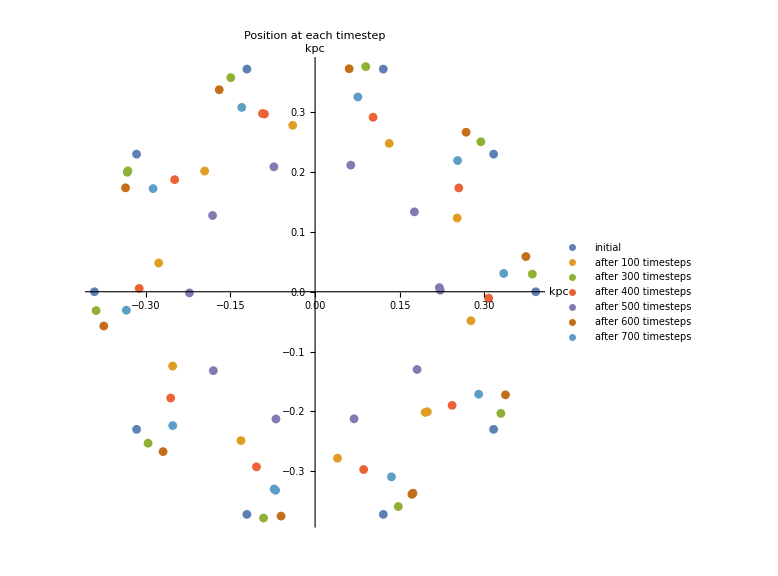

```mathematica
bp4posgraph = ListPlot[{bp4pos1,bp4pos100,bp4pos300,bp4pos400,bp4pos500,bp4pos600,bp4pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Comparing Position with run 1

```mathematica
diff = {}
g[a_,b_]:=(a - ((b * 38.3609 )/ (15) ))

For[j=1,j<11,j++,diff = Append[diff,g[bp1pos1[[j]],bp4pos1[[j]]]] ]
Print[diff]
```

{}

{{9.6336×10^-7,-1.16895×10^-6},{-5.08647×10^-7,7.80233×10^-7},{5.08647×10^-7,7.80233×10^-7},{-9.6336×10^-7,-1.16895×10^-6},{-3.8662×10^-7,3.84143×10^-22},{-9.6336×10^-7,1.16895×10^-6},{5.08647×10^-7,-7.80233×10^-7},{-5.08647×10^-7,-7.80233×10^-7},{9.6336×10^-7,1.16895×10^-6},{3.8662×10^-7,4.87453×10^-22}}

```mathematica
diff={}
For[j=1,j<11,j++,diff = Append[diff,g[bp1pos2[[j]],bp4pos2[[j]]]] ]
Print[diff]
```

{}

{{-0.185026,0.579497},{-0.494018,0.365262},{-0.614364,0.00512768},{-0.500044,-0.356966},{-0.194725,-0.582712},{0.184973,-0.58588},{0.494018,-0.365261},{0.614364,-0.00512512},{0.500044,0.356967},{0.194724,0.582712}}

```mathematica
diff={}
For[j=1,j<11,j++,diff = Append[diff,g[bp1pos10[[j]],bp4pos10[[j]]]] ]
Print[diff]
```

{}

{{-0.131091,0.559637},{-0.437933,0.381431},{-0.578497,0.0511802},{-0.498111,-0.298618},{-0.227449,-0.534374},{0.130069,-0.566025},{0.437937,-0.381465},{0.578512,-0.05118},{0.498101,0.298638},{0.227408,0.534372}}

#### Comparing Velocity with run 1

```mathematica
bp1vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10,9;;10}]
bp4vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10,9;;10}]
```

{{3.69316,-5.0832},{5.97566,-1.94161},{5.97566,1.94161},{3.69316,5.0832},{3.84734×10^-16,6.28319},{-3.69316,5.0832},{-5.97566,1.94161},{-5.97566,-1.94161},{-3.69316,-5.0832},{-1.1542×10^-15,-6.28319}}

{{110.644,-152.289},{179.026,-58.1691},{179.026,58.1691},{110.644,152.289},{1.15263×10^-14,188.239},{-110.644,152.289},{-179.026,58.1691},{-179.026,-58.1691},{-110.644,-152.289},{-3.4579×10^-14,-188.239}}

```mathematica
diff = {}
h[a_,b_]:=(a - ((b * 38.3609*(1.94249*10^16) )/ (15*(75.4212*10^9*yrsec)) ))

For[j=1,j<11,j++,diff = Append[diff,h[bp1vel1[[j]],bp4vel1[[j]]]] ]
Print[diff]
```

{}

{{1.38376,-1.90457},{2.23897,-0.727486},{2.23897,0.727486},{1.38376,1.90457},{1.44153×10^-16,2.3542},{-1.38376,1.90457},{-2.23897,0.727486},{-2.23897,-0.727486},{-1.38376,-1.90457},{-4.32456×10^-16,-2.3542}}

```mathematica
bp1magvel = 6.28319
bp4magvel = 301.029
h[bp1magvel,bp4magvel]
```

6.28319

301.029

0.0000152055

#### Converting Position from ChplUltra to dimensionless units

```mathematica
d[a_,b_]:=a - (b/0.391023)
pos={}
For[j=1,j<11,j++,pos = Append[pos,d[bp1pos200[[j]],bp4pos200[[j]]]] ]
Print[pos]
```

{}

{{0.738676,-0.736796},{1.04082,-0.163931},{0.939213,0.479601},{0.476568,0.943405},{-0.171942,1.04612},{-0.757739,0.745136},{-1.05202,0.15627},{-0.942224,-0.490087},{-0.474542,-0.947899},{0.169574,-1.0431}}

#### Comparing dot products

```mathematica
bp1dp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10020,1}];
bp4dp1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10020,1}];
```

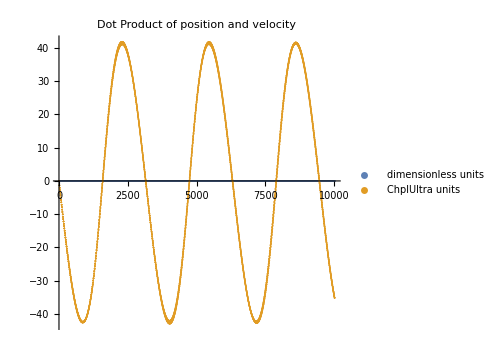

```mathematica
dp1graph = ListPlot[{bp1dp1,bp4dp1},PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"dimensionless units","ChplUltra units"}, PlotLabel->"Dot Product of position and velocity"]
```

```mathematica
bp1dp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10020,2}];
bp4dp2 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10020,2}];
```

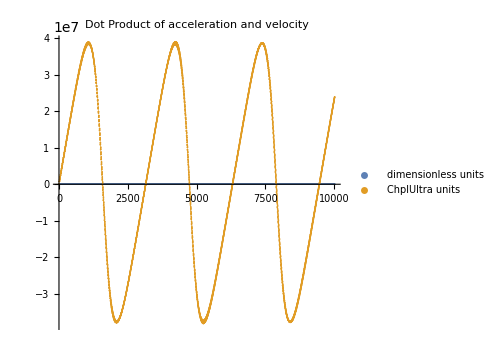

```mathematica
dp2graph = ListPlot[{bp1dp2,bp4dp2},PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"dimensionless units","ChplUltra units"}, PlotLabel->"Dot Product of acceleration and velocity"]
```

#### 5. ChplUltra units with 128 box, with initial velocity fixed NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp5pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1;;10,6;;7}];
bp5pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",11;;20,6;;7}];
bp5pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",101;;110,6;;7}];
bp5pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",201;;210,6;;7}];
bp5pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",301;;310,6;;7}];
bp5pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",991;;1000,6;;7}];
bp5pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1991;;2000,6;;7}];
bp5pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",2991;;3000,6;;7}];
bp5pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",3991;;4000,6;;7}];
bp5pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",4991;;5000,6;;7}];
bp5pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",5991;;6000,6;;7}];
bp5pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",6991;;7000,6;;7}];
bp5pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",7991;;8000,6;;7}];
bp5pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",8991;;9000,6;;7}];
bp5pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",9991;;10000,6;;7}];
```

#### Position

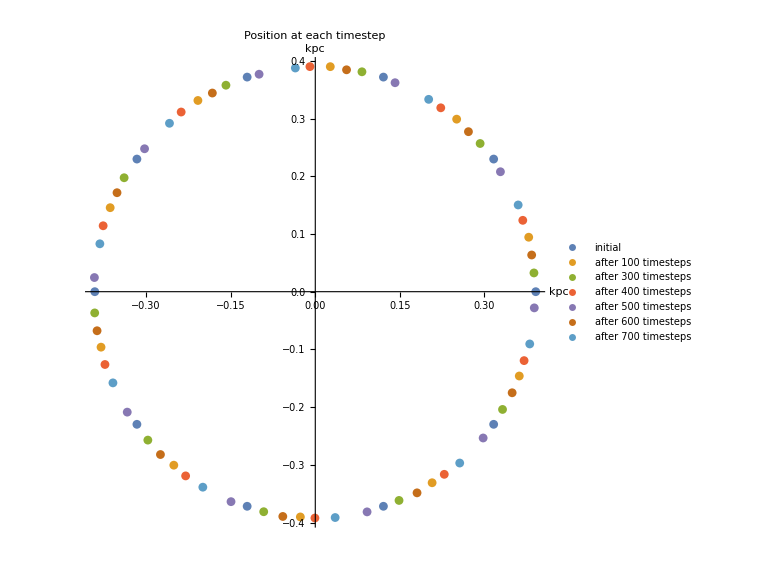

```mathematica
bp5posgraph = ListPlot[{bp5pos1,bp5pos100,bp5pos300,bp5pos400,bp5pos500,bp5pos600,bp5pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

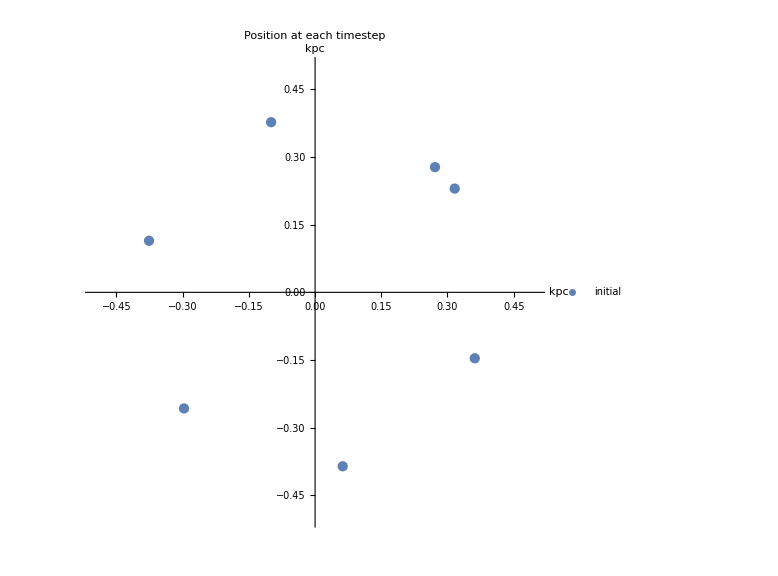

```mathematica
bp5pos2graph = ListPlot[{bp5pos1[[1]],bp5pos100[[1]],bp5pos200[[1]],bp5pos300[[1]],bp5pos400[[1]],bp5pos500[[1]],bp5pos600[[1]]},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity

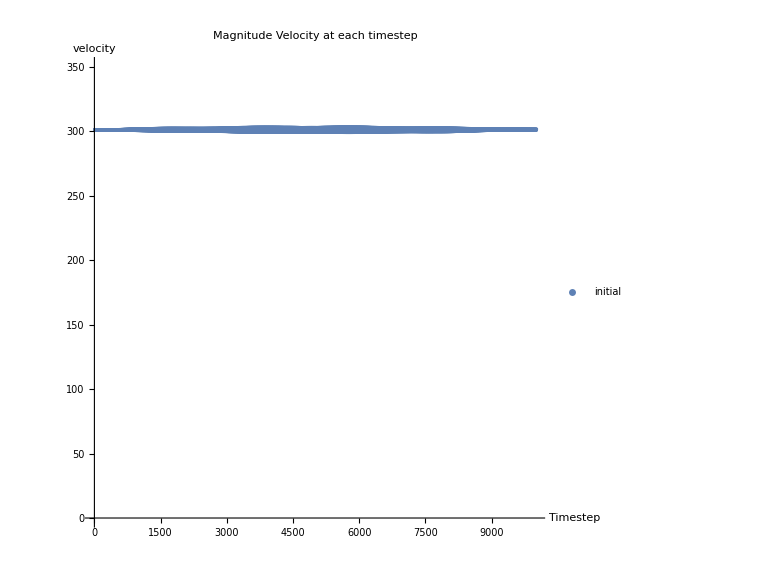

```mathematica
bp5vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1;;10020,4}];
bp5velgraph = ListPlot[{bp5vel},PlotRange->{{0,10000},{0,350}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","velocity"}, PlotLabel-> "Magnitude Velocity at each timestep"]
```

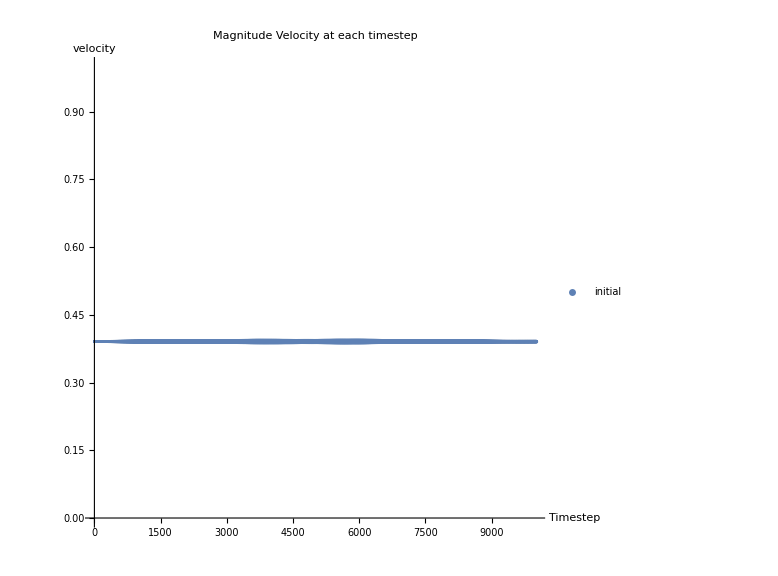

```mathematica
bp5acc = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1;;10020,5}];
bp5accgraph = ListPlot[{bp5acc},PlotRange->{{0,10000},{0,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","velocity"}, PlotLabel-> "Magnitude Velocity at each timestep"]
```

```mathematica
z
```

z

```mathematica
pot[[]]
```

{{1},126,{{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,116,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467},126,{1}}}
 |  |  |  |